This is a top-level working notebook. Evaluate its initialization cells once to load the shared packages and initialize the calculator. The complete original notebook is preserved under legacy-original/.

The first initialization cell bootstraps this notebook by loading myNotebookInit.wl. The next initialization cell loads the complete project from src/LoadProject.wl. All remaining calculator setup runs afterward; the CALCULATOR BODY remains interactive.

This package/notebook does calculations of performance for a RICH detector.

# ---... SETUP

## PREAMBLE

```mathematica
navHistory = {};
pushHistory[] := AppendTo[navHistory,
    First @ SelectedCells @ EvaluationNotebook[]
];
goBack[] := If[navHistory =!= {},
    SelectionMove[Last[navHistory], All, Cell];
(*    navHistory = Most[navHistory];*)
];
```

```mathematica
$trackedContext=$Context;
$trackedPath=$ContextPath;

$Post=Function[expr,
If[$Context=!=$trackedContext,
Print["Changed Context to: ",$Context];
$trackedContext=$Context
];
If[$ContextPath=!=$trackedPath,
Print["Changed ContextPath to: ",$ContextPath];
$trackedPath=$ContextPath];
expr];
```

## COMMON NOTEBOOK SETUP

bootstrap

```mathematica
(*════════════════ External Load Tracker—full fixed version ═══════════════════════════════*)
(*── State ───────────────────────────────────────────────────────────*)
$LoadLog={};
$Tracking=False;
(*── System-path filter ───────────────────────────────────────────────*)
$SystemPathPatterns={___~~("Wolfram"|"Mathematica"|"SystemFiles"|"Paclets"|"AddOns"|"Applications")~~___,___~~"RichNotebookInit"~~___,___~~".wl",___~~"init.m"};
isSystemPath[s_String]:=AnyTrue[$SystemPathPatterns,StringMatchQ[s,#]&]
(*── Logger (silently drops system paths) ─────────────────────────────*)
logLoad[type_String,target_String]/;!isSystemPath[target]:=AppendTo[$LoadLog,<|"Type"->type,"Target"->target, "caller nb"->myNotebookInit`nbFileName  ,"Time"->DateString[],"AbsTime"->AbsoluteTime[]|>]
logLoad[_,_]:=Null
(*── Hook Get ($Tracking guard prevents infinite recursion) ───────────*)
Unprotect[Get];
Get[file_String,opts___]/;!$Tracking:=Block[{$Tracking=True},logLoad["Get",file];
Get[file,opts]]
Protect[Get];
(*── Hook Needs ───────────────────────────────────────────────────────*)
Unprotect[Needs];
Needs[ctx_String,opts___]/;!$Tracking:=Block[{$Tracking=True},logLoad["Needs",ctx];
Needs[ctx,opts]]
Protect[Needs];
(*── Save log to disk ─────────────────────────────────────────────────*)
SaveLoadLog[path_String:"load_log.wdx"]:=(Export[path,$LoadLog];
Print["Log saved to: ",path])
(*── Reload log from disk ─────────────────────────────────────────────*)
LoadSavedLog[path_String:"load_log.wdx"]:=($LoadLog=Import[path];
Print["Loaded ",Length[$LoadLog]," entries from: ",path])
(*── Summary report ───────────────────────────────────────────────────*)
SummarizeLoads[]:=Module[{ds,byType,rows},If[$LoadLog==={},Print["No loads recorded."];Return[]];
ds=Dataset[$LoadLog];
Print["━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━"];
Print["  External Load Summary"];
Print["━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━"];
Print["  Total calls : ",Length[$LoadLog]];
(*Use Counts directly on raw list—no Dataset keys issues*)byType=Counts[$LoadLog[[All,"Type"]]];
Print["  By type:"];
KeyValueMap[Print["    ",#1," → ",#2," call(s)"]&,byType];
(*Tally {target,type} pairs directly—no association key unpacking*)rows=ReverseSortBy[Tally[{#["Target"],#["Type"]}&/@$LoadLog],Last];
Print["\n  Calls per target (sorted by frequency):"];
Scan[Print["    ",#[[1,1]],"  [",#[[1,2]],"]  ×",#[[2]]]&,rows];
Print["━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━"];
ds   (*Dataset renders nicely in the notebook output*)]
(*── Reset ────────────────────────────────────────────────────────────*)
ClearLoadLog[]:=($LoadLog={};Print["Log cleared."])
(*════════════════════════════════════════════════════════════════════*)
Print["Load Tracker ready.  Functions: SummarizeLoads[], ","SaveLoadLog[], LoadSavedLog[], ClearLoadLog[]"]
```

Load Tracker ready.  Functions: SummarizeLoads[], SaveLoadLog[], LoadSavedLog[], ClearLoadLog[]

```mathematica
SummarizeLoads[];
```

━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━

External Load Summary

━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━

Total calls : 5

By type:

Needs → 5 call(s)

Calls per target (sorted by frequency):

statDataAnal`  [Needs]  ×1

rich`  [Needs]  ×1

Notation`  [Needs]  ×1

myNotebookInit`  [Needs]  ×1

base`  [Needs]  ×1

━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━

INIT

```mathematica
(*TO FIX*)
(*SetDirectory[NotebookDirectory[]];Needs["packageLoadDebugger`"];installPackageLoadDebugger[];clearPackageLoadLog[]*)
```

```mathematica
(*TO FIX*)
(*Needs["myNotebookInit`"];*)(*check with loadMyFile: with package can use Needs instead; with notebook need to Get*)
(*Needs["base`"];*)(*check with loadMyFile: with package can use Needs instead; with notebook need to Get*)
(*Needs["statDataAnal`"];*)(*check with loadMyFile: with package can use Needs instead; with notebook need to Get*)
(**)
```

```mathematica
(*Off[Unset::norep];*)(*for superClearSet complaints...*)
```

```mathematica
(* ::Section::Initialization::*)
(*Notebook bootstrap (WL 14.3)*)
Module[{dir,pkg},
dir=Quiet@NotebookDirectory[];
If[!StringQ[dir],dir=$HomeDirectory];(*unsaved notebook fallback*)
pkg=FileNameJoin[{dir,"../src/myNotebookInit.wl"}];
If[!FileExistsQ[pkg],MessageDialog["Missing myNotebookInit.wl at:\n"<>pkg];Return[$Failed];];
Get[pkg];
Print@Column[{
Button["Save a versioned copy",myNotebookInit`saveVersionedCopy[myNotebookInit`versionTAG,NotebookDirectory[]],Method->"Queued"],Button["Save a txt copy",With[{out=myNotebookInit`saveNotebookTextCopy[]},If[StringQ[out],Print["Saved: ",out]]],Method->"Queued"],Button["List init code (prints)",Print/@myNotebookInit`listInitializationCells[],Method->"Queued"],Button["Highlight init cells",myNotebookInit`selectInitializationCells[],Method->"Queued"],Button["Mark ALL Input cells as initialization",myNotebookInit`markInputCellsAsInitialization[True],Method->"Queued"],Button["Clear initialization on Input cells",myNotebookInit`markInputCellsAsInitialization[False],Method->"Queued"],Button["Delete all empty cells",myNotebookInit`deleteAllEmptyCellsInNotebook,Method->"Queued"],Button["Export all Output cells to PNG (notebook dir)",myNotebookInit`saveAsPngAllOutputCells[],Method->"Queued"],Button["Export all Output cells to PDF (notebook dir)",myNotebookInit`saveAsPdfAllOutputCells[],Method->"Queued"],Button["Show diagnostics",myNotebookInit`showDiagnostics[],Method->"Queued"],
Button["Show error message cells",Print[Cells[CellStyle->{"MSG","Message"}]],Method->"Preemptive"]
}]
];
(**)
(*Apply default options+optional stylesheet+optional session init*)
myNotebookInit`applyNotebookDefaults[];
myNotebookInit`loadSessionInit[];
myNotebookInit`manageMyStyleNotebook[];
myNotebookInit`applyStyleSheetIfPresent["myStyle.nb"];
(**)
(*loadMyFile["myDockedCells.wl",RICHProjectPath["src"]]*)
```

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***----------------------------------- myNotebookInit ---------------------------------------------***

*==================================================================================================*

============================================================

myNotebookInit  loaded  |  Version: v.09-05-2026

Kernel: 15.0.1 for Microsoft Windows (64-bit) (July 2, 2026)

Context: myNotebookInit`Private`

============================================================

Explicit Load Tracker ready. Functions: loadMyFile[], loadNeeds[], summarizeLoads[], saveLoadLog[], loadSavedLog[], clearLoadLog[]

Save a versioned copy
Save a txt copy
List init code (prints)
Highlight init cells
Mark ALL Input cells as initialization
Clear initialization on Input cells
Delete all empty cells
Export all Output cells to PNG (notebook dir)
Export all Output cells to PDF (notebook dir)
Show diagnostics
Show error message cells

Changed ContextPath to: {myNotebookInit`,OpticaDocumentation`,System`,Global`}

OK -- myStyle.nb already in StyleSheets: C:\Users\Ale\AppData\Roaming\Wolfram\SystemFiles\FrontEnd\StyleSheets\myStyle.nb

============================================================

[loadMyFile] START

timestamp:  2026-08-08  19:22:55

requested:  LoadProject.wl

dir mode:   explicit (authoritative)

cwd:        C:\Users\Ale

nb dir:     C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\src

local path: C:\Users\Ale\LoadProject.wl

ref path:   C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\src\LoadProject.wl

resolved:   C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\src\LoadProject.wl

loading...

Explicit Load Tracker ready. Functions: loadMyFile[], loadNeeds[], summarizeLoads[], saveLoadLog[], loadSavedLog[], clearLoadLog[]

NotebookDirectory[] : C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks

SETTING CELL STYLE DATA RULES - CellStyleDataRules

InputNotebook                           cikzh_shm31FrontEndObject[LinkObject["cikzh_shm", 3, 1]]31 ------- C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nbC:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nb

EvaluationNotebook                      cikzh_shm31FrontEndObject[LinkObject["cikzh_shm", 3, 1]]31 ------- C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nbC:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nb

This package lives at $InputFileName    C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\src\CellStyleDataRules.wl

This package lives at $Input           C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\src\CellStyleDataRules.wl

END  cikzh_shm31FrontEndObject[LinkObject["cikzh_shm", 3, 1]]31 ------- C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nbC:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nb

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***--- base ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***---                  LOADING base                                                                  ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

---------------- Context Diagnostics ----------------

$Context        : base`

$ContextPath    :

base`

myNotebookInit`

System`

Your loaded packages (lowercase only):

base`

myNotebookInit`

Recently created lowercase contexts:

base`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

*************************************************************************************************

Start running  -D260808T192256

t0=AbsoluteTime[]   3.995205776126713×10^9

*************************************************************************************************

32

ape = 20

nut = 400

mouse = 400+cat

ape=20

nut=400

mouse=400+cat

ape = 20

nut = 400

mouse = 400+cat

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***---                  END base                                                                       ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

---------------- Context Diagnostics ----------------

$Context        : Global`

$ContextPath    :

base`

myNotebookInit`

OpticaDocumentation`

System`

Global`

Your loaded packages (lowercase only):

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***--- statDataAnal ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

---------------- Context Diagnostics ----------------

$Context        : Global`

$ContextPath    :

base`

myNotebookInit`

OpticaDocumentation`

System`

Global`

Your loaded packages (lowercase only):

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

loading statDataAnal

#   |   Min  |   Max  |  Mean  | Median | StdDev | Skewn. | Kurto.
20 | 0.19 | 24.9 | 12.4375 | 12.46 | 7.05448 | -0.0333154 | 1.99322

==================================================================================================

==================================================================================================

endEvalPrintOut

==================================================================================================

==================================================================================================

timeStamp            ===>>>   -D260808T192304

--------------------------------------------------------------------------------------------------

Cells[MSG,Message}]      ===>>> 
{}

--------------------------------------------------------------------------------------------------

$Context                 ===>>>  Global`

--------------------------------------------------------------------------------------------------

$ContextPath             ===>>>  statDataAnal`
base`
myNotebookInit`
OpticaDocumentation`
System`
Global`

--------------------------------------------------------------------------------------------------

checkNewCreatedSymbols   ===>>>  {}

--------------------------------------------------------------------------------------------------

No loads recorded.

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***--- physics-general ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***--- physics-general ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

LOADING physics-general

--->>> might need some specific symbols defined elsewhere!

beta==1. beta

gamma==1. gamma

p/(√(m^2+p^2))

1.

∞

{0.0005109989,0.1056584,0.1395702,0.493677,0.938272}

<|Ele→510.999*10^-6,Muo→0.106,Pio→0.140,Kao→0.494,Pro→0.938|>

{7.,7.,7.,7.,7.}

{510.999*10^-6,0.106,0.140,0.494,0.938}

{261.120*10^-9,0.011,0.019,0.244,0.880}

==================================================================================================

==================================================================================================

endEvalPrintOut

==================================================================================================

==================================================================================================

timeStamp            ===>>>   -D260808T192309

--------------------------------------------------------------------------------------------------

Cells[MSG,Message}]      ===>>> 
{}

--------------------------------------------------------------------------------------------------

$Context                 ===>>>  Global`

--------------------------------------------------------------------------------------------------

$ContextPath             ===>>>  physicsGeneral`
statDataAnal`
base`
myNotebookInit`
OpticaDocumentation`
System`
Global`

--------------------------------------------------------------------------------------------------

checkNewCreatedSymbols   ===>>>  {}

--------------------------------------------------------------------------------------------------

No loads recorded.

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***--- inputDataForRICH ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

--->>> might need some specific symbols defined elsewhere!

Dependency myNotebookInit`loadMyFile is available. Source: already loaded

MemberQ[$Packages, myNotebookInit`] = True

==================================================================================================

==================================================================================================

$Notebooks == True

==================================================================================================

==================================================================================================

=== MONITORED SYMBOL (one symbol at a time!) : LAPPDTMEnergyData       before n/a       after  n/a

=== MONITORED SYMBOL (one symbol at a time!) : MAPMT22EnergyData       before n/a       after  n/a

=== MONITORED SYMBOL (one symbol at a time!) : MPPCHPKEnergyData       before n/a       after  n/a

=== MONITORED SYMBOL (one symbol at a time!) : SIPMFBKEnergyData       before n/a       after  n/a

!!! MAPMT22EnergyData : n/a -->> {{6.88189,0.},{6.69606,0.},{6.51999,0.},{6.35295,0.},{6.22536,0.0289},{5.99566,0.0884},{5.68604,0.1648},{5.32258,0.2499},{4.91104,0.3098},{4.55841,0.3471},{4.25317,0.3676},{3.98625,0.3749},{3.75085,0.3764},{3.5417,0.3661},{3.35455,0.3537},{3.18627,0.3413},{3.02504,0.3237},{2.87934,0.3011},{2.75074,0.274},{2.63314,0.2397},{2.53463,0.198},{2.43732,0.1586},{2.34725,0.1191},{2.26108,0.0862},{2.17868,0.0636},{2.10421,0.0438},{2.0347,0.0278},{1.97154,0.0168},{1.91039,0.0088},{1.8563,0.0044},{1.81582,0.0026},{1.78636,0.0008},{1.76847,0.0004},{1.75844,0.},{1.74606,0.},{1.73385,0.},{1.72181,0.}}

!!! SIPMFBKEnergyData : n/a -->> {{6.79924,0.},{6.61778,0.},{6.44576,0.},{6.28245,0.},{6.12722,0.},{5.97946,0.},{5.83867,0.},{5.70436,0.},{5.57608,0.},{5.45345,0.},{5.3361,0.},{5.22369,0.},{5.11591,0.},{5.0125,0.},{4.91318,0.},{4.81773,0.},{4.72591,0.},{4.63752,0.},{4.5658,0.0213},{4.50409,0.0532},{4.46018,0.0812},{4.43276,0.1052},{4.41335,0.1437},{4.38913,0.1669},{4.37319,0.1769},{4.34956,0.204},{4.32604,0.2312},{4.31054,0.2405},{4.29516,0.2544},{4.27222,0.2789},{4.25711,0.2875},{4.23472,0.3061},{4.20513,0.3306},{4.16866,0.3485},{4.13998,0.3571},{4.10462,0.371},{4.06986,0.3803},{4.03568,0.3883},{4.0088,0.3936},{3.97564,0.4008},{3.93663,0.4055},{3.89838,0.4088},{3.86087,0.4107},{3.81795,0.4121},{3.77012,0.4134},{3.73491,0.4141},{3.64992,0.4234},{3.52168,0.4413},{3.39729,0.4605},{3.27247,0.479},{3.14003,0.4956},{3.0331,0.4976},{2.95123,0.4863},{2.87713,0.4704},{2.7871,0.4433},{2.7117,0.4181},{2.65485,0.3982},{2.60312,0.3823},{2.55337,0.3677},{2.52129,0.3624},{2.4848,0.3565},{2.43699,0.3472},{2.38385,0.3339},{2.31946,0.3174},{2.25213,0.2981},{2.18067,0.2769},{2.10621,0.2557},{2.01955,0.2319},{1.93819,0.2087},{1.87273,0.1904},{1.81846,0.1747},{1.77778,0.1622},{1.75802,0.1562},{1.74761,0.1534},{1.73538,0.1496},{1.72332,0.1457}}

!!! MPPCHPKEnergyData : n/a -->> {{6.19921,0.},{6.04801,0.},{5.90401,0.},{5.76671,0.},{5.63565,0.},{5.51041,0.},{5.39062,0.},{5.27592,0.},{5.16601,0.},{5.06058,0.},{4.95937,0.},{4.86213,0.},{4.76862,0.},{4.67865,0},{4.59201,0.00134476},{4.50852,0.00630863},{4.42801,0.017731},{4.35032,0.0305645},{4.27532,0.0759657},{4.20285,0.133412},{4.13281,0.248713},{4.06506,0.287651},{3.99949,0.307601},{3.93601,0.323874},{3.87451,0.342402},{3.8149,0.354447},{3.7571,0.363859},{3.70102,0.372084},{3.64659,0.379193},{3.59374,0.385404},{3.54241,0.390949},{3.49251,0.396177},{3.44401,0.400598},{3.39683,0.405866},{3.35092,0.411329},{3.30625,0.420449},{3.26274,0.433185},{3.22037,0.444956},{3.17908,0.45526},{3.13884,0.46448},{3.0996,0.472302},{3.06134,0.479005},{3.024,0.485006},{2.98757,0.490225},{2.952,0.494518},{2.91728,0.498119},{2.88335,0.501812},{2.85021,0.505224},{2.81782,0.507966},{2.78616,0.509642},{2.7552,0.510093},{2.72493,0.509319},{2.69531,0.50762},{2.66633,0.5049},{2.63796,0.501201},{2.61019,0.496527},{2.583,0.490761},{2.55638,0.484055},{2.53029,0.476532},{2.50473,0.468342},{2.47968,0.459724},{2.45513,0.450819},{2.43106,0.442015},{2.40746,0.433494},{2.38431,0.425041},{2.3616,0.416637},{2.33932,0.40821},{2.31746,0.399751},{2.296,0.391343},{2.27494,0.383008},{2.25426,0.374769},{2.23395,0.36676},{2.214,0.358877},{2.19441,0.351095},{2.17516,0.343404},{2.15625,0.335792},{2.13766,0.32813},{2.11939,0.320543},{2.10143,0.313047},{2.08377,0.305657},{2.0664,0.298387},{2.04933,0.29129},{2.03253,0.2844},{2.016,0.27766},{1.99975,0.27107},{1.98375,0.264627},{1.968,0.258333},{1.95251,0.252187},{1.93725,0.246252},{1.92224,0.240526},{1.90745,0.234939},{1.89289,0.229481},{1.87855,0.224141},{1.86442,0.218908},{1.85051,0.213769},{1.8368,0.208714},{1.8233,0.203731},{1.80999,0.19881},{1.79687,0.193771},{1.78395,0.188706},{1.7712,0.183693}}

!!! LAPPDTMEnergyData : n/a -->> {{6.19921,0.272594},{6.04801,0.276124},{5.90401,0.281265},{5.76671,0.286468},{5.63565,0.291639},{5.51041,0.297635},{5.39062,0.305077},{5.27592,0.310764},{5.16601,0.314491},{5.06058,0.317371},{4.95937,0.319416},{4.86213,0.320798},{4.76862,0.321751},{4.67865,0.322878},{4.59201,0.324248},{4.50852,0.325225},{4.42801,0.325665},{4.35032,0.325836},{4.27532,0.325852},{4.20285,0.3258},{4.13281,0.3258},{4.06506,0.325799},{3.99949,0.32575},{3.93601,0.325819},{3.87451,0.326191},{3.8149,0.326676},{3.7571,0.327144},{3.70102,0.327615},{3.64659,0.328066},{3.59374,0.328534},{3.54241,0.329144},{3.49251,0.329405},{3.44401,0.328995},{3.39683,0.32765},{3.35092,0.325166},{3.30625,0.321367},{3.26274,0.316383},{3.22037,0.309887},{3.17908,0.301397},{3.13884,0.291174},{3.0996,0.280945},{3.06134,0.271477},{3.024,0.26191},{2.98757,0.253064},{2.952,0.245382},{2.91728,0.236787},{2.88335,0.228589},{2.85021,0.22149},{2.81782,0.213829},{2.78616,0.205943},{2.7552,0.19988},{2.72493,0.193635},{2.69531,0.186679},{2.66633,0.180633},{2.63796,0.175396},{2.61019,0.169057},{2.583,0.162896},{2.55638,0.157105},{2.53029,0.151518},{2.50473,0.14573},{2.47968,0.140935},{2.45513,0.13664},{2.43106,0.132019},{2.40746,0.127341},{2.38431,0.122774},{2.3616,0.118492},{2.33932,0.114667},{2.31746,0.111175},{2.296,0.107413},{2.27494,0.103731},{2.25426,0.100153},{2.23395,0.0967648},{2.214,0.0935049},{2.19441,0.0903586},{2.17516,0.0873162},{2.15625,0.0844072},{2.13766,0.0815684},{2.11939,0.0787746},{2.10143,0.0760004},{2.08377,0.0731135},{2.0664,0.0702177},{2.04933,0.0673536},{2.03253,0.0645428},{2.016,0.0618136},{1.99975,0.05918},{1.98375,0.0566577},{1.968,0.0542647},{1.95251,0.0521047},{1.93725,0.0500781},{1.92224,0.0481461},{1.90745,0.0462546},{1.89289,0.0443605},{1.87855,0.0425637},{1.86442,0.0408911},{1.85051,0.0393718},{1.8368,0.0380438},{1.8233,0.0369414},{1.80999,0.0360985},{1.79687,0.0355492},{1.78395,0.0353274},{1.7712,0.0354671}}

referenceCavernPres = 1013.25

referenceCavernTemp = 298.15

theRealGasPresMbar = 1013.25

theRealGasTempKelv = 298.15

theFullCf = 0.9161495891329867191644

==================================================================================================

==================================================================================================

Redefining the original xyzEnergyData for cleanup and aligning among the different sensors

==================================================================================================

==================================================================================================

!!! LAPPDTMEnergyData : {{6.19921,0.272594},{6.04801,0.276124},{5.90401,0.281265},{5.76671,0.286468},{5.63565,0.291639},{5.51041,0.297635},{5.39062,0.305077},{5.27592,0.310764},{5.16601,0.314491},{5.06058,0.317371},{4.95937,0.319416},{4.86213,0.320798},{4.76862,0.321751},{4.67865,0.322878},{4.59201,0.324248},{4.50852,0.325225},{4.42801,0.325665},{4.35032,0.325836},{4.27532,0.325852},{4.20285,0.3258},{4.13281,0.3258},{4.06506,0.325799},{3.99949,0.32575},{3.93601,0.325819},{3.87451,0.326191},{3.8149,0.326676},{3.7571,0.327144},{3.70102,0.327615},{3.64659,0.328066},{3.59374,0.328534},{3.54241,0.329144},{3.49251,0.329405},{3.44401,0.328995},{3.39683,0.32765},{3.35092,0.325166},{3.30625,0.321367},{3.26274,0.316383},{3.22037,0.309887},{3.17908,0.301397},{3.13884,0.291174},{3.0996,0.280945},{3.06134,0.271477},{3.024,0.26191},{2.98757,0.253064},{2.952,0.245382},{2.91728,0.236787},{2.88335,0.228589},{2.85021,0.22149},{2.81782,0.213829},{2.78616,0.205943},{2.7552,0.19988},{2.72493,0.193635},{2.69531,0.186679},{2.66633,0.180633},{2.63796,0.175396},{2.61019,0.169057},{2.583,0.162896},{2.55638,0.157105},{2.53029,0.151518},{2.50473,0.14573},{2.47968,0.140935},{2.45513,0.13664},{2.43106,0.132019},{2.40746,0.127341},{2.38431,0.122774},{2.3616,0.118492},{2.33932,0.114667},{2.31746,0.111175},{2.296,0.107413},{2.27494,0.103731},{2.25426,0.100153},{2.23395,0.0967648},{2.214,0.0935049},{2.19441,0.0903586},{2.17516,0.0873162},{2.15625,0.0844072},{2.13766,0.0815684},{2.11939,0.0787746},{2.10143,0.0760004},{2.08377,0.0731135},{2.0664,0.0702177},{2.04933,0.0673536},{2.03253,0.0645428},{2.016,0.0618136},{1.99975,0.05918},{1.98375,0.0566577},{1.968,0.0542647},{1.95251,0.0521047},{1.93725,0.0500781},{1.92224,0.0481461},{1.90745,0.0462546},{1.89289,0.0443605},{1.87855,0.0425637},{1.86442,0.0408911},{1.85051,0.0393718},{1.8368,0.0380438},{1.8233,0.0369414},{1.80999,0.0360985},{1.79687,0.0355492},{1.78395,0.0353274},{1.7712,0.0354671}} -->> {{6.19921,0.272594},{6.16837,0.273097},{6.13783,0.273714},{6.1076,0.274432},{6.07766,0.27524},{6.04801,0.276124},{6.01865,0.277073},{5.98957,0.278074},{5.96078,0.279114},{5.93226,0.280182},{5.90401,0.281265},{5.87603,0.282303},{5.84831,0.283344},{5.82085,0.284385},{5.79365,0.285427},{5.76671,0.286468},{5.74001,0.287477},{5.71356,0.288492},{5.68735,0.289519},{5.66138,0.290566},{5.63565,0.291639},{5.61014,0.292752},{5.58487,0.293904},{5.55983,0.295098},{5.53501,0.29634},{5.51041,0.297635},{5.48603,0.29911},{5.46186,0.300618},{5.4379,0.302132},{5.41416,0.303627},{5.39062,0.305077},{5.36728,0.306361},{5.34415,0.307574},{5.32121,0.308713},{5.29847,0.309777},{5.27592,0.310764},{5.25357,0.31163},{5.2314,0.312427},{5.20942,0.313164},{5.18762,0.313849},{5.16601,0.314491},{5.14457,0.315134},{5.12331,0.315744},{5.10223,0.31632},{5.08132,0.316862},{5.06058,0.317371},{5.04001,0.317841},{5.0196,0.31828},{4.99936,0.318687},{4.97929,0.319066},{4.95937,0.319416},{4.93961,0.319738},{4.92001,0.320035},{4.90056,0.32031},{4.88127,0.320564},{4.86213,0.320798},{4.84313,0.321004},{4.82429,0.321197},{4.80559,0.321382},{4.78703,0.321565},{4.76862,0.321751},{4.75035,0.32196},{4.73222,0.322177},{4.71423,0.322402},{4.69637,0.322635},{4.67865,0.322878},{4.66106,0.323153},{4.6436,0.323432},{4.62628,0.323712},{4.60908,0.323985},{4.59201,0.324248},{4.57506,0.32448},{4.55824,0.324694},{4.54155,0.324891},{4.52497,0.325068},{4.50852,0.325225},{4.49218,0.325348},{4.47596,0.325451},{4.45986,0.325536},{4.44388,0.325607},{4.42801,0.325665},{4.41225,0.325717},{4.3966,0.325759},{4.38107,0.325793},{4.36564,0.325818},{4.35032,0.325836},{4.33511,0.325849},{4.32001,0.325856},{4.30501,0.325859},{4.29011,0.325857},{4.27532,0.325852},{4.26063,0.325843},{4.24603,0.325833},{4.23154,0.325821},{4.21715,0.32581},{4.20285,0.3258},{4.18866,0.325798},{4.17455,0.325797},{4.16054,0.325797},{4.14663,0.325798},{4.13281,0.3258},{4.11908,0.325801},{4.10544,0.325802},{4.09189,0.325802},{4.07843,0.325801},{4.06506,0.325799},{4.05177,0.325787},{4.03857,0.325775},{4.02546,0.325764},{4.01243,0.325755},{3.99949,0.32575},{3.98663,0.325748},{3.97385,0.325753},{3.96116,0.325765},{3.94854,0.325787},{3.93601,0.325819},{3.92355,0.325875},{3.91117,0.325942},{3.89887,0.326018},{3.88665,0.326101},{3.87451,0.326191},{3.86244,0.326283},{3.85044,0.326379},{3.83852,0.326477},{3.82667,0.326577},{3.8149,0.326676},{3.8032,0.326771},{3.79157,0.326864},{3.78001,0.326958},{3.76852,0.327051},{3.7571,0.327144},{3.74575,0.327239},{3.73446,0.327333},{3.72325,0.327428},{3.7121,0.327522},{3.70102,0.327615},{3.69001,0.327706},{3.67906,0.327796},{3.66817,0.327886},{3.65735,0.327976},{3.64659,0.328066},{3.6359,0.328154},{3.62527,0.328244},{3.6147,0.328337},{3.60419,0.328433},{3.59374,0.328534},{3.58336,0.32866},{3.57303,0.328788},{3.56276,0.328914},{3.55256,0.329034},{3.54241,0.329144},{3.53231,0.329234},{3.52228,0.329308},{3.5123,0.329363},{3.50238,0.329396},{3.49251,0.329405},{3.4827,0.329385},{3.47295,0.329336},{3.46325,0.329256},{3.4536,0.329143},{3.44401,0.328995},{3.43447,0.328807},{3.42498,0.32858},{3.41554,0.328313},{3.40616,0.328004},{3.39683,0.32765},{3.38755,0.32725},{3.37832,0.326803},{3.36914,0.326307},{3.36001,0.325762},{3.35092,0.325166},{3.34189,0.324507},{3.33291,0.323797},{3.32397,0.323036},{3.31509,0.322226},{3.30625,0.321367},{3.29745,0.320475},{3.28871,0.319534},{3.28001,0.31854},{3.27135,0.31749},{3.26274,0.316383},{3.25418,0.31522},{3.24566,0.313993},{3.23719,0.312698},{3.22876,0.31133},{3.22037,0.309887},{3.21203,0.30834},{3.20373,0.306716},{3.19547,0.305015},{3.18725,0.303242},{3.17908,0.301397},{3.17095,0.299435},{3.16286,0.297419},{3.15481,0.29536},{3.14681,0.293274},{3.13884,0.291174},{3.13091,0.289104},{3.12303,0.28704},{3.11518,0.284988},{3.10737,0.282955},{3.0996,0.280945},{3.09188,0.279018},{3.08418,0.277115},{3.07653,0.275228},{3.06892,0.273351},{3.06134,0.271477},{3.0538,0.269545},{3.04629,0.267616},{3.03883,0.265696},{3.0314,0.263791},{3.024,0.26191},{3.01665,0.260069},{3.00933,0.25826},{3.00204,0.256488},{2.99479,0.254754},{2.98757,0.253064},{2.98039,0.251501},{2.97324,0.249968},{2.96613,0.248448},{2.95905,0.246925},{2.952,0.245382},{2.94499,0.243694},{2.93801,0.24198},{2.93107,0.240251},{2.92416,0.238517},{2.91728,0.236787},{2.91043,0.235094},{2.90361,0.233421},{2.89683,0.231776},{2.89007,0.230163},{2.88335,0.228589},{2.87666,0.227134},{2.87,0.22571},{2.86338,0.224304},{2.85678,0.222901},{2.85021,0.22149},{2.84367,0.219992},{2.83717,0.218474},{2.83069,0.216939},{2.82424,0.21539},{2.81782,0.213829},{2.81143,0.212204},{2.80507,0.210587},{2.79874,0.208993},{2.79244,0.20744},{2.78616,0.205943},{2.77991,0.204648},{2.7737,0.203411},{2.7675,0.202214},{2.76134,0.201043},{2.7552,0.19988},{2.7491,0.198662},{2.74301,0.197433},{2.73696,0.196188},{2.73093,0.194924},{2.72493,0.193635},{2.71895,0.192249},{2.713,0.190847},{2.70708,0.189443},{2.70118,0.188049},{2.69531,0.186679},{2.68946,0.1854},{2.68364,0.184157},{2.67784,0.182948},{2.67207,0.181774},{2.66633,0.180633},{2.66061,0.179582},{2.65491,0.178548},{2.64924,0.177516},{2.64359,0.17647},{2.63796,0.175396},{2.63236,0.174175},{2.62678,0.172921},{2.62123,0.171643},{2.6157,0.170352},{2.61019,0.169057},{2.60471,0.167805},{2.59925,0.166561},{2.59381,0.165327},{2.5884,0.164105},{2.583,0.162896},{2.57763,0.161713},{2.57229,0.160544},{2.56696,0.159387},{2.56166,0.158241},{2.55638,0.157105},{2.55112,0.155984},{2.54588,0.154868},{2.54066,0.153754},{2.53546,0.152638},{2.53029,0.151518},{2.52514,0.150338},{2.52,0.14916},{2.51489,0.147993},{2.5098,0.146846},{2.50473,0.14573},{2.49968,0.144707},{2.49465,0.14372},{2.48964,0.142765},{2.48465,0.141838},{2.47968,0.140935},{2.47473,0.140062},{2.4698,0.139203},{2.46489,0.138351},{2.46,0.137499},{2.45513,0.13664},{2.45028,0.135734},{2.44545,0.134816},{2.44063,0.13389},{2.43584,0.132957},{2.43106,0.132019},{2.42631,0.131083},{2.42157,0.130145},{2.41685,0.129208},{2.41214,0.128273},{2.40746,0.127341},{2.40279,0.126413},{2.39815,0.125491},{2.39352,0.124576},{2.38891,0.12367},{2.38431,0.122774},{2.37974,0.121889},{2.37518,0.121017},{2.37063,0.12016},{2.36611,0.119318},{2.3616,0.118492},{2.35711,0.117695},{2.35264,0.116914},{2.34819,0.11615},{2.34375,0.115401},{2.33932,0.114667},{2.33492,0.113961},{2.33053,0.113264},{2.32616,0.11257},{2.3218,0.111876},{2.31746,0.111175},{2.31314,0.110433},{2.30883,0.109683},{2.30454,0.108928},{2.30026,0.10817},{2.296,0.107413},{2.29176,0.106669},{2.28753,0.105929},{2.28332,0.105193},{2.27912,0.10446},{2.27494,0.103731},{2.27077,0.103005},{2.26662,0.102283},{2.26249,0.101566},{2.25836,0.100856},{2.25426,0.100153},{2.25017,0.0994622},{2.24609,0.0987784},{2.24203,0.0981012},{2.23798,0.0974302},{2.23395,0.0967648},{2.22993,0.096103},{2.22593,0.0954462},{2.22194,0.0947944},{2.21796,0.0941473},{2.214,0.0935049},{2.21006,0.0928669},{2.20612,0.0922333},{2.20221,0.0916042},{2.1983,0.0909793},{2.19441,0.0903586},{2.19053,0.0897409},{2.18667,0.0891275},{2.18282,0.0885188},{2.17898,0.0879149},{2.17516,0.0873162},{2.17135,0.0867257},{2.16756,0.0861401},{2.16377,0.0855588},{2.16,0.0849813},{2.15625,0.0844072},{2.1525,0.0838346},{2.14877,0.0832647},{2.14506,0.0826971},{2.14135,0.0821318},{2.13766,0.0815684},{2.13398,0.0810069},{2.13031,0.0804469},{2.12666,0.0798883},{2.12302,0.079331},{2.11939,0.0787746},{2.11577,0.0782224},{2.11217,0.07767},{2.10857,0.0771162},{2.10499,0.0765601},{2.10143,0.0760004},{2.09787,0.0754287},{2.09433,0.0748534},{2.0908,0.0742751},{2.08728,0.0736949},{2.08377,0.0731135},{2.08027,0.0725337},{2.07679,0.0719539},{2.07331,0.0713744},{2.06985,0.0707956},{2.0664,0.0702177},{2.06297,0.0696416},{2.05954,0.069067},{2.05612,0.068494},{2.05272,0.0679228},{2.04933,0.0673536},{2.04594,0.0667862},{2.04257,0.0662213},{2.03921,0.0656589},{2.03587,0.0650993},{2.03253,0.0645428},{2.0292,0.06399},{2.02589,0.0634405},{2.02258,0.0628946},{2.01929,0.0623522},{2.016,0.0618136},{2.01273,0.0612787},{2.00947,0.0607478},{2.00622,0.060221},{2.00298,0.0596983},{1.99975,0.05918},{1.99652,0.0586661},{1.99332,0.0581567},{1.99012,0.0576521},{1.98693,0.0571524},{1.98375,0.0566577},{1.98058,0.0561655},{1.97742,0.0556792},{1.97427,0.0551998},{1.97113,0.054728},{1.968,0.0542647},{1.96488,0.0538173},{1.96178,0.0533783},{1.95868,0.0529471},{1.95559,0.0525228},{1.95251,0.0521047},{1.94944,0.0516899},{1.94638,0.0512802},{1.94333,0.0508752},{1.94028,0.0504746},{1.93725,0.0500781},{1.93423,0.0496858},{1.93122,0.0492969},{1.92821,0.048911},{1.92522,0.0485275},{1.92224,0.0481461},{1.91926,0.0477659},{1.91629,0.047387},{1.91334,0.0470091},{1.91039,0.0466317},{1.90745,0.0462546},{1.90452,0.0458728},{1.9016,0.0454917},{1.89869,0.045112},{1.89578,0.0447347},{1.89289,0.0443605},{1.89,0.0439925},{1.88713,0.0436286},{1.88426,0.043269},{1.8814,0.042914},{1.87855,0.0425637},{1.87571,0.0422183},{1.87287,0.0418781},{1.87005,0.0415434},{1.86723,0.0412143},{1.86442,0.0408911},{1.86162,0.0405738},{1.85883,0.0402629},{1.85605,0.0399587},{1.85328,0.0396615},{1.85051,0.0393718},{1.84775,0.0390898},{1.845,0.0388157},{1.84226,0.0385498},{1.83953,0.0382925},{1.8368,0.0380438},{1.83409,0.0378042},{1.83138,0.0375739},{1.82868,0.0373532},{1.82598,0.0371422},{1.8233,0.0369414},{1.82062,0.036751},{1.81795,0.0365712},{1.81529,0.0364024},{1.81263,0.0362447},{1.80999,0.0360985},{1.80735,0.0359641},{1.80472,0.0358417},{1.8021,0.0357315},{1.79948,0.0356339},{1.79687,0.0355492},{1.79427,0.0354775},{1.79168,0.0354192},{1.78909,0.0353746},{1.78652,0.0353439},{1.78395,0.0353274},{1.78138,0.0353253},{1.77883,0.035338},{1.77628,0.0353657},{1.77374,0.0354086},{1.7712,0.0354671}}

!!! MAPMT22EnergyData : {{6.88189,0.},{6.69606,0.},{6.51999,0.},{6.35295,0.},{6.22536,0.0289},{5.99566,0.0884},{5.68604,0.1648},{5.32258,0.2499},{4.91104,0.3098},{4.55841,0.3471},{4.25317,0.3676},{3.98625,0.3749},{3.75085,0.3764},{3.5417,0.3661},{3.35455,0.3537},{3.18627,0.3413},{3.02504,0.3237},{2.87934,0.3011},{2.75074,0.274},{2.63314,0.2397},{2.53463,0.198},{2.43732,0.1586},{2.34725,0.1191},{2.26108,0.0862},{2.17868,0.0636},{2.10421,0.0438},{2.0347,0.0278},{1.97154,0.0168},{1.91039,0.0088},{1.8563,0.0044},{1.81582,0.0026},{1.78636,0.0008},{1.76847,0.0004},{1.75844,0.},{1.74606,0.},{1.73385,0.},{1.72181,0.}} -->> {{6.19921,0.0364202},{6.16837,0.0455426},{6.13783,0.0545923},{6.1076,0.0632975},{6.07766,0.0713863},{6.04801,0.0785868},{6.01865,0.0846271},{5.98957,0.0900311},{5.96078,0.0977454},{5.93226,0.105353},{5.90401,0.112825},{5.87603,0.120137},{5.84831,0.12726},{5.82085,0.134169},{5.79365,0.140835},{5.76671,0.147232},{5.74001,0.153333},{5.71356,0.15911},{5.68735,0.164538},{5.66138,0.17071},{5.63565,0.176852},{5.61014,0.182913},{5.58487,0.188896},{5.55983,0.194803},{5.53501,0.200637},{5.51041,0.2064},{5.48603,0.212094},{5.46186,0.217722},{5.4379,0.223285},{5.41416,0.228786},{5.39062,0.234227},{5.36728,0.239611},{5.34415,0.24494},{5.32121,0.250159},{5.29847,0.254384},{5.27592,0.258454},{5.25357,0.262372},{5.2314,0.266145},{5.20942,0.269777},{5.18762,0.273273},{5.16601,0.27664},{5.14457,0.279881},{5.12331,0.283003},{5.10223,0.286011},{5.08132,0.288909},{5.06058,0.291704},{5.04001,0.2944},{5.0196,0.297003},{4.99936,0.299518},{4.97929,0.30195},{4.95937,0.304305},{4.93961,0.306587},{4.92001,0.308802},{4.90056,0.311109},{4.88127,0.313487},{4.86213,0.315807},{4.84313,0.31807},{4.82429,0.320276},{4.80559,0.322427},{4.78703,0.324522},{4.76862,0.326563},{4.75035,0.328551},{4.73222,0.330486},{4.71423,0.332369},{4.69637,0.334202},{4.67865,0.335983},{4.66106,0.337716},{4.6436,0.3394},{4.62628,0.341035},{4.60908,0.342624},{4.59201,0.344166},{4.57506,0.345663},{4.55824,0.347114},{4.54155,0.348542},{4.52497,0.349925},{4.50852,0.351265},{4.49218,0.352563},{4.47596,0.353819},{4.45986,0.355033},{4.44388,0.356206},{4.42801,0.357338},{4.41225,0.35843},{4.3966,0.359483},{4.38107,0.360496},{4.36564,0.361471},{4.35032,0.362407},{4.33511,0.363305},{4.32001,0.364167},{4.30501,0.364991},{4.29011,0.365779},{4.27532,0.366531},{4.26063,0.367248},{4.24603,0.367914},{4.23154,0.368529},{4.21715,0.369111},{4.20285,0.369661},{4.18866,0.370179},{4.17455,0.370668},{4.16054,0.371127},{4.14663,0.371558},{4.13281,0.371962},{4.11908,0.37234},{4.10544,0.372692},{4.09189,0.373021},{4.07843,0.373326},{4.06506,0.373609},{4.05177,0.37387},{4.03857,0.374112},{4.02546,0.374334},{4.01243,0.374538},{3.99949,0.374725},{3.98663,0.374895},{3.97385,0.375161},{3.96116,0.375414},{3.94854,0.375651},{3.93601,0.37587},{3.92355,0.37607},{3.91117,0.376252},{3.89887,0.376413},{3.88665,0.376553},{3.87451,0.376672},{3.86244,0.376768},{3.85044,0.376841},{3.83852,0.37689},{3.82667,0.376914},{3.8149,0.376913},{3.8032,0.376885},{3.79157,0.376829},{3.78001,0.376746},{3.76852,0.376633},{3.7571,0.376491},{3.74575,0.376258},{3.73446,0.375921},{3.72325,0.375555},{3.7121,0.375161},{3.70102,0.374741},{3.69001,0.374295},{3.67906,0.373826},{3.66817,0.373334},{3.65735,0.372821},{3.64659,0.372288},{3.6359,0.371736},{3.62527,0.371167},{3.6147,0.370582},{3.60419,0.369982},{3.59374,0.369368},{3.58336,0.368743},{3.57303,0.368107},{3.56276,0.367461},{3.55256,0.366807},{3.54241,0.366146},{3.53231,0.36554},{3.52228,0.364934},{3.5123,0.364322},{3.50238,0.363706},{3.49251,0.363085},{3.4827,0.36246},{3.47295,0.361832},{3.46325,0.3612},{3.4536,0.360564},{3.44401,0.359926},{3.43447,0.359285},{3.42498,0.358641},{3.41554,0.357995},{3.40616,0.357348},{3.39683,0.356699},{3.38755,0.356048},{3.37832,0.355397},{3.36914,0.354744},{3.36001,0.354092},{3.35092,0.353459},{3.34189,0.352858},{3.33291,0.352255},{3.32397,0.351652},{3.31509,0.351046},{3.30625,0.350439},{3.29745,0.349828},{3.28871,0.349214},{3.28001,0.348596},{3.27135,0.347973},{3.26274,0.347345},{3.25418,0.346712},{3.24566,0.346073},{3.23719,0.345427},{3.22876,0.344774},{3.22037,0.344114},{3.21203,0.343445},{3.20373,0.342768},{3.19547,0.342081},{3.18725,0.341384},{3.17908,0.340649},{3.17095,0.339899},{3.16286,0.339138},{3.15481,0.338367},{3.14681,0.337585},{3.13884,0.336792},{3.13091,0.335988},{3.12303,0.335173},{3.11518,0.334348},{3.10737,0.333511},{3.0996,0.332663},{3.09188,0.331804},{3.08418,0.330934},{3.07653,0.330053},{3.06892,0.32916},{3.06134,0.328256},{3.0538,0.327341},{3.04629,0.326414},{3.03883,0.325476},{3.0314,0.324526},{3.024,0.323565},{3.01665,0.322591},{3.00933,0.321606},{3.00204,0.32061},{2.99479,0.319601},{2.98757,0.318581},{2.98039,0.317549},{2.97324,0.316504},{2.96613,0.315448},{2.95905,0.31438},{2.952,0.3133},{2.94499,0.312208},{2.93801,0.311104},{2.93107,0.309988},{2.92416,0.308859},{2.91728,0.307718},{2.91043,0.306565},{2.90361,0.305399},{2.89683,0.304221},{2.89007,0.303031},{2.88335,0.301828},{2.87666,0.300618},{2.87,0.299405},{2.86338,0.298178},{2.85678,0.296939},{2.85021,0.295685},{2.84367,0.294418},{2.83717,0.293138},{2.83069,0.291842},{2.82424,0.290533},{2.81782,0.289208},{2.81143,0.287869},{2.80507,0.286514},{2.79874,0.285144},{2.79244,0.283758},{2.78616,0.282356},{2.77991,0.280938},{2.7737,0.279503},{2.7675,0.278051},{2.76134,0.276582},{2.7552,0.275096},{2.7491,0.273599},{2.74301,0.272102},{2.73696,0.270586},{2.73093,0.269052},{2.72493,0.267497},{2.71895,0.265922},{2.713,0.264326},{2.70708,0.262709},{2.70118,0.261069},{2.69531,0.259406},{2.68946,0.25772},{2.68364,0.256009},{2.67784,0.254274},{2.67207,0.252513},{2.66633,0.250726},{2.66061,0.248913},{2.65491,0.247072},{2.64924,0.245204},{2.64359,0.243307},{2.63796,0.24138},{2.63236,0.2394},{2.62678,0.237238},{2.62123,0.23505},{2.6157,0.232839},{2.61019,0.230606},{2.60471,0.228354},{2.59925,0.226086},{2.59381,0.223802},{2.5884,0.221506},{2.583,0.219201},{2.57763,0.216887},{2.57229,0.214568},{2.56696,0.212245},{2.56166,0.209921},{2.55638,0.207599},{2.55112,0.20528},{2.54588,0.202966},{2.54066,0.200661},{2.53546,0.198366},{2.53029,0.196234},{2.52514,0.194144},{2.52,0.192067},{2.51489,0.190001},{2.5098,0.187947},{2.50473,0.185904},{2.49968,0.18387},{2.49465,0.181846},{2.48964,0.179829},{2.48465,0.177821},{2.47968,0.175819},{2.47473,0.173823},{2.4698,0.171833},{2.46489,0.169847},{2.46,0.167865},{2.45513,0.165886},{2.45028,0.16391},{2.44545,0.161935},{2.44063,0.159962},{2.43584,0.157954},{2.43106,0.155869},{2.42631,0.153786},{2.42157,0.151704},{2.41685,0.149625},{2.41214,0.147551},{2.40746,0.145481},{2.40279,0.143418},{2.39815,0.141362},{2.39352,0.139314},{2.38891,0.137275},{2.38431,0.135246},{2.37974,0.133228},{2.37518,0.131222},{2.37063,0.129229},{2.36611,0.127251},{2.3616,0.125288},{2.35711,0.123341},{2.35264,0.121411},{2.34819,0.119499},{2.34375,0.117641},{2.33932,0.115812},{2.33492,0.114002},{2.33053,0.112214},{2.32616,0.110446},{2.3218,0.1087},{2.31746,0.106975},{2.31314,0.105272},{2.30883,0.103591},{2.30454,0.101933},{2.30026,0.100298},{2.296,0.0986865},{2.29176,0.0970985},{2.28753,0.0955344},{2.28332,0.0939948},{2.27912,0.0924798},{2.27494,0.09099},{2.27077,0.0895255},{2.26662,0.0880868},{2.26249,0.0866743},{2.25836,0.0853526},{2.25426,0.0840903},{2.25017,0.0828531},{2.24609,0.08164},{2.24203,0.0804498},{2.23798,0.0792817},{2.23395,0.0781344},{2.22993,0.077007},{2.22593,0.0758984},{2.22194,0.0748075},{2.21796,0.0737333},{2.214,0.0726747},{2.21006,0.0716307},{2.20612,0.0706003},{2.20221,0.0695822},{2.1983,0.0685757},{2.19441,0.0675794},{2.19053,0.0665925},{2.18667,0.0656138},{2.18282,0.0646423},{2.17898,0.063677},{2.17516,0.0626365},{2.17135,0.0615943},{2.16756,0.0605579},{2.16377,0.0595273},{2.16,0.0585027},{2.15625,0.0574844},{2.1525,0.0564725},{2.14877,0.0554674},{2.14506,0.054469},{2.14135,0.0534778},{2.13766,0.0524938},{2.13398,0.0515173},{2.13031,0.0505485},{2.12666,0.0495875},{2.12302,0.0486347},{2.11939,0.0476901},{2.11577,0.046754},{2.11217,0.0458267},{2.10857,0.0449082},{2.10499,0.0439988},{2.10143,0.0431033},{2.09787,0.0422186},{2.09433,0.0413434},{2.0908,0.0404779},{2.08728,0.0396222},{2.08377,0.0387764},{2.08027,0.0379406},{2.07679,0.037115},{2.07331,0.0362996},{2.06985,0.0354946},{2.0664,0.0347001},{2.06297,0.0339161},{2.05954,0.0331429},{2.05612,0.0323806},{2.05272,0.0316292},{2.04933,0.0308888},{2.04594,0.0301597},{2.04257,0.0294418},{2.03921,0.0287354},{2.03587,0.0280405},{2.03253,0.0273692},{2.0292,0.0267158},{2.02589,0.0260739},{2.02258,0.0254431},{2.01929,0.0248234},{2.016,0.0242145},{2.01273,0.0236163},{2.00947,0.0230287},{2.00622,0.0224514},{2.00298,0.0218844},{1.99975,0.0213274},{1.99652,0.0207802},{1.99332,0.0202428},{1.99012,0.0197149},{1.98693,0.0191964},{1.98375,0.0186871},{1.98058,0.0181869},{1.97742,0.0176955},{1.97427,0.0172129},{1.97113,0.0167374},{1.968,0.0162607},{1.96488,0.0157925},{1.96178,0.0153325},{1.95868,0.014881},{1.95559,0.0144379},{1.95251,0.0140032},{1.94944,0.0135768},{1.94638,0.0131589},{1.94333,0.0127494},{1.94028,0.0123482},{1.93725,0.0119555},{1.93423,0.0115712},{1.93122,0.0111953},{1.92821,0.0108279},{1.92522,0.0104688},{1.92224,0.0101182},{1.91926,0.00977598},{1.91629,0.00944222},{1.91334,0.00911689},{1.91039,0.0088},{1.90745,0.00849815},{1.90452,0.00820459},{1.9016,0.00791922},{1.89869,0.00764195},{1.89578,0.00737268},{1.89289,0.00711129},{1.89,0.00685769},{1.88713,0.00661178},{1.88426,0.00637346},{1.8814,0.00614262},{1.87855,0.00591917},{1.87571,0.00570299},{1.87287,0.005494},{1.87005,0.00529208},{1.86723,0.00509715},{1.86442,0.00490909},{1.86162,0.0047278},{1.85883,0.00455319},{1.85605,0.00439855},{1.85328,0.00437154},{1.85051,0.00432534},{1.84775,0.00426124},{1.845,0.00418051},{1.84226,0.00408446},{1.83953,0.00397437},{1.8368,0.00385153},{1.83409,0.00371722},{1.83138,0.00357273},{1.82868,0.00341935},{1.82598,0.00325837},{1.8233,0.00309107},{1.82062,0.00291875},{1.81795,0.00274268},{1.81529,0.00253847},{1.81263,0.00225202},{1.80999,0.00199902},{1.80735,0.0017769},{1.80472,0.00158311},{1.8021,0.00141506},{1.79948,0.00127019},{1.79687,0.00114594},{1.79427,0.00103974},{1.79168,0.000949027},{1.78909,0.000871226},{1.78652,0.000803774},{1.78395,0.000822745},{1.78138,0.000811802},{1.77883,0.000770146},{1.77628,0.000703399},{1.77374,0.000617185},{1.7712,0.000517127}}

!!! MPPCHPKEnergyData : {{6.19921,0.},{6.04801,0.},{5.90401,0.},{5.76671,0.},{5.63565,0.},{5.51041,0.},{5.39062,0.},{5.27592,0.},{5.16601,0.},{5.06058,0.},{4.95937,0.},{4.86213,0.},{4.76862,0.},{4.67865,0},{4.59201,0.00134476},{4.50852,0.00630863},{4.42801,0.017731},{4.35032,0.0305645},{4.27532,0.0759657},{4.20285,0.133412},{4.13281,0.248713},{4.06506,0.287651},{3.99949,0.307601},{3.93601,0.323874},{3.87451,0.342402},{3.8149,0.354447},{3.7571,0.363859},{3.70102,0.372084},{3.64659,0.379193},{3.59374,0.385404},{3.54241,0.390949},{3.49251,0.396177},{3.44401,0.400598},{3.39683,0.405866},{3.35092,0.411329},{3.30625,0.420449},{3.26274,0.433185},{3.22037,0.444956},{3.17908,0.45526},{3.13884,0.46448},{3.0996,0.472302},{3.06134,0.479005},{3.024,0.485006},{2.98757,0.490225},{2.952,0.494518},{2.91728,0.498119},{2.88335,0.501812},{2.85021,0.505224},{2.81782,0.507966},{2.78616,0.509642},{2.7552,0.510093},{2.72493,0.509319},{2.69531,0.50762},{2.66633,0.5049},{2.63796,0.501201},{2.61019,0.496527},{2.583,0.490761},{2.55638,0.484055},{2.53029,0.476532},{2.50473,0.468342},{2.47968,0.459724},{2.45513,0.450819},{2.43106,0.442015},{2.40746,0.433494},{2.38431,0.425041},{2.3616,0.416637},{2.33932,0.40821},{2.31746,0.399751},{2.296,0.391343},{2.27494,0.383008},{2.25426,0.374769},{2.23395,0.36676},{2.214,0.358877},{2.19441,0.351095},{2.17516,0.343404},{2.15625,0.335792},{2.13766,0.32813},{2.11939,0.320543},{2.10143,0.313047},{2.08377,0.305657},{2.0664,0.298387},{2.04933,0.29129},{2.03253,0.2844},{2.016,0.27766},{1.99975,0.27107},{1.98375,0.264627},{1.968,0.258333},{1.95251,0.252187},{1.93725,0.246252},{1.92224,0.240526},{1.90745,0.234939},{1.89289,0.229481},{1.87855,0.224141},{1.86442,0.218908},{1.85051,0.213769},{1.8368,0.208714},{1.8233,0.203731},{1.80999,0.19881},{1.79687,0.193771},{1.78395,0.188706},{1.7712,0.183693}} -->> {{6.19921,0.},{6.16837,0.},{6.13783,0.},{6.1076,0.},{6.07766,0.},{6.04801,0.},{6.01865,0.},{5.98957,0.},{5.96078,0.},{5.93226,0.},{5.90401,0.},{5.87603,0.},{5.84831,0.},{5.82085,0.},{5.79365,0.},{5.76671,0.},{5.74001,0.},{5.71356,0.},{5.68735,0.},{5.66138,0.},{5.63565,0.},{5.61014,0.},{5.58487,0.},{5.55983,0.},{5.53501,0.},{5.51041,0.},{5.48603,0.},{5.46186,0.},{5.4379,0.},{5.41416,0.},{5.39062,0.},{5.36728,0.},{5.34415,0.},{5.32121,0.},{5.29847,0.},{5.27592,0.},{5.25357,0.},{5.2314,0.},{5.20942,0.},{5.18762,0.},{5.16601,0.},{5.14457,0.},{5.12331,0.},{5.10223,0.},{5.08132,0.},{5.06058,0.},{5.04001,0.},{5.0196,0.},{4.99936,0.},{4.97929,0.},{4.95937,0.},{4.93961,0.},{4.92001,0.},{4.90056,0.},{4.88127,0.},{4.86213,0.},{4.84313,0.},{4.82429,0.},{4.80559,0.},{4.78703,0.},{4.76862,0.},{4.75035,0},{4.73222,0},{4.71423,0},{4.69637,0},{4.67865,0.},{4.66106,0.0000885927},{4.6436,0.000249171},{4.62628,0.000499929},{4.60908,0.000859061},{4.59201,0.00134476},{4.57506,0.00195715},{4.55824,0.00273701},{4.54155,0.00370707},{4.52497,0.00489004},{4.50852,0.00630863},{4.49218,0.00823795},{4.47596,0.0103852},{4.45986,0.0127101},{4.44388,0.0151721},{4.42801,0.017731},{4.41225,0.0191878},{4.3966,0.0209503},{4.38107,0.0232678},{4.36564,0.0263894},{4.35032,0.0305645},{4.33511,0.0376961},{4.32001,0.0459662},{4.30501,0.0552106},{4.29011,0.0652652},{4.27532,0.0759657},{4.26063,0.0850256},{4.24603,0.0949336},{4.23154,0.106056},{4.21715,0.118761},{4.20285,0.133412},{4.18866,0.156139},{4.17455,0.180106},{4.16054,0.20424},{4.14663,0.227467},{4.13281,0.248713},{4.11908,0.260774},{4.10544,0.270239},{4.09189,0.277567},{4.07843,0.283218},{4.06506,0.287651},{4.05177,0.29267},{4.03857,0.297052},{4.02546,0.30092},{4.01243,0.304395},{3.99949,0.307601},{3.98663,0.31096},{3.97385,0.31422},{3.96116,0.317427},{3.94854,0.320629},{3.93601,0.323874},{3.92355,0.327679},{3.91117,0.331504},{3.89887,0.335279},{3.88665,0.338935},{3.87451,0.342402},{3.86244,0.345206},{3.85044,0.347782},{3.83852,0.350161},{3.82667,0.352372},{3.8149,0.354447},{3.8032,0.356494},{3.79157,0.358447},{3.78001,0.360317},{3.76852,0.362118},{3.7571,0.363859},{3.74575,0.365596},{3.73446,0.367287},{3.72325,0.368932},{3.7121,0.370531},{3.70102,0.372084},{3.69001,0.373589},{3.67906,0.37505},{3.66817,0.37647},{3.65735,0.377851},{3.64659,0.379193},{3.6359,0.3805},{3.62527,0.381772},{3.6147,0.383013},{3.60419,0.384222},{3.59374,0.385404},{3.58336,0.386555},{3.57303,0.387682},{3.56276,0.388789},{3.55256,0.389877},{3.54241,0.390949},{3.53231,0.392036},{3.52228,0.393106},{3.5123,0.394155},{3.50238,0.39518},{3.49251,0.396177},{3.4827,0.397073},{3.47295,0.39795},{3.46325,0.398821},{3.4536,0.399699},{3.44401,0.400598},{3.43447,0.401605},{3.42498,0.40264},{3.41554,0.403699},{3.40616,0.404776},{3.39683,0.405866},{3.38755,0.406832},{3.37832,0.407834},{3.36914,0.408899},{3.36001,0.410055},{3.35092,0.411329},{3.34189,0.412862},{3.33291,0.414541},{3.32397,0.416365},{3.31509,0.418335},{3.30625,0.420449},{3.29745,0.422854},{3.28871,0.425366},{3.28001,0.42795},{3.27135,0.430568},{3.26274,0.433185},{3.25418,0.435632},{3.24566,0.438037},{3.23719,0.440395},{3.22876,0.442703},{3.22037,0.444956},{3.21203,0.447122},{3.20373,0.449232},{3.19547,0.45129},{3.18725,0.453298},{3.17908,0.45526},{3.17095,0.4572},{3.16286,0.459095},{3.15481,0.460942},{3.14681,0.462738},{3.13884,0.46448},{3.13091,0.466147},{3.12303,0.467761},{3.11518,0.469323},{3.10737,0.470836},{3.0996,0.472302},{3.09188,0.473719},{3.08418,0.475094},{3.07653,0.476432},{3.06892,0.477734},{3.06134,0.479005},{3.0538,0.480264},{3.04629,0.481494},{3.03883,0.482695},{3.0314,0.483866},{3.024,0.485006},{3.01665,0.486117},{3.00933,0.487196},{3.00204,0.488241},{2.99479,0.489251},{2.98757,0.490225},{2.98039,0.49115},{2.97324,0.49204},{2.96613,0.492897},{2.95905,0.493722},{2.952,0.494518},{2.94499,0.495269},{2.93801,0.495998},{2.93107,0.496712},{2.92416,0.497417},{2.91728,0.498119},{2.91043,0.498862},{2.90361,0.499606},{2.89683,0.500347},{2.89007,0.501084},{2.88335,0.501812},{2.87666,0.502529},{2.87,0.503232},{2.86338,0.503917},{2.85678,0.504582},{2.85021,0.505224},{2.84367,0.505839},{2.83717,0.506423},{2.83069,0.506975},{2.82424,0.50749},{2.81782,0.507966},{2.81143,0.508392},{2.80507,0.508774},{2.79874,0.50911},{2.79244,0.5094},{2.78616,0.509642},{2.77991,0.50983},{2.7737,0.509969},{2.7675,0.510059},{2.76134,0.510101},{2.7552,0.510093},{2.7491,0.510026},{2.74301,0.509913},{2.73696,0.509756},{2.73093,0.509557},{2.72493,0.509319},{2.71895,0.509056},{2.713,0.508755},{2.70708,0.508416},{2.70118,0.508038},{2.69531,0.50762},{2.68946,0.507156},{2.68364,0.506652},{2.67784,0.506108},{2.67207,0.505524},{2.66633,0.5049},{2.66061,0.504239},{2.65491,0.503538},{2.64924,0.502798},{2.64359,0.502019},{2.63796,0.501201},{2.63236,0.500348},{2.62678,0.499455},{2.62123,0.498521},{2.6157,0.497546},{2.61019,0.496527},{2.60471,0.495456},{2.59925,0.494343},{2.59381,0.493189},{2.5884,0.491994},{2.583,0.490761},{2.57763,0.489491},{2.57229,0.488184},{2.56696,0.486842},{2.56166,0.485466},{2.55638,0.484055},{2.55112,0.482611},{2.54588,0.481135},{2.54066,0.47963},{2.53546,0.478095},{2.53029,0.476532},{2.52514,0.47494},{2.52,0.473323},{2.51489,0.471683},{2.5098,0.470022},{2.50473,0.468342},{2.49968,0.466649},{2.49465,0.464939},{2.48964,0.463214},{2.48465,0.461475},{2.47968,0.459724},{2.47473,0.457954},{2.4698,0.456175},{2.46489,0.454391},{2.46,0.452605},{2.45513,0.450819},{2.45028,0.449045},{2.44545,0.447275},{2.44063,0.445513},{2.43584,0.443759},{2.43106,0.442015},{2.42631,0.440295},{2.42157,0.438585},{2.41685,0.436883},{2.41214,0.435186},{2.40746,0.433494},{2.40279,0.431799},{2.39815,0.430106},{2.39352,0.428415},{2.38891,0.426727},{2.38431,0.425041},{2.37974,0.423358},{2.37518,0.421677},{2.37063,0.419997},{2.36611,0.418317},{2.3616,0.416637},{2.35711,0.414954},{2.35264,0.413269},{2.34819,0.411584},{2.34375,0.409897},{2.33932,0.40821},{2.33492,0.406518},{2.33053,0.404825},{2.32616,0.403133},{2.3218,0.401441},{2.31746,0.399751},{2.31314,0.398065},{2.30883,0.39638},{2.30454,0.394699},{2.30026,0.39302},{2.296,0.391343},{2.29176,0.38967},{2.28753,0.387999},{2.28332,0.386332},{2.27912,0.384668},{2.27494,0.383008},{2.27077,0.381349},{2.26662,0.379694},{2.26249,0.378045},{2.25836,0.376403},{2.25426,0.374769},{2.25017,0.373152},{2.24609,0.371544},{2.24203,0.369943},{2.23798,0.368349},{2.23395,0.36676},{2.22993,0.365174},{2.22593,0.363593},{2.22194,0.362017},{2.21796,0.360445},{2.214,0.358877},{2.21006,0.357313},{2.20612,0.355753},{2.20221,0.354196},{2.1983,0.352644},{2.19441,0.351095},{2.19053,0.34955},{2.18667,0.348009},{2.18282,0.34647},{2.17898,0.344936},{2.17516,0.343404},{2.17135,0.34188},{2.16756,0.340357},{2.16377,0.338836},{2.16,0.337314},{2.15625,0.335792},{2.1525,0.33426},{2.14877,0.332726},{2.14506,0.331193},{2.14135,0.329661},{2.13766,0.32813},{2.13398,0.326606},{2.13031,0.325085},{2.12666,0.323568},{2.12302,0.322054},{2.11939,0.320543},{2.11577,0.319036},{2.11217,0.317533},{2.10857,0.316034},{2.10499,0.314539},{2.10143,0.313047},{2.09787,0.31156},{2.09433,0.310078},{2.0908,0.308599},{2.08728,0.307126},{2.08377,0.305657},{2.08027,0.304192},{2.07679,0.302731},{2.07331,0.301277},{2.06985,0.299829},{2.0664,0.298387},{2.06297,0.296952},{2.05954,0.295525},{2.05612,0.294105},{2.05272,0.292693},{2.04933,0.29129},{2.04594,0.289897},{2.04257,0.288512},{2.03921,0.287135},{2.03587,0.285764},{2.03253,0.2844},{2.0292,0.28304},{2.02589,0.281686},{2.02258,0.280338},{2.01929,0.278996},{2.016,0.27766},{2.01273,0.27633},{2.00947,0.275006},{2.00622,0.273688},{2.00298,0.272376},{1.99975,0.27107},{1.99652,0.269769},{1.99332,0.268475},{1.99012,0.267186},{1.98693,0.265904},{1.98375,0.264627},{1.98058,0.263357},{1.97742,0.262092},{1.97427,0.260833},{1.97113,0.25958},{1.968,0.258333},{1.96488,0.25709},{1.96178,0.255853},{1.95868,0.254623},{1.95559,0.253401},{1.95251,0.252187},{1.94944,0.250983},{1.94638,0.249788},{1.94333,0.248601},{1.94028,0.247422},{1.93725,0.246252},{1.93423,0.245093},{1.93122,0.243941},{1.92821,0.242796},{1.92522,0.241658},{1.92224,0.240526},{1.91926,0.239397},{1.91629,0.238275},{1.91334,0.237158},{1.91039,0.236046},{1.90745,0.234939},{1.90452,0.233838},{1.9016,0.232741},{1.89869,0.23165},{1.89578,0.230563},{1.89289,0.229481},{1.89,0.228404},{1.88713,0.227332},{1.88426,0.226264},{1.8814,0.225201},{1.87855,0.224141},{1.87571,0.223087},{1.87287,0.222036},{1.87005,0.220989},{1.86723,0.219947},{1.86442,0.218908},{1.86162,0.217873},{1.85883,0.216841},{1.85605,0.215814},{1.85328,0.21479},{1.85051,0.213769},{1.84775,0.212752},{1.845,0.211738},{1.84226,0.210727},{1.83953,0.209719},{1.8368,0.208714},{1.83409,0.207712},{1.83138,0.206713},{1.82868,0.205716},{1.82598,0.204723},{1.8233,0.203731},{1.82062,0.202748},{1.81795,0.201765},{1.81529,0.200782},{1.81263,0.199798},{1.80999,0.19881},{1.80735,0.197808},{1.80472,0.196803},{1.8021,0.195794},{1.79948,0.194783},{1.79687,0.193771},{1.79427,0.192757},{1.79168,0.191743},{1.78909,0.19073},{1.78652,0.189717},{1.78395,0.188706},{1.78138,0.187697},{1.77883,0.18669},{1.77628,0.185687},{1.77374,0.184688},{1.7712,0.183693}}

!!! SIPMFBKEnergyData : {{6.79924,0.},{6.61778,0.},{6.44576,0.},{6.28245,0.},{6.12722,0.},{5.97946,0.},{5.83867,0.},{5.70436,0.},{5.57608,0.},{5.45345,0.},{5.3361,0.},{5.22369,0.},{5.11591,0.},{5.0125,0.},{4.91318,0.},{4.81773,0.},{4.72591,0.},{4.63752,0.},{4.5658,0.0213},{4.50409,0.0532},{4.46018,0.0812},{4.43276,0.1052},{4.41335,0.1437},{4.38913,0.1669},{4.37319,0.1769},{4.34956,0.204},{4.32604,0.2312},{4.31054,0.2405},{4.29516,0.2544},{4.27222,0.2789},{4.25711,0.2875},{4.23472,0.3061},{4.20513,0.3306},{4.16866,0.3485},{4.13998,0.3571},{4.10462,0.371},{4.06986,0.3803},{4.03568,0.3883},{4.0088,0.3936},{3.97564,0.4008},{3.93663,0.4055},{3.89838,0.4088},{3.86087,0.4107},{3.81795,0.4121},{3.77012,0.4134},{3.73491,0.4141},{3.64992,0.4234},{3.52168,0.4413},{3.39729,0.4605},{3.27247,0.479},{3.14003,0.4956},{3.0331,0.4976},{2.95123,0.4863},{2.87713,0.4704},{2.7871,0.4433},{2.7117,0.4181},{2.65485,0.3982},{2.60312,0.3823},{2.55337,0.3677},{2.52129,0.3624},{2.4848,0.3565},{2.43699,0.3472},{2.38385,0.3339},{2.31946,0.3174},{2.25213,0.2981},{2.18067,0.2769},{2.10621,0.2557},{2.01955,0.2319},{1.93819,0.2087},{1.87273,0.1904},{1.81846,0.1747},{1.77778,0.1622},{1.75802,0.1562},{1.74761,0.1534},{1.73538,0.1496},{1.72332,0.1457}} -->> {{6.19921,0.},{6.16837,0.},{6.13783,0.},{6.1076,0.},{6.07766,0.},{6.04801,0.},{6.01865,0.},{5.98957,0.},{5.96078,0.},{5.93226,0.},{5.90401,0.},{5.87603,0.},{5.84831,0.},{5.82085,0.},{5.79365,0.},{5.76671,0.},{5.74001,0.},{5.71356,0.},{5.68735,0.},{5.66138,0.},{5.63565,0.},{5.61014,0.},{5.58487,0.},{5.55983,0.},{5.53501,0.},{5.51041,0.},{5.48603,0.},{5.46186,0.},{5.4379,0.},{5.41416,0.},{5.39062,0.},{5.36728,0.},{5.34415,0.},{5.32121,0.},{5.29847,0.},{5.27592,0.},{5.25357,0.},{5.2314,0.},{5.20942,0.},{5.18762,0.},{5.16601,0.},{5.14457,0.},{5.12331,0.},{5.10223,0.},{5.08132,0.},{5.06058,0.},{5.04001,0.},{5.0196,0.},{4.99936,0.},{4.97929,0.},{4.95937,0.},{4.93961,0.},{4.92001,0.},{4.90056,0.},{4.88127,0.},{4.86213,0.},{4.84313,0.},{4.82429,0.},{4.80559,0.},{4.78703,0.},{4.76862,0.},{4.75035,0.},{4.73222,0.},{4.71423,0},{4.69637,0},{4.67865,0},{4.66106,0},{4.6436,0},{4.62628,0.00213426},{4.60908,0.00628421},{4.59201,0.0114398},{4.57506,0.0175504},{4.55824,0.0246168},{4.54155,0.0325739},{4.52497,0.0412622},{4.50852,0.050586},{4.49218,0.0643447},{4.47596,0.0737833},{4.45986,0.0813682},{4.44388,0.0924666},{4.42801,0.114422},{4.41225,0.145221},{4.3966,0.161543},{4.38107,0.171809},{4.36564,0.184529},{4.35032,0.203032},{4.33511,0.221812},{4.32001,0.234899},{4.30501,0.245084},{4.29011,0.259997},{4.27532,0.276028},{4.26063,0.285577},{4.24603,0.296163},{4.23154,0.308968},{4.21715,0.32158},{4.20285,0.332063},{4.18866,0.340033},{4.17455,0.346285},{4.16054,0.351111},{4.14663,0.355173},{4.13281,0.359854},{4.11908,0.365353},{4.10544,0.370695},{4.09189,0.374747},{4.07843,0.378242},{4.06506,0.3815},{4.05177,0.384694},{4.03857,0.387674},{4.02546,0.390346},{4.01243,0.392888},{3.99949,0.395677},{3.98663,0.398526},{3.97385,0.401086},{3.96116,0.40289},{3.94854,0.404345},{3.93601,0.405565},{3.92355,0.406778},{3.91117,0.407846},{3.89887,0.408766},{3.88665,0.409507},{3.87451,0.410123},{3.86244,0.410639},{3.85044,0.411097},{3.83852,0.411499},{3.82667,0.411856},{3.8149,0.412193},{3.8032,0.412536},{3.79157,0.412859},{3.78001,0.41316},{3.76852,0.413425},{3.7571,0.413604},{3.74575,0.41382},{3.73446,0.414114},{3.72325,0.414526},{3.7121,0.415097},{3.70102,0.41587},{3.69001,0.416884},{3.67906,0.418182},{3.66817,0.419805},{3.65735,0.421793},{3.64659,0.423904},{3.6359,0.425561},{3.62527,0.427246},{3.6147,0.42894},{3.60419,0.430623},{3.59374,0.432275},{3.58336,0.433874},{3.57303,0.435402},{3.56276,0.436837},{3.55256,0.438161},{3.54241,0.439351},{3.53231,0.440389},{3.52228,0.441254},{3.5123,0.442711},{3.50238,0.444213},{3.49251,0.445718},{3.4827,0.447222},{3.47295,0.448725},{3.46325,0.450226},{3.4536,0.451724},{3.44401,0.453217},{3.43447,0.454704},{3.42498,0.456185},{3.41554,0.457657},{3.40616,0.45912},{3.39683,0.460571},{3.38755,0.461993},{3.37832,0.463402},{3.36914,0.464798},{3.36001,0.466181},{3.35092,0.46755},{3.34189,0.468904},{3.33291,0.470244},{3.32397,0.471568},{3.31509,0.472876},{3.30625,0.474167},{3.29745,0.475442},{3.28871,0.476698},{3.28001,0.477937},{3.27135,0.479168},{3.26274,0.480453},{3.25418,0.481718},{3.24566,0.482958},{3.23719,0.484173},{3.22876,0.485359},{3.22037,0.486513},{3.21203,0.487632},{3.20373,0.488715},{3.19547,0.489757},{3.18725,0.490756},{3.17908,0.49171},{3.17095,0.492616},{3.16286,0.49347},{3.15481,0.49427},{3.14681,0.495014},{3.13884,0.495696},{3.13091,0.496298},{3.12303,0.496836},{3.11518,0.497307},{3.10737,0.497711},{3.0996,0.498044},{3.09188,0.498304},{3.08418,0.498489},{3.07653,0.498597},{3.06892,0.498626},{3.06134,0.498572},{3.0538,0.498435},{3.04629,0.498212},{3.03883,0.497901},{3.0314,0.497462},{3.024,0.496811},{3.01665,0.496078},{3.00933,0.495268},{3.00204,0.494382},{2.99479,0.493427},{2.98757,0.492406},{2.98039,0.491322},{2.97324,0.49018},{2.96613,0.488984},{2.95905,0.487738},{2.952,0.486445},{2.94499,0.485175},{2.93801,0.48387},{2.93107,0.482524},{2.92416,0.481136},{2.91728,0.479706},{2.91043,0.478236},{2.90361,0.476725},{2.89683,0.475174},{2.89007,0.473583},{2.88335,0.471952},{2.87666,0.470278},{2.87,0.468512},{2.86338,0.466708},{2.85678,0.464868},{2.85021,0.462995},{2.84367,0.461091},{2.83717,0.459158},{2.83069,0.4572},{2.82424,0.455219},{2.81782,0.453217},{2.81143,0.451197},{2.80507,0.449162},{2.79874,0.447114},{2.79244,0.445056},{2.78616,0.442998},{2.77991,0.440982},{2.7737,0.43896},{2.7675,0.436933},{2.76134,0.434901},{2.7552,0.432865},{2.7491,0.430825},{2.74301,0.428783},{2.73696,0.426739},{2.73093,0.424692},{2.72493,0.422645},{2.71895,0.420598},{2.713,0.41855},{2.70708,0.416464},{2.70118,0.414373},{2.69531,0.41229},{2.68946,0.410219},{2.68364,0.408163},{2.67784,0.406125},{2.67207,0.404109},{2.66633,0.402117},{2.66061,0.400153},{2.65491,0.398219},{2.64924,0.396395},{2.64359,0.394603},{2.63796,0.39284},{2.63236,0.391105},{2.62678,0.389395},{2.62123,0.387708},{2.6157,0.386043},{2.61019,0.384397},{2.60471,0.382769},{2.59925,0.381042},{2.59381,0.379289},{2.5884,0.377568},{2.583,0.375887},{2.57763,0.374256},{2.57229,0.372684},{2.56696,0.371181},{2.56166,0.369757},{2.55638,0.368419},{2.55112,0.367263},{2.54588,0.366298},{2.54066,0.365398},{2.53546,0.364551},{2.53029,0.363745},{2.52514,0.362969},{2.52,0.362196},{2.51489,0.361382},{2.5098,0.360572},{2.50473,0.359762},{2.49968,0.35895},{2.49465,0.358134},{2.48964,0.35731},{2.48465,0.356474},{2.47968,0.355599},{2.47473,0.354709},{2.4698,0.353802},{2.46489,0.352878},{2.46,0.351937},{2.45513,0.350978},{2.45028,0.35},{2.44545,0.349003},{2.44063,0.347986},{2.43584,0.346938},{2.43106,0.345832},{2.42631,0.344707},{2.42157,0.343564},{2.41685,0.342406},{2.41214,0.341233},{2.40746,0.340049},{2.40279,0.338855},{2.39815,0.337654},{2.39352,0.336446},{2.38891,0.335235},{2.38431,0.334021},{2.37974,0.332869},{2.37518,0.331726},{2.37063,0.330585},{2.36611,0.329445},{2.3616,0.328306},{2.35711,0.327168},{2.35264,0.32603},{2.34819,0.324891},{2.34375,0.323752},{2.33932,0.322611},{2.33492,0.321468},{2.33053,0.320323},{2.32616,0.319175},{2.3218,0.318023},{2.31746,0.316853},{2.31314,0.31566},{2.30883,0.314464},{2.30454,0.313264},{2.30026,0.312061},{2.296,0.310855},{2.29176,0.309647},{2.28753,0.308437},{2.28332,0.307225},{2.27912,0.306012},{2.27494,0.304798},{2.27077,0.303584},{2.26662,0.30237},{2.26249,0.301156},{2.25836,0.299942},{2.25426,0.29873},{2.25017,0.297522},{2.24609,0.29632},{2.24203,0.29512},{2.23798,0.293922},{2.23395,0.292727},{2.22993,0.291534},{2.22593,0.290345},{2.22194,0.289159},{2.21796,0.287976},{2.214,0.286798},{2.21006,0.285623},{2.20612,0.284453},{2.20221,0.283287},{2.1983,0.282126},{2.19441,0.28097},{2.19053,0.27982},{2.18667,0.278675},{2.18282,0.277535},{2.17898,0.27641},{2.17516,0.275302},{2.17135,0.2742},{2.16756,0.273104},{2.16377,0.272014},{2.16,0.27093},{2.15625,0.269853},{2.1525,0.268781},{2.14877,0.267715},{2.14506,0.266655},{2.14135,0.265601},{2.13766,0.264552},{2.13398,0.263509},{2.13031,0.262472},{2.12666,0.26144},{2.12302,0.260414},{2.11939,0.259392},{2.11577,0.258377},{2.11217,0.257366},{2.10857,0.256361},{2.10499,0.255363},{2.10143,0.254374},{2.09787,0.25339},{2.09433,0.252411},{2.0908,0.251437},{2.08728,0.250468},{2.08377,0.249503},{2.08027,0.248542},{2.07679,0.247586},{2.07331,0.246633},{2.06985,0.245684},{2.0664,0.24474},{2.06297,0.243798},{2.05954,0.242861},{2.05612,0.241926},{2.05272,0.240995},{2.04933,0.240067},{2.04594,0.239141},{2.04257,0.238219},{2.03921,0.237299},{2.03587,0.236382},{2.03253,0.235467},{2.0292,0.234554},{2.02589,0.233643},{2.02258,0.232734},{2.01929,0.231826},{2.016,0.230897},{2.01273,0.229971},{2.00947,0.229046},{2.00622,0.228123},{2.00298,0.227202},{1.99975,0.226283},{1.99652,0.225366},{1.99332,0.224451},{1.99012,0.223539},{1.98693,0.222628},{1.98375,0.22172},{1.98058,0.220815},{1.97742,0.219912},{1.97427,0.219011},{1.97113,0.218114},{1.968,0.217218},{1.96488,0.216326},{1.96178,0.215437},{1.95868,0.21455},{1.95559,0.213667},{1.95251,0.212786},{1.94944,0.211909},{1.94638,0.211035},{1.94333,0.210164},{1.94028,0.209297},{1.93725,0.208438},{1.93423,0.207593},{1.93122,0.206752},{1.92821,0.205914},{1.92522,0.205079},{1.92224,0.204247},{1.91926,0.203418},{1.91629,0.202591},{1.91334,0.201767},{1.91039,0.200945},{1.90745,0.200126},{1.90452,0.199308},{1.9016,0.198493},{1.89869,0.19768},{1.89578,0.19687},{1.89289,0.19606},{1.89,0.195253},{1.88713,0.194447},{1.88426,0.193643},{1.8814,0.19284},{1.87855,0.192039},{1.87571,0.191239},{1.87287,0.19044},{1.87005,0.189641},{1.86723,0.188842},{1.86442,0.188044},{1.86162,0.187248},{1.85883,0.186452},{1.85605,0.185656},{1.85328,0.184862},{1.85051,0.184068},{1.84775,0.183274},{1.845,0.18248},{1.84226,0.181687},{1.83953,0.180894},{1.8368,0.180102},{1.83409,0.179309},{1.83138,0.178516},{1.82868,0.177723},{1.82598,0.17693},{1.8233,0.176137},{1.82062,0.175343},{1.81795,0.17456},{1.81529,0.173812},{1.81263,0.17305},{1.80999,0.172276},{1.80735,0.171491},{1.80472,0.170696},{1.8021,0.169893},{1.79948,0.169083},{1.79687,0.168267},{1.79427,0.167448},{1.79168,0.166626},{1.78909,0.165804},{1.78652,0.164981},{1.78395,0.164161},{1.78138,0.163344},{1.77883,0.162531},{1.77628,0.161661},{1.77374,0.16079},{1.7712,0.159968}}

==================================================================================================

==================================================================================================

InputDataForRICH - END

==================================================================================================

==================================================================================================

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***--- rich ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

---------------- Context Diagnostics ----------------

$Context        : Global`

$ContextPath    :

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

OpticaDocumentation`

System`

Global`

Your loaded packages (lowercase only):

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***--- rich ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

INFO : Windows Size : {Scaled[3/4],Scaled[1.]}

NotebookInformation : FileName→FrontEnd`FileName[{$RootDirectory,C:,Users,Ale,OneDrive - unige.it,Documenti,WolframMMAProjectRICH-Git-new,notebooks},calculator-reboot.nb,CharacterEncoding→UTF-8]
FileModificationTime→3.9952×10^9
WindowTitle→ ------- C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nb
MemoryModificationTime→3.9952×10^9
ModifiedInMemory→True
StorageSystem→Local
DocumentType→Notebook
MIMEType→application/vnd.wolfram.nb
StyleDefinitions→{FrontEndObject[LinkObject["cikzh_shm", 3, 1]]32}
ExpressionUUID→3ba97c2e-5614-fc49-ae93-df50b26509af

---------------- Context Diagnostics ----------------

$Context        : Global`

$ContextPath    :

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

OpticaDocumentation`

System`

Global`

Your loaded packages (lowercase only):

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

*************************************************************************************************

Start running  -D260808T192315

Start running  -D260808T192315

Start running  -D260808T192315

t0=AbsoluteTime[]   3.995205795595371×10^9

*************************************************************************************************

Length@Cells[CellStyle->Print]  349

Length@Cells[CellStyle -> Title                   4

Length@Cells[CellStyle -> Subtitle               34

Length@Cells[CellStyle -> Subsubtitle            77

Length@Cells[CellStyle -> Section                56

Length@Cells[CellStyle -> Subsection             32

Length@Cells[CellStyle -> Subsubsection          14

Length@Cells[CellStyle -> Input                 782

Length@Cells[CellStyle -> Text                   24

Length@Cells[CellStyle -> ExampleText             0

Length@Cells[CellStyle -> Code                    0

Length@Cells[CellStyle -> Output                              0

Length@Cells[CellStyle -> Print                             361

Length@Cells[CellStyle -> Message                             0

Length@Cells[CellStyle -> MSG                                 0

Total Number of Cells ->                                     1387

---------------- Context Diagnostics ----------------

$Context        : Global`

$ContextPath    :

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

OpticaDocumentation`

System`

Global`

Your loaded packages (lowercase only):

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

---------------- Context Diagnostics ----------------

$Context        : Global`

$ContextPath    :

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

OpticaDocumentation`

System`

Global`

Your loaded packages (lowercase only):

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

---------------- Context Diagnostics ----------------

$Context        : Global`

$ContextPath    :

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

OpticaDocumentation`

System`

Global`

Your loaded packages (lowercase only):

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

---------------- Context Diagnostics ----------------

$Context        : Global`

$ContextPath    :

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

OpticaDocumentation`

System`

Global`

Your loaded packages (lowercase only):

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

loading rich

---------------- Context Diagnostics ----------------

$Context        : rich`

$ContextPath    :

rich`

myNotebookInit`

base`

statDataAnal`

physicsGeneral`

inputDataForRICH`

System`

Your loaded packages (lowercase only):

rich`

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

debugPrintEnabledFlag default is :    True

var = 1

var = 1

Sin[π/2] = 1

Sin[π/2] = 1

{{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→Inset[N/A,Scaled[{1,1}],{0.99,0.99}],Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Large,ImageSizeRaw→Automatic,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotHighlighting→Automatic,PlotInteractivity:>$PlotInteractivity,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision},{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→Inset[N/A,Scaled[{1,1}],{0.99,0.99}],Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Large,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Automatic,LabelingTarget→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,MultiaxisArrangement→None,PerformanceGoal:>$PerformanceGoal,PlotFit→None,PlotFitElements→FitCurve,PlotHighlighting→Automatic,PlotInteractivity:>$PlotInteractivity,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}},{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→Inset[N/A,Scaled[{1,1}],{0.99,0.99}],EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Large,ImageSizeRaw→Automatic,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotHighlighting→Automatic,PlotInteractivity:>$PlotInteractivity,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision},{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotInteractivity:>$PlotInteractivity,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}},{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→Inset[N/A,Scaled[{1,1}],{0.99,0.99}],FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Large,ImageSizeRaw→Automatic,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotFit→None,PlotFitElements→Automatic,PlotInteractivity:>$PlotInteractivity,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotRange→Automatic,PlotRangeClipping→Automatic,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}}

tagDataPlot           =

thisDataPlotInset     = thisDataPlotInset

thisGraphicsInsetText = N/A

thisGraphicsInset     = Inset[N/A,Scaled[{1,1}],{0.99,0.99}]

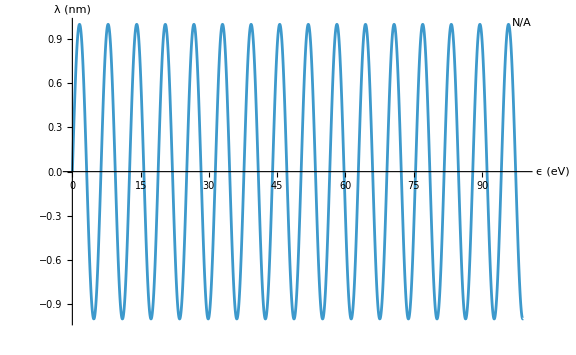

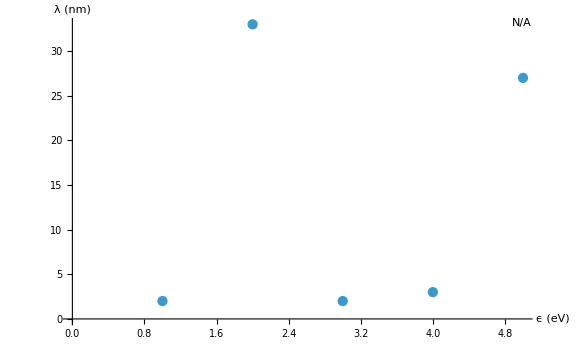

---------------- Context Diagnostics ----------------

$Context        : rich`

$ContextPath    :

rich`

myNotebookInit`

base`

statDataAnal`

physicsGeneral`

inputDataForRICH`

System`

Your loaded packages (lowercase only):

rich`

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

rich`

rich`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

---------------- Context Diagnostics ----------------

$Context        : rich`

$ContextPath    :

rich`

myNotebookInit`

base`

statDataAnal`

physicsGeneral`

inputDataForRICH`

System`

Your loaded packages (lowercase only):

rich`

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

rich`

rich`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

---------------- Context Diagnostics ----------------

$Context        : rich`

$ContextPath    :

rich`

myNotebookInit`

base`

statDataAnal`

physicsGeneral`

inputDataForRICH`

System`

Your loaded packages (lowercase only):

rich`

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

rich`

rich`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

---------------- Context Diagnostics ----------------

$Context        : rich`

$ContextPath    :

rich`

myNotebookInit`

base`

statDataAnal`

physicsGeneral`

inputDataForRICH`

System`

Your loaded packages (lowercase only):

rich`

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

rich`

rich`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

==================================================================================================

***  Summary of all efficiencies used only internally  ***

==================================================================================================

eff0GeoAccFactorInterColumns                 | 0.
eff0GeoAccFactorInterEleCell                 | 0.
eff0GeoAccFactorInterPixel                   | 0.
eff0InSensorGeomAccInBB                      | 0.
eff0InSensorGeomAccInBBRaw                   | 0.

==================================================================================================

***  ---***--- Summary of all efficiencies ---***---  ***

==================================================================================================

effInGasRadAbsorption                        | 0.
effInMirror1IfNotWavLenDependentReflectivity | 0.
effInMirror2IfNotWavLenDependentReflectivity | 0.
effInQuartzPlateInterfaceReflectivity        | 0.
effInQuartzPlateAbsorption                   | 0.
effInLensesInterfaceReflectivity             | 0.
effInLensesAbsorption                        | 0.
effInSensorInterfaceReflectivity             | 0.
effInSensorGeomAcc                           | 0.
effInSensorCollectEff                        | 0.
effInSensorMultiplication                    | 0.
effInFrontEnd                                | 0.
effInDAQ                                     | 0.
effInReco                                    | 0.
effInAna                                     | 0.
effInAllTheOverallMarginFactor               | 0.

n  : 1.200000000

n-1 : 200.000000000*10^-6

==================================================================================================

==================================================================================================

calcRadiatorDataFlag==False - DO NOTHING

==================================================================================================

==================================================================================================

allTheDetectorResultsExportShowPrint

==================================================================================================

==================================================================================================

FINISHING INITIALIZATION

==================================================================================================

==================================================================================================

---------------- Context Diagnostics ----------------

$Context        : rich`

$ContextPath    :

rich`

myNotebookInit`

base`

statDataAnal`

physicsGeneral`

inputDataForRICH`

System`

Your loaded packages (lowercase only):

rich`

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

rich`

rich`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

(none)

------------------------------------------------------

new symbols: case
depFile
depOK
depSource
files
files$
files$7273
getOK
LoadRICHCase
LoadRICHFiles
LoadRICHProject
localStyleSheet
missing
missing$
missing$7274
nbDir
oldDirectory
oldDirectory$
oldDirectory$7274
parts
RICHProjectPath
src
src$
src$7274
t0
$RICHProjectComponents
$RICHProjectManagedLoad
$RICHProjectRoot
$RICHProjectStyleDefinitions

elapsed (s): 27.072

[loadMyFile] END  |  C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\src\LoadProject.wl

============================================================

Changed ContextPath to: {rich`,inputDataForRICH`,physicsGeneral`,statDataAnal`,base`,myNotebookInit`,OpticaDocumentation`,System`,Global`}

```mathematica
$RICHProjectCase="calculator-reboot";myNotebookInit`loadMyFile["LoadProject.wl",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"src"}]];
```

```mathematica
(*cellStylesScannerPalette*)
```

```mathematica
checkProtection[{$dirBackup,$dirSWRoot,$dirSW,$dirOut}];
setProtection[{$dirBackup,$dirSWRoot,$dirSW,$dirOut},False]
ClearAll[$dirBackup,$dirSWRoot,$dirSW,$dirOut]
$dirBackup="C:\\Users\\Ale\\My Drive\\Mathematica";
$dirSWRoot="D:\\Users\\Ale\\Mathematica";
$dirSW="";
$dirOut="C:\\TEMP\\";
setProtection[{$dirBackup,$dirSWRoot,$dirSW,$dirOut},True];
```

[setProtection] $dirBackup : Unprotected -> Unprotected (AlreadyUnprotected)

[setProtection] $dirSWRoot : Unprotected -> Unprotected (AlreadyUnprotected)

[setProtection] $dirSW : Unprotected -> Unprotected (AlreadyUnprotected)

[setProtection] $dirOut : Unprotected -> Unprotected (AlreadyUnprotected)

{<|Symbol→$dirBackup,Name→$dirBackup,Context→Global`,WasProtected→False,NowProtected→False,RequestedProtected→False,Action→AlreadyUnprotected|>,<|Symbol→$dirSWRoot,Name→$dirSWRoot,Context→Global`,WasProtected→False,NowProtected→False,RequestedProtected→False,Action→AlreadyUnprotected|>,<|Symbol→$dirSW,Name→$dirSW,Context→Global`,WasProtected→False,NowProtected→False,RequestedProtected→False,Action→AlreadyUnprotected|>,<|Symbol→$dirOut,Name→$dirOut,Context→Global`,WasProtected→False,NowProtected→False,RequestedProtected→False,Action→AlreadyUnprotected|>}

[setProtection] $dirBackup : Unprotected -> Protected (Protected)

[setProtection] $dirSWRoot : Unprotected -> Protected (Protected)

[setProtection] $dirSW : Unprotected -> Protected (Protected)

[setProtection] $dirOut : Unprotected -> Protected (Protected)

BASE OPTIONS

```mathematica
nb[]:=EvaluationNotebook[];
nbFileName:=NotebookFileName[EvaluationNotebook[]];
nbFileDirectory:=NotebookDirectory[EvaluationNotebook[]];
nbFileBaseName:=FileBaseName[EvaluationNotebook[]FileName];
printD[nb[]];
printD[nbFileName];
printD[nbFileDirectory];
printD[nbFileBaseName ];
```

nb[] = cikzh_shm31FrontEndObject[LinkObject["cikzh_shm", 3, 1]]31 ------- C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nbC:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nb

nbFileName = C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nb

nbFileDirectory = C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\

nbFileBaseName = FileBaseName[FileName cikzh_shm31FrontEndObject[LinkObject["cikzh_shm", 3, 1]]31 ------- C:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nbC:\Users\Ale\OneDrive - unige.it\Documenti\WolframMMAProjectRICH-Git-new\notebooks\calculator-reboot.nb]

```mathematica
$HistoryLength=100;
SetOptions[EvaluationNotebook[],Background->LightGreen];
SetOptions[EvaluationNotebook[],Magnification->3/4];
SetOptions[EvaluationNotebook[],WindowMargins->{{0,Automatic},{Automatic,0}}];
SetOptions[EvaluationNotebook[],WindowSize->{Scaled[3/4],Scaled[1.0]}];
SetOptions[EvaluationNotebook[],WindowTitle->StringJoin[" ------- ",nbFileName]];
SetOptions[EvaluationNotebook[],StyleDefinitions->FileNameJoin[{NotebookDirectory[],"myStyle.nb"}]];
```

DETECT AND LOG SOME PROPERTIES OF THIS NOTEBOOK

```mathematica
(* output/print cells *)
If[Length@Cells[CellStyle->"Output"]>0,Echo@Cells[CellStyle->"Output"];Print[      "Length@Cells[CellStyle->Output]  ",       Length@Cells[CellStyle->"Output"]      ]];
If[Length@Cells[CellStyle->"Print"]>0,Echo@Cells[CellStyle->"Print"];Print[     "Length@Cells[CellStyle->Print]  ",           Length@Cells[CellStyle->"Print"]               ]];
(**)
```

{4112141121Output}

Length@Cells[CellStyle->Output]  1

{2755327553Print,2756927569Print,2758527585Print,2760127601Print,2761727617Print,2763327633Print,2764927649Print,2766527665Print,2768127681Print,2769727697Print,2771327713Print,2772927729Print,2774527745Print,2776127761Print,2777727777Print,2779327793Print,2780927809Print,2782527825Print,2784127841Print,2785727857Print,2787327873Print,2788927889Print,2790527905Print,2792127921Print,2793727937Print,2795327953Print,2796927969Print,2798527985Print,2800128001Print,2801728017Print,2804928049Print,2808128081Print,2809728097Print,2814528145Print,2817728177Print,2819328193Print,2820928209Print,2822528225Print,2824128241Print,2825728257Print,2827328273Print,2828928289Print,2830528305Print,2832128321Print,2833728337Print,2835328353Print,2836928369Print,2838528385Print,2840128401Print,2841728417Print,2843328433Print,2844928449Print,2846528465Print,2848128481Print,2849728497Print,2851328513Print,2852928529Print,2854528545Print,2856128561Print,2857728577Print,2859328593Print,2860928609Print,2862528625Print,2864128641Print,2865728657Print,2867328673Print,2868928689Print,2870528705Print,2872128721Print,2873728737Print,2875328753Print,2876928769Print,2878528785Print,2880128801Print,2881728817Print,2883328833Print,2884928849Print,2886528865Print,2888128881Print,2889728897Print,2891328913Print,2892928929Print,2894528945Print,2896128961Print,2897728977Print,2899328993Print,2900929009Print,2902529025Print,2904129041Print,2905729057Print,2907329073Print,2908929089Print,2910529105Print,2912129121Print,2913729137Print,2915329153Print,2916929169Print,2918529185Print,2920129201Print,2921729217Print,2923329233Print,2924929249Print,2926529265Print,2928129281Print,2929729297Print,2931329313Print,2932929329Print,2934529345Print,2936129361Print,2937729377Print,2939329393Print,2940929409Print,2942529425Print,2944129441Print,2945729457Print,2947329473Print,2948929489Print,2950529505Print,2952129521Print,2953729537Print,2955329553Print,2956929569Print,2958529585Print,2960129601Print,2961729617Print,2963329633Print,2964929649Print,2966529665Print,2968129681Print,2969729697Print,2971329713Print,2972929729Print,2974529745Print,2976129761Print,2977729777Print,2979329793Print,2980929809Print,2982529825Print,2984129841Print,2985729857Print,2987329873Print,2988929889Print,2990529905Print,2992129921Print,2993729937Print,2995329953Print,2996929969Print,2998529985Print,3000130001Print,3001730017Print,3003330033Print,3004930049Print,3006530065Print,3008130081Print,3009730097Print,3011330113Print,3012930129Print,3014530145Print,3016130161Print,3017730177Print,3019330193Print,3020930209Print,3022530225Print,3024130241Print,3025730257Print,3027330273Print,3028930289Print,3030530305Print,3032130321Print,3033730337Print,3035330353Print,3036930369Print,3038530385Print,3040130401Print,3041730417Print,3043330433Print,3044930449Print,3046530465Print,3048130481Print,3049730497Print,3051330513Print,3052930529Print,3054530545Print,3056130561Print,3057730577Print,3059330593Print,3060930609Print,3062530625Print,3064130641Print,3065730657Print,3067330673Print,3068930689Print,3070530705Print,3072130721Print,3073730737Print,3075330753Print,3076930769Print,3078530785Print,3080130801Print,3081730817Print,3083330833Print,3084930849Print,3086530865Print,3100931009Print,3102531025Print,3104131041Print,3105731057Print,3107331073Print,3108931089Print,3110531105Print,3112131121Print,3113731137Print,3115331153Print,3116931169Print,3118531185Print,3120131201Print,3121731217Print,3123331233Print,3124931249Print,3126531265Print,3128131281Print,3129731297Print,3131331313Print,3134531345Print,3136131361Print,3137731377Print,3139331393Print,3140931409Print,3142531425Print,3144131441Print,3145731457Print,3147331473Print,3148931489Print,3150531505Print,3152131521Print,3153731537Print,3155331553Print,3156931569Print,3158531585Print,3160131601Print,3161731617Print,3163331633Print,3164931649Print,3166531665Print,3168131681Print,3169731697Print,3171331713Print,3172931729Print,3174531745Print,3176131761Print,3177731777Print,3179331793Print,3180931809Print,3182531825Print,3184131841Print,3185731857Print,3187331873Print,3188931889Print,3190531905Print,3192131921Print,3193731937Print,3195331953Print,3196931969Print,3198531985Print,3200132001Print,3201732017Print,3203332033Print,3204932049Print,3206532065Print,3208132081Print,3209732097Print,3211332113Print,3212932129Print,3214532145Print,3216132161Print,3217732177Print,3219332193Print,3220932209Print,3222532225Print,3224132241Print,3225732257Print,3227332273Print,3228932289Print,3230532305Print,3232132321Print,3233732337Print,3235332353Print,3236932369Print,3238532385Print,3240132401Print,3241732417Print,3243332433Print,3244932449Print,3246532465Print,3248132481Print,3249732497Print,3251332513Print,3252932529Print,3254532545Print,3256132561Print,3257732577Print,3259332593Print,3260932609Print,3262532625Print,3264132641Print,3265732657Print,3267332673Print,3268932689Print,3270532705Print,3272132721Print,3273732737Print,3275332753Print,3276932769Print,3278532785Print,3280132801Print,3281732817Print,3283332833Print,3284932849Print,3286532865Print,3288132881Print,3289732897Print,3291332913Print,3292932929Print,3294532945Print,3296132961Print,3297732977Print,3299332993Print,3300933009Print,3302533025Print,3304133041Print,3305733057Print,3307333073Print,3308933089Print,3310533105Print,3312133121Print,3313733137Print,3315333153Print,3316933169Print,3318533185Print,3320133201Print,3321733217Print,3323333233Print,3324933249Print,3326533265Print,3328133281Print,3329733297Print,3331333313Print,3332933329Print,3334533345Print,3336133361Print,3337733377Print,3339333393Print,3340933409Print,3342533425Print,3344133441Print,3345733457Print,3347333473Print,3348933489Print,3350533505Print,3352133521Print,3353733537Print,3355333553Print,3356933569Print,3358533585Print,3360133601Print,3361733617Print,3363333633Print,3364933649Print,3366533665Print,3368133681Print,3369733697Print,3371333713Print,3372933729Print,3374533745Print,3376133761Print,3377733777Print,3379333793Print,3380933809Print,3382533825Print,3384133841Print,3385733857Print,3387333873Print,3388933889Print,3390533905Print,3392133921Print,3393733937Print,3395333953Print,3396933969Print,3398533985Print,3400134001Print,3401734017Print,3403334033Print,3404934049Print,3406534065Print,3408134081Print,3409734097Print,3411334113Print,3412934129Print,3414534145Print,3416134161Print,3417734177Print,3419334193Print,3420934209Print,3422534225Print,3424134241Print,3425734257Print,3427334273Print,3428934289Print,3430534305Print,3432134321Print,3433734337Print,3435334353Print,3436934369Print,3438534385Print,3440134401Print,3441734417Print,3443334433Print,3444934449Print,3446534465Print,3448134481Print,3449734497Print,3451334513Print,3452934529Print,3454534545Print,3456134561Print,3457734577Print,3459334593Print,3460934609Print,3462534625Print,3464134641Print,3465734657Print,3467334673Print,3468934689Print,3470534705Print,3472134721Print,3473734737Print,3475334753Print,3476934769Print,3478534785Print,3480134801Print,3481734817Print,3483334833Print,3484934849Print,3486534865Print,3488134881Print,3489734897Print,3491334913Print,3492934929Print,3494534945Print,3496134961Print,3497734977Print,3499334993Print,3500935009Print,3502535025Print,3504135041Print,3505735057Print,3507335073Print,3508935089Print,3510535105Print,3512135121Print,3513735137Print,3515335153Print,3516935169Print,3518535185Print,3520135201Print,3521735217Print,3523335233Print,3524935249Print,3526535265Print,3528135281Print,3529735297Print,3531335313Print,3532935329Print,3534535345Print,3536135361Print,3537735377Print,3539335393Print,3540935409Print,3542535425Print,3544135441Print,3545735457Print,3547335473Print,3548935489Print,3550535505Print,3552135521Print,3553735537Print,3555335553Print,3556935569Print,3558535585Print,3560135601Print,3561735617Print,3563335633Print,3564935649Print,3566535665Print,3568135681Print,3569735697Print,3571335713Print,3572935729Print,3574535745Print,3576135761Print,3577735777Print,3579335793Print,3580935809Print,3582535825Print,3584135841Print,3585735857Print,3587335873Print,3588935889Print,3590535905Print,3592135921Print,3593735937Print,3595335953Print,3596935969Print,3598535985Print,3600136001Print,3601736017Print,3603336033Print,3604936049Print,3606536065Print,3608136081Print,3609736097Print,3611336113Print,3612936129Print,3614536145Print,3616136161Print,3617736177Print,3619336193Print,3620936209Print,3622536225Print,3624136241Print,3625736257Print,3627336273Print,3628936289Print,3630536305Print,3632136321Print,3633736337Print,3635336353Print,3636936369Print,3638536385Print,3640136401Print,3641736417Print,3643336433Print,3644936449Print,3646536465Print,3648136481Print,3649736497Print,3651336513Print,3652936529Print,3654536545Print,3656136561Print,3657736577Print,3659336593Print,3660936609Print,3662536625Print,3664136641Print,3665736657Print,3667336673Print,3668936689Print,3670536705Print,3672136721Print,3673736737Print,3675336753Print,3676936769Print,3678536785Print,3680136801Print,3681736817Print,3683336833Print,3712137121Print,3744137441Print,3745737457Print,3747337473Print,3748937489Print,3750537505Print,3752137521Print,3753737537Print,3755337553Print,3756937569Print,3758537585Print,3760137601Print,3761737617Print,3763337633Print,3764937649Print,3766537665Print,3768137681Print,3769737697Print,3771337713Print,3772937729Print,3774537745Print,3776137761Print,3777737777Print,3779337793Print,3780937809Print,3782537825Print,3784137841Print,3785737857Print,3787337873Print,3788937889Print,3790537905Print,3792137921Print,3793737937Print,3795337953Print,3796937969Print,3798537985Print,3800138001Print,3801738017Print,3803338033Print,3804938049Print,3806538065Print,3808138081Print,3809738097Print,3811338113Print,3812938129Print,3814538145Print,3816138161Print,3817738177Print,3819338193Print,3820938209Print,3822538225Print,3824138241Print,3825738257Print,3827338273Print,3828938289Print,3830538305Print,3832138321Print,3833738337Print,3835338353Print,3836938369Print,3838538385Print,3840138401Print,3841738417Print,3843338433Print,3844938449Print,3846538465Print,3848138481Print,3849738497Print,3851338513Print,3852938529Print,3854538545Print,3856138561Print,3857738577Print,3859338593Print,3860938609Print,3862538625Print,3864138641Print,3865738657Print,3867338673Print,3868938689Print,3870538705Print,3872138721Print,3873738737Print,3875338753Print,3876938769Print,3878538785Print,3880138801Print,3881738817Print,3883338833Print,3884938849Print,3886538865Print,3888138881Print,3889738897Print,3891338913Print,3892938929Print,3894538945Print,3896138961Print,3897738977Print,3899338993Print,3900939009Print,3902539025Print,3904139041Print,3905739057Print,3907339073Print,3908939089Print,3910539105Print,3912139121Print,3913739137Print,3915339153Print,3916939169Print,3918539185Print,3920139201Print,3921739217Print,3923339233Print,3924939249Print,3926539265Print,3928139281Print,3929739297Print,3931339313Print,3932939329Print,3934539345Print,3936139361Print,3937739377Print,3939339393Print,3940939409Print,3942539425Print,3944139441Print,3945739457Print,3947339473Print,3948939489Print,3950539505Print,3952139521Print,3953739537Print,3955339553Print,3956939569Print,3958539585Print,3960139601Print,3961739617Print,3963339633Print,3964939649Print,3966539665Print,3968139681Print,3969739697Print,3971339713Print,3972939729Print,3974539745Print,3976139761Print,3977739777Print,3979339793Print,3980939809Print,3982539825Print,3984139841Print,3985739857Print,3987339873Print,3988939889Print,3990539905Print,3992139921Print,3993739937Print,3995339953Print,3996939969Print,3998539985Print,4000140001Print,4001740017Print,4003340033Print,4004940049Print,4006540065Print,4008140081Print,4009740097Print,4011340113Print,4012940129Print,4014540145Print,4016140161Print,4017740177Print,4019340193Print,4020940209Print,4022540225Print,4024140241Print,4025740257Print,4027340273Print,4028940289Print,4030540305Print,4032140321Print,4033740337Print,4035340353Print,4036940369Print,4038540385Print,4040140401Print,4041740417Print,4043340433Print,4044940449Print,4046540465Print,4048140481Print,4049740497Print,4051340513Print,4052940529Print,4054540545Print,4056140561Print,4057740577Print,4059340593Print,4060940609Print,4062540625Print,4064140641Print,4065740657Print,4067340673Print,4068940689Print,4070540705Print,4072140721Print,4073740737Print,4075340753Print,4076940769Print,4078540785Print,4080140801Print,4081740817Print,4083340833Print,4084940849Print,4086540865Print,4088140881Print,4089740897Print,4091340913Print,4092940929Print,4094540945Print,4096140961Print,4097740977Print,4099340993Print,4100941009Print,4102541025Print,4104141041Print,4105741057Print,4107341073Print,4108941089Print,4110541105Print,4113741137Print,4115341153Print,4116941169Print,4118541185Print,4120141201Print,4123341233Print,4124941249Print,4126541265Print,4134541345Print}

Length@Cells[CellStyle->Print]  807

```mathematica
(* Cells type inventory for this notebook *)
(**)
Print["Length@Cells[CellStyle -> Title                ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Title"]];
Print["Length@Cells[CellStyle -> Subtitle             ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Subtitle"]];
Print["Length@Cells[CellStyle -> Subsubtitle          ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Subsubtitle"]];
Print["Length@Cells[CellStyle -> Section              ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Section"]];
Print["Length@Cells[CellStyle -> Subsection           ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Subsection"]];
Print["Length@Cells[CellStyle -> Subsubsection        ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Subsubsection"]];
Print["Length@Cells[CellStyle -> Input                ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Input"]];
Print["Length@Cells[CellStyle -> Text                 ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Text"]];
Print["Length@Cells[CellStyle -> ExampleText          ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"ExampleText"]];
Print["Length@Cells[CellStyle -> Code                 ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Code"]];
Print["Length@Cells[CellStyle -> Output                           ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Output"]];
Print["Length@Cells[CellStyle -> Print                            ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Print"]];
Print["Length@Cells[CellStyle -> Message                          ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"Message"]];
Print["Length@Cells[CellStyle -> MSG                              ",PaddedForm[#,{3,4}]&@Length@Cells[CellStyle->"MSG"]];
Print["                       Total Number of Cells ->                                    ",PaddedForm[#,{3,4}]&@Length@Cells[]];
```

Length@Cells[CellStyle -> Title                   4

Length@Cells[CellStyle -> Subtitle               34

Length@Cells[CellStyle -> Subsubtitle            77

Length@Cells[CellStyle -> Section                56

Length@Cells[CellStyle -> Subsection             32

Length@Cells[CellStyle -> Subsubsection          14

Length@Cells[CellStyle -> Input                 782

Length@Cells[CellStyle -> Text                   24

Length@Cells[CellStyle -> ExampleText             0

Length@Cells[CellStyle -> Code                    0

Length@Cells[CellStyle -> Output                              1

Length@Cells[CellStyle -> Print                             819

Length@Cells[CellStyle -> Message                             0

Length@Cells[CellStyle -> MSG                                 0

Total Number of Cells ->                                     1848

END

```mathematica
Print["*==================================================================================================*"];
Print["*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*"];
Print["***--- calculator ---***"];
Print["*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*"];
Print["*==================================================================================================*"];
```

*==================================================================================================*

*||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||*

***--- calculator ---***

*VVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVVV*

*==================================================================================================*

## THIS NOTEBOOK INITIALIZATION

INIT

```mathematica
Print[" ************************************************************************************************* "];
Print[" Start running  ",theTimeStamp=timeStamp];
Print[" t0=AbsoluteTime[]   ",t0=AbsoluteTime[]];
Print[" ************************************************************************************************* "];
thisTimeStamp:=theTimeStamp<>"--"<>ToString[Round[1000000*(1000000+(AbsoluteTime[]-t0))]]
```

*************************************************************************************************

Start running  -D260808T192324

t0=AbsoluteTime[]   3.9952058046374808×10^9

*************************************************************************************************

MY LIBRARIES

```mathematica
(**************************************************************************************************)
(* my personal stuff *)
(**************************************************************************************************)
```

```mathematica
(**************************************************************************************************)
(* rich *)
(**************************************************************************************************)
(*(*Once[*)myNotebookInit`loadMyFile["RICH.wl",RICHProjectPath["src"]](*,"KernelSession"];*)*)
```

stuff specific to this notebook

## functions

## mathematica options

```mathematica
SetOptions[{LogPlot,Plot,Graphics,ListPlot,Histogram},Ticks->{Automatic,Automatic}];
SetOptions[{LogPlot,Plot,Graphics,ListPlot,Histogram},AxesOrigin->{0,0}];
SetOptions[{LogPlot,Plot,(*Graphics,*)ListPlot,Histogram},Frame->True];
SetOptions[{Graphics},AspectRatio->Automatic];
SetOptions[TableForm,TableAlignments->Center](*works?????*);
```

loading other packages

## authorTools

```mathematica
(*<<AuthorTools`OpenAuthorTool[]*)
```

## END SETUP

END

```mathematica
(**)
bigBanner[" FINISHING SETUP "]
(**)
endEvalPrintOut[]
(**)
```

==================================================================================================

==================================================================================================

FINISHING SETUP

==================================================================================================

==================================================================================================

FINISHING SETUP

==================================================================================================

==================================================================================================

endEvalPrintOut

==================================================================================================

==================================================================================================

timeStamp            ===>>>   -D260808T192324

--------------------------------------------------------------------------------------------------

Cells[MSG,Message}]      ===>>> 
{}

--------------------------------------------------------------------------------------------------

$Context                 ===>>>  Global`

--------------------------------------------------------------------------------------------------

$ContextPath             ===>>>  rich`
inputDataForRICH`
physicsGeneral`
statDataAnal`
base`
myNotebookInit`
OpticaDocumentation`
System`
Global`

--------------------------------------------------------------------------------------------------

checkNewCreatedSymbols   ===>>>  {byType,case,ClearLoadLog,ctx,depFile,depOK,depSource,dir,ds,expr,file,files,files$,files$7273,getOK,goBack,isSystemPath,LoadRICHCase,LoadRICHFiles,LoadRICHProject,LoadSavedLog,localStyleSheet,logLoad,missing,missing$,missing$7274,navHistory,nbDir,oldDirectory,oldDirectory$,oldDirectory$7274,opts,out,out$,parts,path,pkg,pushHistory,RICHProjectPath,rows,s,SaveLoadLog,src,src$,src$7274,SummarizeLoads,t0,target,theTimeStamp,thisTimeStamp,type,$dirBackup,$dirOut,$dirSW,$dirSWRoot,$LoadLog,$RICHProjectCase,$RICHProjectComponents,$RICHProjectManagedLoad,$RICHProjectRoot,$RICHProjectStyleDefinitions,$SystemPathPatterns,$trackedContext,$trackedPath,$Tracking}

--------------------------------------------------------------------------------------------------

No loads recorded.

# ---... CALCULATOR

## >>> INIT FAKE PACKAGE

```mathematica
BeginPackage["calculator`",{"myNotebookInit`","base`","statDataAnal`","rich`"}]
(**)
Print[" loading calculator "]
(**)
Begin["`Private`"] (* Begin Private Context *) 
(**)
showContextInfo[]
(**)
versionTAG="v.15-03-2026";
(**)
End[] (* End Private Context *)
(**)
showContextInfo[]
(**)
Print@Cells[CellStyle->{"MSG","Message"}]
(**)
EndPackage[]
```

Changed Context to: calculator`

Changed ContextPath to: {calculator`,myNotebookInit`,base`,statDataAnal`,rich`,System`}

calculator`

loading calculator

Changed Context to: calculator`Private`

calculator`Private`

---------------- Context Diagnostics ----------------

$Context        : calculator`Private`

$ContextPath    :

calculator`

myNotebookInit`

base`

statDataAnal`

rich`

System`

Your loaded packages (lowercase only):

calculator`

rich`

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

rich`

rich`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

inputDataForRICH`

physicsGeneral`

------------------------------------------------------

<|$Context→calculator`Private`,$ContextPath→{calculator`,myNotebookInit`,base`,statDataAnal`,rich`,System`},MyPackages→{calculator`,rich`,inputDataForRICH`,physicsGeneral`,statDataAnal`,base`,myNotebookInit`},RecentContexts→{base`,base`Private`,com`wolfram`alpha`parser`FileManager`,com`wolfram`alpha`parser`math`expr`FullContext`,com`wolfram`alpha`parser`math`expr`FullSymbol`,com`wolfram`alpha`parser`templateparser`ParserGrammar`,com`wolfram`alpha`parser`tokenizer`Tokenizer`,com`wolfram`interpreter`ParseTelephoneNumber`,inputDataForRICH`,inputDataForRICH`Private`,javax`sound`midi`MidiSystem`,javax`sound`midi`ShortMessage`,physicsGeneral`,physicsGeneral`Private`,rich`,rich`Private`,statDataAnal`,statDataAnal`Private`,t`},UnreachableLoadedPackages→{inputDataForRICH`,physicsGeneral`}|>

Changed Context to: calculator`

calculator`Private`

---------------- Context Diagnostics ----------------

$Context        : calculator`

$ContextPath    :

calculator`

myNotebookInit`

base`

statDataAnal`

rich`

System`

Your loaded packages (lowercase only):

calculator`

rich`

inputDataForRICH`

physicsGeneral`

statDataAnal`

base`

myNotebookInit`

Recently created lowercase contexts:

base`

base`Private`

com`wolfram`alpha`parser`FileManager`

com`wolfram`alpha`parser`math`expr`FullContext`

com`wolfram`alpha`parser`math`expr`FullSymbol`

com`wolfram`alpha`parser`templateparser`ParserGrammar`

com`wolfram`alpha`parser`tokenizer`Tokenizer`

com`wolfram`interpreter`ParseTelephoneNumber`

inputDataForRICH`

inputDataForRICH`Private`

javax`sound`midi`MidiSystem`

javax`sound`midi`ShortMessage`

physicsGeneral`

physicsGeneral`Private`

rich`

rich`Private`

statDataAnal`

statDataAnal`Private`

t`

Loaded lowercase packages NOT on $ContextPath:

inputDataForRICH`

physicsGeneral`

------------------------------------------------------

<|$Context→calculator`,$ContextPath→{calculator`,myNotebookInit`,base`,statDataAnal`,rich`,System`},MyPackages→{calculator`,rich`,inputDataForRICH`,physicsGeneral`,statDataAnal`,base`,myNotebookInit`},RecentContexts→{base`,base`Private`,com`wolfram`alpha`parser`FileManager`,com`wolfram`alpha`parser`math`expr`FullContext`,com`wolfram`alpha`parser`math`expr`FullSymbol`,com`wolfram`alpha`parser`templateparser`ParserGrammar`,com`wolfram`alpha`parser`tokenizer`Tokenizer`,com`wolfram`interpreter`ParseTelephoneNumber`,inputDataForRICH`,inputDataForRICH`Private`,javax`sound`midi`MidiSystem`,javax`sound`midi`ShortMessage`,physicsGeneral`,physicsGeneral`Private`,rich`,rich`Private`,statDataAnal`,statDataAnal`Private`,t`},UnreachableLoadedPackages→{inputDataForRICH`,physicsGeneral`}|>

{}

Changed Context to: Global`

Changed ContextPath to: {calculator`,rich`,inputDataForRICH`,physicsGeneral`,statDataAnal`,base`,myNotebookInit`,OpticaDocumentation`,System`,Global`}

## <<< END FAKE PACKAGE

## DEFINITIONS FOR THIS NOTEBOOK

## symbolics for variables to use in this notebook

```mathematica
checkNewCreatedSymbols[]
Off[Notation`Symbolize::bsymbexs];
(**)
Notation`AutoLoadNotationPalette=False;(*BEFORE LOADING Notations!*)
(*Notation`AutoLoadNotationPalette=True;*)(*BEFORE LOADING Notations!*)
Needs["Notation`"];
(**)
Notation`ClearNotations[](*clears all notations,symbolizations,and infix notations*)
(**)
Notation`Symbolize[Subscript[n, s]]
Notation`Symbolize[Subscript[n, σ]]
Notation`Symbolize[Subscript[f, σ]]
Notation`Symbolize[Subscript[λ, 1]]
Notation`Symbolize[Subscript[λ, 2]]
Notation`Symbolize[Subscript[δθ, R]]
Notation`Symbolize[Subscript[σ, R]^∞]
Notation`Symbolize[Subscript[ℱ, λ]]
Notation`Symbolize[Subscript[𝒟, λ]]
Notation`Symbolize[Subscript[ℱ, θ]]
Notation`Symbolize[Subscript[𝒟, θ]]
(**)
FullForm[Subscript[n, s]]
FullForm[Subscript[n, σ]]
FullForm[Subscript[f, σ]]
FullForm[Subscript[λ, 1]]
FullForm[Subscript[λ, 2]]
FullForm[Subscript[δθ, R]]
FullForm[Subscript[σ, R]^∞]
FullForm[Subscript[ℱ, λ]]
FullForm[Subscript[𝒟, λ]]
FullForm[Subscript[ℱ, θ]]
FullForm[Subscript[𝒟, θ]]
(**)
FullForm[Subscript[n, s]]
FullForm[Subscript[n, σ]]
FullForm[Subscript[f, σ]]
FullForm[Subscript[λ, 1]]
FullForm[Subscript[λ, 2]]
FullForm[Subscript[δθ, R]]
FullForm[Subscript[σ, R]^∞]
FullForm[Subscript[ℱ, λ]]
FullForm[Subscript[𝒟, λ]]
FullForm[Subscript[ℱ, θ]]
FullForm[Subscript[𝒟, θ]]
(*=============================================================================*)
(* some checks on new symbols *)
(*=============================================================================*)
Print[Subscript[δθ, R]/.R->1];(*/.X->...: X becomes a new symbol*)
Print[Subscript[δθ, R]/.θ->1];(*/.X->...: X becomes a new symbol*)
Print[Subscript[n, s]/.s->1];(*/.X->...: X becomes a new symbol*)
Print[Subscript[n, σ]/.σ->11];(*/.X->...: X becomes a new symbol*)
Print[Subscript[λ, 1]/.λ->x1];(*/.X->...: X becomes a new symbol*)
Print[Subscript[λ, 2]/.λ->x2];(*/.X->...: X becomes a new symbol*)
Print[Subscript[λ, 1]/.Subscript[λ, 1]->x1];(*/.X->...: X becomes a new symbol*)
Print[Subscript[λ, 2]/.Subscript[λ, 2]->x2];(*/.X->...: X becomes a new symbol*)
Print[Subscript[𝒟, λ]/.λ->1];(*/.X->...: X becomes a new symbol*)
(**)
On[Notation`Symbolize::bsymbexs];
checkNewCreatedSymbols[]
```

{}

Changed ContextPath to: {Notation`,calculator`,rich`,inputDataForRICH`,physicsGeneral`,statDataAnal`,base`,myNotebookInit`,OpticaDocumentation`,System`,Global`}

ParsedBoxWrapper[SubscriptBox["n","s"]]

ParsedBoxWrapper[SubscriptBox["n","\[Sigma]"]]

ParsedBoxWrapper[SubscriptBox["f","\[Sigma]"]]

ParsedBoxWrapper[SubscriptBox["\[Lambda]","1"]]

ParsedBoxWrapper[SubscriptBox["\[Lambda]","2"]]

ParsedBoxWrapper[SubscriptBox["\[Delta]\[Theta]","R"]]

ParsedBoxWrapper[SubsuperscriptBox["\[Sigma]","R","\[Infinity]"]]

ParsedBoxWrapper[SubscriptBox["\[ScriptCapitalF]","\[Lambda]"]]

ParsedBoxWrapper[SubscriptBox["\[ScriptCapitalD]","\[Lambda]"]]

ParsedBoxWrapper[SubscriptBox["\[ScriptCapitalF]","\[Theta]"]]

ParsedBoxWrapper[SubscriptBox["\[ScriptCapitalD]","\[Theta]"]]

n\[UnderBracket]Subscript\[UnderBracket]s

n\[UnderBracket]Subscript\[UnderBracket]\[Sigma]

f\[UnderBracket]Subscript\[UnderBracket]\[Sigma]

\[Lambda]\[UnderBracket]Subscript\[UnderBracket]1

\[Lambda]\[UnderBracket]Subscript\[UnderBracket]2

\[Delta]\[Theta]\[UnderBracket]Subscript\[UnderBracket]R

\[Sigma]\[UnderBracket]Subsuperscript\[UnderBracket]R\[UnderBracket]and\[UnderBracket]Infinity

\[ScriptCapitalF]\[UnderBracket]Subscript\[UnderBracket]\[Lambda]

\[ScriptCapitalD]\[UnderBracket]Subscript\[UnderBracket]\[Lambda]

\[ScriptCapitalF]\[UnderBracket]Subscript\[UnderBracket]\[Theta]

\[ScriptCapitalD]\[UnderBracket]Subscript\[UnderBracket]\[Theta]

δθ_R

δθ_R

n_s

n_σ

λ_1

λ_2

x1

x2

𝒟_λ

{f⎵Subscript⎵σ,n⎵Subscript⎵s,n⎵Subscript⎵σ,R,𝒟⎵Subscript⎵θ,𝒟⎵Subscript⎵λ,ℱ⎵Subscript⎵θ,ℱ⎵Subscript⎵λ,δθ⎵Subscript⎵R,θ,λ⎵Subscript⎵1,λ⎵Subscript⎵2,σ,σ⎵Subsuperscript⎵R⎵and⎵Infinity}

## MISCELLANEA DEFINITIONS

```mathematica
debugPrintD[input__]:=Module[{},If[debugPrintEnabledFlag,printD[input]]];
```

```mathematica
fullRationalize=Rationalize[#,0]&;
```

```mathematica
(*ClearAll[thisDataPlotInset];*)
printD@tagDataPlot;
printD@thisDataPlotInset;
(**)
```

tagDataPlot =

thisDataPlotInset = thisDataPlotInset

## OPTIONS FOR THIS NOTEBOOK

## RICH SPECIFIC FOR THIS NOTEBOOK

SETUP for RICH

```mathematica
(* λMinRef and λMaxRef can only be changed HERE *)
Unprotect[λMinRef,λMaxRef];
λMinRef=200;(*OK FOR MAPMT22*)
(*λMinRef:=270; FOR SIPMFBK/MPPCHPK // but are zero below 270-280 so you can use 200 anyway *)
λMaxRef=700;
Protect[λMinRef,λMaxRef];
bigBanner[" SETTING WAVELENGTH RANGE (λMinRef,λMaxRef) : ","(",λMinRef,"-",λMaxRef,")"," nm"];
(**)
Print[Column[Sort[searchForGivenNames["*pde*"]]]];
(**)
```

pdeEffEnergyData
pdeEffEnergyFunction
pdeEffEnergyFunction$
pdeEffWavLenData
pdeEffWavLenFunction
pdeEffWavLenFunction$
pdeLAPPDTMWavLen
pdeMAPMT22WavLen
pdeMPPCHPKWavLen
pdeSIPMFBKWavLen

CALC/PREPARE data needed by this notebook

## sensors

```mathematica
Names["*EnergyData*"]//TableForm
Names["*label*"]//TableForm
Names["*nRefr*"]//TableForm
Names["*theRef*"]//TableForm
Names["*refrI*"]//TableForm
```

LAPPDTMEnergyData
LAPPDTMEnergyDataNew
LAPPDTMEnergyDataSave
LAPPDTMEnergyDataToWavLen
LAPPDTMEnergyDataToWavLenInterpol
LAPPDTMEnergyDataToWavLenInterpolFix
LAPPDTMEnergyDataToWavNewTable
lensTransEnergyData
MAPMT22EnergyData
MAPMT22EnergyDataNew
MAPMT22EnergyDataSave
MAPMT22EnergyDataToWavLen
MAPMT22EnergyDataToWavLenInterpol
MAPMT22EnergyDataToWavLenInterpolFix
MAPMT22EnergyDataToWavNewTable
MAPMTOLD22EnergyData
MaPMTSBABSGlassEffEnergyData
MaPMTSBABSGlassEffEnergyDataRawSE
MaPMTSBABSGlassEffEnergyDataSE
MaPMTSBAUVGlassEffEnergyData
MaPMTSBAUVGlassEffEnergyDataRawSE
MaPMTSBAUVGlassEffEnergyDataSE
MPPCHPKEnergyData
MPPCHPKEnergyDataNew
MPPCHPKEnergyDataSave
MPPCHPKEnergyDataToWavLen
MPPCHPKEnergyDataToWavLenInterpol
MPPCHPKEnergyDataToWavLenInterpolFix
MPPCHPKEnergyDataToWavNewTable
pdeEffEnergyData
plotPdeEffEnergyData
plotPdeEffEnergyData$
R5900EnergyData
SIPMFBKEnergyData
SIPMFBKEnergyDataNew
SIPMFBKEnergyDataSave
SIPMFBKEnergyDataToWavLen
SIPMFBKEnergyDataToWavLenInterpol
SIPMFBKEnergyDataToWavLenInterpolFix
SIPMFBKEnergyDataToWavNewTable
tablePdeEffEnergyData
TB2021AEnergyData

labelEffVsEv
labelEffVsNm
labelEvVsNm
labelNmVsEv
UnlabeledTree

dispersionRefrIndexGrpWavLen
dispersionRefrIndexGrpWavLen$
dispersionRefrIndexPhsWavLen
dispersionRefrIndexPhsWavLen$
nRefrAergl
nRefrAerglDat
nRefrAir
nRefrC1F04
nRefrC1O02
nRefrC1O02All
nRefrC2F06
nRefrC4F10
nRefrFQrtz
nRefrHe
nRefrHe0
nRefrNe

theRefrIndex
theRefrIndexAtLambdaMax
theRefrIndexAtLambdaMean
theRefrIndexAtLambdaMedian
theRefrIndexAtLambdaMin

refrIndex
refrIndexGrp
refrIndexPhs
refrIndex$

```mathematica
allSensorsPDEEnergyData={LAPPDTMEnergyData,MAPMT22EnergyData,MPPCHPKEnergyData,SIPMFBKEnergyData};
allSensorsPDEWavLenData={
Map[{λ[#[[1]]],#[[2]]}&,LAPPDTMEnergyData],
Map[{λ[#[[1]]],#[[2]]}&,MAPMT22EnergyData],
Map[{λ[#[[1]]],#[[2]]}&,MPPCHPKEnergyData],
Map[{λ[#[[1]]],#[[2]]}&,SIPMFBKEnergyData]
};
Interpolation/@allSensorsPDEEnergyData
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
legend=SwatchLegend[{Orange,Blue,Yellow,Green},{"LAPPDTMEnergyData","MAPMT22EnergyData","MPPCHPKEnergyData","SIPMFBKEnergyData"},LegendMarkers->Graphics[{Rectangle[]}],LegendLabel->"sensors",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
```

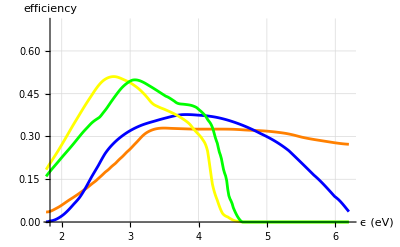

```mathematica
plot=Print[ListLinePlot[{Style[LAPPDTMEnergyData,Orange],Style[MAPMT22EnergyData,Blue],Style[MPPCHPKEnergyData,Yellow],Style[SIPMFBKEnergyData,Green]},
PlotRange->{{eneMin,eneMax},{0,0.7}},
PlotLegends->legend,
GridLines->Automatic,Epilog->{},AxesLabel->labelEffVsEv]];
exportGraphicsToPDF[plot,"allSensorsPDEEnergyData","","",False];
(**)
```

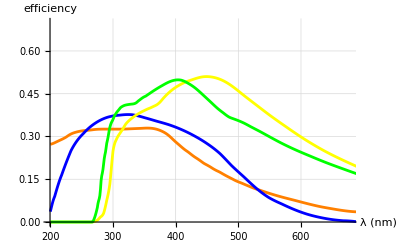

```mathematica
plot=Print[ListLinePlot[{Style[allSensorsPDEWavLenData[[1]],Orange],Style[allSensorsPDEWavLenData[[2]],Blue],Style[allSensorsPDEWavLenData[[3]],Yellow],Style[allSensorsPDEWavLenData[[4]],Green]},
PlotRange->{{λ[eneMin],λ[eneMax]},{0,0.7}},
PlotLegends->legend,
GridLines->Automatic,Epilog->{},AxesLabel->labelEffVsNm]];
exportGraphicsToPDF[plot,"allSensorsPDEWavLenData","","",False];
```

## all radiators info: to check/update (now only the standard LHCb/RICH rads)

```mathematica
(*fixed data calculated by calcAllRadiators*)
(**)
theWavLen1={200.0,200.0,200.0,200.0,200.0};
theWavLen2={700.0,700.0,700.0,700.0,700.0};
theWavLenMean={346.3,347.7,345.4,347.4,350.2};
theWavLenMedian={305.4,307.2,304.4,306.9,310.3};
nRefrAtTheWavLen1={1.0015657,1.0005187,1.0005132,1.5505055,1.0308707};
nRefrAtTheWavLenMedian={1.0014367,1.0004890,1.0004633,1.4859271,1.0304975};
nRefrAtTheWavLenMean={1.0014173,1.0004845,1.0004558,1.4773295,1.0304414};
nRefrAtTheWavLen2={1.0013682,1.0004729,1.0004373,1.4552925,1.0302885};
(**)
(*===================================================================================*)
(*DETECTOR SETUP // TO BE CHECKED LATER FOR SPECIFIC APPLICATIONS*)
(*===================================================================================*)
printD@theWavLen1;
printD@theWavLen2;
printD@theWavLenMean;
printD@theWavLenMedian;
printD@nRefrAtTheWavLen1;
printD@nRefrAtTheWavLen2;
printD@nRefrAtTheWavLenMean;
printD@nRefrAtTheWavLenMedian;
(**)
```

theWavLen1 = {200.,200.,200.,200.,200.}

theWavLen2 = {700.,700.,700.,700.,700.}

theWavLenMean = {346.3,347.7,345.4,347.4,350.2}

theWavLenMedian = {305.4,307.2,304.4,306.9,310.3}

nRefrAtTheWavLen1 = {1.00157,1.00052,1.00051,1.55051,1.03087}

nRefrAtTheWavLen2 = {1.00137,1.00047,1.00044,1.45529,1.03029}

nRefrAtTheWavLenMean = {1.00142,1.00048,1.00046,1.47733,1.03044}

nRefrAtTheWavLenMedian = {1.00144,1.00049,1.00046,1.48593,1.0305}

## momentum related things

momentumCherenkovThreshold[m,n] = m/(√(-1+n^2))

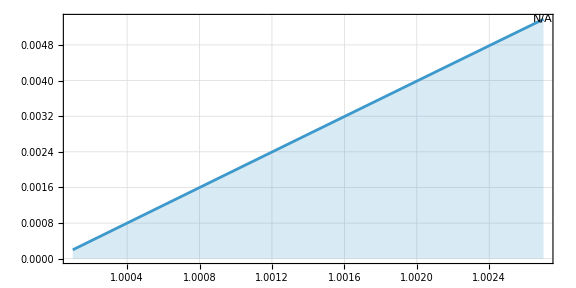

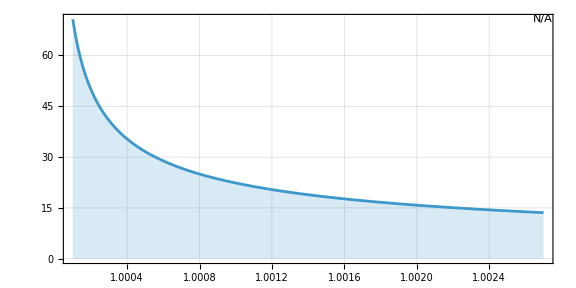

```mathematica
(* momentum thr and asymptotic number of photons *)
printD@momentumCherenkovThreshold[m,n];
Plot[{Sin[thetaChrTheMax[n]]^2},{n,1.0001,1.0027},PlotRange->All,PlotLegends->"Expressions",GridLines->Automatic]
Plot[{momentumCherenkovThreshold[m,n]/m},{n,1.0001,1.0027},PlotRange->All,PlotLegends->"Expressions",GridLines->Automatic]
```

## END CALCULATOR

END

```mathematica
(**)
bigBanner[" FINISHING CALCULATOR "]
(**)
endEvalPrintOut[]
(**)
```

==================================================================================================

==================================================================================================

FINISHING CALCULATOR

==================================================================================================

==================================================================================================

FINISHING CALCULATOR

==================================================================================================

==================================================================================================

endEvalPrintOut

==================================================================================================

==================================================================================================

timeStamp            ===>>>   -D260808T192328

--------------------------------------------------------------------------------------------------

Cells[MSG,Message}]      ===>>> 
{}

--------------------------------------------------------------------------------------------------

$Context                 ===>>>  Global`

--------------------------------------------------------------------------------------------------

$ContextPath             ===>>>  Notation`
calculator`
rich`
inputDataForRICH`
physicsGeneral`
statDataAnal`
base`
myNotebookInit`
OpticaDocumentation`
System`
Global`

--------------------------------------------------------------------------------------------------

checkNewCreatedSymbols   ===>>>  {allSensorsPDEEnergyData,allSensorsPDEWavLenData,fullRationalize,legend,nRefrAtTheWavLen1,nRefrAtTheWavLen2,nRefrAtTheWavLenMean,nRefrAtTheWavLenMedian,plot,theWavLen1,theWavLen2,theWavLenMean,theWavLenMedian}

--------------------------------------------------------------------------------------------------

No loads recorded.

# ---... CALCULATOR BODY

## SOME PRELIMINARY CALCULATIONS

## calculate RICH results

### INIT

```mathematica
(*ClearAll[refrIndex];*)
bigBanner["MAKE SURE TO RUN calcRICHYield LATER IF NEEDED"];
doAllRichCalcFlag=True;
numSim=1000;

(*ParallelMap["Kernel "<>ToString[$KernelID]<>" : "<>ToString[f[#]]&,{{1,1,1},{1,2,2},{1,3,3},{1,4,4}}]*)
(*
params1={"C1F04-0980-293",λMinRef,λMaxRef,2,"MAPMT22s",nominalLengthRich2,numSim,True};
params2={"C4F10-0980-293",λMinRef,λMaxRef,1,"MPPCHPK",nominalLengthRich1,numSim,True};
ParallelMap[Apply[calcRICHYield,#]&,{params1,params2}]
*)


(*(* TEST*)calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MAPMT22s",nominalLengthRich2,numSim,True];*)
(*(* TEST*)calcRICHYield["C4F10-0980-293",λMinRef,λMaxRef,1,"MPPCHPK",nominalLengthRich1,numSim,True];*)

(*Block[{Print},
res=calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MAPMT22s",nominalLengthRich2,numSim,True];
Echo[res]
]*)
```

### RICH-2022

calcRICHYield[rad_, tmpλ1_, tmpλ2_, whichRICH_ : 0, sensor_ : "ZERO", length_ : 0, numToGenerate_ : 10000, debug_ : True, thisNumOfQuantiles_ : 11] :=

```mathematica
allResults2022={};
(**)
doCalcAllRadiators2022:=Module[{res},
(* RuntimeTools`Profile[*)(*REQUIRES: Needs["Instrumentation`"] and DEBUG ON!!!*)
res=calcRICHYield["C4F10-0980-293",λMinRef,λMaxRef,1,"MAPMT22s",nominalLengthRich1,numSim,True];
(*];*)
AppendTo[allResults2022,res];
(**)
(* RuntimeTools`Profile[*)(*REQUIRES: Needs["Instrumentation`"] and DEBUG ON!!!*)
res=calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MAPMT22s",nominalLengthRich2,numSim,True];
(*];*)
AppendTo[allResults2022,res];
(**)
(* RuntimeTools`Profile[*)(*REQUIRES: Needs["Instrumentation`"] and DEBUG ON!!!*)
res=calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MAPMT22l",nominalLengthRich2,numSim,True];
(*];*)
AppendTo[allResults2022,res];
(**)
Return[]
];
(**)
If[doAllRichCalcFlag==True
,
doCalcAllRadiators2022
];
```

### RICH-Upg2

calcRICHYield[rad_, tmpλ1_, tmpλ2_, whichRICH_ : 0, sensor_ : "ZERO", length_ : 0, numToGenerate_ : 10000, debug_ : True, thisNumOfQuantiles_ : 11] :=

```mathematica
allResultsUpg2={};
(**)
doCalcAllRadiatorsUpg2:=Module[{res},
(**)
res=calcRICHYield["C4F10-0980-293",λMinRef,λMaxRef,1,"MAPMT22s",nominalLengthRich1,numSim,True];
AppendTo[allResultsUpg2,res];
(**)
res=calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MAPMT22s",nominalLengthRich2,numSim,True];
AppendTo[allResultsUpg2,res];
(**)
res=calcRICHYield["C4F10-0980-293",λMinRef,λMaxRef,1,"MPPCHPK",nominalLengthRich1,numSim,True];
AppendTo[allResultsUpg2,res];
(**)
res=calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MPPCHPK",nominalLengthRich2,numSim,True];
AppendTo[allResultsUpg2,res];
(**)
res=calcRICHYield["C4F10-0980-293",λMinRef,λMaxRef,1,"SIPMFBK",nominalLengthRich1,numSim,True];
AppendTo[allResultsUpg2,res];
(**)
res=calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"SIPMFBK",nominalLengthRich2,numSim,True];
AppendTo[allResultsUpg2,res];
(**)
(*res=calcRICHYield["C4F10-0980-293",λMinRef,λMaxRef,1,"LAPPDTM",nominalLengthRich1,numSim,True];
AppendTo[allResultsUpg2,res];*)
(**)
(*res=calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"LAPPDTM",nominalLengthRich2,numSim,True];
AppendTo[allResultsUpg2,res];*)
(**)
Return[]
];
(**)
If[doAllRichCalcFlag==True
,
doCalcAllRadiatorsUpg2
];
```

#### summary results

```mathematica
If[doAllRichCalcFlag==True
,
doCalcAllRadiatorsSummary[allResults2022]
];
```

```mathematica
If[doAllRichCalcFlag==True
,
doCalcAllRadiatorsSummary[allResultsUpg2]
];
```

### RICH1

```mathematica
(*allResultsRICH1={};*)
```

#### C4F10

```mathematica
(**)
(*calcRICHYield["C4F10",λMinRef,λMaxRef,1,"MPPCHPK",1000,1000,True];
AppendTo[allResultsRICH1,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

```mathematica
(**)
(*calcRICHYield["C4F10-1013.25-300",λMinRef,λMaxRef,1,"MPPCHPK",1000,1000,True];
AppendTo[allResultsRICH1,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

```mathematica
(**)
(*calcRICHYield["C4F10-0980-300",λMinRef,λMaxRef,1,"MPPCHPK",1000,1000,True];
AppendTo[allResultsRICH1,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

### RICH2

```mathematica
(*allResultsRICH2={};*)
```

```mathematica
(**)
(*calcRICHYield["C1F04-0490-293",λMinRef,λMaxRef,2,"MPPCHPK",0,10000,True];
AppendTo[allResultsRICH2,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

```mathematica
(**)
(*calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MPPCHPK",0,10000,True];
AppendTo[allResultsRICH2,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

```mathematica
(**)
(*calcRICHYield["C1F04-1470-293",λMinRef,λMaxRef,2,"MPPCHPK",0,10000,True];
AppendTo[allResultsRICH2,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

```mathematica
(**)
(*calcRICHYield["C1F04-1960-293",λMinRef,λMaxRef,2,"MPPCHPK",0,10000,True];
AppendTo[allResultsRICH2,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

#### C1F04

```mathematica
(**)
(*calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MAPMT22s",0,10000,True];
AppendTo[allResultsRICH2,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
(*calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MAPMT22l",0,10000,True];
AppendTo[allResultsRICH2,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

```mathematica
(**)
(*calcRICHYield["C1F04-0980-293",λMinRef,λMaxRef,2,"MPPCHPK",0,10000,True];
AppendTo[allResultsRICH2,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

#### C1O02

```mathematica
(**)
(*calcRICHYield["C1O02-0980-293",λMinRef,λMaxRef,2,"MPPCHPK",0,10000,True];
AppendTo[allResultsRICH2,%];
Print[" refrIndex[λ]   = ",nnff[Chop[refrIndex[λ]],12,8]];*)
(**)
```

#### summary results

```mathematica
(*doCalcAllRadiatorsSummary[allResultsRICH2]
Dimensions@allResultsRICH2
ListPlot[{
Transpose[{allResultsRICH2[[All,13]]/980,allResultsRICH2[[All,42]]}]
,
Transpose[{allResultsRICH2[[All,13]]/980,allResultsRICH2[[All,28]]}]
,
Transpose[{allResultsRICH2[[All,13]]/980,allResultsRICH2[[All,42]]/allResultsRICH2[[All,28]]}]
}
,Ticks->Automatic,AxesOrigin->{0,0},Epilog->{}]
Transpose[{allResultsRICH2[[All,13]]/980,allResultsRICH2[[All,42]]/allResultsRICH2[[All,28]]}]//N*)
```

### ALADDIN

#### INIT

```mathematica
(*[rad_,tmpλ1_,tmpλ2_,whichRICH_:0,sensor_:"ZERO",length_:0,numToGenerate_:1000,debug_:True,thisNumOfQuantiles_:11]*)
(*allResultsALADDIN={};
Table[k*1012,{k,0.5,4,0.5}]*)
```

#### He

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["He-0506-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["He-1012-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["He-1518-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["He-2024-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["He-2530-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["He-3036-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["He-3542-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["He-4048-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

#### Ne

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["Ne-1012-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["Ne-2024-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["Ne-3036-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

```mathematica
(**)
(*bigBanner["ALADDIN"];
calcRICHYield["Ne-4048-300",λMinRef,λMaxRef,9,"MPPCHPK",7500,10000,True];
AppendTo[allResultsALADDIN,%];*)
(**)
```

#### summary results

```mathematica
Tally[Head/@Flatten@allResultsALADDIN]
```

```mathematica
(*cleanup possible error results to show*)
(*allResultsALADDIN=allResultsALADDIN/. x_/;Head[x]==Round     ->"ERROR"//TableForm*)
```

```mathematica
doCalcAllRadiatorsSummary[allResultsALADDIN]
```

```mathematica
Export[StringJoin["C:\\TEMP\\res-"(*<>tag<>"-"*)<>thisTimeStamp<>".tex"],allResultsALADDIN];
Export[StringJoin["C:\\TEMP\\res-"(*<>tag<>"-"*)<>thisTimeStamp<>".txt"],allResultsALADDIN];
```

```mathematica
ListPlot[Transpose[{allResultsALADDIN[[All,13]]/1012,allResultsALADDIN[[All,42]]}],Ticks->Automatic]
```

## INPUT DATA

INIT

```mathematica
ClearAll[symbolReport,symbolReportStrict];

ClearAll[printFullSymbolSummary];
SetAttributes[printFullSymbolSummary,HoldFirst];

printFullSymbolSummary[s_Symbol]:=Module[{def},def=allDefinitions[s];
Print["----- Symbol Summary -----"];
KeyValueMap[(Print[#1,":\n",#2,"\n"]&),def];];

ClearAll[fullDefinitionText];
SetAttributes[fullDefinitionText,HoldFirst];

fullDefinitionText[s_Symbol]:=Quiet@Check[Definition[s],$Failed];

ClearAll[allDefinitions];
SetAttributes[allDefinitions,HoldFirst];

allDefinitions[s_Symbol]:=Association["Context"->Context[s],"Attributes"->Attributes[s],"Options"->Quiet@Check[Options[s],{}],"OwnValues"->OwnValues[s],"DownValues"->DownValues[s],"UpValues"->UpValues[s],"SubValues"->SubValues[s],"FormatValues"->FormatValues[s],"DefaultValues"->DefaultValues[s],"NValues"->NValues[s],"Messages"->Quiet@Check[Names[SymbolName[s]<>"::"<>"*"],{}]];

ClearAll[x]
SetAttributes[x,HoldFirst];

x=5;
(*x[y_]:=y^2;*)

allDefinitions[x]
```

```mathematica
allDefinitions[theRealGasPresMbar]
```

```mathematica
μMassesList={(m3+m4)/2,(m4+m5)/2,(m5+m3)/2};
δMassesList={Abs[m4-m3],Abs[m5-m4],Abs[m5-m3]};
```

FUNCTIONS

```mathematica
(**)
(*SetSystemOptions["DataOptions"->"ReturnQuantities"->False];*)
(*Remove/@data;*)(* cannot remove quantities, as they are not symbols !@#$% CHECK *)
(*oldSystemOptions=SystemOptions["DataOptions"];*)
(*SetSystemOptions["DataOptions"->"ReturnQuantities"->True];*)
bigBanner[" If re-run it complains?? check "];
checkNewCreatedSymbols[]
```

## basic

### pixel geometrical filling factors

#### in pixel

```mathematica
Clear[ffPix]
ffPix[n_,pixSize_,pixPtch_,extraEdge_:0]:=n^2*pixSize^2/(n*pixPtch+2*extraEdge)^2
Clear[x];
Block[{x},

Solve[ffPix[240,x,0.025,0]==0.47,x];
Solve[ffPix[120,x,0.050,0]==0.74,x]
]
```

#### in device

```mathematica
Clear[ffDev]
ffDev[n_,pixSize_,pixPtch_,extraEdge_:0]:=n^2*pixSize^2/(n*pixPtch+2*extraEdge)^2
```

```mathematica
ffDev13=ffDev[8,1.3,1.5,0.1]
ffDev20=ffDev[8,2.0,2.2,0.1]
ffDev30=ffDev[8,3.0,3.2,0.1]
```

```mathematica
ListPlot[list=Table[   {x,ffDev[8,x,x+0.2,0.1]},{x,0.5,5,0.5}],PlotRange->{{0,5.5},{0,1}},AxesLabel->{"pixel size (mm)","filling factor"},(*PlotTheme->"Detailed",*)Joined->True,Mesh->Full,GridLines->Automatic,Epilog->{},PlotLabel->"in SPAD array device - filling factor"]
TableForm[list]
```

#### calcPixRelGeomAccept

```mathematica
(**)
(* geometrical acceptance due to pixel size referred to continuous plane with uniform efficiency *)
(**)
Clear[calcPixRelGeomAccept]
calcPixRelGeomAccept[n_,pixSize_,pixPtch_,extraEdge_:0,boardToBoardClearance_:0]:=Round[(n^2*pixSize^2/(n*pixPtch+2*extraEdge)^2)*(n*pixPtch+2*extraEdge)^2/((n*pixPtch+2*extraEdge+boardToBoardClearance)^2),0.001];
calcPixRelGeomAccept[n,p,p]
calcPixRelGeomAccept10=calcPixRelGeomAccept[8,1.0,1.2,0.1,0.5]
calcPixRelGeomAccept13=calcPixRelGeomAccept[8,1.3,1.5,0.1,0.5]
calcPixRelGeomAccept14=calcPixRelGeomAccept[8,1.4,1.6,0.1,0.5]
calcPixRelGeomAccept15=calcPixRelGeomAccept[8,1.5,1.7,0.1,0.5]
calcPixRelGeomAccept20=calcPixRelGeomAccept[8,2.0,2.2,0.1,0.5]
calcPixRelGeomAccept30=calcPixRelGeomAccept[8,3.0,3.2,0.1,0.5]
```

```mathematica
pixelGeometricalAcceptanceSize=(*{1.0,1.3,1.4,1.5,2.0,3.0}*)Table[k,{k,1,3.2,0.1}];
pixelGeometricalAcceptanceRelativeToDefaultPenaltyFactor=
(calcPixRelGeomAccept[8,#,#+0.2,0.1,0.5]&@pixelGeometricalAcceptanceSize)/calcPixRelGeomAccept[8,2,2+0.2,0.1,0.5]
pixelGeometricalAcceptanceRelativeToDefault=AssociationThread[pixelGeometricalAcceptanceSize,pixelGeometricalAcceptanceRelativeToDefaultPenaltyFactor]
pixelGeometricalAcceptanceRelativeToDefault[2.0]
pixelGeometricalAcceptanceRelativeToDefault[2.]
pixelGeometricalAcceptanceRelativeToDefault[0.9]
pixelGeometricalAcceptanceRelativeToDefault[3.0]
pixelGeometricalAcceptanceRelativeToDefault[3.]
```

### fiducialAreaOfTheRing

```mathematica
(*ClearAll[fiducialAreaOfTheRing,r,δr,α];(*r = inner radius!*)
(* bckgPerArea background/area *)
fiducialAreaOfTheRing[radius_,δr_,α_:1]:=Module[{r,rVar},Return[Simplify[Integrate[α*(2*π*r),{r,radius,rVar}]/.rVar->radius+δr]]];(*r>0*)
(* α TBD: if α=1 it is the area*)
Print[fiducialAreaOfTheRing[r,δr,α]]*)
Unprotect[fiducialAreaOfTheRing];
ClearAll[fiducialAreaOfTheRing];
Block[{r,δr,r1,r2},
(*r = middle radius!*)(*δr=full range*)
fiducialAreaOfTheRing[r_,δr_:0,α_:1]:=Simplify@If[QuantityMagnitude[r-δr/2]>0,Simplify[α*π(r2^2-r1^2)/.r2->(r+δr/2)/.r1->(r-δr/2)],Simplify[α*π(r2^2-r1^2)/.r2->(r+δr/2)/.r1->0]]
(*Print@Simplify[fiducialAreaOfTheRing[r,δr,α]];*)
(*(*OK*)
fiducialAreaOfTheRing2[r_,δr_:0,α_:1]:=Simplify@Simplify[α*π(r2^2-r1^2)/.r2->(r+δr/2)/.r1->Max[(r-δr/2),0]];
Print@Simplify[fiducialAreaOfTheRing2[r,δr,α]]*)
];
Protect[fiducialAreaOfTheRing];
```

### theIntensityPhysBack

```mathematica
Unprotect[theIntensityPhysBack];
ClearAll[theIntensityPhysBack];
theIntensityPhysBack[occupancyFakeRawInPixelInTimeBinRef_,pixLinSize_,theTimeBin_]:=(rescaleBinaryOccupancyFromApparentToTrue[occupancyFakeRawInPixelInTimeBinRef])/((pixLinSize)^2*theTimeBin);
Protect[theIntensityPhysBack];
```

### fakeRound?

```mathematica
(*Unprotect[fakeRound];
Clear[fakeRound];
(*fakeRound[x_,p_]:=x;*)
fakeRound[x_,p_]:=Round[x,p];
Protect[fakeRound];*)
```

variables

```mathematica
vars0=Names["Global`*"];
dataNames={
"bandHalfRadiusChrAsympt","bandTotalRadiusChrAsympt",
"intensityPhysBack","intensityPhysBackRef",
"effFocalLength","effFocalLengthRef",
"occupancyFakeRawInPixelInTimeBinRef","occupancyInPixelInTimeBinRef",
"pixAngSize","pixAngSizeRef","pixLinSize","pixLinSizeRef",
"radiusChrAsympt","radiusChrInPixelsAsympt",
(**)
"scaleFactLumi","scaleFactLumiRef",
"scaleFactTimeBin","scaleFactTimeBinRef",
"rejectFactBackFromTimingInReco","rejectFactBackFromTimingInRecoRef",
"scaleFactDNI","scaleFactDNIRef",
"scaleFactOthers","scaleFactOthersRef",
(**)
"radRefractiveIndex","radRefractiveIndexRef",
"theNumChrPho","numPhoRawAsymptLocal",
"thetaChrAsympt","thetaChrAsymptRef",
"theTimeBinBCORef","timeBin","theTimeBinRef",
"pixels",
"mmToMRad","mRadToMm",
"bandRadiusChrScaleFactRef",
"intensityDarkNoisSSRef","intensityDarkNoisPKRef","intensityDarkNois",
"sigmaChrRngAsympt"
};
dataNamesR1=Map[#<>"R1"&,dataNames]
Head@dataNamesR1
Head/@dataNamesR1
dataNamesR2=Map[#<>"R2"&,dataNames]
Head@dataNamesR2
Head/@dataNamesR2
```

```mathematica
Names["scaleFactDNI*"]//Sort//TableForm
Names["scaleFactLum*"]//Sort//TableForm
```

```mathematica
(*https://mathematica.stackexchange.com/questions/37755/how-to-clear-variables-represented-as-a-list-of-strings*)
(* (1)
fullpara={"width","long","line","distance"}
(*According to documentation of Clear or ClearAll it is possible to provide symbols in form of regular expression (limited) in particular as string with exact symbol name.*)
Clear@@{"width","long","line","distance"}
*)
(* (2)
Let's say there is no possibility to do that,one way would be:
Map[Clear,ToExpression[{"width","long","line","distance"},InputForm,Hold],{2}];//ReleaseHold
*)
(* (3)
Clear@@Join@@MakeExpression[dataNames,StandardForm]  (*clears Symbols*)
*)
(* (4)
ToExpression[dataNames,StandardForm,Clear]; (*clears Symbols*)
*)
```

```mathematica
Unprotect@@dataNamesR1
Unprotect@@dataNamesR2
Clear@@dataNamesR1
Clear@@dataNamesR2
data:=variableize[dataNames,""];
dataR1:=variableize[dataNames,"","R1"];
dataR2:=variableize[dataNames,"","R2"];
Print@data;
Print@dataR1;
Print@dataR2;
(**)
bigBanner[" If re-run it complains???, no problem "];
(**)
vars1=Names["Global`*"];
newVars=Complement[vars1,vars0];
printD@newVars;
(**)
```

basic experiment quantities

```mathematica
(*
(* BE CAREFUL HERE *)
mmToMRad:=toMRad@Quantity[N[Quantity[1/1000,"Meters"]/thisEffFocalLength],"Radians"];
mRadToMm:=toMMet@N[QuantityMagnitude[Quantity[1/1000,"Radians"]]*thisEffFocalLength];
mmToMRad:=toMRad@Quantity[N[Quantity[1/1000,"Meters"]/thisEffFocalLength],"Radians"]/Quantity[1,"Millimeters"];
mRadToMm:=toMMet@N[QuantityMagnitude[Quantity[1/1000,"Radians"]]*thisEffFocalLength]/Quantity[1,"Milliradians"];
*)
Unprotect[thisEffFocalLength,thisRefrIndex];(*they are (un)protected later, so need to unprotect if rerun*)
(*ClearAll[thisEffFocalLength,thisRefrIndex];*)(*this fails on superClearSet symbols*)
thisRefrIndex=-1;(*cannot clear superClearSet symbols: naive reset (actually useless)*)
thisEffFocalLength=Quantity[-1,"Millimeters"];(*cannot clear superClearSet symbols: naive reset (actually useless)*)
(*Protect[thisEffFocalLength,thisRefrIndex];*)
(**)
Unprotect[mmToMRad,mRadToMm,thisRadiusChr];
ClearAll[mmToMRad,mRadToMm,thisRadiusChr];
mmToMRad[focLen_:thisEffFocalLength]:=toMRad@Quantity[N[Quantity[1/1000,"Meters"]/focLen],"Radians"]/Quantity[1,"Millimeters"];
mRadToMm[focLen_:thisEffFocalLength]:=toMMet@N[QuantityMagnitude[Quantity[1/1000,"Radians"]]*focLen]/Quantity[1,"Milliradians"];
thisRadiusChr[γ_,n_:thisRefrIndex]:=thisThetaChr[γ,n]*thisMRadToMm;
(**)
Protect[mmToMRad,mRadToMm,thisRadiusChr];
(**)
printD@thisEffFocalLength;
printD@mmToMRad[];
printD@mRadToMm[];
printD@thisRefrIndex;
(**)
```

ALL BASIC INPUTs

## INIT

```mathematica
TableForm[Transpose@Prepend[Prepend[allResultsUpg2,detectorResultsNames],Range[Length@detectorResultsNames]]]
```

```mathematica
(**)
(*=============================================================================*)
(* BASIC INPUT DATA (Ref // NUMBERS) ===TODAY=== *)
(*=============================================================================*)
(*DarkCounts:= any detector-intrinsic noise*)(* DOES NOT SCALE WITH focalLength!!!*)
(*Background:= any non-Cherenkov physics hit*)(*SCALES WITH focalLength!!!*)
(**)
Names["*Ref"]
(*<==>Protect/@Names[pattern]*)
Unprotect["*Ref"](*CAREFUL TO BULK PROTECT: RISK TO PROTECT WHAT YOU DO NOT WANT - refrindex - HERE use '*Ref' NOT '*Ref*' *)
(*ClearAll["*Ref"];*)
(**)
(*=============================================================================*)
(*=============================================================================*)
(* BASIC INPUT DATA (FIXED==Ref // =FROZEN) *)
(*=============================================================================*)
(*=============================================================================*)
(**)
```

## single photon angular precision, ring angular precision and number of photons

```mathematica
TableForm[Transpose@Prepend[Prepend[allResultsUpg2,detectorResultsNames],Range[Length@detectorResultsNames]]]
```

```mathematica
(*
(*R1*)
Unprotect[sigmaChrRngUpg1R1];
ClearAll[sigmaChrRngUpg1R1];
sigmaChrRngUpg1R1[m_,p_,n_,σ_:sigmaChrRngAsymptUpg1R1]:=If[numRelPho[betaParticleFromMassAndMomentum[m,p],n]>0,σ*Simplify@Sqrt[1/numRelPho[betaParticleFromMassAndMomentum[m,p],n]]];
Protect[sigmaChrRngUpg1R1];
(*R2*)
Unprotect[sigmaChrRngUpg1R2];
ClearAll[sigmaChrRngUpg1R2];
sigmaChrRngUpg1R2[m_,p_,n_,σ_:sigmaChrRngAsymptUpg1R2]:=If[numRelPho[betaParticleFromMassAndMomentum[m,p],n]>0,σ*Simplify@Sqrt[1/numRelPho[betaParticleFromMassAndMomentum[m,p],n]]];
Protect[sigmaChrRngUpg1R2];
*)
(*generic*)
Unprotect[sigmaChrRng];
ClearAll[sigmaChrRng];
sigmaChrRng[m_,p_,n_,sigmaChrRngAsympt_:theSigmaChrRngAsympt]:=If[
numRelPho[betaParticleFromMassAndMomentum[m,p],n]>0
,
sigmaChrRngAsympt*Simplify@Sqrt[1/numRelPho[betaParticleFromMassAndMomentum[m,p],n]]
];
Protect[sigmaChrRng];
```

```mathematica
checkNewCreatedSymbols[]
Unprotect[numPhoUpg1R1,numPhoUpg1R1H,numPhoUpg1R1L,numPhoUpg1R2,numPhoUpg1R2H,numPhoUpg1R2L,numPhoUpg2R1,numPhoUpg2R1H,numPhoUpg2R1Hmapmt,numPhoUpg2R1Lf141,numPhoUpg2R1Lf200,numPhoUpg2R1mapmt,numPhoUpg2R2,numPhoUpg2R2H,numPhoUpg2R2L,sigmaChrRngAsymptUpg1R1,sigmaChrRngAsymptUpg1R1H,sigmaChrRngAsymptUpg1R1L,sigmaChrRngAsymptUpg1R2,sigmaChrRngAsymptUpg1R2H,sigmaChrRngAsymptUpg1R2L,sigmaChrRngAsymptUpg2R1H,sigmaChrRngAsymptUpg2R1Hmapmt,sigmaChrRngAsymptUpg2R1Lf141,sigmaChrRngAsymptUpg2R1Lf200,sigmaChrRngAsymptUpg2R2H,sigmaChrRngAsymptUpg2R2Hmapmt,sigmaChrRngAsymptUpg2R2L,sigmaSnglPhAsymptUpg1R1,sigmaSnglPhAsymptUpg1R1H,sigmaSnglPhAsymptUpg1R1HTot,sigmaSnglPhAsymptUpg1R1L,sigmaSnglPhAsymptUpg1R1LTot,sigmaSnglPhAsymptUpg1R2,sigmaSnglPhAsymptUpg1R2H,sigmaSnglPhAsymptUpg1R2HTot,sigmaSnglPhAsymptUpg1R2L,sigmaSnglPhAsymptUpg1R2LTot,sigmaSnglPhAsymptUpg2R1H,sigmaSnglPhAsymptUpg2R1Hmapmt,sigmaSnglPhAsymptUpg2R1Lf141,sigmaSnglPhAsymptUpg2R1Lf200,sigmaSnglPhAsymptUpg2R2H,sigmaSnglPhAsymptUpg2R2Hmapmt,sigmaSnglPhAsymptUpg2R2L,sigmaSnglPhTotAsymptUpg1R1,sigmaSnglPhTotAsymptUpg1R1H,sigmaSnglPhTotAsymptUpg1R1L,sigmaSnglPhTotAsymptUpg1R2,sigmaSnglPhTotAsymptUpg1R2H,sigmaSnglPhTotAsymptUpg1R2L,sigmaSnglPhTotAsymptUpg2R1H,sigmaSnglPhTotAsymptUpg2R1Hmapmt,sigmaSnglPhTotAsymptUpg2R1Lf141,sigmaSnglPhTotAsymptUpg2R1Lf200,sigmaSnglPhTotAsymptUpg2R2H,sigmaSnglPhTotAsymptUpg2R2Hmapmt,sigmaSnglPhTotAsymptUpg2R2L];
ClearAll[numPhoUpg1R1,numPhoUpg1R1H,numPhoUpg1R1L,numPhoUpg1R2,numPhoUpg1R2H,numPhoUpg1R2L,numPhoUpg2R1,numPhoUpg2R1H,numPhoUpg2R1Hmapmt,numPhoUpg2R1Lf141,numPhoUpg2R1Lf200,numPhoUpg2R1mapmt,numPhoUpg2R2,numPhoUpg2R2H,numPhoUpg2R2L,sigmaChrRngAsymptUpg1R1,sigmaChrRngAsymptUpg1R1H,sigmaChrRngAsymptUpg1R1L,sigmaChrRngAsymptUpg1R2,sigmaChrRngAsymptUpg1R2H,sigmaChrRngAsymptUpg1R2L,sigmaChrRngAsymptUpg2R1H,sigmaChrRngAsymptUpg2R1Hmapmt,sigmaChrRngAsymptUpg2R1Lf141,sigmaChrRngAsymptUpg2R1Lf200,sigmaChrRngAsymptUpg2R2H,sigmaChrRngAsymptUpg2R2Hmapmt,sigmaChrRngAsymptUpg2R2L,sigmaSnglPhAsymptUpg1R1,sigmaSnglPhAsymptUpg1R1H,sigmaSnglPhAsymptUpg1R1HTot,sigmaSnglPhAsymptUpg1R1L,sigmaSnglPhAsymptUpg1R1LTot,sigmaSnglPhAsymptUpg1R2,sigmaSnglPhAsymptUpg1R2H,sigmaSnglPhAsymptUpg1R2HTot,sigmaSnglPhAsymptUpg1R2L,sigmaSnglPhAsymptUpg1R2LTot,sigmaSnglPhAsymptUpg2R1H,sigmaSnglPhAsymptUpg2R1Hmapmt,sigmaSnglPhAsymptUpg2R1Lf141,sigmaSnglPhAsymptUpg2R1Lf200,sigmaSnglPhAsymptUpg2R2H,sigmaSnglPhAsymptUpg2R2Hmapmt,sigmaSnglPhAsymptUpg2R2L,sigmaSnglPhTotAsymptUpg1R1,sigmaSnglPhTotAsymptUpg1R1H,sigmaSnglPhTotAsymptUpg1R1L,sigmaSnglPhTotAsymptUpg1R2,sigmaSnglPhTotAsymptUpg1R2H,sigmaSnglPhTotAsymptUpg1R2L,sigmaSnglPhTotAsymptUpg2R1H,sigmaSnglPhTotAsymptUpg2R1Hmapmt,sigmaSnglPhTotAsymptUpg2R1Lf141,sigmaSnglPhTotAsymptUpg2R1Lf200,sigmaSnglPhTotAsymptUpg2R2H,sigmaSnglPhTotAsymptUpg2R2Hmapmt,sigmaSnglPhTotAsymptUpg2R2L];
(*Remove[sigmaSnglPhTotAsympt,thisSigmaSnglPhAsympt,thisSigmaChrRngAsympt];*)
superClearSet[thisSigmaSnglPhAsympt];
superClearSet[thisSigmaChrRngAsympt];
superClearSet[numPhoAll];
superClearSet[sigmaSnglPhAsymptAll];
superClearSet[sigmaSnglPhTotAsymptAll];
superClearSet[sigmaChrRngAsymptAll];
sigmaSnglPhTotAsympt:=sumInQuadr[thisSigmaSnglPhAsympt];(*superClearSet[sigmaSnglPhTotAsympt];*)
pixelSizeErrInMRad[d_,f_]:=Round[1000.*d/(f*Sqrt[12]),0.00001]
(**)
(**********************************************************************)
(*Data:estimated performance for upg1 from detector paper arXiv:2305.10515v1*)
(**********************************************************************)
(*sigmaChrRngAsymptUpg1R1=0.2*10^-3;(*depends on numPho that is on momentum!!!*)*)
(*numPhoRingAsymptUpg1R1=50.;(*depends on numPho that is on momentum!!!*)*)
(*sigmaChrRngAsymptUpg1R2=???;(*depends on numPho that is on momentum!!!*)*)
(*numPhoRingAsymptUpg1R2=???;(*depends on numPho that is on momentum!!!*)*)
(********************************************************************************************************************************)
(********************************************************************************************************************************)
(*upg-1*)
(********************************************************************************************************************************)
(********************************************************************************************************************************)
(*λMinRef=200;*)
(*MAPMT22//default*)
(*Upg1R1,Upg1R2*)
(*L/H*)
(**)
(**********************************************************************)
(*RICH1*)
(**********************************************************************)
(*single photon angular precision CHR,FOC,PIX *)
(*sigmaSnglPhAsymptUpg1R1={0.52,0.36,0.50}*10^-3;(*from TDR LS3-E*)*)
sigmaSnglPhAsymptUpg1R1L={0.69,0.22,0.47}*10^-3;(*my numbers*)
sigmaSnglPhAsymptUpg1R1H={0.69,0.36,0.47}*10^-3;(*my numbers*)(*foc:all acceptance*)
(*sigmaSnglPhAsymptUpg1R1:=Mean[{sigmaSnglPhAsymptUpg1R1L,sigmaSnglPhAsymptUpg1R1H}];*)
sigmaSnglPhAsymptUpg1R1LTot:=sumInQuadr[sigmaSnglPhAsymptUpg1R1L];
sigmaSnglPhAsymptUpg1R1HTot:=sumInQuadr[sigmaSnglPhAsymptUpg1R1H];
(*number of photons*)
numPhoUpg1R1=38.5*nominalLengthRich1/1000.;(*my numbers // length=1000*)
numPhoUpg1R1L:=numPhoUpg1R1;
numPhoUpg1R1H:=numPhoUpg1R1;
(* ring precision L *)
sigmaSnglPhTotAsymptUpg1R1L:=sumInQuadr[sigmaSnglPhAsymptUpg1R1L];
sigmaChrRngAsymptUpg1R1L:=sigmaSnglPhTotAsymptUpg1R1L/Sqrt[numPhoUpg1R1L];
(* ring precision H *)
sigmaSnglPhTotAsymptUpg1R1H:=sumInQuadr[sigmaSnglPhAsymptUpg1R1H];
sigmaChrRngAsymptUpg1R1H:=sigmaSnglPhTotAsymptUpg1R1H/Sqrt[numPhoUpg1R1H];
(*sigmaSnglPhTotAsymptUpg1R1:=sumInQuadr[sigmaSnglPhAsymptUpg1R1];*)
(*sigmaChrRngAsymptUpg1R1:=sigmaSnglPhTotAsymptUpg1R1/Sqrt[numPhoUpg1R1];*)
(**)
(**********************************************************************)
(*RICH2*)
(**********************************************************************)
(*single photon angular precision CHR,FOC,PIX *)
(*sigmaSnglPhAsymptUpg1R2={0.34,0.32,0.22}*10^-3;(*from TDR LS3-E*)*)
sigmaSnglPhAsymptUpg1R2L={0.27,0.18,0.20}*10^-3;(*my numbers *)
sigmaSnglPhAsymptUpg1R2H={0.27,0.18,0.40}*10^-3;(*my numbers *)(* foc: all acceptance*)
(*sigmaSnglPhAsymptUpg1R2:=Mean[{sigmaSnglPhAsymptUpg1R2L,sigmaSnglPhAsymptUpg1R2H}];*)
sigmaSnglPhAsymptUpg1R2LTot:=sumInQuadr[sigmaSnglPhAsymptUpg1R2L];
sigmaSnglPhAsymptUpg1R2HTot:=sumInQuadr[sigmaSnglPhAsymptUpg1R2H];
(*number of photons*)
(*numPhoUpg1R2;*)(*my numbers // length=2000*)
numPhoUpg1R2L:=26.3*nominalLengthRich2/2000.;(*my numbers // length=2000*)(*different geoemtrical acceptance mapmt*)
numPhoUpg1R2H:=33.0*nominalLengthRich2/2000.;(*my numbers // length=2000*)(*different geoemtrical acceptance mapmt*)
(* ring precision L *)
sigmaSnglPhTotAsymptUpg1R2L:=sumInQuadr[sigmaSnglPhAsymptUpg1R2L];
sigmaChrRngAsymptUpg1R2L:=sigmaSnglPhTotAsymptUpg1R2L/Sqrt[numPhoUpg1R2L];
(* ring precision H *)
sigmaSnglPhTotAsymptUpg1R2H:=sumInQuadr[sigmaSnglPhAsymptUpg1R2H];
sigmaChrRngAsymptUpg1R2H:=sigmaSnglPhTotAsymptUpg1R2H/Sqrt[numPhoUpg1R2H];
(*sigmaSnglPhTotAsymptUpg1R2:=sumInQuadr[sigmaSnglPhAsymptUpg1R2];*)
(*sigmaChrRngAsymptUpg1R2:=sigmaSnglPhTotAsymptUpg1R2/Sqrt[numPhoUpg1R2];*)
(**)
(********************************************************************************************************************************)
(********************************************************************************************************************************)
(*upg-2*)
(********************************************************************************************************************************)
(********************************************************************************************************************************)
(*λMinRef=200;*)
(*HPK&&FBK//default; and MAPMT22 option at H*)
(*Upg2R1,Upg2R2*)
(*L/H*)
(**********************************************************************)
(*sigmaSnglPhAsymptUpg2R1={0.11,0.12,0.15}*10^-3;(*from TDR LS3-E*)*)
(*sigmaSnglPhAsymptUpg2R2={0.11,0.05,0.07}*10^-3;(*from TDR LS3-E*)*)
(**********************************************************************)
(**********************************************************************)
(*RICH1*)
(**********************************************************************)
efl1:=QuantityMagnitude[effFocalLengthRefR1];
(*single photon angular precision CHR,FOC,PIX *)
sigmaSnglPhAsymptUpg2R1L                ={0.36,0.19,pixelSizeErrInMRad[2.0,efl1]}*10^-3;(*R1L*)(*f=√x*)(*SPAD/MPPC/SIPM*)(*foc guessed*)
sigmaSnglPhAsymptUpg2R1Lf141       ={0.36,0.12,pixelSizeErrInMRad[2.0,efl1*Sqrt[2.0]]}*10^-3;(*R1L*)(*f=√2x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R1Lf141p13={0.36,0.12,pixelSizeErrInMRad[1.3,efl1*Sqrt[2.0]]}*10^-3;(*R1L*)(*f=√2x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R1Lf158       ={0.36,-0.12,pixelSizeErrInMRad[2.0,efl1*Sqrt[2.5]]}*10^-3;(*R1L*)(*f=√2x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R1Lf158p13={0.36,-0.12,pixelSizeErrInMRad[1.3,efl1*Sqrt[2.5]]}*10^-3;(*R1L*)(*f=√2x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R1Lf173       ={0.36,-0.12,pixelSizeErrInMRad[2.0,efl1*Sqrt[3.0]]}*10^-3;(*R1L*)(*f=√2x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R1Lf173p13={0.36,-0.12,pixelSizeErrInMRad[1.3,efl1*Sqrt[3.0]]}*10^-3;(*R1L*)(*f=√2x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R1Lf200       ={0.36,0.05,pixelSizeErrInMRad[2.0,efl1*Sqrt[2.0]*Sqrt[2.0]]}*10^-3;(*R1L*)(*f=2x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R1Lf200p13={0.36,0.05,pixelSizeErrInMRad[1.3,efl1*Sqrt[2.0]*Sqrt[2.0]]}*10^-3;(*R1L*)(*f=2x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R1H                ={0.36,0.15,pixelSizeErrInMRad[2.0,efl1]}*10^-3;(*R1H*)(*f=1x*)(*SPAD/MPPC/SIPM*)(*foc guessed*)
sigmaSnglPhAsymptUpg2R1Hp30         ={0.36,0.15,pixelSizeErrInMRad[3.0,efl1]}*10^-3;(*R1H*)(*f=1x*)(*SPAD/MPPC/SIPM*)(*foc guessed*)
sigmaSnglPhAsymptUpg2R1Hmapmt     ={0.69,0.15,pixelSizeErrInMRad[3.0,efl1]}*10^-3;(*R1H*)(*f=1x*)(*MAPMT22*)(*TBC*)(*foc guessed*)
sigmaSnglPhAsymptUpg2R1Hlappd     ={0.78,0.15,pixelSizeErrInMRad[3.0,efl1]}*10^-3;(*R1H*)(*f=1x*)(*MAPMT22*)(*TBC*)(*foc guessed*)
(*number of photons*)
numPhoUpg2R1=51.4;(*my numbers // length=1000*)
numPhoUpg2R1L:=numPhoUpg2R1;


numPhoUpg2R1Lf141:=numPhoUpg2R1;(*SPAD/MPPC/SIPM*)
numPhoUpg2R1Lf141p13:=numPhoUpg2R1Lf141*pixelGeometricalAcceptanceRelativeToDefault[1.3];(*SPAD/MPPC/SIPM*)

numPhoUpg2R1Lf158:=numPhoUpg2R1;(*SPAD/MPPC/SIPM*)
numPhoUpg2R1Lf158p13:=numPhoUpg2R1Lf158*pixelGeometricalAcceptanceRelativeToDefault[1.3];(*SPAD/MPPC/SIPM*)

numPhoUpg2R1Lf173:=numPhoUpg2R1;(*SPAD/MPPC/SIPM*)
numPhoUpg2R1Lf173p13:=numPhoUpg2R1Lf173*pixelGeometricalAcceptanceRelativeToDefault[1.3];(*SPAD/MPPC/SIPM*)




numPhoUpg2R1Lf200:=numPhoUpg2R1;(*SPAD/MPPC/SIPM*)
numPhoUpg2R1Lf200p13:=numPhoUpg2R1Lf200*pixelGeometricalAcceptanceRelativeToDefault[1.3];(*SPAD/MPPC/SIPM*)
numPhoUpg2R1H:=numPhoUpg2R1;(*SPAD/MPPC/SIPM*)
numPhoUpg2R1Hp30:=numPhoUpg2R1*pixelGeometricalAcceptanceRelativeToDefault[3.0];(*SPAD/MPPC/SIPM*)(*different geom. accept. for different pixel: does it enters where?*)
(*numPhoUpg2R1mapmt=38.5;(*MAPMT22*)(*TBC*)*)
numPhoUpg2R1Hmapmt=38.5;(*MAPMT22*)(*TBC*)
(*numPhoUpg2R1lappd=29.8;(*TBC*)*)
numPhoUpg2R1Hlappd=29.8;(*TBC*)
(* ring precision L *)
(*tot*)
sigmaSnglPhTotAsymptUpg2R1L:=sumInQuadr[sigmaSnglPhAsymptUpg2R1L];
sigmaSnglPhTotAsymptUpg2R1Lf141:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Lf141];
sigmaSnglPhTotAsymptUpg2R1Lf141p13:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Lf141p13];


sigmaSnglPhTotAsymptUpg2R1Lf158:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Lf158];
sigmaSnglPhTotAsymptUpg2R1Lf158p13:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Lf158p13];

sigmaSnglPhTotAsymptUpg2R1Lf173:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Lf173];
sigmaSnglPhTotAsymptUpg2R1Lf173p13:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Lf173p13];


sigmaSnglPhTotAsymptUpg2R1Lf200:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Lf200];
sigmaSnglPhTotAsymptUpg2R1Lf200p13:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Lf200p13];
(*ring*)
sigmaChrRngAsymptUpg2R1L:=sigmaSnglPhTotAsymptUpg2R1L/Sqrt[numPhoUpg2R1L];
sigmaChrRngAsymptUpg2R1Lf141:=sigmaSnglPhTotAsymptUpg2R1Lf141/Sqrt[numPhoUpg2R1Lf141];
sigmaChrRngAsymptUpg2R1Lf141p13:=sigmaSnglPhTotAsymptUpg2R1Lf141p13/Sqrt[numPhoUpg2R1Lf141p13];



sigmaChrRngAsymptUpg2R1Lf158:=sigmaSnglPhTotAsymptUpg2R1Lf158/Sqrt[numPhoUpg2R1Lf158];
sigmaChrRngAsymptUpg2R1Lf158p13:=sigmaSnglPhTotAsymptUpg2R1Lf158p13/Sqrt[numPhoUpg2R1Lf158p13];


sigmaChrRngAsymptUpg2R1Lf173:=sigmaSnglPhTotAsymptUpg2R1Lf173/Sqrt[numPhoUpg2R1Lf173];
sigmaChrRngAsymptUpg2R1Lf173p13:=sigmaSnglPhTotAsymptUpg2R1Lf173p13/Sqrt[numPhoUpg2R1Lf173p13];



sigmaChrRngAsymptUpg2R1Lf200:=sigmaSnglPhTotAsymptUpg2R1Lf200/Sqrt[numPhoUpg2R1Lf200];
sigmaChrRngAsymptUpg2R1Lf200p13:=sigmaSnglPhTotAsymptUpg2R1Lf200p13/Sqrt[numPhoUpg2R1Lf200p13];
(* ring precision H *)
(*tot*)
sigmaSnglPhTotAsymptUpg2R1H:=sumInQuadr[sigmaSnglPhAsymptUpg2R1H];
sigmaSnglPhTotAsymptUpg2R1Hp30:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Hp30];
sigmaSnglPhTotAsymptUpg2R1Hmapmt:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Hmapmt];
sigmaSnglPhTotAsymptUpg2R1Hlappd:=sumInQuadr[sigmaSnglPhAsymptUpg2R1Hlappd];
(*ring*)
sigmaChrRngAsymptUpg2R1H:=sigmaSnglPhTotAsymptUpg2R1H/Sqrt[numPhoUpg2R1H];
sigmaChrRngAsymptUpg2R1Hp30:=sigmaSnglPhTotAsymptUpg2R1Hp30/Sqrt[numPhoUpg2R1Hp30];
sigmaChrRngAsymptUpg2R1Hmapmt:=sigmaSnglPhTotAsymptUpg2R1Hmapmt/Sqrt[numPhoUpg2R1Hmapmt];
sigmaChrRngAsymptUpg2R1Hlappd:=sigmaSnglPhTotAsymptUpg2R1Hlappd/Sqrt[numPhoUpg2R1Hlappd];




(**)
(**********************************************************************)
(*RICH2*)
(**********************************************************************)
efl2:=QuantityMagnitude[effFocalLengthRefR2];(*foc==? but in the total it is negligible*)
(*single photon angular precision CHR,FOC,PIX *)
sigmaSnglPhAsymptUpg2R2L           ={0.15,-.05,pixelSizeErrInMRad[2.0,efl2]}*10^-3;(*R2L*)(*f=√x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R2Lf122  ={0.15,0.02,pixelSizeErrInMRad[2.0,efl2*Sqrt[1.5]]}*10^-3;(*R2L*)(*f=*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R2Lf141  ={0.15,-.05,pixelSizeErrInMRad[2.0,efl2*Sqrt[2.0]]}*10^-3;(*R2L*)(*f=√2x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R2H           ={0.15,0.10,pixelSizeErrInMRad[2.0,efl2]}*10^-3;(*R2H*)(*f=1x*)(*SPAD/MPPC/SIPM*)

sigmaSnglPhAsymptUpg2R2Hp30     ={0.15,0.10,pixelSizeErrInMRad[3.0,efl2]}*10^-3;(*R2H*)(*f=1x*)(*SPAD/MPPC/SIPM*)
sigmaSnglPhAsymptUpg2R2Lmapmt={0.28,0.14,pixelSizeErrInMRad[3.0,efl2]}*10^-3;(*R2H*)(*f=1x*)(*MAPMT22*)(*TBC*)
sigmaSnglPhAsymptUpg2R2Hmapmt={0.28,0.14,pixelSizeErrInMRad[3.0,efl2]}*10^-3;(*R2H*)(*f=1x*)(*MAPMT22*)(*TBC*)

sigmaSnglPhAsymptUpg2R2Hlappd={0.30,0.14,pixelSizeErrInMRad[3.0,efl2]}*10^-3;(*R2H*)(*f=1x*)(*MAPMT22*)(*TBC*)
(*number of photons*)
numPhoUpg2R2=37;(*my numbers // length=2000*)
numPhoUpg2R2L=30;
numPhoUpg2R2H=37;
numPhoUpg2R2Hp30:=numPhoUpg2R2H*pixelGeometricalAcceptanceRelativeToDefault[3.0];
numPhoUpg2R2Lf141:=numPhoUpg2R2L;
numPhoUpg2R2Lf122:=numPhoUpg2R2L;

(*numPhoUpg2R2mapmt=26.3;(*MAPMT22*)(*TBC*)*)
numPhoUpg2R2Lmapmt=26.3;(*MAPMT22*)(*TBC*)
numPhoUpg2R2Hmapmt=26.3;(*MAPMT22*)(*TBC*)
(*numPhoUpg2R2lappd=20.3;(*TBC*)*)
numPhoUpg2R2Llappd=20.3;(*TBC*)
numPhoUpg2R2Hlappd=20.3;(*TBC*)
(* ring precision L *)
sigmaSnglPhTotAsymptUpg2R2L:=sumInQuadr[sigmaSnglPhAsymptUpg2R2L];
sigmaChrRngAsymptUpg2R2L:=sigmaSnglPhTotAsymptUpg2R2L/Sqrt[numPhoUpg2R2L];
sigmaSnglPhTotAsymptUpg2R2Lf141:=sumInQuadr[sigmaSnglPhAsymptUpg2R2Lf141];
sigmaChrRngAsymptUpg2R2Lf141:=sigmaSnglPhTotAsymptUpg2R2Lf141/Sqrt[numPhoUpg2R2Lf141];
sigmaSnglPhTotAsymptUpg2R2Lf122:=sumInQuadr[sigmaSnglPhAsymptUpg2R2Lf122];
sigmaChrRngAsymptUpg2R2Lf122:=sigmaSnglPhTotAsymptUpg2R2Lf122/Sqrt[numPhoUpg2R2Lf122];
(* ring precision H *)
sigmaSnglPhTotAsymptUpg2R2H:=sumInQuadr[sigmaSnglPhAsymptUpg2R2H];
sigmaChrRngAsymptUpg2R2H:=sigmaSnglPhTotAsymptUpg2R2H/Sqrt[numPhoUpg2R2H];
sigmaSnglPhTotAsymptUpg2R2Hp30:=sumInQuadr[sigmaSnglPhAsymptUpg2R2Hp30];
sigmaChrRngAsymptUpg2R2Hp30:=sigmaSnglPhTotAsymptUpg2R2Hp30/Sqrt[numPhoUpg2R2Hp30];

sigmaSnglPhTotAsymptUpg2R2Lmapmt:=sumInQuadr[sigmaSnglPhAsymptUpg2R2Lmapmt];
sigmaSnglPhTotAsymptUpg2R2Hmapmt:=sumInQuadr[sigmaSnglPhAsymptUpg2R2Hmapmt];
sigmaChrRngAsymptUpg2R2Lmapmt:=sigmaSnglPhTotAsymptUpg2R2Lmapmt/Sqrt[numPhoUpg2R2Lmapmt];
sigmaChrRngAsymptUpg2R2Hmapmt:=sigmaSnglPhTotAsymptUpg2R2Hmapmt/Sqrt[numPhoUpg2R2Hmapmt];


sigmaSnglPhTotAsymptUpg2R2Hlappd:=sumInQuadr[sigmaSnglPhAsymptUpg2R2Hlappd];
sigmaChrRngAsymptUpg2R2Hlappd:=sigmaSnglPhTotAsymptUpg2R2Hlappd/Sqrt[numPhoUpg2R2Hlappd];
(**)
(**********************************************************************)
(**********************************************************************)
```

```mathematica
(**)
checkNewCreatedSymbols[]
Protect[
numPhoUpg1R1
,numPhoUpg1R1H
,numPhoUpg1R1L
,numPhoUpg1R2
,numPhoUpg1R2H
,numPhoUpg1R2L
,numPhoUpg2R1
,numPhoUpg2R1H
,numPhoUpg2R1Hmapmt
,numPhoUpg2R1Lf141
,numPhoUpg2R1Lf200
,numPhoUpg2R1mapmt
,numPhoUpg2R2
,numPhoUpg2R2H
,numPhoUpg2R2L
,sigmaChrRngAsymptUpg1R1
,sigmaChrRngAsymptUpg1R1H
,sigmaChrRngAsymptUpg1R1L
,sigmaChrRngAsymptUpg1R2
,sigmaChrRngAsymptUpg1R2H
,sigmaChrRngAsymptUpg1R2L
,sigmaChrRngAsymptUpg2R1H
,sigmaChrRngAsymptUpg2R1Hmapmt
,sigmaChrRngAsymptUpg2R1Lf141
,sigmaChrRngAsymptUpg2R1Lf200
,sigmaChrRngAsymptUpg2R2H
,sigmaChrRngAsymptUpg2R2Hmapmt
,sigmaChrRngAsymptUpg2R2L
,sigmaSnglPhAsymptUpg1R1
,sigmaSnglPhAsymptUpg1R1H
,sigmaSnglPhAsymptUpg1R1HTot
,sigmaSnglPhAsymptUpg1R1L
,sigmaSnglPhAsymptUpg1R1LTot
,sigmaSnglPhAsymptUpg1R2
,sigmaSnglPhAsymptUpg1R2H
,sigmaSnglPhAsymptUpg1R2HTot
,sigmaSnglPhAsymptUpg1R2L
,sigmaSnglPhAsymptUpg1R2LTot
,sigmaSnglPhAsymptUpg2R1H
,sigmaSnglPhAsymptUpg2R1Hmapmt
,sigmaSnglPhAsymptUpg2R1Lf141
,sigmaSnglPhAsymptUpg2R1Lf200
,sigmaSnglPhAsymptUpg2R2H
,sigmaSnglPhAsymptUpg2R2Hmapmt
,sigmaSnglPhAsymptUpg2R2L
,sigmaSnglPhTotAsymptUpg1R1
,sigmaSnglPhTotAsymptUpg1R1H
,sigmaSnglPhTotAsymptUpg1R1L
,sigmaSnglPhTotAsymptUpg1R2
,sigmaSnglPhTotAsymptUpg1R2H
,sigmaSnglPhTotAsymptUpg1R2L
,sigmaSnglPhTotAsymptUpg2R1H
,sigmaSnglPhTotAsymptUpg2R1Hmapmt
,sigmaSnglPhTotAsymptUpg2R1Lf141
,sigmaSnglPhTotAsymptUpg2R1Lf200
,sigmaSnglPhTotAsymptUpg2R2H
,sigmaSnglPhTotAsymptUpg2R2Hmapmt
,sigmaSnglPhTotAsymptUpg2R2L
];
(**)
```

```mathematica
(**)
anglePrecisionSummaryTableAngles={"N_γ","σ_CHR","σ_FOC","σ_PIX","σ_TOT","σ_RING"};
itemsNames={"-","NUM","CHR","FOC","PIX","TOT","RNG"};
(**)
numPhoAll=Round[{{
numPhoUpg1R1L,
numPhoUpg1R1H,
numPhoUpg2R1Lf141,
numPhoUpg2R1Lf141p13,
numPhoUpg2R1Lf200,
numPhoUpg2R1Lf200p13,
numPhoUpg2R1H,
numPhoUpg2R1Hmapmt,numPhoUpg2R1Hlappd,
numPhoUpg1R2L,
numPhoUpg1R2H,
numPhoUpg2R2Lf122,
numPhoUpg2R2Lf141,
numPhoUpg2R2H,
numPhoUpg2R2Hmapmt,numPhoUpg2R2Hlappd
}},0.1];
sigmaSnglPhAsymptAll=1000.*Transpose[{
sigmaSnglPhAsymptUpg1R1L,
sigmaSnglPhAsymptUpg1R1H,
sigmaSnglPhAsymptUpg2R1Lf141,
sigmaSnglPhAsymptUpg2R1Lf141p13,
sigmaSnglPhAsymptUpg2R1Lf200,
sigmaSnglPhAsymptUpg2R1Lf200p13,
sigmaSnglPhAsymptUpg2R1H,
sigmaSnglPhAsymptUpg2R1Hmapmt,sigmaSnglPhAsymptUpg2R1Hlappd,
sigmaSnglPhAsymptUpg1R2L,
sigmaSnglPhAsymptUpg1R2H,
sigmaSnglPhAsymptUpg2R2Lf122,
sigmaSnglPhAsymptUpg2R2Lf141,
sigmaSnglPhAsymptUpg2R2H,
sigmaSnglPhAsymptUpg2R2Hmapmt,sigmaSnglPhAsymptUpg2R2Hlappd
}];
sigmaSnglPhTotAsymptAll=1000.*{{
sigmaSnglPhTotAsymptUpg1R1L,
sigmaSnglPhTotAsymptUpg1R1H,
sigmaSnglPhTotAsymptUpg2R1Lf141,
sigmaSnglPhTotAsymptUpg2R1Lf141p13,
sigmaSnglPhTotAsymptUpg2R1Lf200,
sigmaSnglPhTotAsymptUpg2R1Lf200p13,
sigmaSnglPhTotAsymptUpg2R1H,
sigmaSnglPhTotAsymptUpg2R1Hmapmt,sigmaSnglPhTotAsymptUpg2R1Hlappd,
sigmaSnglPhTotAsymptUpg1R2L,
sigmaSnglPhTotAsymptUpg1R2H,
sigmaSnglPhTotAsymptUpg2R2Lf122,
sigmaSnglPhTotAsymptUpg2R2Lf141,
sigmaSnglPhTotAsymptUpg2R2H,
sigmaSnglPhTotAsymptUpg2R2Hmapmt,sigmaSnglPhTotAsymptUpg2R2Hlappd
}};
sigmaChrRngAsymptAll=1000.*{{
sigmaChrRngAsymptUpg1R1L,
sigmaChrRngAsymptUpg1R1H,
sigmaChrRngAsymptUpg2R1Lf141,
sigmaChrRngAsymptUpg2R1Lf141p13,
sigmaChrRngAsymptUpg2R1Lf200,
sigmaChrRngAsymptUpg2R1Lf200p13,
sigmaChrRngAsymptUpg2R1H,
sigmaChrRngAsymptUpg2R1Hmapmt,sigmaChrRngAsymptUpg2R1Hlappd,
sigmaChrRngAsymptUpg1R2L,
sigmaChrRngAsymptUpg1R2H,
sigmaChrRngAsymptUpg2R2Lf122,
sigmaChrRngAsymptUpg2R2Lf141,
sigmaChrRngAsymptUpg2R2H,
sigmaChrRngAsymptUpg2R2Hmapmt,sigmaChrRngAsymptUpg2R2Hlappd
}};
(**)
anglePrecisionSummaryTableNames={{
"Upg1R1L",
"Upg1R1H",
"Upg2R1Lf141",
"Upg2R1Lf141p13",
"Upg2R1Lf200",
"Upg2R1Lf200p13",
"Upg2R1H",
"Upg2R1Hmapmt","Upg2R1Hlappd",
"Upg1R2L",
"Upg1R2H",
"Upg2R2Lf122",
"Upg2R2Lf141",
"Upg2R2H",
"Upg2R2Hmapmt","Upg2R2Hlappd"
}};
(**)
outFull=Prepend[Transpose@Join[anglePrecisionSummaryTableNames,
numPhoAll,
nf2/@sigmaSnglPhAsymptAll,
nf2@sigmaSnglPhTotAsymptAll,
nf2@sigmaChrRngAsymptAll
],itemsNames];
(**)
anglePrecisionAll=Transpose@Join[
numPhoAll,
nf2/@sigmaSnglPhAsymptAll,
nf3@sigmaSnglPhTotAsymptAll,
nf3@sigmaChrRngAsymptAll
];
```

```mathematica
(*Names["Global`*"]*)
```

```mathematica
numPhoAll//Dimensions
sigmaSnglPhAsymptAll//Dimensions
sigmaSnglPhTotAsymptAll//Dimensions
sigmaChrRngAsymptAll//Dimensions
```

```mathematica
Print@TableForm[anglePrecisionAll,TableAlignments->Center,
TableHeadings->{Transpose@First@anglePrecisionSummaryTableNames,anglePrecisionSummaryTableAngles}
];
```

```mathematica
Print@TeXForm@TableForm[anglePrecisionAll,TableAlignments->Center,TableHeadings->{
Transpose@First@anglePrecisionSummaryTableNames,anglePrecisionSummaryTableAngles}
];
```

```mathematica
Complement[
Join[
searchForGivenNames["numPhoU*R1*"],
searchForGivenNames["numPhoU*R2*"]],
Join[
searchForGivenNames["numPhoU*R1L*"],
searchForGivenNames["numPhoU*R1H*"],
searchForGivenNames["numPhoU*R2L*"],
searchForGivenNames["numPhoU*R2H*"]]
]
```

```mathematica
searchForGivenNamesAndPrint["numPhoU*R1*"]
searchForGivenNamesAndPrint["numPhoU*R2*"]
```

```mathematica
searchForGivenNamesAndPrint["numPhoU*R1L*"]
searchForGivenNamesAndPrint["numPhoU*R1H*"]
searchForGivenNamesAndPrint["numPhoU*R2L*"]
searchForGivenNamesAndPrint["numPhoU*R2H*"]
```

```mathematica
searchForGivenNamesAndPrint["sigmaChrRng*R1*"]
searchForGivenNamesAndPrint["sigmaSnglPh*R1*"]
searchForGivenNamesAndPrint["sigmaChrRng*R2*"]
searchForGivenNamesAndPrint["sigmaSnglPh*R2*"]
```

```mathematica
Attributes/@Names["sigma*"]
Attributes/@Names["sigma*"]//Tally
Select[Attributes/@Names["sigma*"],#=={Temporary}&]
Select[Names["sigma*"],Attributes[#]=={}&]
Select[Names["sigma*"],Attributes[#]=={Protected}&]
Select[Names["sigma*"],Attributes[#]=={Temporary}&]
```

## PDA

```mathematica
(*=============================================================================*)
(*GEOMETRY OF THE PRESENT 2022 PDA*)
(*=============================================================================*)
numECR1PerColumn=22;
numECR2PerColumn=24;
numColumnsR1=11*2;
numColumnsR2=12*2;
pitchInterMAPMT=28.0;
pitchECColumnAlong=56.0;
pitchInterColumns=56.5;
halfPDAWidthR1=(numColumnsR1*pitchInterColumns)/2;
columnLengthR1=(numECR1PerColumn*pitchECColumnAlong);
halfPDAWidthR2=(numColumnsR2*pitchInterColumns)/2;
columnLengthR2=(numECR2PerColumn*pitchECColumnAlong);
totRealAreaPDA2022R1=(numColumnsR1*pitchInterColumns)*(numECR1PerColumn*pitchECColumnAlong);
totRealAreaPDA2022R2=(numColumnsR2*pitchInterColumns)*(numECR2PerColumn*pitchECColumnAlong);
printD@halfPDAWidthR1;
printD@columnLengthR1;
printD@halfPDAWidthR2;
printD@columnLengthR2;
printD@totRealAreaPDA2022R1;
printD@totRealAreaPDA2022R2;
bigBanner[" PROBLEM IS TO EXTEND IN THE TRANSVERSE DIRECTION THE PDA... "];
(*=============================================================================*)
(*ANGULAR ACCEPTANCE R1*)
(*Two more columns are needed to cover photons in addition to track angular acceptance..*)
(*below is approximate... different sphere centers...*)
printD[angPitchColumnsR1Along=56.5/1825];
printD[p2TrackR1Along=0.250];
printD[p2AngleR1Along=N@ArcTan[641/2145]];
printD[p2TrackR1Trnsv=0.300];
printD[p2AngleR1Trnsv=N@ArcTan[(79.2/71.0)*Tan[0.3]]];
(*=============================================================================*)
(*ANGULAR ACCEPTANCE R2*)
(*Two more columns are needed to cover photons in addition to track angular acceptance..*)
(*below is approximate... different sphere centers...*)
printD[angPitchColumnsR2Along=.0];
printD[p2TrackR2Along=0.120];
printD[p2AngleR2Along=.0];
printD[p2TrackR2Trnsv=0.100];
printD[p2AngleR2Trnsv=.0];
```

## general

```mathematica
(*=============================================================================*)
(*=============================================================================*)
(*GENERAL*)
(* DarkCntsNoise:= fixed per unit Surface *)
(* PhysicalBckgr:= fixed per unit solid angle *)
(*=============================================================================*)
(*=============================================================================*)
(**)
theTimeBinBCORef=25.0*UnitConvert["Nanoseconds","SI"];(* BCO FIXED TIME FOREVER *)
theTimeBinRef=theTimeBinBCORef;(* future time Bin of RICH // default *)
(**)
(*here it is the apparant aka the visible one the REAL one is larger due to binary readout *)
intensityDarkNoisPKRef=Quantity[1.0*10^2,1/(("Millimeters")^2*"Seconds")];(* small: 100Hz/mm^2 // PK-based, PMT and MCP*)
intensityDarkNoisSSRef=Quantity[1.0*10^5,1/(("Millimeters")^2*"Seconds")];(* large: 100kHz/mm^2 // solid-state, MPPC and SIPM*)
(*intensityDarkNoisRef=intensityDarkNoisSSRef;*)
(**)
(*here it is the apparant aka the visible one the REAL one is larger due to binary readout *)
intensityPhysBackRef=-1;(* calculated later from occupancy *)
intensityPhysBackRefR1=-1;(* calculated later from occupancy *)
intensityPhysBackRefR2=-1;(* calculated later from occupancy *)

scaleFactDNIRef=toPure@1;
scaleFactTimeBinRef=toPure@1;(*shortened time bin 25 ns->x ns*)(*today*)
scaleFactOthersRef=toPure@1;(*any other scaling for instance, per unit area on the PDA, as for DNI*)(*today*)
scaleFactLumiRef=toPure@1;(*luminosity increase*)(*today*)(* scales on the full angular/area acceptance *)
scaleFactRejectBackFromTimingInRecoRef=toPure@1; (* in HWtimeGate - tim reco - rej. of back from not-the-particle-under-study  *)



(**)
(*scaling factors w.r.t. Ref*)(*moved forward: to check it is ok*)
(*
scaleFactDNIRef=1;
scaleFactDNIPK=1;
scaleFactDNISS=10;
scaleFactDNISSLow=5;
scaleFactLumiRef=toPure@1;(*luminosity increase*)(*today*)(* scales on the full angular/area acceptance *)
scaleFactRejectBackFromTimingInRecoRef=toPure@1; (* in HWtimeGate - tim reco - rej. of back from not-the-particle-under-study  *)
scaleFactTimeBinRef=toPure@1;(*shortened time bin 25 ns->x ns*)(*today*)
scaleFactOthersRef=toPure@1;(*any other scaling for instance, per unit area on the PDA, as for DNI*)(*today*)
*)
(**)
(*
(*Upg1 MAPMT*)
"wavLenMedianLam @detection fully weighted (nm)" 318.8
"refrIndex[wavLenMedianLam]" 1.001310
"wavLenMedianLam @detection fully weighted (nm)" 319.5
"refrIndex[wavLenMedianLam]" 1.000447
(*Upg2 MPPCHPK*)
"wavLenMedianLam @detection fully weighted (nm)" 406.5
"refrIndex[wavLenMedianLam]" 1.001282
"wavLenMedianLam @detection fully weighted (nm)" 406.9
"refrIndex[wavLenMedianLam]" 1.000440
(*Upg2 SIPMFBK*)
"wavLenMedianLam @detection fully weighted (nm)" 382.4
"refrIndex[wavLenMedianLam]" 1.001288
"wavLenMedianLam @detection fully weighted (nm)" 382.9
"refrIndex[wavLenMedianLam]" 1.000442
*)
nnff[(1.001282+1.001288)/2,12,6]
nnff[(1.000440+1.000442)/2,12,6]
```

## RICH1

"refrIndex[wavLenMedian0]" | "refrIndex[wavLenMedian]" | "CherenkovTAG"
"1.0013169" | "1.0013103" | "TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000"
"1.0013169" | "1.0013103" | "TAG-C4F10-0980-293-200-700-R1-MAPMT22-1000"
"1.0013169" | "1.0012824" | "TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000"
"1.0013169" | "1.0012881" | "TAG-C4F10-0980-293-200-700-R1-SIPMFBK-1000"
"1.0013169" | "1.0013154" | "TAG-C4F10-0980-293-200-700-R1-LAPPDTM-1000"

```mathematica
(*=============================================================================*)
(*=============================================================================*)
(*RICH1 specific*)
(*=============================================================================*)
(*=============================================================================*)
radRefractiveIndexRefR1LAPPDTM=1.0013154;(*exact with spectrum modulated by PDE*)
radRefractiveIndexRefR1MAPMT22=1.0013103;(*exact with spectrum modulated by PDE*)
radRefractiveIndexRefR1MPPCHPK=1.0012824;(*exact with spectrum modulated by PDE*)
radRefractiveIndexRefR1=1.0013169;(*the reference: pure emission spectrum of gas*)
effFocalLengthRefR1=(3650.0/2)*UnitConvert["Millimeters","SI"];(*today*)
pixLinSizeRefR1L=3.0*UnitConvert["Millimeters","SI"];(*today*)
pixLinSizeRefR1H=3.0*UnitConvert["Millimeters","SI"];(*today*)
thetaChrAsymptRefR1=UnitConvert[Quantity[1000*ArcCos[1/radRefractiveIndexRefR1],"Milliradians"],"Milliradians"];(*today*)
(**)
(* data from today *)
(*here it is the apparant aka the visible one the REAL one is larger due to binary readout *)
occupancyMaxFakeRawInPixelInTimeBinRefR1=0.30;(*0.200*)(*/pixel/BCO=25ns,Run3//negligible DNI MAPMT//scale many hits*)
occupancyAveFakeRawInPixelInTimeBinRefR1=0.06;(*0.040*)(*/pixel/BCO=25ns,Run3//negligible DNI MAPMT//scale many hits*)
(*occupancyFakeRawInPixelInTimeBinRefR1=;*)(*DO NOT CHANGE*)
(*occupancyFakeRawInPixelInTimeBinRefR1=.;*)(*DO NOT CHANGE // to fix*)
occupancyFakeRawInPixelInTimeBinRefR1L=occupancyMaxFakeRawInPixelInTimeBinRefR1;(*DO NOT CHANGE // to fix*)
occupancyFakeRawInPixelInTimeBinRefR1H=occupancyAveFakeRawInPixelInTimeBinRefR1;(*DO NOT CHANGE // to fix*)
occupancyInPixelInTimeBinRefR1L:=rescaleBinaryOccupancyFromApparentToTrue[occupancyFakeRawInPixelInTimeBinRefR1L];
occupancyInPixelInTimeBinRefR1H:=rescaleBinaryOccupancyFromApparentToTrue[occupancyFakeRawInPixelInTimeBinRefR1H];(*DO NOT CHANGE*)
intensityPhysBackRefR1L:=occupancyInPixelInTimeBinRefR1L/((pixLinSizeRefR1L)^2*theTimeBinRef);(*DO NOT CHANGE*)
intensityPhysBackRefR1H:=occupancyInPixelInTimeBinRefR1H/((pixLinSizeRefR1H)^2*theTimeBinRef);(*DO NOT CHANGE*)
(**)
pixAngSizeRefR1L:=UnitConvert[Quantity[N[1000*pixLinSizeRefR1L/effFocalLengthRefR1],"Milliradians"],"Milliradians"];
pixAngSizeRefR1H:=UnitConvert[Quantity[N[1000*pixLinSizeRefR1H/effFocalLengthRefR1],"Milliradians"],"Milliradians"];
(*sigmaChrRngAsymptR1=sigmaChrRngAsymptUpg1R1*)
(*sigmaChrRngAsymptR1=Quantity[sigmaChrRngAsymptUpg2R1,"Milliradians"];*)
(*RICH1 specific equal to general*)
theTimeBinBCORefR1=theTimeBinBCORef;
theTimeBinRefR1=theTimeBinRef;
intensityDarkNoisPKRefR1=intensityDarkNoisPKRef;(* !@#$% to check/change // PK-based, low, PMT and MCP*)
(*intensityDarkNoisSSR1=scaleFactDNISS*intensityDarkNoisSSRef;*)(* !@#$% to check/change // solid-state, large, MPPC and SIPM*)
(*scaleFactDNIR1=scaleFactDNIRef;*)(* !@#$% to check/change *)
(*scaleFactLumiRefR1=scaleFactLumiRef;*)(* !@#$% to check/change *)
(*scaleFactRejectBackFromTimingInRecoRefR1:=scaleFactRejectBackFromTimingInRecoRef;*)(* !@#$% to check/change *)
(*scaleFactTimeBinRefR1=scaleFactTimeBinRef;*)(* !@#$% to check/change *)
(*scaleFactOthersRefR1=scaleFactOthersRef;*)(* !@#$% to check/change *)
(**)
alphaLongR1Upg1LinSiz=createMMet@616.0;(*621.5mm*)
alphaShrtR1Upg1LinSiz=createMMet@1243.0;(*1489.0mm*)
alphaLongR1Upg2=createMRad@{0,120,250};(*Upg1*)(* and the negatives*)(*621.5mm*)
alphaShrtR1Upg2=createMRad@{-300,+300};(*Upg1*)(*from \pm 25mrad*)(*1489mm*)
(*areaPDAFromNominalGeoAcceptR1Upg2:=2*Flatten@Outer[Times,Differences@alphaLongR1Upg1,Differences@alphaShrtR1Upg1];
maxIdealNumChannelsR1Upg2:=2*Flatten@Outer[Times,Differences@alphaLongR1Upg1,Differences@alphaShrtR1Upg1]/thisPixAngSize^2;*)
(**)
```

## RICH2

"refrIndex[wavLenMedian0]" | "refrIndex[wavLenMedian]" | "CherenkovTAG"
"1.0004482" | "1.0004468" | "TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000"
"1.0004482" | "1.0004468" | "TAG-C1F04-0980-293-200-700-R2-MAPMT22l-2000"
"1.0004482" | "1.0004468" | "TAG-C1F04-0980-293-200-700-R2-MAPMT22-2000"
"1.0004482" | "1.0004402" | "TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000"
"1.0004482" | "1.0004416" | "TAG-C1F04-0980-293-200-700-R2-SIPMFBK-2000"
"1.0004482" | "1.0004480" | "TAG-C1F04-0980-293-200-700-R2-LAPPDTM-2000"

```mathematica
(*=============================================================================*)
(*=============================================================================*)
(*RICH2 specific*)
(*=============================================================================*)
(*=============================================================================*)
radRefractiveIndexRefR2LAPPDTM=1.0004480;(*exact with spectrum modulated by PDE*)
radRefractiveIndexRefR2MAPMT22=1.0004468;(*exact with spectrum modulated by PDE*)
radRefractiveIndexRefR2MPPCHPK=1.0004402;(*exact with spectrum modulated by PDE*)
radRefractiveIndexRefR2=1.0004482;(*the reference: pure emission spectrum of gas*)
effFocalLengthRefR2=(8600.0/2)*UnitConvert["Millimeters","SI"];(*today*)
pixLinSizeRefR2L=3.0*UnitConvert["Millimeters","SI"];(*today*)
pixLinSizeRefR2H=6.0*UnitConvert["Millimeters","SI"];(*today*)
thetaChrAsymptRefR2=UnitConvert[Quantity[1000*ArcCos[1/radRefractiveIndexRefR2],"Milliradians"],"Milliradians"];(*today*)
(**)
(* data from today *)
(*here it is the apparant aka the visible one the REAL one is larger due to binary readout *)
occupancyMaxFakeRawInPixelInTimeBinRefR2=0.10;(*0.067*)(*/pixel/BCO=25ns,Run3//negligible DNI MAPMT//scale many hits*)
occupancyAveFakeRawInPixelInTimeBinRefR2=0.02;(*0.013*)(*/pixel/BCO=25ns,Run3//negligible DNI MAPMT//scale many hits*)
(*occupancyFakeRawInPixelInTimeBinRefR2=;*)(*DO NOT CHANGE*)
(*occupancyFakeRawInPixelInTimeBinRefR2=.;*)(*DO NOT CHANGE // to fix*)
occupancyFakeRawInPixelInTimeBinRefR2L=occupancyMaxFakeRawInPixelInTimeBinRefR2;(*DO NOT CHANGE // to fix*)
occupancyFakeRawInPixelInTimeBinRefR2H=occupancyAveFakeRawInPixelInTimeBinRefR2;(*DO NOT CHANGE // to fix*)
occupancyInPixelInTimeBinRefR2L:=rescaleBinaryOccupancyFromApparentToTrue[occupancyFakeRawInPixelInTimeBinRefR2L];
occupancyInPixelInTimeBinRefR2H:=rescaleBinaryOccupancyFromApparentToTrue[occupancyFakeRawInPixelInTimeBinRefR2H];(*DO NOT CHANGE*)
intensityPhysBackRefR2L:=occupancyInPixelInTimeBinRefR2L/((pixLinSizeRefR2L)^2*theTimeBinRef);(*DO NOT CHANGE*)
intensityPhysBackRefR2H:=occupancyInPixelInTimeBinRefR2H/((pixLinSizeRefR2H)^2*theTimeBinRef);(*DO NOT CHANGE*)
(**)
pixAngSizeRefR2L:=UnitConvert[Quantity[N[1000*pixLinSizeRefR2L/effFocalLengthRefR2],"Milliradians"],"Milliradians"];
pixAngSizeRefR2H:=UnitConvert[Quantity[N[1000*pixLinSizeRefR2H/effFocalLengthRefR2],"Milliradians"],"Milliradians"];
(*sigmaChrRngAsymptR2=sigmaChrRngAsymptUpg1R2*)
(*sigmaChrRngAsymptR2=Quantity[sigmaChrRngAsymptUpg2R2,"Milliradians"];*)
(*RICH2 specific equal to general*)
theTimeBinBCORefR2=theTimeBinBCORef;
theTimeBinRefR2=theTimeBinRef;
intensityDarkNoisPKRefR2=intensityDarkNoisPKRef;(* !@#$% to check/change // PK-based, low, PMT and MCP*)
(*intensityDarkNoisSSR2=scaleFactDNISS*intensityDarkNoisSSRef;*)(* !@#$% to check/change // solid-state, large, MPPC and SIPM*)
(*scaleFactDNIR2=scaleFactDNIRef;*)(* !@#$% to check/change *)
(*scaleFactLumiRefR2=scaleFactLumiRef;*)(* !@#$% to check/change *)
(*scaleFactRejectBackFromTimingInRecoRefR2:=scaleFactRejectBackFromTimingInRecoRef;*)(* !@#$% to check/change *)
(*scaleFactTimeBinRefR2=scaleFactTimeBinRef;*)(* !@#$% to check/change *)
(*scaleFactOthersRefR2=scaleFactOthersRef;*)(* !@#$% to check/change *)
(**)
alphaLongR2Upg1LinSiz=createMMet@672.0;(*682*)
alphaShrtR2Upg1LinSiz=createMMet@1356.0;
alphaLongR2Upg2=createMRad@{0,40,120};(*Upg1*)(*and the negatives*)(*682mm*)
alphaShrtR2Upg2=createMRad@{-100,+100};(*Upg1*)(*from\pm 15mrad?*)(*1356mm-circa//56.5*12*2*)
(*areaPDAFromNominalGeoAcceptFromNominalGeoAcceptR2Upg2:=2*Flatten@Outer[Times,Differences@alphaLongR2Upg2,Differences@alphaShrtR2Upg2];
maxIdealNumChannelsR2Upg2:=2*Flatten@Outer[Times,Differences@alphaLongR2Upg2,Differences@alphaShrtR2Upg2]/thisPixAngSize^2;*)
(**)
```

## some calculations

```mathematica
(*=============================================================================*)
(* BASIC INPUT DATA (calculated from Ref // :=calculated) *)
(*=============================================================================*)
(*numPhoRef=numPho200700Ref;*)
bigBanner["numSigmasOptimal set by HAND"]
Module[{numPhotons},
numSigmasOptimalCalc:=NSolve[1-1/numPhotons==Erf[numSigmas/√2],numSigmas,Reals];(* explicit Erf to avoid warning from nsolve *)
Print[numSigmasOptimalCalc/.numPhotons->20]
];
numSigmasOptimal=2.5;
bandRadiusChrScaleFactRef=numSigmasOptimal;(*(+/- (...)*Subscript[σ, 1])*)
printD@bandRadiusChrScaleFactRef
printD[Erf[numSigmasOptimal/√2]]
```

```mathematica
(**)
Column@Names["Global`*Ref"](*CAREFUL TO BULK PROTECT: RISK TO PROTECT WHAT YOU DO NOT WANT - refrindex - HERE use '*Ref' NOT '*Ref*' *)
Protect["Global`*Ref"];(*<==>Protect/@Names[pattern]*)
(**)
```

```mathematica
TableForm@Transpose[ReleaseHold@{dataNames,data,dataR1,dataR2}]
```

## one specific radiator to exemplify gamma lists

```mathematica
(*Unprotect[idWhichDetSetup,λRef, theRefrIndexRefVal, theRefrIndexMedian,refrIndex, n0, n1, n2];*)
(*Clear[idWhichDetSetup,λRef, theRefrIndexRefVal, theRefrIndexMedian,refrIndex, n0, n1, n2];*)
(**)
superClearSet[idWhichDetSetup];
superClearSet[λRef];
superClearSet[theRefrIndexRefVal];
(*superClearSet[theRefrIndexMedian];*)
(*superClearSet[theRefrIndex];*)
(*superClearSet[refrIndex];*)



superClearSet[thisRefrIndex,True,"n/a",21,9];
superClearSet[n0];
superClearSet[n1];
superClearSet[n2];
(**********************************************************************)
(*select which radiator*)
(**********************************************************************)
idWhichDetSetup=2;
(*Unprotect[idWhichDetSetup,λRef, theRefrIndexRefVal, theRefrIndexMedian,refrIndex, n0, n1, n2];*)
(*ClearAll[idWhichDetSetup,λRef, theRefrIndexRefVal, theRefrIndexMedian,refrIndex, n0, n1, n2];*)
(**)
(*λRef=theWavLenMedian[[idWhichDetSetup]];*)(*unused here*)
theRefrIndexMedian:=nRefrAtTheWavLenMedian[[idWhichDetSetup]];
(*theRefrIndexRefVal=refrIndex[λRef];*)
(*theRefrIndexRefVal=theRefrIndexMean;*)
theRefrIndexRefVal:=theRefrIndexMedian;
Unprotect[thisRefrIndex];(*will be (un)protected later; so unprotect here for whne rerun*)
thisRefrIndex:=theRefrIndexRefVal;
n0:=thisRefrIndex;(* n0 = short alias for thisRefrIndex *)
n1:=nRefrAtTheWavLen2[[idWhichDetSetup]];
n2:=nRefrAtTheWavLen1[[idWhichDetSetup]];
printD@NumberForm[thisRefrIndex,16];
printD@NumberForm[n0,16];
(*refrIndex[λ_]:=nRefrC4F10[λ];*)
(**)
(*Protect[idWhichDetSetup,λRef, theRefrIndexRefVal,theRefrIndexMedian,refrIndex, n0, n1, n2];*)
```

## gamma lists

```mathematica
Unprotect[gamma1,gamma9,gammaAsym,gammaHalf,gammaMax,gammaOverThr,theGamma1,theGamma9,theGammaHalf,theGammaOverThr,theGammaThr,theListOfGammas,theListOfGammas0];
ClearAll[gamma1,gamma9,gammaAsym,gammaHalf,gammaMax,gammaOverThr,theGamma1,theGamma9,theGammaHalf,theGammaOverThr,theGammaThr,theListOfGammas,theListOfGammas0];
Clear[f];
(**********************************************************************)
(*general gamma lists to use later*)
(**********************************************************************)

(**)
WithCleanup[
numRelPhoSimple=FullSimplify[Together[numRelPho[beta[γ],n]]];
printD@fullRationalize[numRelPho[beta[γ],n]];
printD@fullRationalize[numRelPhoSimple];
(**)
fractionsOfNumbers={1/100,1/10,5/10,9/10,99/100,ν};
listOfSols=Flatten@Simplify[Solve[fullRationalize[numRelPhoSimple]==#&&n>1&&0<ν<1,γ,Reals]&
/@fractionsOfNumbers,n>1&&0<ν<1];
(**)
gammaOverThr=γ/. listOfSols[[1]];
gamma1=γ/. listOfSols[[2]];
gammaHalf=γ/. listOfSols[[3]];
gamma9=γ/. listOfSols[[4]];
gammaAsym=γ/. listOfSols[[5]];
gammaVal[f_]:=FullSimplify[γ/. Last@listOfSols/. ν->f];
printD[gammaOverThr];
printD[gamma1];
printD[gammaHalf];
printD[gamma9];
printD[gammaAsym];
printD[gammaVal[f]];
,
ClearAll[numRelPhoSimple,γ,ν]
];
(**)
printD[FullSimplify[gammaOverThr/(fullRationalize@gamThr[n])]];
Plot[gammaVal[f]/.n->n0,{f,0+epsilonQuantum,1-epsilonQuantum},AxesLabel->{"f","γ"},GridLines->Automatic,PlotRange->{0,99}]
(**)
numSteps=37;
gammaMax=9999999;
(**)
Print[ListPlot[Table[N@{f,gammaVal[f]/.n->n0},{f,0+epsilonQuantum,1-epsilonQuantum,(1-5 epsilonQuantum)/(numSteps)}],GridLines->Automatic]];
Print[ListPlot[Table[gammaVal[f]/.n->n0,{f,0+epsilonQuantum,1-epsilonQuantum,(1-5 epsilonQuantum)/(numSteps)}],GridLines->Automatic]];
theListOfGammas0=Table[  Re@Chop@N[gammaVal[f]/.n->n0]                    ,{f,1/numSteps,1-1/numSteps,3/numSteps}]
Last@theListOfGammas0
Last@Differences@theListOfGammas0
(**)
sol=Simplify[Last@Solve[ν==fullRationalize@(gammaVal[f](*/.n->n0*)),f,Reals],ν>1];
theF[n_,ν_]=f/.sol;
(**)
theGammaThr:=gamThr[n]/.n->thisRefrIndex;
theGammaOverThr:=gammaOverThr/.n->thisRefrIndex;
theGamma1:=gamma1/.n->thisRefrIndex;
theGammaHalf:=gammaHalf/.n->thisRefrIndex;
theGamma9:=gamma9/.n->thisRefrIndex;
(**)
printD[theGammaThr];
printD[theGammaOverThr];
printD[theGamma1];
printD[theGammaHalf];
printD[theGamma9];
(**)
(*very involved method to define theListOfGammas // however, if changing thisRefrIndex seems to change ok ...*)
theListOfGammas:=Append[
Table[
Round[Re[Chop[FullSimplify[gammaVal[f]/.n->thisRefrIndex,Reals]]],0.1]
,{f,1/numSteps,1-1/numSteps,1/numSteps}]
,gammaMax];
printD[theListOfGammas];
(**)
(*test, useful but unused*)
Block[{ff,a,aa,b,bb,g1,g2,gg,sol,listGamma,listBeta,numElements},
$AssumptionsSave=$Assumptions;(*tapullo per evitare che $Assumptions entri in gioco in Solve.... BOH!!!!*)
$Assumptions={};(*tapullo per evitare che $Assumptions entri in gioco in Solve.... BOH!!!!*)
printD@$Assumptions;(*tapullo per evitare che $Assumptions entri in gioco in Solve.... BOH!!!!*)
numElements=23;
g1=fullRationalize[theGammaOverThr];
(*printD@g1;*)
g2=1000;
ff[x_,a_,b_]=a*Exp[x^3/b];
sol=N[Solve[ff[0,a,b]==g1&&ff[numElements,a,b]==g2,{a,b},Reals],theHighPrecision];
printD@sol;
aa=a/.sol[[1]]//N;
bb=b/.sol[[1]]//N;
gg[g_,a_,b_]:=ff[g,aa,bb];
printD[DownValues@ff];
printD[DownValues@gg];
listGamma=Table[gg[g,aa,bb],{g,0,numElements}];
listBeta=N[beta[listGamma],theHighPrecision];
TableForm[Transpose[{Round[listGamma,0.001],listBeta}],TableAlignments->Right];
$Assumptions=$AssumptionsSave;(*tapullo per evitare che $Assumptions entri in gioco in Solve.... BOH!!!!*)
printD@$Assumptions;(*tapullo per evitare che $Assumptions entri in gioco in Solve.... BOH!!!!*)
printD[Round[listGamma,0.1]];
Print@ListPlot[listGamma,PlotRange->{0,All}];
Print@ListLogPlot[listGamma,PlotRange->{1,All}];
]
(**)
Protect[gamma1,gamma9,gammaAsym,gammaHalf,gammaMax,gammaOverThr,theGamma1,theGamma9,theGammaHalf,theGammaOverThr,theGammaThr,theListOfGammas,theListOfGammas0];
```

general functions

## significances

```mathematica
(* careful: Block causes the debugger to step *)
Block[{s,b,n,y,ssbnGen},
ssbnGen[s_,b_,n_]=Sqrt[(2((s+(b+n))*Log[((s+(b+n))/(b+n))]+(b+n)-(s+(b+n))))];
Print[FullSimplify[ssbnGen[s,b,n]/.b+n->y]];
];
(* careful: Block causes the debugger to step *)
Block[{s,b,n,y,ssbnGen0,ssbnGen1},
ssbnGen0[s_,b_,n_]=√(2((s+(b+n))*Log[((s+(b+n))/(b+n))]+(b+n)-(s+(b+n))))/.b+n->y;
ssbnGen1[s,y]=ssbnGen0[s,b,n];
Print[FullSimplify[ssbnGen1[s,y]]];
Print[FullSimplify[Series[ssbnGen1[s,y],{s,0,3}],s>0&&y>0]];(*any y!!!*)
Print[FullSimplify[Normal@Series[ssbnGen1[s,y],{s,0,1},{y,0,1}],s>0&&y>0]];(*both y and s are small*)
Print[FullSimplify[Normal@Series[ssbnGen1[s,y],{s,0,2},{y,0,2}],s>0&&y>0]];
Print[FullSimplify[Normal@Series[ssbnGen1[s,y],{s,0,3},{y,0,3}],s>0&&y>0]];
Print@Plot3D[Evaluate[ssbnGen1[s,y]],{s,0,3},{y,0,3},PlotPoints->100];
];
```

## binary readout

```mathematica
ClearAll[theTrue,theObs];
WithCleanup[
Print@PDF[PoissonDistribution[μ],k];
gg0=PDF[PoissonDistribution[μ],0];
gg1=1-PDF[PoissonDistribution[μ],0];
theTrue[obs_]:=μ/.First@Solve[gg1==obs,μ,Reals];
theObs[true_]:=gg1/.μ->true;
Print@theTrue[obs];
Print@theObs[true]
,
ClearAll[gg0,gg1]
];
```

```mathematica
Unprotect[rescaleBinaryOccupancyFromApparentToTrue,calcBinaryOccupancyFromTrueToApparent];
ClearAll[rescaleBinaryOccupancyFromApparentToTrue,calcBinaryOccupancyFromTrueToApparent];
rescaleBinaryOccupancyFromApparentToTrue[x_]:=Log[1/(1-x)];
calcBinaryOccupancyFromTrueToApparent[x_]:=1-Exp[-x];
Protect[rescaleBinaryOccupancyFromApparentToTrue,calcBinaryOccupancyFromTrueToApparent];
Plot[{
Style[calcBinaryOccupancyFromTrueToApparent[x],Red],
Style[rescaleBinaryOccupancyFromApparentToTrue[x],Blue],
Style[Abs[(calcBinaryOccupancyFromTrueToApparent[x]-x)/x],Red,Dashed],
Style[Abs[(rescaleBinaryOccupancyFromApparentToTrue[x]-x)/x],Blue,Dashed]
},{x,0,1},GridLines->Automatic]
```

```mathematica
nnff@Table[calcBinaryOccupancyFromTrueToApparent[1*rescaleBinaryOccupancyFromApparentToTrue[k]],{k,0.0,.35,0.05}]
nnff@Table[calcBinaryOccupancyFromTrueToApparent[5*rescaleBinaryOccupancyFromApparentToTrue[k]],{k,0.0,.35,0.05}]
nnff@Table[calcBinaryOccupancyFromTrueToApparent[6*rescaleBinaryOccupancyFromApparentToTrue[k]],{k,0.0,.35,0.05}]
```

## units of measure

```mathematica
Unprotect[
toMRad,toNanS,toMMet,toNMet,toNumPixels,toNumPhotons,toCounts,toPure,toIntensity,createMRad,createNanS,createMMet,createNMet,toGeV,toGeVc,toGeVcc];
ClearAll[
toMRad,toNanS,toMMet,toNMet,toNumPixels,toNumPhotons,toCounts,toPure,toIntensity,createMRad,createNanS,createMMet,createNMet,toGeV,toGeVc,toGeVcc];
(**)
Print[KnownUnitQ["Milliradians"]];(*DEFAULT UNIT*)
Print[KnownUnitQ["Nanoseconds"]];(*DEFAULT UNIT*)
Print[KnownUnitQ["Millimeters"]];(*DEFAULT UNIT*)
(**)
toMRad[x_]:=UnitConvert[x,"Milliradians"];
toNanS[x_]:=UnitConvert[x,"Nanoseconds"];
toMMet[x_]:=UnitConvert[x,"Millimeters"];
toNMet[x_]:=UnitConvert[x,"Nanometers"];
(**)
createMRad[x_]:=toMRad@Quantity[x,"Milliradians"];
createNanS[x_]:=toNanS@Quantity[x,"Nanoseconds"];
createMMet[x_]:=toMMet@Quantity[x,"Millimeters"];
createNMet[x_]:=toNMet@Quantity[x,"Nanometers"];
(**)
toGeV[x_]:=Quantity[x,IndependentUnit["GeV"]];
toGeVc[x_]:=Quantity[x,IndependentUnit["GeV/c"]];
toGeVcc[x_]:=Quantity[x,IndependentUnit["GeV/c^2"]];
toNumPixels[x_]:=Quantity[x,IndependentUnit["pix"]];
toNumPhotons[x_]:=Quantity[x,IndependentUnit["pho"]];
toCounts[x_]:=Quantity[x,IndependentUnit["cnts"]];
toPure[x_]:=QuantityMagnitude[x];(*Quantity[x,IndependentUnit[" "]];*)
toPure2[x_Quantity]:=If[Head[x]==Quantity,Return@QuantityMagnitude[x],Return@x];(*does not work*)
toIntensity[x_Quantity]:=UnitConvert[x,"MHz"/"Millimeters"^2]
(**)
Print[KnownUnitQ[IndependentUnit["Milliradians"]]];
Print[KnownUnitQ[IndependentUnit["Nanoseconds"]]];
Print[KnownUnitQ[IndependentUnit["Millimeters"]]];
Print[KnownUnitQ[IndependentUnit["pix"]]];
Print[KnownUnitQ[IndependentUnit["pho"]]];
Print[KnownUnitQ[IndependentUnit["cnts"]]];
Print[KnownUnitQ[IndependentUnit["[]"]]];
(**)
Protect[
toMRad,toNanS,toMMet,toNMet,toNumPixels,toNumPhotons,toCounts,toPure,toIntensity,createMRad,createNanS,createMMet,createNMet,toGeV,toGeVc,toGeVcc];
```

## detector design

SIGNIFICANCE S^2/(S+B)^(3/2) FROM DOI: 10.1103/PhysRevLett.131.031901

(* 0.8 mrad == 1pixLinSize==3mm //focal length effective =3600 *)  
(* thetaCRef=50mrad *)
(* Use pixel as unit measure length *)
(*Background: per unit area PDA, from DNI; overall su tutto PDA per Lumi; 
altro????*)
(* square pixels: bckg enters any pix touched by ring *)
(*sigmaTRACK scales with num!!!*)

DETECTOR FUNCTIONS

## doSetExperiment

```mathematica
(*=============================================================================*)
(* fixed experiment data reference UNCHANGEABLE AMONG RUNS // JUST DO SIMPLE CALCULATIONS AND TAKE CARE OF UNITS HERE *)
(*=============================================================================*)
headerDoSetExperiment=
Join[{
"===========================================================",
"effFocalLength",
"mmToMRad",
"mRadToMm",
"pixLinSize",
"pixAngSize",
"scaleFactLumi",
"HWGatTim",
"scaleFactOthers",(*generic (re-scale) if needed *)
"intPhysBackNoTimReject",
"intDarkNoisNoTimReject",
"thetaChrAsympt",
"sigmaSnglPhAsymptChrErr",
"sigmaSnglPhAsymptFocErr",
"sigmaSnglPhAsymptPixErr",
"sigmaSnglPhAsymptTotErr",
"sigmaChrRngAsympt",
"numPhoRawAsymptLocal",
"radRefractiveIndex",
"[radRefractiveIndex-1]*10^6",
"gammaThreshold",
"rejectFactBckFromTimInReco",
"thePDAGeoLongMin",
"thePDAGeoLongMax",
"thePDAGeoShrtMin",
"thePDAGeoShrtMax",
"theScaleFactorBandRadius",
"scaleFactDNI",
"rescalePixGeomAccept",
"detectorTag",
"xyzExamplePlaceHolderVariable",
"theIntDarkNoisRef",
"theIntPhysBackRef"
},
StringTrim/@detectorResultsNames
];
ClearAll[doSetExperiment];
(* ALL DIMENSION-FULL QUANTITIES IN INPUT *)
doSetExperiment[(* properties of the experiment // includes asymptotic particle properties *)
debug_:False,
theFocLen_,
theFocLenRef_,
thePixLinSiz_,
theFctLum_,
theTimBin_,
theFctDNI_,
theFctOthers_,
theIntDarkNoisRef_,(* BY HAND input // the TRUE one!!! BY DEFINITION MUST BE SMALL.... NO MULTIPLE HITS !!! REFERENCE FROM RUN3 *)
theIntPhysBackRef_,(* the APPARENT/VISIBILE one !!! REFERENCE FROM RUN3 // you decide from run3 and later it is rescaled for new experiment *)
theRfrInd_,(*HERE you may update from the refrIndex at median for the gas to the one for spectrum modulated by the PDE*)
theSigmaSnglPhAsympt_,(*read comment about theSigmaChrRngAsympt*)
theNumPhoAsympt_,
theSigmaChrRngAsympt_,(*maybe a priori different from theSigmaSnglPhAsympt/Sqrt[theNumPhoAsympt]: LEAVE THEM DISTINCT*)(*NOT USED HERE.... CLEAN-UP*)
theScaleFactorRejectBackFromTimingInReco_:toPure[1],
thePDAGeoLong_:0,
thePDAGeoShrt_:0,
theScaleFactorBandRadius_:2.5,
sensor_:"n/a",
cherenkovTag_:"",
detectorTag_:""
]:=Module[{
effFocalLength,
gammaThreshold,
intensityDarkNois,
intensityPhysBackRef,
numPhoRawAsymptLocal,
pixAngSize,
pixLinSize,
ppmExcessRadRefractiveIndex,
radRefractiveIndex,
rescalePixGeomAccept,
scaleFactDNI,
scaleFactLumi,
scaleFactOthers,
scaleFactTimeBin,
sigmaChrRngAsympt,
sigmaSnglPhAsympt,
theIntDarkNois,
theMRadToMm,
theMmToMRad,
thetaChrAsympt,
timeBin,
xyzExamplePlaceHolderVariable
(*,theIntDarkNoisRef;*)(*if local variable let them here*)
(*,theIntPhysBackRef;*)(*if local variable let them here*)
},

(*bigBanner[" !@#$% note: you cant assume that physical background, time-correlated with events, will scale with time-bin!!! possibly partially .... "];*)
If[debug==True,
(*Print["\n","USAGE (COMMON UNITS) \n",
"theFocLen (mm)",
"theFocLenRef (mm)",
"thePixLinSiz (mm)",
"(detector)\n",
"theFctLum (1) ",
"theTimBin (ns) ",
"theFctDNI (1)",
"theFctOthers (1)",
"theIntDarkNoisRef (mm^-2*s^-1) ",
"theIntPhysBackRef (mm^-2*s^-1) ",
"(background/noise)\n",
"theRfrInd (1) ",
"  KILLED  ",
"theNumChrRef (1)",
"theSigmaChrRngAsympt (mrad)",
"(physics)\n"
];*)
Print[">>>============================================================================"];
Print[" *********************************** ALL DIMENSION-FULL QUANTITIES IN INPUT "];
Print[" *********************************** doSetExperiment "];
Print[" *********************************** Using/setting the global variables defining the RICH "];
];
(**)
If[(sensor=="MAPMT22s")||(sensor=="MAPMT22l")||(sensor=="MAPMT22"),rescalePixGeomAccept=-1];
If[sensor=="LAPPDTM",rescalePixGeomAccept=-1];
If[sensor=="MPPCHPK",rescalePixGeomAccept=pixelGeometricalAcceptanceRelativeToDefault[Round[1.0*QuantityMagnitude@thePixLinSiz,0.1]]];
If[sensor=="SIPMFBK",rescalePixGeomAccept=-1];
(**)
effFocalLength:=toMMet@theFocLen;(*must be the first calculated number*)
(*thisEffFocalLength:=effFocalLength;*)
theMmToMRad=mmToMRad[effFocalLength];
theMRadToMm=mRadToMm[effFocalLength];
pixLinSize:=toMMet@ thePixLinSiz;
pixAngSize:=toMRad@Quantity[(thePixLinSiz/theFocLen),"Radians"];
timeBin:=toNanS@theTimBin;
(*scaleFactTimeBin=toPure[theTimBin/theTimeBinBCORef];*)(* to do in doCalcExperiment: it is timing introduction *)
(*scaleFactDNI:=toPure[theIntDarkNois/intensityDarkNoisRef];*)(*OLD*)
scaleFactDNI:=toPure[theFctDNI];
theIntDarkNois=scaleFactDNI*theIntDarkNoisRef;
scaleFactLumi:=toPure[theFctLum];
(*scaleFactRejectBackFromTimingInReco=toPure[scaleFactRejectBackFromTimingInRecoRef];*)(* to do in doCalcExperiment: it is timing introduction *)
scaleFactOthers:=toPure[theFctOthers];
(* no TimeGate rejection, yet; just increase with new experiment: rescale the true one! *)
(*true*)(*!@#$% here, the 1/(("Millimeters")^2*"Nanoseconds") from time to time disappears....*)
intensityDarkNois:=toIntensity[UnitConvert[ReleaseHold[theIntDarkNois],1/(("Millimeters")^2*"Nanoseconds")]];
(* no TimeGate rejection, yet; just increase with new experiment: rescale the true one! *)
(*true*)(*!@#$% here, the 1/(("Millimeters")^2*"Nanoseconds") from time to time disappears....*)
intensityPhysBackRef:=toIntensity[UnitConvert[ReleaseHold[theIntPhysBackRef*QuantityMagnitude[scaleFactLumi]*(theFocLenRef/theFocLen)^2],1/(("Millimeters")^2*"Nanoseconds")]];
(*intensityPhysBackRef:=toIntensity[theintensityPhysBackRef[theOccupa,pixLinSize,timeBin]];*)
radRefractiveIndex:=theRfrInd;(*HERE you may update from the refrIndex at median for the gas to the one for spectrum modulated by the PDE*)
ppmExcessRadRefractiveIndex:=(radRefractiveIndex-1)*10^6;
gammaThreshold:=gamThr[radRefractiveIndex];
thetaChrAsympt:=UnitConvert[Quantity[1000*ArcCos[1/radRefractiveIndex],"Milliradians"],"Milliradians"];
(*sigmaSnglPhAsympt:=UnitConvert[Quantity[theSigmaSnglPhAsympt,"Milliradians"],"Milliradians"];*)
sigmaSnglPhAsympt:=theSigmaSnglPhAsympt;
(*printD@theSigmaSnglPhAsympt;*)
numPhoRawAsymptLocal:=toNumPhotons[theNumPhoAsympt];
sigmaChrRngAsympt:=UnitConvert[Quantity[N[1000*QuantityMagnitude[theSigmaChrRngAsympt]],"Milliradians"],"Milliradians"];
(**)
ClearAll[resultsDoSetExperiment];
xyzExamplePlaceHolderVariable=Pi;
(*theIntDarkNoisRef;*)(*define here local variable if not done before*)
(*theIntPhysBackRef;*)(*define here local variable if not done before*)
resultsDoSetExperiment:=Join[{"*",(*given this definition, the format is kept when resultsDo is called later*)
Round[#,1]&@effFocalLength,
Round[#,0.001]&@theMmToMRad,
Round[#,0.001]&@theMRadToMm,
Round[#,0.1]&@pixLinSize,
Round[#,0.01]&@pixAngSize,
Round[#,0.1]&@scaleFactLumi,
Round[#,0.001]&@timeBin,
Round[#,0.1]&@scaleFactOthers,
(*nnff[#,∞,1]&@*)intensityPhysBackRef,(*NumberForm sooner or later gives troubles*)
(*nnff[#,∞,1]&@*)intensityDarkNois,(*NumberForm sooner or later gives troubles*)
Round[#,0.1]&@thetaChrAsympt,
Round[#,0.01]&@sigmaSnglPhAsympt[[1]],
Round[#,0.01]&@sigmaSnglPhAsympt[[2]],
Round[#,0.01]&@sigmaSnglPhAsympt[[3]],
Round[#,0.001]&@sumInQuadr[sigmaSnglPhAsympt],
Round[#,0.001]&@sigmaChrRngAsympt,
Round[#,0.1]&@numPhoRawAsymptLocal,
Round[#,0.0000001]&@toPure@radRefractiveIndex,
Round[#,0.001]&@toPure[ppmExcessRadRefractiveIndex],
Round[#,0.01]&@toPure@gammaThreshold,
Round[#,0.01]&@toPure@theScaleFactorRejectBackFromTimingInReco,
Round[#,1]&@First@thePDAGeoLong,
Round[#,1]&@Last@thePDAGeoLong,
Round[#,1]&@First@thePDAGeoShrt,
Round[#,1]&@Last@thePDAGeoShrt,
Round[#,0.1]&@toPure@theScaleFactorBandRadius,
Round[#,0.1]&@toPure@scaleFactDNI,
Round[#,0.01]&@toPure@rescalePixGeomAccept,
cherenkovTag<>"-"<>detectorTag<>"-"<>ToString[Round[10*QuantityMagnitude@scaleFactLumi]]<>"-"<>sensor<>"-"<>ToString[Round[10*QuantityMagnitude@theScaleFactorBandRadius]]<>"-"<>ToString[Round[QuantityMagnitude@effFocalLength]],
xyzExamplePlaceHolderVariable,
toIntensity[theIntDarkNoisRef],
toIntensity[theIntPhysBackRef]
}
,toPure/@allDetectorResults[cherenkovTag]
];
(**)
(*printD@allDetectorResults[cherenkovTag];*)
(**)
If[debug==True,
Print[TableForm[Transpose[{headerDoSetExperiment,resultsDoSetExperiment}],TableAlignments->Center]
]
];
debugPrint["<<<============================================================================"];
Return[{
effFocalLength,
pixLinSize,
pixAngSize,
intensityPhysBackRef,
timeBin,
scaleFactOthers,
intensityDarkNois,
thetaChrAsympt,
sigmaSnglPhAsympt,
sigmaChrRngAsympt,
numPhoRawAsymptLocal,
radRefractiveIndex,
theScaleFactorRejectBackFromTimingInReco,
thePDAGeoLong,
thePDAGeoShrt,
theScaleFactorBandRadius,
scaleFactDNI,
theMmToMRad,
theMRadToMm,
gammaThreshold,
cherenkovTag,
xyzExamplePlaceHolderVariable,
theIntDarkNoisRef,
theIntPhysBackRef
}]
];
```

## doCalcExperiment

```mathematica
(*BASIC CALCULATED DATA // CHANGEABLE AMONG RUNS *)
(*TrueCnts := REAL # hits*)
(*ApparentCnts := occupancy*)
headerDoCalcExperiment={
"===========================================================",
"numChrPhoInGaussBandAsympt",
(* true counts aka true occupancy *)
"bckInPixInBCOTimTruCnt",
"dniInPixInBCOTimTruCnt",
"bckInPixInGatTimTruCnt",
"dniInPixInGatTimTruCnt",
"bckInRingAsymptInGatTimTruCnt",
"dniInRingAsymptInGatTimTruCnt",
(* visible/apparent counts aka apparent occupancy *)
"bckInPixInBCOTimVisCnt",
"dniInPixInBCOTimVisCnt",
"totInPixInBCOTimVisCnt",(*(not the sum...)*)
"bckInPixInGatTimVisCnt",
"dniInPixInGatTimVisCnt",
"totInPixInGatTimVisCnt",(*(not the sum...)*)
(**)
"radiusChrAsympt",
"radiusChrInPixAsympt",
"bandTotalRadiusChrAsympt",
"scaleFactGatTim",
"theRingAreaAsympt",
"rejectFactBckFromTimingInReco",
"areaPDA (approx)",
"maximum numChannels (approx)"(*if filling factor =1*),
"pMaxSepPionKaon5s",
"pMaxSepKaonProt5s"
};
ClearAll[doCalcExperiment];
doCalcExperiment[debug_:False,
theNumPhoRawAsympt_,
theTimeBin_,
thetaChrAsympt_,
thePixLinSiz_,
theScaleFactorBandRadius_,
theFocLen_,
theSigmaSnglPhAsympt_,
theIntPhysBack_,(*the true rescaled one*)
theIntDarkNois_,(*the true rescaled one*)
thePixAngSize_,
theScaleFactorRejectBackFromTimingInReco_,
thePDAGeoLong_,
thePDAGeoShrt_
]:=Module[{x,σ,
theNumChrPhoInGaussianBandAsympt,
bckOccupInPixelInBCOTime ,
dniOccupInPixelInBCOTime ,
totOccupInPixelInBCOTime ,
totOccupInPixelInGateTime,
bckOccupInPixelInGateTimeEquiv,
dniOccupInPixelInGateTimeUnifo,
bckTrueCntsInPixelInGateTimeEquiv,
dniTrueCntsInPixelInGateTimeUnifo,
bckTrueCntsInPixelInBCOTime,
dniTrueCntsInPixelInBCOTime,
bckTrueCntsInRingAreaAsymptInGateTimeEquiv,
dniTrueCntsInRingAreaAsymptInGateTimeUnifo,
radiusChrAsympt,
radiusChrInPixelsAsympt,
bandHalfRadiusChrAsympt,
bandTotalRadiusChrAsympt,
scaleFactTimeBin,
theRingAreaAsympt,
scaleFactRejectBackFromTimingInReco,
areaPDAFromNominalGeoAccept,
maxIdealNumChannels,
thePMaxSmallAngleApprox,
pMaxSepPionKaon5s,
pMaxSepKaonProt5s,
Δm,
μm,
Subscript[n, σ],
ΔΘ,
μΘ
},
If[debug==True,
Print[">>>============================================================================"];
(*
Print[" *********************************** ALL DIMENSION-FULL QUANTITY IN INPUT "];
Print[" *********************************** doCalcExperiment "];
Print[" *********************************** Calculating the derived global variables of the RICH "]
*)
];
theNumChrPhoInGaussianBandAsympt:=theNumPhoRawAsympt*N@Probability[Abs[x]<theScaleFactorBandRadius*σ,x\[Distributed]NormalDistribution[0,σ]];(*two-sided*)
radiusChrAsympt:=thetaChrAsympt*thisMRadToMm;(*it is a calculation: here*)
radiusChrInPixelsAsympt:=toNumPixels[thetaChrAsympt/thePixAngSize];(* in pixels *)
bandHalfRadiusChrAsympt:=theScaleFactorBandRadius*createMRad[sumInQuadr[        QuantityMagnitude[       theSigmaSnglPhAsympt]]];(*today*)(*ASSUMPTION*)
bandTotalRadiusChrAsympt:=2*bandHalfRadiusChrAsympt;(*to become two-sided*)
(*printD@theSigmaSnglPhAsympt;*)
(*printD@bandTotalRadiusChrAsympt;*)
theRingAreaAsympt:=fiducialAreaOfTheRing[thetaChrAsympt*thisMRadToMm,bandTotalRadiusChrAsympt*thisMRadToMm,1];
scaleFactTimeBin:=toPure[N[theTimeBinBCORef/theTimeBin]];(*shortened time bin 25ns->*)
scaleFactRejectBackFromTimingInReco:=theScaleFactorRejectBackFromTimingInReco;
(* to Correct for binary readout !@#$% TO DO ALSO FOR SIGNAL? yeeeeeeeeeees *)
(* pixel: rescale Bck and DNI for time-gating rejection *)
(*bck and DNI are treated the same but with different time-gate rejection factors, as bck is not uniformly spread in time during BCO *)
bckTrueCntsInPixelInGateTimeEquiv:=toCounts@N[(*the real one*)
ReleaseHold[(theIntPhysBack)*(thePixLinSiz)^2*(theTimeBinBCORef/QuantityMagnitude[scaleFactRejectBackFromTimingInReco](* == theTimeBinEquiv*))]];
dniTrueCntsInPixelInGateTimeUnifo:=toCounts@N[(*the real one*)
ReleaseHold[(theIntDarkNois)*(thePixLinSiz)^2*(theTimeBinBCORef/QuantityMagnitude[scaleFactTimeBin](* == theTimeBinUnifo*))]];
(* ring: rescale Bck and DNI for time-gating rejection *)
(*bck and DNI are treated the same but with different time-gate rejection factors, as bck is not uniformly spread in time during BCO *)
bckTrueCntsInPixelInBCOTime:=toCounts@N[ReleaseHold[(theIntPhysBack)*(thePixLinSiz)^2*(theTimeBinBCORef)]];
dniTrueCntsInPixelInBCOTime:=toCounts@N[ReleaseHold[(theIntDarkNois)*(thePixLinSiz)^2*(theTimeBinBCORef)]];
bckTrueCntsInRingAreaAsymptInGateTimeEquiv:=bckTrueCntsInPixelInGateTimeEquiv*(theRingAreaAsympt/(thePixLinSiz)^2);
dniTrueCntsInRingAreaAsymptInGateTimeUnifo:=dniTrueCntsInPixelInGateTimeUnifo*(theRingAreaAsympt/(thePixLinSiz)^2);
(* apparent *)
(* occupancy == apparent/observed counts as opposed to True Counts *)
bckOccupInPixelInBCOTime :=toCounts@calcBinaryOccupancyFromTrueToApparent[(bckTrueCntsInPixelInBCOTime/toCounts[1])];
dniOccupInPixelInBCOTime :=toCounts@calcBinaryOccupancyFromTrueToApparent[(dniTrueCntsInPixelInBCOTime/toCounts[1])];
totOccupInPixelInBCOTime :=toCounts@calcBinaryOccupancyFromTrueToApparent[(bckTrueCntsInPixelInBCOTime+dniTrueCntsInPixelInBCOTime)/toCounts[1]];
bckOccupInPixelInGateTimeEquiv:=toCounts@calcBinaryOccupancyFromTrueToApparent[(bckTrueCntsInPixelInGateTimeEquiv/toCounts[1])];
dniOccupInPixelInGateTimeUnifo:=toCounts@calcBinaryOccupancyFromTrueToApparent[(dniTrueCntsInPixelInGateTimeUnifo/toCounts[1])];
totOccupInPixelInGateTime:=toCounts@calcBinaryOccupancyFromTrueToApparent[(bckTrueCntsInPixelInGateTimeEquiv+dniTrueCntsInPixelInGateTimeUnifo)/toCounts[1]];
areaPDAFromNominalGeoAccept:=2*First[Flatten@Outer[Times,Differences@thePDAGeoLong,Differences@thePDAGeoShrt]]*thisMRadToMm^2;
maxIdealNumChannels:=2*First[Flatten@Outer[Times,Differences@thePDAGeoLong,Differences@thePDAGeoShrt]/thePixAngSize^2];
Subscript[n, σ]=5;
thePMaxSmallAngleApprox:=√((Δm*μm)/(thisRefrIndex^2*Subscript[n, σ]*ΔΘ*μΘ));
pMaxSepPionKaon5s=thePMaxSmallAngleApprox
/.μΘ->ArcCos[1/thisRefrIndex]/.ΔΘ->QuantityMagnitude[thisSigmaChrRngAsympt]/1000/.Δm->δMassesList[[1]]/.μm->μMassesList[[1]];
pMaxSepKaonProt5s=thePMaxSmallAngleApprox
/.μΘ->ArcCos[1/thisRefrIndex]/.ΔΘ->QuantityMagnitude[thisSigmaChrRngAsympt]/1000/.Δm->δMassesList[[2]]/.μm->μMassesList[[2]];
(*printD@pMaxSepPionKaon5s;*)
(*printD@pMaxSepKaonProt5s;*)
(**)
ClearAll[resultsDoCalcExperiment];
resultsDoCalcExperiment:={"*",(*given this definition, the format is kept when resultsDo is cllade later*)
Round[#,0.1]&@theNumChrPhoInGaussianBandAsympt,
SetPrecision[#,3]&@bckTrueCntsInPixelInBCOTime,
SetPrecision[#,3]&@dniTrueCntsInPixelInBCOTime,
SetPrecision[#,3]&@bckTrueCntsInPixelInGateTimeEquiv,
SetPrecision[#,3]&@dniTrueCntsInPixelInGateTimeUnifo,
SetPrecision[#,3]&@bckTrueCntsInRingAreaAsymptInGateTimeEquiv,
SetPrecision[#,3]&@dniTrueCntsInRingAreaAsymptInGateTimeUnifo,
SetPrecision[#,3]&@bckOccupInPixelInBCOTime ,
SetPrecision[#,3]&@dniOccupInPixelInBCOTime ,
SetPrecision[#,3]&@totOccupInPixelInBCOTime ,
SetPrecision[#,3]&@bckOccupInPixelInGateTimeEquiv,
SetPrecision[#,3]&@dniOccupInPixelInGateTimeUnifo,
SetPrecision[#,3]&@totOccupInPixelInGateTime,
Round[#,0.1]&@radiusChrAsympt,
Round[#,0.1]&@radiusChrInPixelsAsympt,
Round[#,0.1]&@bandTotalRadiusChrAsympt,
Round[#,0.01]&@scaleFactTimeBin,
Round[#,1]&@theRingAreaAsympt,
Round[#,0.1]&@toPure@scaleFactRejectBackFromTimingInReco,
Round[#,1]&@areaPDAFromNominalGeoAccept,
Round[#,1]&@toPure@maxIdealNumChannels,
Round[#,1]&@pMaxSepPionKaon5s,
Round[#,1]&@pMaxSepKaonProt5s
};
If[debug==True,
Print[TableForm[Transpose[{headerDoCalcExperiment,resultsDoCalcExperiment}],TableAlignments->Center]
]
];
debugPrint["<<<============================================================================"];
Return[{
theNumChrPhoInGaussianBandAsympt,
totOccupInPixelInGateTime,
bckTrueCntsInPixelInGateTimeEquiv,
dniTrueCntsInPixelInGateTimeUnifo,
bckTrueCntsInPixelInBCOTime,
dniTrueCntsInPixelInBCOTime,
bckTrueCntsInRingAreaAsymptInGateTimeEquiv,
dniTrueCntsInRingAreaAsymptInGateTimeUnifo,
radiusChrAsympt,
radiusChrInPixelsAsympt,
bandTotalRadiusChrAsympt,
scaleFactTimeBin,
theRingAreaAsympt,
scaleFactRejectBackFromTimingInReco,
bckOccupInPixelInGateTimeEquiv,
dniOccupInPixelInGateTimeUnifo,
areaPDAFromNominalGeoAccept,
maxIdealNumChannels,
bckOccupInPixelInBCOTime ,
dniOccupInPixelInBCOTime 
}]
];
(**)
```

## doCalcSignificance

```mathematica
ssbnName[1]="s/[b+n]";
ssbnName[2]="s/Sqrt[b+n]";
ssbnName[3]="s/Sqrt[s+σ^2[b]+σ^2[n]]";
ssbnName[4]="s/Sqrt[s+b+n]";
ssbnName[5]=(*"ssbnGen";*)"Sqrt[-2s+2[s+b+n]Log[[s+b+n]/[b+n]]]";
ssbnName[6]="s^2/[s+b+n]^[3/2]";
sbns={ssbnName[1],ssbnName[2],ssbnName[3],ssbnName[4],ssbnName[5],ssbnName[6]};
Print@Column@DownValues@ssbnName;
(**)
headerDoCalcSignificance={
"===========================================================",
"theGamma",
"signal",
"ringArea",
"bckInRingInGatTim",
"dniInRingInGatTim",
ssbnName[1],ssbnName[2],ssbnName[3],ssbnName[4],ssbnName[5],ssbnName[6],
"numPixEquivInRingArea",
"numPixEquivOnRingCircumference",
"pMinPion5",
"pMinKaon5",
"pMinProt5",
"deadTime"(*not yet calculated*)
}
```

```mathematica
ClearAll[doCalcSignificance];
doCalcSignificance[debug_:False,
theGamma_:gammaMax,
numberOfSignalPhotonsAsympt_:toNumPhotons[-1],
bckCnt_:toCounts[-1],
dniCnt_:toCounts[-1],
modeFlag_:""
]:=Module[{
totBckgPlusNoiseOld,
ringAreaAsympt,ringAreaOld,
totalBckgInRingAreaInGateTimeAsympt,totalBckgInRingAreaInGateTimeOld,
totalDarkInRingAreaInGateTimeAsympt,totalDarkInRingAreaInGateTimeOld,
totalBckgPlusNoiseAsympt,totalBckgPlusNoiseOld,
varTotalBckgPlusNoiseOld,
sbn1Old,sbn2Old,sbn3Old,sbn4Old,sbn5Old,sbn6Old,
sbn1,sbn2,sbn3,sbn4,sbn5,sbn6,
sgnlOld,
theNumPixEquivInRingArea,
theNumPixEquivOnRingCircumference
},
debugPrintEnabledFlag=debug;

(*printD@theGamma;*)
If[
((thisNumRelChr[theGamma,thisRefrIndex]>0)&&(QuantityMagnitude[thisRadiusChr[theGamma,thisRefrIndex]]>0)),
If[debug==True,
bigBanner[
"All is already reduced to the time gate, for both bck and dni; just rescale the ringArea \n"<>
"BUT NEED TO ACCOUNT FOR THE RADIAL UNCERTAINTY change with momentum!!!"];
Print[">>>============================================================================"];
Print[" *********************************** ALL DIMENSION-FULL QUANTITIES IN INPUT "];
Print[" *********************************** doCalcSignificance "];
Print[" *********************************** Signal versus noise and background "]
(*,
Print[" ************************** Signal versus (noise and background) ************************************** "]*)
]
,
Print[" *********************************** doCalcSignificance ++++++++++++++ NO SOLUTION "];Return[]
];
ClearAll[ringAreaVersusMomentum,totalBckgInRingAreaInGateTimeVersusMomentum,totalDarkInRingAreaInGateTimeVersusMomentum,totalBckgPlusNoiseVersusMomentum,
varTotalBckgPlusNoiseVersusMomentum];
(*******************************************************************************************************)
(*asympt: alla high momentum values*)
(*varTotalBckgPlusNoise: scale at any momentum with fixed Subscript[σ, 1]^TOT (i.e. search area ring radial extent fixed) *)
(*withMomentum: all effects included*)
(*******************************************************************************************************)
(**)
(* ReDo general from beginning including error versus momentum *)
(* But, rescaling the sigma of a gaussian and asking for f*sigma does not change the results! *)
Block[{f,x,σ},Probability[Abs[x]<f*σ,x\[Distributed]NormalDistribution[0,σ]]];
(**)
sgnlOld:= QuantityMagnitude[numberOfSignalPhotonsAsympt*thisNumRelChr[theGamma,thisRefrIndex]];
sgnlVersusMomentum[γ_]:=QuantityMagnitude[thisNumChrPhoRaw*thisNumRelChr[γ,thisRefrIndex]]*N@Erf[sigmaTotSnglPhEvolutionWithGammaRatio[γ]*thisScaleFactorBandRadius/√2];
(**)
(*THE RECALCULATION OF AREA IS APPROXIMATE // SHOULD USE THE EXACT FORMULA*)
ringAreaAsympt=thisSearchRingAreaAsympt;(*just a name more similar to others variables here*)
ringAreaOld=fiducialAreaOfTheRing[thisRadiusChr[theGamma,thisRefrIndex],thisBandTotalRadiusChrAsympt*thisMRadToMm];
theNumPixEquivInRingArea=ringAreaOld/(thisPixLinSize)^2;
theNumPixEquivOnRingCircumference=2*π*thisRadiusChrAsympt/thisPixLinSize;
ringAreaVersusMomentum[γ_]:=fiducialAreaOfTheRing[thisRadiusChr[γ,thisRefrIndex],sigmaTotSnglPhEvolutionWithGammaRatio[γ]*thisBandTotalRadiusChrAsympt*thisMRadToMm];
(**)
(*intBck*ringAreaOld*theTimeBinRef !@#$% CONSERVATIVE: PHYS BACK IN BCO go in THE TIME-GATE *)
(*THE RECALCULATION OF AREA IS APPROXIMATE // SHOULD USE THE EXACT FORMULA*)
totalBckgInRingAreaInGateTimeAsympt=QuantityMagnitude[bckCnt];
totalBckgInRingAreaInGateTimeOld=totalBckgInRingAreaInGateTimeAsympt*(ringAreaOld/ringAreaAsympt);
totalBckgInRingAreaInGateTimeVersusMomentum[γ_]:=totalBckgInRingAreaInGateTimeAsympt*(ringAreaVersusMomentum[γ]/ringAreaAsympt);
(**)
(**intDNI*ringAreaOld*thisTimeBin !@#$% assume it is spread in time BCO // if random **)
(*THE RECALCULATION OF AREA IS APPROXIMATE // SHOULD USE THE EXACT FORMULA*)
totalDarkInRingAreaInGateTimeAsympt=QuantityMagnitude[dniCnt];
totalDarkInRingAreaInGateTimeOld=totalDarkInRingAreaInGateTimeAsympt*(ringAreaOld/ringAreaAsympt);
totalDarkInRingAreaInGateTimeVersusMomentum[γ_]:=totalDarkInRingAreaInGateTimeAsympt*(ringAreaVersusMomentum[γ]/ringAreaAsympt);
(**)
(*THE RECALCULATION OF AREA IS APPROXIMATE // SHOULD USE THE EXACT FORMULA*)
totalBckgPlusNoiseAsympt=totalBckgInRingAreaInGateTimeAsympt+totalDarkInRingAreaInGateTimeAsympt;
totalBckgPlusNoiseOld=totalBckgInRingAreaInGateTimeOld+totalDarkInRingAreaInGateTimeOld;
totalBckgPlusNoiseVersusMomentum[γ_]:=totalBckgInRingAreaInGateTimeVersusMomentum[γ]+totalDarkInRingAreaInGateTimeVersusMomentum[γ];
(**)
varTotalBckgPlusNoiseOld=totalBckgPlusNoiseOld;(* ROUGH from Poisson...... !@#$% to be improved // this way sbn3==sbn4 *)
varTotalBckgPlusNoiseVersusMomentum[γ_]:=totalBckgPlusNoiseVersusMomentum[γ];
(**)
If[debug==True,
printD@theGamma;
printD@thisNumChrPhoRaw;(*original asymptotic*)
printD@numberOfSignalPhotonsAsympt;(*rescaled asymptotic*)
printD@sgnlOld;
printD@sgnlVersusMomentum[theGamma];
printD@ringAreaAsympt;
printD@ringAreaOld;
printD@ringAreaVersusMomentum[theGamma];
printD@totalBckgInRingAreaInGateTimeAsympt;
printD@totalBckgInRingAreaInGateTimeOld;
printD@totalBckgInRingAreaInGateTimeVersusMomentum[theGamma];
printD@totalDarkInRingAreaInGateTimeAsympt;
printD@totalDarkInRingAreaInGateTimeOld;
printD@totalDarkInRingAreaInGateTimeVersusMomentum[theGamma];
printD@totalBckgPlusNoiseOld;
printD@totalBckgPlusNoiseVersusMomentum[theGamma];
printD@varTotalBckgPlusNoiseOld;
printD@varTotalBckgPlusNoiseVersusMomentum[theGamma];
];
(**)
sbn1Old:=sgnlOld/totalBckgPlusNoiseOld;
sbn2Old:=sgnlOld/Sqrt[totalBckgPlusNoiseOld];
sbn3Old:=sgnlOld/Sqrt[sgnlOld+varTotalBckgPlusNoiseOld];(*!@#$% check*)
sbn4Old:=sgnlOld/Sqrt[sgnlOld+totalBckgPlusNoiseOld];
sbn5Old:=Sqrt[2*((sgnlOld+totalBckgPlusNoiseOld)*Log[((sgnlOld+totalBckgPlusNoiseOld)/totalBckgPlusNoiseOld)]+totalBckgPlusNoiseOld-(sgnlOld+totalBckgPlusNoiseOld))];
sbn6Old:=sgnlOld^2/(sgnlOld+totalBckgPlusNoiseOld)^(3/2);
(**)
sbn1:=sgnlVersusMomentum[theGamma]/totalBckgPlusNoiseVersusMomentum[theGamma];
sbn2:=sgnlVersusMomentum[theGamma]/Sqrt[totalBckgPlusNoiseVersusMomentum[theGamma]];
sbn3:=sgnlVersusMomentum[theGamma]/Sqrt[sgnlVersusMomentum[theGamma]+varTotalBckgPlusNoiseVersusMomentum[theGamma]];(*!@#$% check*)
sbn4:=sgnlVersusMomentum[theGamma]/Sqrt[sgnlVersusMomentum[theGamma]+totalBckgPlusNoiseVersusMomentum[theGamma]];
sbn5:=Sqrt[2*((sgnlVersusMomentum[theGamma]+totalBckgPlusNoiseVersusMomentum[theGamma])*Log[((sgnlVersusMomentum[theGamma]+totalBckgPlusNoiseVersusMomentum[theGamma])/totalBckgPlusNoiseVersusMomentum[theGamma])]+totalBckgPlusNoiseVersusMomentum[theGamma]-(sgnlVersusMomentum[theGamma]+totalBckgPlusNoiseVersusMomentum[theGamma]))];
sbn6:=sgnlVersusMomentum[theGamma]^2/(sgnlVersusMomentum[theGamma]+totalBckgPlusNoiseVersusMomentum[theGamma])^(3/2);
(**)
If[debug==True,
Print[" sbn1Old=  ",nnff[#,∞,1]&@sbn1Old,"      sbn1=  ",nnff[#,∞,1]&@sbn1];
Print[" sbn2Old=  ",nnff[#,∞,1]&@sbn2Old,"      sbn2=  ",nnff[#,∞,1]&@sbn2];
Print[" sbn3Old=  ",nnff[#,∞,1]&@sbn3Old,"      sbn3=  ",nnff[#,∞,1]&@sbn3];
Print[" sbn4Old=  ",nnff[#,∞,1]&@sbn4Old,"      sbn4=  ",nnff[#,∞,1]&@sbn4];
Print[" sbn5Old=  ",nnff[#,∞,1]&@sbn5Old,"      sbn5=  ",nnff[#,∞,1]&@sbn5];
Print[" sbn6Old=  ",nnff[#,∞,1]&@sbn6Old,"      sbn6=  ",nnff[#,∞,1]&@sbn6]
];
(*****************************************************************************************)
If[(modeFlag!="")&&(modeFlag!="Old"),Print["doCalcSignificance: WRONG FLAG - STOPPING" ];Return[]];
(*****************************************************************************************)
(*either asymptotic only or momentum depedent?*)

(*
If[modeFlag=="Old",
miniBanner["OLD to delete......."];
resultsDoCalcSignificance:={"*",(*given this definition, the format is kept when resultsDo is called later*)
Round[#,0.1]&@toPure@theGamma,
Round[#,0.1]&@toPure@sgnlOld,
Round[#,0.1]&@ringAreaOld,
Round[#,0.1]&@toPure@totalBckgInRingAreaInGateTimeOld,
Round[#,0.1]&@toPure@totalDarkInRingAreaInGateTimeOld,
Round[#,0.1]&@toPure@sbn1Old,
Round[#,0.1]&@toPure@sbn2Old,
Round[#,0.1]&@toPure@sbn3Old,
Round[#,0.1]&@toPure@sbn4Old,
Round[#,0.1]&@toPure@sbn5Old,
Round[#,0.1]&@toPure@sbn6Old,
Round[#,0.1]&@toNumPixels@theNumPixEquivInRingArea,
Round[#,0.1]&@toNumPixels@theNumPixEquivOnRingCircumference
};
If[debug==True,Print["<<<============================================================================"]];
If[debug==True,Print[TableForm[Transpose[{headerDoCalcSignificance,resultsDoCalcSignificance}],TableAlignments->Center]]];
Return[{
theGamma,
toNumPhotons@sgnlOld,
ringAreaOld,
totalBckgInRingAreaInGateTimeOld,
totalDarkInRingAreaInGateTimeOld,
sbn1Old,
sbn2Old,
sbn3Old,
sbn4Old,
sbn5Old,
sbn6Old,
modeFlag,
theNumPixEquivInRingArea,
theNumPixEquivOnRingCircumference
}]
];
*)
(*****************************************************************************************)
(*either asymptotic only or momentum depedent?*)
If[modeFlag=="",
(*miniBanner["NEW to check ........."];*)
pMinPion5=-1;(*reset here: just a placeholder to be calculated by doAllSignificancePlots which must call doCalcSignificance before*)
pMinKaon5=-1;(*reset here: just a placeholder to be calculated by doAllSignificancePlots which must call doCalcSignificance before*)
pMinProt5=-1;(*reset here: just a placeholder to be calculated by doAllSignificancePlots which must call doCalcSignificance before*)
ClearAll[resultsDoCalcSignificance];
resultsDoCalcSignificance:={"*",(*given this definition, the format is kept when resultsDo is cllade later*)
Round[#,0.1]&@theGamma,
Round[#,0.1]&@toNumPhotons@sgnlVersusMomentum[theGamma],
Round[#,1]&@ringAreaVersusMomentum[theGamma],
toCounts@totalBckgInRingAreaInGateTimeVersusMomentum[theGamma],
toCounts@totalDarkInRingAreaInGateTimeVersusMomentum[theGamma],
Round[#,0.1]&@toPure@sbn1,
Round[#,0.1]&@toPure@sbn2,
Round[#,0.1]&@toPure@sbn3,
Round[#,0.1]&@toPure@sbn4,
Round[#,0.1]&@toPure@sbn5,
Round[#,0.1]&@toPure@sbn6,
Round[#,1]&@toNumPixels@theNumPixEquivInRingArea,
Round[#,1]&@toNumPixels@theNumPixEquivOnRingCircumference,
toGeVc@pMinPion5,
toGeVc@pMinKaon5,
toGeVc@pMinProt5,
deadTime
};
deadTime=-1;(*not yet calculated*)
If[debug==True,Print["<<<============================================================================"]];
If[debug==True,Print[TableForm[Transpose[{headerDoCalcSignificance,resultsDoCalcSignificance}],TableAlignments->Center]]
];
Return[{
theGamma,
toNumPhotons@sgnlVersusMomentum[theGamma],
ringAreaVersusMomentum[theGamma],
totalBckgInRingAreaInGateTimeVersusMomentum[theGamma],
totalDarkInRingAreaInGateTimeVersusMomentum[theGamma],
sbn1,
sbn2,
sbn3,
sbn4,
sbn5,
sbn6,
modeFlag,
theNumPixEquivInRingArea,
theNumPixEquivOnRingCircumference,
pMinPion5,(*reset here: just a placeholder to be calculated by doAllSignificancePlots which must call doCalcSignificance before*)
pMinKaon5,(*reset here: just a placeholder to be calculated by doAllSignificancePlots which must call doCalcSignificance before*)
pMinProt5(*reset here: just a placeholder to be calculated by doAllSignificancePlots which must call doCalcSignificance before*)
}]
];
]
```

## Significance plots functions

```mathematica
idMom=5;
idSBN1=11;idSBN2=12;idSBN3=13;idSBN4=14;idSBN5=15;idSBN6=16;
```

```mathematica
ClearAll[sbnScan];
sbnScan[part_,num_:Length@theListOfGammas]:=Flatten@{1,2,"---",part,momentumFromMassAndBeta[part/.toMass,beta[#]],loop[#],"============"}&/@Take[theListOfGammas,num];
```

```mathematica
(*=============================================================================*)
(*LOOPS*)
(*=============================================================================*)
(**)
doAllSignificancePlots[tag_,targetSignificance_,idSBN_:idSBN5]:=Module[{},
(**)
(*=============================================================================*)
(*MANDATORY TO RUN IT*)
doAllCalcExperiment[tag];
(*=============================================================================*)
(**)
sbnScanResults1={};
momentumThresholdsHadrons={};
ClearAll[sbnScanResults];
sbnScanResults=sbnScan[#]&/@theParts;(*MAKE SURE TO RERUN*)
(*=============================================================================*)
(*extract significance*)
(*=============================================================================*)
Do[AppendTo[sbnScanResults1,Transpose[{sbnScanResults[[i]][[All,idMom]],sbnScanResults[[i]][[All,idSBN]]}]],{i,3,5}];(*here select number of particles to show*)
Print@TableForm@sbnScanResults1;
(*=============================================================================*)
(*
Interpolate with y/sbn axis as independent variable; 
Interpolation[sbnScanResults11]; gives the interpolated values at integer values on the y/sbn axis written in [1] [2].... [max]
*)
(*=============================================================================*)
Do[
sbnScanResults11=Transpose[{sbnScanResults1[[i]][[All,2]],sbnScanResults1[[i]][[All,1]]}];
ClearAll[momVal];
momVal=Interpolation[sbnScanResults11];
Print@Length@momVal;
If[Length@momVal>0,AppendTo[momentumThresholdsHadrons,momVal[targetSignificance]]]
(*printD@momVal[targetSignificance]*)
,{i,1,3}
];
Print@TableForm@Transpose@sbnScanResults11;
(**)
momentumThresholdsHadrons=Map[If[#>1000,"N/A",#]&,momentumThresholdsHadrons  ];
Print@momentumThresholdsHadrons;
If[Length@momentumThresholdsHadrons>0,
plot=ListLogLogPlot[sbnScanResults1,
(*PlotStyle->Directive[Orange,Thick,Dashed],PlotStyle->Automatic,*)
Axes->True,
Joined->True,
Mesh->Full,
ImageSize->Large,
PlotRange->{{1,150},{Max[targetSignificance-3,0.5],Max[targetSignificance+5,11]}},
Background->White,
Ticks->{Flatten[{2{0.01,0.1,1,10,100},{0.01,0.1,1,10,100},5{0.01,0.1,1,10,100}}],{0.5,1,2,3,4,5,10}},
GridLines->{{#,Blue,Thick,Dashed}&/@momentumThresholdsHadrons,{{1,Red,Thick},{3,Orange,Thick},{5,Green,Thick}}},
AxesLabel->{"p(GeV/c)","𝒮"},
PlotLabel->tag<>" - significance: "<>sbns[[idSBN-10]]<>"\n"<>"p_MIN(π)="<>ToString[nnff[momentumThresholdsHadrons[[1]],7,1]]<>"  -  "<>"p_MIN(K)="<>ToString[nnff[momentumThresholdsHadrons[[2]],7,1]]<>"  -  "<>"p_MIN(p)="<>ToString[nnff[momentumThresholdsHadrons[[3]],7,1]]<>"   (in GeV/c)",LabelStyle->{12,GrayLevel[0],Bold},
PlotLegends->Placed[{"π","K","p"},Automatic],
(*PlotLegends->LineLegend[{"π","K","p"},LegendLabel->"label",LegendFunction->(Large,Framed[#,RoundingRadius->5]&),LegendMargins->5],*)
GridLines->Automatic
];
Print@plot;
exportGraphicsToPDF[plot,tag<>"-significance-"<>"sbns"<>ToString[idSBN-10]<>"-val"<>ToString[targetSignificance],"","",False]
];
Return[](*Return[plot]*)
];
```

## modelChromaEvolutionWithGamma

```mathematica
(*****************************************************************************************)
(*MUST CALC thisSigmaSnglPhAsympt BEFORE*)
(*MUST DEFINE THE MODEL ELSEWHERE!!!! THIS IS FOR RICH1*)
(*TO FIX, TO DO*)
(*****************************************************************************************)

(**)
(*
theFitResRich1={a->0.00020051,b->0.2458,c->0.9985};
modelChromaEvolutionWithGamma=b+a/(x-c);
modelChromaEvolutionWithGamma/. theFitRes;
printD@modelChromaEvolutionWithGamma;
chromaEvolutionWithGamma[γ_]:=modelChromaEvolutionWithGamma/.theFitRes/.x->beta[γ];
chromaEvolutionWithGammaRatio[γ_]:=FullSimplify[chromaEvolutionWithGamma[γ]/chromaEvolutionWithGamma[gammaMax]];
printD@chromaEvolutionWithGammaRatio[γ];
Print@Plot[chromaEvolutionWithGammaRatio[γ],{γ,1.01*theGammaThr,100}];
sigmaTotSnglPhEvolutionWithGamma[γ_]:=Simplify@sumInQuadr[Map[chromaEvolutionWithGammaRatio[γ]*#&,thisSigmaSnglPhAsympt]];
sigmaTotSnglPhEvolutionWithGammaRatio[γ_]:=sigmaTotSnglPhEvolutionWithGamma[γ]/sigmaTotSnglPhEvolutionWithGamma[9999];
printD@sigmaTotSnglPhEvolutionWithGammaRatio[γ];
Map[chromaEvolutionWithGammaRatio[#1]&,thisSigmaSnglPhAsympt]//FullSimplify;
Simplify[sumInQuadr[MapAt[chromaEvolutionWithGammaRatio[γ] #1&,thisSigmaSnglPhAsympt,1]]];
MapAt[chromaEvolutionWithGammaRatio[γ]*#&,thisSigmaSnglPhAsympt,1];
Simplify@sumInQuadr[MapAt[chromaEvolutionWithGammaRatio[γ]*#&,thisSigmaSnglPhAsympt,1]];
*)
(*Check for sigmaTotSnglPhEvolutionWithGamma[γ] to be defined: it is defined in chomatica elsewhere; long calculation add a model here*)
If[
(ValueQ[sigmaTotSnglPhEvolutionWithGammaRatio[γ]]==False)
,
bigBanner["WARNING: sigmaTotSnglPhEvolutionWithGamma IS NOT DEFINED ==>> CHROMATICA "];
miniBanner[" only γ -> ∞ supported"];
sigmaTotSnglPhEvolutionWithGammaRatio[γ_]=1;
printD@sigmaTotSnglPhEvolutionWithGammaRatio[γ];
];
```

## significance functions

```mathematica
resSign:=doCalcSignificance["False",
gammaMax,
thisNumChrPho,
thisBckCntInRingAreaAsymptInGateTime,
thisDNICntInRingAreaAsymptInGateTime
];
(*Print[resSign];*)
```

```mathematica
ClearAll[loop];
loop[g_:gammaMax]:=Module[{},
resSign=doCalcSignificance[False,
g,
thisNumChrPho,
thisBckCntInRingAreaAsymptInGateTime,
thisDNICntInRingAreaAsymptInGateTime
];
(*{"gamma","sgnlRaw","totalDarkInRingAreaInGateTimeAsympt","totalBckgInRingAreaInGateTimeAsympt","sbn1","sbn2","sbn3","sbn4","sbn5","sbn6"},*)
Return[resSign]
];
```

CALC ALL EXPERIMENTS

## init

```mathematica
Off[NumberForm::sigz](*just to avoid being annoyed by useless warnings*)
```

```mathematica
bigBanner[
"Quantities in BCOTime are essential to deal with sustainable occupancy, SPAD and f/e recovery, HW being properly working....:
it is necessary they are ok to look into the time-gate!!!
Inside time-gate you deal with signal extraction!!!"
];
```

```mathematica
searchForGivenNames["*occupancy*"]//Column
searchForGivenNamesAndPrint["*occupancy*Fake*"]
```

```mathematica
(*searchForGivenNames["*int*"]*)
(*searchForGivenNamesAndPrint["*DarkN*"]*)
(*searchForGivenNamesAndPrint["*DN*"]*)
```

```mathematica
(*****************************************************************************************)
(* SHIT to fix // changed inside function??? *)
(*try to secure the critical variables // to improve*)
(*****************************************************************************************)
Information@occupancyFakeRawInPixelInTimeBinRefR1;
Information@occupancyFakeRawInPixelInTimeBinRefR2;
Information@thisRefrIndex;
Information@intensityDarkNoisRef;
Information@thisSigmaSnglPhAsympt;
Information@f;
(**)
printD@occupancyFakeRawInPixelInTimeBinRefR1;
printD@occupancyFakeRawInPixelInTimeBinRefR2;
printD@thisRefrIndex;
printD@intensityDarkNoisRef;
printD@thisSigmaSnglPhAsympt;
printD@f;
(**)
```

```mathematica
printD@occupancyMaxFakeRawInPixelInTimeBinRefR1;
printD@occupancyAveFakeRawInPixelInTimeBinRefR1;
printD@occupancyMaxFakeRawInPixelInTimeBinRefR2;
printD@occupancyAveFakeRawInPixelInTimeBinRefR2;
```

## definition doAllCalcExperiment

### general functions

```mathematica
ClearAll[patchUnitOfMeasureInName];
patchUnitOfMeasureInName=StringTrim[StringReplace[#,RegularExpression["\\(.*"]->""]]&;
```

```mathematica
ClearAll[cleanHeadForOutput];
cleanHeadForOutput[x_]:=Which[(*[[1]]is it necessary?*)
Head[x]===Quantity(*Because==is for math,not for comparing expressions.*)
,
QuantityMagnitude@x
,
Head[x]===QuantityMagnitude(*Because==is for math,not for comparing expressions.*)
,
x[[1]]
,
Head[x]===Real(*Because==is for math,not for comparing expressions.*)
,
SetPrecision[x,5](*cut figures for printout*)
,
Head[x]===NumberForm(*Because==is for math,not for comparing expressions.*)
,
x[[1]]
,
True
,
x
];
```

```mathematica
ClearAll[showSelectedOutputEntries0,showSelectedOutputEntries,showSelectedOutputEntriesByColumn];
showSelectedOutputEntries0[list_]:=Module[{x},
(*ToFix: check for correct key*)
x=Transpose@Map[allOutputExtraStripped[First[#]]&,list/.allResultsAssociation];
Return[Transpose[x]]
];
showSelectedOutputEntries[list_]:=Module[{x},
(*ToFix: check for correct key*)
x=Transpose@Map[allOutputExtraStripped[First[#]]&,list/.allResultsAssociation];
(*printD[x];*)
(*printD[list/.allResultsAssociation];*)
Print@TableForm[Transpose[x],
TableSpacing->{1,1},
TableAlignments->Center,
TableHeadings->{list,Rotate[#,Pi/2]&/@experimentNames}
]
];
showSelectedOutputEntriesByColumn[list_]:=Module[{x},
(*ToFix: check for correct key*)
x=Map[allOutputExtraStripped[First[#]]&,list/.allResultsAssociation];
(*Print[list/.allResultsAssociation];*)
Print@TableForm[Transpose[x],
TableSpacing->{1,1},
TableAlignments->Center,
TableHeadings->{experimentNames,Rotate[#,Pi/2]&/@list}
]
];
```

```mathematica
ClearAll[allOutputExtraStripped];
allOutputExtraStripped[x_,dg_:2,sp_:6]:=nnff[#,sp,dg]&/@cleanHeadForOutput/@allOutput[[x,2;;]];
```

```mathematica
Clear[whichExperimentRICH,whichExperimentSubExp];
whichExperimentSubExp[x_String]:=StringTake[x,{2,2}]<>StringTake[x,{3,3}];
whichExperimentRICH[x_String]:=StringTake[x,{2,2}];
```

### NEW TO IMPLEMENT AND CHECK

```mathematica
(*--- Defaults ---*)
doSetExperimentDefaults=<|
"theDebugFlag"->False,
"theFctLum"->1,
"theFctOthers"->1,
"theScaleFactorRejectBackFromTimingInReco"->1,
"thePDAGeoLongSide"->{Quantity[0,"Milliradians"],Quantity[0,"Milliradians"]},"thePDAGeoShortSide"->{Quantity[0,"Milliradians"],Quantity[0,"Milliradians"]}
|>
```

```mathematica
R1LUpg2ExpData={theDebugFlag,(1825/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR1L,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1L],numPhoUpg2R1L,sigmaChrRngAsymptUpg2R1L,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","L"};
R1HUpg2P30ExpData={theDebugFlag,(1825/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(3/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR1H,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1Hp30],numPhoUpg2R1Hp30,sigmaChrRngAsymptUpg2R1Hp30,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","H"};
R2LUpg2ExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR2L,radRefractiveIndexRefR2MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R2L],numPhoUpg2R2L,sigmaChrRngAsymptUpg2R2L,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000","L"};
R2HUpg2MapmtHlumiExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(3/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,theFctLumUpg2HLumi,theTimeBinRefR2/theTimeBinScaleFact04,scaleFactDNIPK,1,intensityDarkNoisPKRefR2,intensityPhysBackRefR2H,radRefractiveIndexRefR2MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg2R2Hmapmt],numPhoUpg2R2Hmapmt,sigmaChrRngAsymptUpg2R2Hmapmt,5,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22s","TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000","H"};
R1HUpg2MapmtHlumiExpData={theDebugFlag,(1825/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(3/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,theFctLumUpg2HLumi,theTimeBinRefR1/theTimeBinScaleFact04,scaleFactDNIPK,1,intensityDarkNoisPKRefR1,intensityPhysBackRefR1H,radRefractiveIndexRefR1MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg2R1Hmapmt],numPhoUpg2R1Hmapmt,sigmaChrRngAsymptUpg2R1Hmapmt,5,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22s","TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000","H"};
R1LUpg1ExpData={theDebugFlag,effFocalLengthRefR1,effFocalLengthRefR1,pixLinSizeRefR1L,1,theTimeBinRefR1,scaleFactDNIPK,1,intensityDarkNoisPKRefR1,intensityPhysBackRefR1L,radRefractiveIndexRefR1MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg1R1L],numPhoUpg1R1L,sigmaChrRngAsymptUpg1R1L,1,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22s","TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000","L"};
R1HUpg1ExpData={theDebugFlag,effFocalLengthRefR1,effFocalLengthRefR1,pixLinSizeRefR1H,1,theTimeBinRefR1,scaleFactDNIPK,1,intensityDarkNoisPKRefR1,intensityPhysBackRefR1H,radRefractiveIndexRefR1MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg1R1H],numPhoUpg1R1H,sigmaChrRngAsymptUpg1R1H,1,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22s","TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000","H"};
R1LUpg2F141ExpData={theDebugFlag,(1825*Sqrt[2.0]/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR1L,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf141],numPhoUpg2R1Lf141,sigmaChrRngAsymptUpg2R1Lf141,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","L"};
R1LUpg2F141P13ExpData={theDebugFlag,(1825*Sqrt[2.0]/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(1.3/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR1L,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf141p13],numPhoUpg2R1Lf141p13,sigmaChrRngAsymptUpg2R1Lf141p13,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","L"};
R1LUpg2F200ExpData={theDebugFlag,(3650/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR1L,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf200],numPhoUpg2R1Lf200,sigmaChrRngAsymptUpg2R1Lf200,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","L"};
R1LUpg2F200P13ExpData={theDebugFlag,(1825*Sqrt[2.0]*Sqrt[2.0]/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(1.3/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR1L,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf200p13],numPhoUpg2R1Lf200p13,sigmaChrRngAsymptUpg2R1Lf200p13,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","L"};
R1LUpg2F141DNI05ExpData={theDebugFlag,(1825*Sqrt[2.0]/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISSLow,1,intensityDarkNoisSSRef,intensityPhysBackRefR1L,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf141],numPhoUpg2R1Lf141,sigmaChrRngAsymptUpg2R1Lf141,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","L"};
R1LUpg2F141P13DNI05ExpData={theDebugFlag,(1825*Sqrt[2.0]/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(1.3/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISSLow,1,intensityDarkNoisSSRef,intensityPhysBackRefR1L,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf141p13],numPhoUpg2R1Lf141p13,sigmaChrRngAsymptUpg2R1Lf141p13,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","L"};
R1LUpg2F200DNI05ExpData={theDebugFlag,(3650/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISSLow,1,intensityDarkNoisSSRef,intensityPhysBackRefR1L,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf200],numPhoUpg2R1Lf200,sigmaChrRngAsymptUpg2R1Lf200,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","L"};
R1LUpg2F200P13DNI05ExpData={theDebugFlag,(1825*Sqrt[2.0]*Sqrt[2.0]/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(1.3/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISSLow,1,intensityDarkNoisSSRef,intensityPhysBackRefR1L,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf200p13],numPhoUpg2R1Lf200p13,sigmaChrRngAsymptUpg2R1Lf200p13,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","L"};
R1HUpg2ExpData={theDebugFlag,(1825/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR1H,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1H],numPhoUpg2R1H,sigmaChrRngAsymptUpg2R1H,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","H"};
R1HUpg2DNI05ExpData={theDebugFlag,(1825/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNISSLow,1,intensityDarkNoisSSRef,intensityPhysBackRefR1H,radRefractiveIndexRefR1MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R1H],numPhoUpg2R1H,sigmaChrRngAsymptUpg2R1H,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000","H"};
R1HUpg2MapmtExpData={theDebugFlag,(1825/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(3/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact04,scaleFactDNIPK,1,intensityDarkNoisPKRefR1,intensityPhysBackRefR1H,radRefractiveIndexRefR1MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg2R1Hmapmt],numPhoUpg2R1Hmapmt,sigmaChrRngAsymptUpg2R1Hmapmt,5,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22s","TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000","H"};
R1HUpg2LappdExpData={theDebugFlag,(1825/QuantityMagnitude@effFocalLengthRefR1)*effFocalLengthRefR1,effFocalLengthRefR1,(3/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,theFctLumUpg2Def,theTimeBinRefR1/theTimeBinScaleFact12,scaleFactDNIPK,1,intensityDarkNoisPKRefR1,intensityPhysBackRefR1H,radRefractiveIndexRefR1LAPPDTM,createMRad[1000*sigmaSnglPhAsymptUpg2R1Hlappd],numPhoUpg2R1Hlappd,sigmaChrRngAsymptUpg2R1Hlappd,15,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"LAPPDTM","TAG-C4F10-0980-293-200-700-R1-LAPPDTM-1000","H"};
R2LUpg1ExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,pixLinSizeRefR2L,1,theTimeBinRefR2,scaleFactDNIPK,1,intensityDarkNoisPKRefR2,intensityPhysBackRefR2L,radRefractiveIndexRefR2MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg1R2L],numPhoUpg1R2L,sigmaChrRngAsymptUpg1R2L,1,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22s","TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000","L"};
R2LUpg2MapmtExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(3/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,(*pixLinSizeRefR2L,*)theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact04,scaleFactDNIPK,1,intensityDarkNoisPKRefR2,intensityPhysBackRefR2L,radRefractiveIndexRefR2MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg2R2Lmapmt],numPhoUpg2R2Lmapmt,sigmaChrRngAsymptUpg2R2Lmapmt,5,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22s","TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000","L"};
R2LUpg2MapmtNoTimeExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(3/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,(*pixLinSizeRefR2L,*)theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact04,scaleFactDNIPK,1,intensityDarkNoisPKRefR2,intensityPhysBackRefR2L,radRefractiveIndexRefR2MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg2R2Lmapmt],numPhoUpg2R2Lmapmt,sigmaChrRngAsymptUpg2R2Lmapmt,1,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22s","TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000","L"};
R2HUpg1ExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,pixLinSizeRefR2H,1,theTimeBinRefR2,scaleFactDNIPK,1,intensityDarkNoisPKRefR2,intensityPhysBackRefR2H,radRefractiveIndexRefR2MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg1R2H],numPhoUpg1R2H,sigmaChrRngAsymptUpg1R2H,1,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22l","TAG-C1F04-0980-293-200-700-R2-MAPMT22l-2000","H"};
R2LUpg2F122ExpData={theDebugFlag,effFocalLengthRefR2*(10533./8600.),effFocalLengthRefR2,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR2L,radRefractiveIndexRefR2MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R2Lf122],numPhoUpg2R2Lf122,sigmaChrRngAsymptUpg2R2Lf122,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000","L"};
R2LUpg2F141ExpData={theDebugFlag,effFocalLengthRefR2*Sqrt[2.0],effFocalLengthRefR2,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR2L,radRefractiveIndexRefR2MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R2Lf141],numPhoUpg2R2Lf141,sigmaChrRngAsymptUpg2R2Lf141,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000","L"};
R2LUpg2F122DNI05ExpData={theDebugFlag,effFocalLengthRefR2*(10533./8600.),effFocalLengthRefR2,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNISSLow,1,intensityDarkNoisSSRef,intensityPhysBackRefR2L,radRefractiveIndexRefR2MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R2Lf122],numPhoUpg2R2Lf122,sigmaChrRngAsymptUpg2R2Lf122,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000","L"};
R2LUpg2F141DNI05ExpData={theDebugFlag,effFocalLengthRefR2*Sqrt[2.0],effFocalLengthRefR2,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNISSLow,1,intensityDarkNoisSSRef,intensityPhysBackRefR2L,radRefractiveIndexRefR2MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R2Lf141],numPhoUpg2R2Lf141,sigmaChrRngAsymptUpg2R2Lf141,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000","L"};
R2HUpg2ExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR2H,radRefractiveIndexRefR2MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R2H],numPhoUpg2R2H,sigmaChrRngAsymptUpg2R2H,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000","H"};
R2HUpg2P30ExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(3/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNISS,1,intensityDarkNoisSSRef,intensityPhysBackRefR2H,radRefractiveIndexRefR2MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R2Hp30],numPhoUpg2R2Hp30,sigmaChrRngAsymptUpg2R2Hp30,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000","H"};
R2HUpg2DNI05ExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNISSLow,1,intensityDarkNoisSSRef,intensityPhysBackRefR2H,radRefractiveIndexRefR2MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R2H],numPhoUpg2R2H,sigmaChrRngAsymptUpg2R2H,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000","H"};
R2HUpg2P30DNI05ExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(3/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNISSLow,1,intensityDarkNoisSSRef,intensityPhysBackRefR2H,radRefractiveIndexRefR2MPPCHPK,createMRad[1000*sigmaSnglPhAsymptUpg2R2Hp30],numPhoUpg2R2Hp30,sigmaChrRngAsymptUpg2R2Hp30,10,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MPPCHPK","TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000","H"};
R2HUpg2MapmtExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(3/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact04,scaleFactDNIPK,1,intensityDarkNoisPKRefR2,intensityPhysBackRefR2H,radRefractiveIndexRefR2MAPMT22,createMRad[1000*sigmaSnglPhAsymptUpg2R2Hmapmt],numPhoUpg2R2Hmapmt,sigmaChrRngAsymptUpg2R2Hmapmt,5,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"MAPMT22s","TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000","H"};
R2HUpg2LappdExpData={theDebugFlag,effFocalLengthRefR2,effFocalLengthRefR2,(3/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,scaleFactDNIPK,1,intensityDarkNoisPKRefR2,intensityPhysBackRefR2H,radRefractiveIndexRefR2LAPPDTM,createMRad[1000*sigmaSnglPhAsymptUpg2R2Hlappd],numPhoUpg2R2Hlappd,sigmaChrRngAsymptUpg2R2Hlappd,15,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"LAPPDTM","TAG-C1F04-0980-293-200-700-R2-LAPPDTM-2000","H"};
testWrong={pippo,effFocalLengthRefR2,effFocalLengthRefR2,(3/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,theFctLumUpg2Def,theTimeBinRefR2/theTimeBinScaleFact12,agata,1,intensityDarkNoisPKRefR2,intensityPhysBackRefR2H,radRefractiveIndexRefR2LAPPDTM,createMRad[1000*sigmaSnglPhAsymptUpg2R2Hlappd],numPhoUpg2R2Hlappd,sigmaChrRngAsymptUpg2R2Hlappd,15,{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},bandRadiusChrScaleFactRef,"LAPPDTM","TAG-C1F04-0980-293-200-700-R2-LAPPDTM-2000","H"};
```

```mathematica
(* ============================================================Named-parameter wrapper for doSetExperiment[...] (positional) using user-renamed keys.Single executable block.
============================================================*)ClearAll[doSetExperimentKeys,doSetExperimentDefaults,validateDoSetExperimentConfig,doSetExperimentNamed,allExpData];
```

```mathematica
allExpData:={R1LUpg2ExpData, R1HUpg2P30ExpData, R2LUpg2ExpData, R2HUpg2MapmtHlumiExpData, R1HUpg2MapmtHlumiExpData, R1LUpg1ExpData, R1HUpg1ExpData, R1LUpg2F141ExpData, R1LUpg2F141P13ExpData, R1LUpg2F200ExpData, R1LUpg2F200P13ExpData, R1LUpg2F141DNI05ExpData, R1LUpg2F141P13DNI05ExpData, R1LUpg2F200DNI05ExpData, R1LUpg2F200P13DNI05ExpData, R1HUpg2ExpData, R1HUpg2DNI05ExpData, R1HUpg2MapmtExpData, R1HUpg2LappdExpData, R2LUpg1ExpData, R2LUpg2MapmtExpData, R2LUpg2MapmtNoTimeExpData, R2HUpg1ExpData, R2LUpg2F122ExpData, R2LUpg2F141ExpData, R2LUpg2F122DNI05ExpData, R2LUpg2F141DNI05ExpData, R2HUpg2ExpData, R2HUpg2P30ExpData, R2HUpg2DNI05ExpData, R2HUpg2P30DNI05ExpData, R2HUpg2MapmtExpData, R2HUpg2LappdExpData, testWrong};
```

```mathematica
(*---1) Key order must match the positional argument order of doSetExperiment---*)
doSetExperimentKeys={"theDebug","theFocLen","theFocLenRef","thePixLinSiz","theFctLum","theTimBin","theFctDNI","theFctOthers","theIntDarkNoisRef","theIntPhysBackRef","theRfrInd","theSigmaSnglPhAsympt","theNumPhoAsympt","theSigmaChrRngAsympt","theScaleFactorRejectBackFromTimingInReco","thePDAGeoLongSide","thePDAGeoShortSide","theScaleFactorBandRadius","theSensorTag","theCherenkovTag","theDetectorTag"}
```

```mathematica
allExpDataAssoc:=Map[AssociationThread[doSetExperimentKeys,#]&,allExpData];
```

```mathematica
(*---3) Validation:missing keys+unknown keys---*)

validateDoSetExperimentConfig[theExperimentConfig_Association] :=
  Module[
    {missing, unknown}
    ,
    missing = Select[doSetExperimentKeys, !KeyExistsQ[theExperimentConfig,#]&];
    If[
      missing =!= {}
      ,
      Return[Failure["MissingKeys", <|"Missing" -> missing|>]]
    ];
    unknown = Complement[Keys[theExperimentConfig], doSetExperimentKeys];
    If[
      unknown =!= {}
      ,
      Return[Failure["UnknownKeys", <|"Unknown" -> unknown|>]]
    ];
    True
  ];
Complement[Keys[allExpDataAssoc[[1]]], doSetExperimentKeys]
validateDoSetExperimentConfig[allExpDataAssoc[[1]]]
```

```mathematica
Tabular[{{"cat",2,3},{"dog",5,6}},<|"ColumnKeys"->{"a","b","c"},"KeyColumns"->{"a"}|>]
```

```mathematica
(*---4) Wrapper:rules->Association->ordered args->doSetExperiment---*)
doSetExperimentNamed[rules_List]:=Module[{theExperimentConfig,chk,args},theExperimentConfig=Join[doSetExperimentDefaults,Association[rules]];
chk=validateDoSetExperimentConfig[theExperimentConfig];
If[FailureQ[chk],Return[chk]];
args=Lookup[theExperimentConfig,doSetExperimentKeys];
doSetExperiment@@args];

(* ============================================================Usage example (optional):uncomment and adapt to your symbols============================================================*)
baseR2H={"theDebug"->theDebugFlag,"theFocLen"->effFocalLengthRefR2,"theFocLenRef"->effFocalLengthRefR2,"thePixLinSiz"->pixLinSizeRefR2H,"theTimBin"->theTimeBinRefR2,"theFctDNI"->scaleFactDNIPK,"theIntDarkNoisRef"->intensityDarkNoisPKRefR2,"theRfrInd"->radRefractiveIndexRefR2MAPMT22,"theScaleFactorBandRadius"->bandRadiusChrScaleFactRef,"theSensorTag"->"MAPMT22l","theDetectorTag"->"H"}

cfgUpg1R2H=Join[baseR2H,{"theIntPhysBackRef"->intensityPhysBackRefR2H,"theSigmaSnglPhAsympt"->createMRad[1000*sigmaSnglPhAsymptUpg1R2H],"theNumPhoAsympt"->numPhoUpg1R2H,"theSigmaChrRngAsympt"->sigmaChrRngAsymptUpg1R2H,"theCherenkovTag"->"TAG-C1F04-0980-293-200-700-R2-MAPMT22l-2000"}]
```

```mathematica
theDebugFlag=False
doSetExperimentNamed[cfgUpg1R2H]
```

### SAFE version

```mathematica
(*scaling factors w.r.t. Ref*)(*moved forward: to check it is ok, if not go earlier *)
(**)
scaleFactDNIPK=1;
scaleFactDNISS=10;
scaleFactDNISSLow=5;
(**)
theTimeBinScaleFact04=4;(*# time bins in BCO*)
theTimeBinScaleFact12=12;(*# time bins in BCO*)
(**)
theFctTimeRejectRecoNoTim=1;
theFctTimeRejectRecoLow=5;
theFctTimeRejectRecoDef=10;
theFctTimeRejectRecoHgh=15;
(**)
theFctLumUpg2HLumi=(1+0.5)*5;(*super conservative to be safe with mapmt?*)
theFctLumUpg2Def=(1+0.0)*5;
(**)
pixSizMAPMT22Def=3.0;(*to be moved very earlier*)
pixSizLAPPDTMDef=3.0;(*to be moved very earlier*)
pixSizMPPCHPKDef=2.0;(*to be moved very earlier*)
pixSizMPPCHPKp13=1.3;(*to be moved very earlier*)
pixSizMPPCHPKp30=3.0;(*to be moved very earlier*)
pixSizSIPMFBKDef=2.0;(*to be moved very earlier*)
(**)
(*focal length scaling factors and tags*)
Table[Sqrt[k],{k,1,4,1/2}]
Round[100*Round[%,0.01]]
```

```mathematica
Clear[experimentSwitchCasesHeld];
experimentSwitchCasesHeld=HoldComplete@{(*theTag,*)
(**)
(*=============================================================================*)
"R1L-upg2"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1L],
numPhoUpg2R1L,
sigmaChrRngAsymptUpg2R1L,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1H-upg2-p30"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1H,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Hp30],
numPhoUpg2R1Hp30,
sigmaChrRngAsymptUpg2R1Hp30,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"H"
},
(*=============================================================================*)
"R2L-upg2"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R2L],
numPhoUpg2R2L,
sigmaChrRngAsymptUpg2R2L,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000",
"L"
},
(*=============================================================================*)
"R2H-upg2-mapmt-hLumi"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,
theFctLumUpg2HLumi,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2H,
radRefractiveIndexRefR2MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Hmapmt],
numPhoUpg2R2Hmapmt,
sigmaChrRngAsymptUpg2R2Hmapmt,
theFctTimeRejectRecoLow,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000",
"H"
},
(*=============================================================================*)
"R1H-upg2-mapmt-hLumi"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,
theFctLumUpg2HLumi,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR1,
intensityPhysBackRefR1H,
radRefractiveIndexRefR1MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Hmapmt],
numPhoUpg2R1Hmapmt,
sigmaChrRngAsymptUpg2R1Hmapmt,
theFctTimeRejectRecoLow,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000",
"H"
},
(*=============================================================================*)
"R1L-upg1"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
pixLinSizeRefR1L,(*pixSizMPPCHPKDef*)
1,(*theFctLum*)
theTimeBinRefR1,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR1,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg1R1L],
numPhoUpg1R1L,
sigmaChrRngAsymptUpg1R1L,
theFctTimeRejectRecoNoTim,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000",
"L"
},
(*=============================================================================*)
"R1H-upg1"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
pixLinSizeRefR1H,
1,(*theFctLum*)
theTimeBinRefR1,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR1,
intensityPhysBackRefR1H,
radRefractiveIndexRefR1MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg1R1H],
numPhoUpg1R1H,
sigmaChrRngAsymptUpg1R1H,
theFctTimeRejectRecoNoTim,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000",
"H"
},
(*=============================================================================*)
"R1L-upg2-f141"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf141],
numPhoUpg2R1Lf141,
sigmaChrRngAsymptUpg2R1Lf141,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1L-upg2-f141-p13"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKp13/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf141p13],
numPhoUpg2R1Lf141p13,
sigmaChrRngAsymptUpg2R1Lf141p13,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},







(*=============================================================================*)
"R1L-upg2-f173-p13"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[3.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKp13/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf173p13],
numPhoUpg2R1Lf173p13,
sigmaChrRngAsymptUpg2R1Lf173p13,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1L-upg2-f173"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[3.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf173],
numPhoUpg2R1Lf173,
sigmaChrRngAsymptUpg2R1Lf173,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
























(*=============================================================================*)
"R1L-upg2-f158-p13"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.5]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKp13/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf158p13],
numPhoUpg2R1Lf158p13,
sigmaChrRngAsymptUpg2R1Lf158p13,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},



(*=============================================================================*)
"R1L-upg2-f158"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.5]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf158],
numPhoUpg2R1Lf158,
sigmaChrRngAsymptUpg2R1Lf158,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},

(*=============================================================================*)
"R1L-upg2-f158-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.5]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf158],
numPhoUpg2R1Lf158,
sigmaChrRngAsymptUpg2R1Lf158,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1L-upg2-f158-p13-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.5]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKp13/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf158p13],
numPhoUpg2R1Lf158p13,
sigmaChrRngAsymptUpg2R1Lf158p13,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},


















(*=============================================================================*)
"R1L-upg2-f200"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.0]*Sqrt[2.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf200],
numPhoUpg2R1Lf200,
sigmaChrRngAsymptUpg2R1Lf200,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1L-upg2-f200-p13"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.0]*Sqrt[2.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKp13/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf200p13],
numPhoUpg2R1Lf200p13,
sigmaChrRngAsymptUpg2R1Lf200p13,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1L-upg2-f141-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf141],
numPhoUpg2R1Lf141,
sigmaChrRngAsymptUpg2R1Lf141,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1L-upg2-f141-p13-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKp13/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf141p13],
numPhoUpg2R1Lf141p13,
sigmaChrRngAsymptUpg2R1Lf141p13,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1L-upg2-f200-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.0]*Sqrt[2.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf200],
numPhoUpg2R1Lf200,
sigmaChrRngAsymptUpg2R1Lf200,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1L-upg2-f200-p13-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
Sqrt[2.0]*Sqrt[2.0]*effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKp13/QuantityMagnitude@pixLinSizeRefR1L)*pixLinSizeRefR1L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1L,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Lf200p13],
numPhoUpg2R1Lf200p13,
sigmaChrRngAsymptUpg2R1Lf200p13,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"L"
},
(*=============================================================================*)
"R1H-upg2"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1H,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1H],
numPhoUpg2R1H,
sigmaChrRngAsymptUpg2R1H,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"H"
},
(*=============================================================================*)
"R1H-upg2-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR1H,
radRefractiveIndexRefR1MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R1H],
numPhoUpg2R1H,
sigmaChrRngAsymptUpg2R1H,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C4F10-0980-293-200-700-R1-MPPCHPK-1000",
"H"
},
(*=============================================================================*)
"R1H-upg2-mapmt"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR1,
intensityPhysBackRefR1H,
radRefractiveIndexRefR1MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Hmapmt],
numPhoUpg2R1Hmapmt,
sigmaChrRngAsymptUpg2R1Hmapmt,
theFctTimeRejectRecoLow,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000",
"H"
},




(*=============================================================================*)
"R1H-upg2-mapmt-noTime"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR1,
intensityPhysBackRefR1H,
radRefractiveIndexRefR1MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Hmapmt],
numPhoUpg2R1Hmapmt,
sigmaChrRngAsymptUpg2R1Hmapmt,
theFctTimeRejectRecoNoTim,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C4F10-0980-293-200-700-R1-MAPMT22s-1000",
"H"
},








(*=============================================================================*)
"R1H-upg2-lappd"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR1,
effFocalLengthRefR1,
(pixSizLAPPDTMDef/QuantityMagnitude@pixLinSizeRefR1H)*pixLinSizeRefR1H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR1/theTimeBinScaleFact12,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR1,
intensityPhysBackRefR1H,
radRefractiveIndexRefR1LAPPDTM,
createMRad[1000*sigmaSnglPhAsymptUpg2R1Hlappd],
numPhoUpg2R1Hlappd,
sigmaChrRngAsymptUpg2R1Hlappd,
theFctTimeRejectRecoHgh,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"LAPPDTM",
"TAG-C4F10-0980-293-200-700-R1-LAPPDTM-1000",
"H"
},
(*=============================================================================*)
"R2L-upg1"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
pixLinSizeRefR2L,
1,(*theFctLum*)
theTimeBinRefR2,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg1R2L],
numPhoUpg1R2L,
sigmaChrRngAsymptUpg1R2L,
theFctTimeRejectRecoNoTim,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000",
"L"
},
(*=============================================================================*)
"R2L-upg2-mapmt"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,(*pixLinSizeRefR2L,*)
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Lmapmt],
numPhoUpg2R2Lmapmt,
sigmaChrRngAsymptUpg2R2Lmapmt,
theFctTimeRejectRecoLow,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000",
"L"
},
(*=============================================================================*)
"R2L-upg2-mapmt-noTime"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,(*pixLinSizeRefR2L,*)
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Lmapmt],
numPhoUpg2R2Lmapmt,
sigmaChrRngAsymptUpg2R2Lmapmt,
theFctTimeRejectRecoNoTim,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000",
"L"
},


(*=============================================================================*)
"R2L-upg2-f122-mapmt"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2*Sqrt[1.5],
effFocalLengthRefR2,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,(*pixLinSizeRefR2L,*)
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Lmapmt],
numPhoUpg2R2Lmapmt,
sigmaChrRngAsymptUpg2R2Lmapmt,
theFctTimeRejectRecoLow,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000",
"L"
},


(*=============================================================================*)
"R2L-upg2-f141-mapmt"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2*Sqrt[2.0],
effFocalLengthRefR2,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,(*pixLinSizeRefR2L,*)
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Lmapmt],
numPhoUpg2R2Lmapmt,
sigmaChrRngAsymptUpg2R2Lmapmt,
theFctTimeRejectRecoLow,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000",
"L"
},








(*=============================================================================*)
"R2H-upg1"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
pixLinSizeRefR2H,
1,(*theFctLum*)
theTimeBinRefR2,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2H,
radRefractiveIndexRefR2MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg1R2H],
numPhoUpg1R2H,
sigmaChrRngAsymptUpg1R2H,
theFctTimeRejectRecoNoTim,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22l",
"TAG-C1F04-0980-293-200-700-R2-MAPMT22l-2000",
"H"
},
(*=============================================================================*)
"R2L-upg2-f122"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2*Sqrt[1.5],
effFocalLengthRefR2,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Lf122],
numPhoUpg2R2Lf122,
sigmaChrRngAsymptUpg2R2Lf122,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000",
"L"
},
(*=============================================================================*)
"R2L-upg2-f141"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2*Sqrt[2.0],
effFocalLengthRefR2,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Lf141],
numPhoUpg2R2Lf141,
sigmaChrRngAsymptUpg2R2Lf141,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000",
"L"
},


















(*=============================================================================*)
"R2L-upg2-f122-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2*Sqrt[1.5],
effFocalLengthRefR2,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Lf122],
numPhoUpg2R2Lf122,
sigmaChrRngAsymptUpg2R2Lf122,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000",
"L"
},
(*=============================================================================*)
"R2L-upg2-f141-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2*Sqrt[2.0],
effFocalLengthRefR2,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2L)*pixLinSizeRefR2L,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR2L,
radRefractiveIndexRefR2MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Lf141],
numPhoUpg2R2Lf141,
sigmaChrRngAsymptUpg2R2Lf141,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000",
"L"
},















(*=============================================================================*)
"R2H-upg2"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR2H,
radRefractiveIndexRefR2MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R2H],
numPhoUpg2R2H,
sigmaChrRngAsymptUpg2R2H,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000",
"H"
},
(*=============================================================================*)
"R2H-upg2-p30"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMPPCHPKp30/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNISS,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR2H,
radRefractiveIndexRefR2MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Hp30],
numPhoUpg2R2Hp30,
sigmaChrRngAsymptUpg2R2Hp30,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000",
"H"
},
(*=============================================================================*)
"R2H-upg2-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMPPCHPKDef/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR2H,
radRefractiveIndexRefR2MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R2H],
numPhoUpg2R2H,
sigmaChrRngAsymptUpg2R2H,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000",
"H"
},
(*=============================================================================*)
"R2H-upg2-p30-DNI05"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMPPCHPKp30/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNISSLow,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisSSRef,
intensityPhysBackRefR2H,
radRefractiveIndexRefR2MPPCHPK,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Hp30],
numPhoUpg2R2Hp30,
sigmaChrRngAsymptUpg2R2Hp30,
theFctTimeRejectRecoDef,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MPPCHPK",
"TAG-C1F04-0980-293-200-700-R2-MPPCHPK-2000",
"H"
},
(*=============================================================================*)
"R2H-upg2-mapmt"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2H,
radRefractiveIndexRefR2MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Hmapmt],
numPhoUpg2R2Hmapmt,
sigmaChrRngAsymptUpg2R2Hmapmt,
theFctTimeRejectRecoLow,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000",
"H"
},


(*=============================================================================*)
"R2H-upg2-mapmt-noTime"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizMAPMT22Def/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact04,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2H,
radRefractiveIndexRefR2MAPMT22,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Hmapmt],
numPhoUpg2R2Hmapmt,
sigmaChrRngAsymptUpg2R2Hmapmt,
theFctTimeRejectRecoNoTim,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"MAPMT22s",
"TAG-C1F04-0980-293-200-700-R2-MAPMT22s-2000",
"H"
},


(*=============================================================================*)
"R2H-upg2-lappd"
(*=============================================================================*)
,theExperimentParametersCase={theDebugFlag,
effFocalLengthRefR2,
effFocalLengthRefR2,
(pixSizLAPPDTMDef/QuantityMagnitude@pixLinSizeRefR2H)*pixLinSizeRefR2H,
theFctLumUpg2Def,(*theFctLum*)
theTimeBinRefR2/theTimeBinScaleFact12,
scaleFactDNIPK,(*scale factor for DNI; check with intensityDarkNois*)    
1,(*theFctOthers*)
intensityDarkNoisPKRefR2,
intensityPhysBackRefR2H,
radRefractiveIndexRefR2LAPPDTM,
createMRad[1000*sigmaSnglPhAsymptUpg2R2Hlappd],
numPhoUpg2R2Hlappd,
sigmaChrRngAsymptUpg2R2Hlappd,
theFctTimeRejectRecoHgh,
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
{Quantity[0, "Milliradians"],Quantity[0, "Milliradians"]},
bandRadiusChrScaleFactRef,
"LAPPDTM",
"TAG-C1F04-0980-293-200-700-R2-LAPPDTM-2000",
"H"
}(*,
(* no case fired so far, end ... *)
_
,
Print["ERROR IN TAG - STOPPING: non existing tag: ",theTag];*)
(*killStop*)
};
casesList:=First@(List@@experimentSwitchCasesHeld);  (*strip HoldComplete->get the List*)
args:=Join[{theTag},casesList] ;   (*now both are Lists*)
Print@TableForm[casesList];
foundTags=Sort@casesList[[1;; ;;2]];
Print@TableForm@foundTags;
Print@Length@foundTags;
Print@Length@DeleteDuplicates@foundTags;

(**)
```

```mathematica
(*theTag="R1L-upg1";
doSetExperiment@@(ReleaseHold@HoldComplete@Switch@@args)
theTag="R2L-upg1";
doSetExperiment@@(ReleaseHold@HoldComplete@Switch@@args)*)
```

```mathematica
(*=============================================================================*)
(*main function to do all calc for one experiment: MUST BE ALWAYS RUN TO SETUP THE EXPERIMENT PROPERLY*)
(*=============================================================================*)
Unprotect[doAllCalcExperiment];
ClearAll[doAllCalcExperiment];


theDebugFlag=False;


doAllCalcExperiment[theTempTag_,theDebugFlag_:False]:=Module[{resPara,resCalc,resSign,outputA,outputB,output0,index},
(*=============================================================================*)
(* doSetExperiment: DIFFERENT FROM EXPERIMENT TO EXPERIMENT *)
(*=============================================================================*)
(*Print[""];*)
ClearAll[resPara,resCalc,resSign];
(**)
(**)
theTag=theTempTag;(* set the global tag needed for args from the local variable:.... what a mess...*)
miniBanner[" START running all calculations for experiment: "<>theTempTag];
(**)
resPara=doSetExperiment@@(ReleaseHold@HoldComplete@Switch@@args);
(*=============================================================================*)
(* AFTER doSetExperiment one call to doCalcExperiment FOR ANY experimentTags *)
(*=============================================================================*)
(**)
Unprotect[thisEffFocalLength,thisRefrIndex];
(*ClearAll[thisEffFocalLength,thisRefrIndex];*)(*this fails on superClearSet symbols*)
thisEffFocalLength=0;(*cannot clear superClearSet symbols: naive reset (actually useless)*)
thisEffFocalLength:=resPara[[1]];
thisRefrIndex=0;(*cannot clear superClearSet symbols: naive reset (actually useless)*)
thisRefrIndex:=resPara[[12]];
(*printD@thisEffFocalLength;*)
(*printD@thisRefrIndex;*)
Protect[thisEffFocalLength,thisRefrIndex];
Print[" exec to update theListOfGammas with thisRefrIndex - to be sure and check: ",theListOfGammas[[1;;3]]];(*exec to update with thisRefrIndex*)
(**)
thisPixLinSize:=resPara[[2]];
thisPixAngSize:=resPara[[3]];
thisIntensityPhysicalBckgr:=resPara[[4]];
thisTimeBin:=resPara[[5]];
thisIntensityDarkCntsNoise:=resPara[[7]];
thisThetaChrAsympt:=resPara[[8]];
thisSigmaSnglPhAsympt:=resPara[[9]];
thisSigmaChrRngAsympt:=resPara[[10]];
thisNumChrPhoRaw:=resPara[[11]];
thisScaleFactorRejectBackFromTimingInReco:=resPara[[13]];
thisPDAGeoLong:=resPara[[14]];
thisPDAGeoShrt:=resPara[[15]];
thisScaleFactorBandRadius:=resPara[[16]];
thisMmToMRad:=resPara[[18]];
thisMRadToMm:=resPara[[19]];
thisEff:=resPara[[21]];
(**)
resCalc=doCalcExperiment[theDebugFlag,
thisNumChrPhoRaw,
thisTimeBin,
thisThetaChrAsympt,
thisPixLinSize,
thisScaleFactorBandRadius,
thisEffFocalLength,
thisSigmaSnglPhAsympt,
thisIntensityPhysicalBckgr,
thisIntensityDarkCntsNoise,
thisPixAngSize,
thisScaleFactorRejectBackFromTimingInReco,
thisPDAGeoLong,
thisPDAGeoShrt
];
(**)
thisNumChrPho:=resCalc[[1]];
thisBckCntInRingAreaAsymptInGateTime:=resCalc[[7]];
thisDNICntInRingAreaAsymptInGateTime:=resCalc[[8]];
thisRadiusChrAsympt:=resCalc[[9]];
thisRadiusChrInPixelsAsympt:=resCalc[[10]];
thisBandTotalRadiusChrAsympt:=resCalc[[11]];
thisSearchRingAreaAsympt:=resCalc[[13]];
(**)
(*=============================================================================*)
(*AFTER doSetExperiment one call to doCalcSignificance FOR ANY experimentTags *)
(*=============================================================================*)
(**)
resSign=doCalcSignificance[False,
gammaMax,
thisNumChrPho,
thisBckCntInRingAreaAsymptInGateTime,
thisDNICntInRingAreaAsymptInGateTime
];
(*Print[resSign];*)
(**)
thisNumChrPhoSignal:=resSign[[2]];
thisNumPixEquivInRingArea=resSign[[13]];
thisNumPixEquivOnRingCircumference=resSign[[14]];
(**)
targetSignificance=1;
sbnScanResults1={};

ClearAll[sbnScanResults];
sbnScanResults=sbnScan[#]&/@theParts;(*MAKE SURE TO RERUN*)
(*=============================================================================*)
(*extract significance*)
(*=============================================================================*)
Do[AppendTo[sbnScanResults1,Transpose[{sbnScanResults[[i]][[All,idMom]],sbnScanResults[[i]][[All,idSBN5]]}]],{i,3,5}];(*here select number of particles to show*)
(*Print@TableForm@sbnScanResults1;*)
(*=============================================================================*)
(*
Interpolate with y/sbn axis as independent variable; 
Interpolation[sbnScanResults11]; gives the interpolated values at integer values on the y/sbn axis written in [1] [2].... [max]
*)
(*=============================================================================*)
momentumThresholdsHadrons={};
(*Do[
sbnScanResults11=Transpose[{sbnScanResults1[[i]][[All,2]],sbnScanResults1[[i]][[All,1]]}];
ClearAll[momVal];
momVal=Interpolation[sbnScanResults11];
AppendTo[momentumThresholdsHadrons,momVal[targetSignificance]];
debugPrintD@momVal[targetSignificance]
,{i,1,3}
];*)
(*Print@TableForm@Transpose@sbnScanResults11;*)
Do[
sbnScanResults11=Transpose[{sbnScanResults1[[i]][[All,2]],sbnScanResults1[[i]][[All,1]]}];
ClearAll[momVal];
momVal=Interpolation[sbnScanResults11];
(*Print@Length@momVal;*)
If[Length@momVal>0,AppendTo[momentumThresholdsHadrons,momVal[targetSignificance]]];
(*printD@momVal[targetSignificance]*)
,{i,1,3}
];
(**)
momentumThresholdsHadrons=Map[If[#>1000,"N/A",#]&,momentumThresholdsHadrons  ];
{pMinPion5,pMinKaon5,pMinProt5}=Round[#,0.1]&@momentumThresholdsHadrons;
debugPrintD@{pMinPion5,pMinKaon5,pMinProt5};
(**)
output0=Transpose[{
Flatten[Join[{"experiment",dropFirst@headerDoSetExperiment,dropFirst@headerDoCalcExperiment,dropFirst@headerDoCalcSignificance}],1],
Flatten[Join[{theTempTag,dropFirst@resultsDoSetExperiment,dropFirst@resultsDoCalcExperiment,dropFirst@resultsDoCalcSignificance}],1]
}];
(*index={1,2,3,4,5,6,7,8,10,11,13,14,17,22,23,24,25,31,26,32,27,34,28,35,37,38,39,41,42,46,47,48,49,50,51,56,57};*)
index=Range[Length[output0]];
outputA=Transpose@Prepend[Transpose@output0,Table[k,{k,1,Length@output0}]];
debugPrint@TableForm[dropFirst/@outputA[[index]]];
outputB=TableForm[output0,TableAlignments->Center];
debugPrint@outputB;
allExperimentResultsHeader=DeleteDuplicates@AppendTo[allExperimentResultsHeader,First@Take[Transpose[outputA[[index]]],{2}]];
allExperimentResultsData=AppendTo[allExperimentResultsData,First@Drop[Transpose[outputA[[index]]],2]];
(**)
Export[StringJoin["C:\\TEMP\\res-"<>theTempTag<>"-"<>thisTimeStamp<>".pdf"],outputB];
Export[StringJoin["C:\\TEMP\\res-"<>theTempTag<>"-"<>thisTimeStamp<>".tex"],outputB];
(**)
];
(*Protect[occupancyFakeRawInPixelInTimeBinRefR1,thisRefrIndex,intensityDarkNoisRef];*)(*SHIT to fix // changed inside // DO NOT PROTECT *)
Protect[doAllCalcExperiment];
```

## do calculations allCalcAllExperiments

```mathematica
bigBanner[" make sure you have all detector results you need to use filled by calRICHyield "]
DownValues[allDetectorResults]//TableForm
```

```mathematica
(*fxyz: multiply reference focal by x.yz*)
(*pxy: pixel size in mm 1.y*)
(*missing: reference value from upg1*)
(**)
Unprotect[experimentTags];

experimentTags={
(*upg1*)
"R1L-upg1",
"R1H-upg1",
"R2L-upg1",
"R2H-upg1",
(*upg2 R1L*)
"R1L-upg2",
"R1L-upg2-f141",
"R1L-upg2-f141-p13",
"R1L-upg2-f141-DNI05",
"R1L-upg2-f141-p13-DNI05",
"R1L-upg2-f158",
"R1L-upg2-f158-p13",
"R1L-upg2-f158-DNI05",
"R1L-upg2-f158-p13-DNI05",
"R1L-upg2-f173",
"R1L-upg2-f173-p13",
"R1L-upg2-f200",
"R1L-upg2-f200-DNI05",
"R1L-upg2-f200-p13",
"R1L-upg2-f200-p13-DNI05",
(*upg2 R1H*)
"R1H-upg2",
"R1H-upg2-DNI05",
"R1H-upg2-p30",
"R1H-upg2-mapmt",
"R1H-upg2-mapmt-noTime",
"R1H-upg2-mapmt-hLumi",
(*upg2 R2L*)
"R2L-upg2",
"R2L-upg2-mapmt",
"R2L-upg2-mapmt-noTime",
"R2L-upg2-f122-mapmt",
"R2L-upg2-f122",
"R2L-upg2-f122-DNI05",
"R2L-upg2-f141",
"R2L-upg2-f141-DNI05",
"R2L-upg2-f141-mapmt",
(*upg2 R2H*)
"R2H-upg2",
"R2H-upg2-DNI05",
"R2H-upg2-p30",
"R2H-upg2-p30-DNI05",
"R2H-upg2-mapmt",
"R2H-upg2-mapmt-noTime",
"R2H-upg2-mapmt-hLumi"
(*,*)
(*"R2H-upg2-lappd"*)(*"R1H-upg2-lappd",*)(*BROKEN*)
};
Protect[experimentTags];
sortedExperimentTags=Sort[experimentTags];
Print@Column[sortedExperimentTags];
(**)
Length@experimentTags
Length@DeleteDuplicates@experimentTags
Length@args[[2;;;;2]]
Length@DeleteDuplicates@args[[2;;;;2]]
Complement[args[[2;;;;2]],experimentTags]
Complement[experimentTags,args[[2;;;;2]]]
(**)
allExperimentResultsHeader={};
allExperimentResultsData={};
(**)
```

```mathematica
Do[
doAllCalcExperiment[experimentTags[[i]](*,True*)]
,{i,1,Length[experimentTags]}
];
(*Do[doAllCalcOneExperimentShort[experimentTags[[i]]],{i,1,Length[experimentTags]}];*)
(**)
```

```mathematica
allOutput=Transpose[Join[allExperimentResultsHeader,allExperimentResultsData]];
allOutput2=Transpose[Prepend[Transpose@allOutput,1000+Range[Length[allOutput]]]];
Print@TableForm[cleanHeadForOutput@allOutput2,TableAlignments->Center];
```

## Summary results

```mathematica
(**)
experimentNames=allOutput[[1]][[2;;]];
allExperimentResultsNames=allOutput[[;;,1]];
allOutputNames=(*ToString/@*)allOutput[[2;;,1]];
allResultsAssociation=PositionIndex[allOutput[[;;,1]]];
Dimensions@allExperimentResultsData
```

```mathematica
cleanHeadForOutput@QuantityMagnitude["C4F10"]
QuantityMagnitude["C4F10"]
```

```mathematica
Map[cleanHeadForOutput,First@Transpose@allOutput⟦2;;All,2;;All⟧]
showSelectedOutputEntriesByColumn[dropFirst@Keys@allResultsAssociation]
showSelectedOutputEntries[Sort@dropFirst@Keys@allResultsAssociation]
```

```mathematica
Print@TableForm[
MapAt[Round[#,1]&,
MapAt[Round[#,0.1]&,
MapAt[Round[#,0.01]&,
Map[cleanHeadForOutput,allOutput⟦2;;All,2;;All⟧,{2}]
,{{2},{3}}]
,{{4},{13},{15},{18}}]
,{{1}}]
]
```

```mathematica
(**)
Export["C:\\TEMP\\allExperimentsResults-"<>thisTimeStamp<>".tex",
TableForm[Transpose[Join[allExperimentResultsHeader,allExperimentResultsData]]]];
```

```mathematica
texOutput=TeXForm@TableForm[Transpose[Join[allExperimentResultsHeader,allExperimentResultsData]]];
Export["C:\\TEMP\\allExperimentsResults-"<>thisTimeStamp<>".txt",texOutput];(* copy file content into latex file // input does not work *)
```

```mathematica
(**)
Export["allOutputFull-"(*<>tag<>"-"*)<>thisTimeStamp<>".xlsx",
Transpose[Prepend[
Transpose[Prepend[
Map[cleanHeadForOutput,
allOutput⟦2;;All,2;;All⟧
,{2}]
,Transpose@experimentNames
]],allExperimentResultsHeader[[1]]
]],
"XLSX"
];
```

```mathematica
allExperimentResultsHeader//Dimensions
allExperimentResultsData//Dimensions
allOutput//Dimensions
allOutput⟦2;;All,2;;All⟧//Dimensions
```

## short summary results

```mathematica
Clear[experimentSummary];
experimentSummary={
(*=======generation*)
"scaleFactLumi",
"scaleFactDNI",
"[radRefractiveIndex-1]*10^6",
"thetaChrAsympt(mrad)",
(*=======detector*)
"effFocalLength(mm)",
"used radiator path length(mm)",
"pixLinSize(mm)",
"HWGatTim(ns)",
"deadTime",
(*"overall fixed efficiency factors product",*)
(*"overall energy integrated PhDetEff (PDE*eV)",*)(*problem with  (PDE*eV)*)
(*"thisTotEff",*)
"overall mean PDE",
"theScaleFactorBandRadius",
(*=======reqs*)
"rejectFactBckFromTimInReco",
(*=======performance*)
"sigmaSnglPhAsymptChrErr(mrad)",
"sigmaSnglPhAsymptFocErr(mrad)",
"sigmaSnglPhAsymptPixErr(mrad)",
"sigmaSnglPhAsymptTotErr(mrad)",
"sigmaChrRngAsympt(mrad)",
"intPhysBackNoTimReject(MHz/mm**2)",
"intDarkNoisNoTimReject(MHz/mm**2)",
"bckInPixInBCOTimTruCnt",(*HW occupancy*)
"dniInPixInBCOTimTruCnt",(*HW occupancy*)
"bckInPixInGatTimTruCnt",(*SW occupancy*)
"dniInPixInGatTimTruCnt",(*SW occupancy*)
"bckInRingAsymptInGatTimTruCnt",(*ANA occupancy*)
"dniInRingAsymptInGatTimTruCnt",(*ANA occupancy*)
"numPhoRawAsymptLocal",
"signal",
ssbnName[1],
ssbnName[2],
ssbnName[5],
"pMaxSepPionKaon5s(GeV/c)",
"pMaxSepKaonProt5s(GeV/c)",
"pMinPion5(GeV/c)",
"pMinKaon5(GeV/c)",
"pMinProt5(GeV/c)"
};
printD@experimentSummary;
```

```mathematica
Transpose[{experimentSummary,patchUnitOfMeasureInName@experimentSummary}]
```

```mathematica
patchUnitOfMeasureInName@experimentSummary
```

```mathematica
showSelectedOutputEntries[patchUnitOfMeasureInName/@{"sigmaSnglPhAsymptChrErr(mrad)"}]
```

```mathematica
showSelectedOutputEntries[patchUnitOfMeasureInName@experimentSummary]
```

```mathematica
showSelectedOutputEntries[patchUnitOfMeasureInName@experimentSummary]
```

```mathematica
showSelectedOutputEntriesByColumn[patchUnitOfMeasureInName@{"scaleFactLumi","scaleFactDNI","intPhysBackNoTimReject","intDarkNoisNoTimReject"}]
```

```mathematica
(*Prepend[Transpose[Prepend[
showSelectedOutputEntries0[patchUnitOfMeasureInName@experimentSummary],Transpose@experimentNames
]],Flatten@Join[{"experiment"},experimentSummary
]]//TableForm//TeXForm*)
```

```mathematica
(*SELECT OUTPUT CELL AND "SAVE SELECTION AS"*)
showSelectedOutputEntriesByColumn[Sort@DeleteDuplicates@{
"bckInPixInBCOTimTruCnt",
"bckInPixInBCOTimVisCnt",
"bckInPixInGatTimTruCnt",
"bckInPixInGatTimVisCnt",
"bckInRingAsymptInGatTimTruCnt",
"bckInRingInGatTim",
"dniInPixInBCOTimTruCnt",
"dniInPixInBCOTimVisCnt",
"dniInPixInGatTimTruCnt",
"dniInPixInGatTimVisCnt",
"dniInRingAsymptInGatTimTruCnt",
"dniInRingInGatTim"
}];
(*SELECT OUTPUT CELL AND "SAVE SELECTION AS"*)
showSelectedOutputEntriesByColumn[Sort@DeleteDuplicates@{
"[radRefractiveIndex-1]*10^6",
"deadTime",
"deltaThetaCherenkovSatAtWavLenExtremes (mrad)",
"dispersionGroupVelocityWavLen",
"dispersionPhaseVelocityWavLen",
"effFocalLength",
"emissionYieldEneMeter (#/m)",
"gas radiator cfFromReferenceCavernToRealSystemPT",
"gas radiator pressure (mbar)",
"gas radiator temperature (K)",
"HWGatTim",
"intDarkNoisNoTimReject",
"intDarkNoisNoTimReject",
"intPhysBackNoTimReject",
"intPhysBackNoTimReject",
"mmToMRad",
"nominal λ1 = λMin (nm)",
"nominal λ2 = λMax (nm)",
"nZero","overall mean PDE",
"pixAngSize",
"pixLinSize",
"pixLinSize",
"radiator",
"radiusChrAsympt",
"rejectFactBckFromTimInReco",
"scaleFactDNI",
"scaleFactDNI",
"scaleFactLumi",
"scaleFactLumi",
"theScaleFactorBandRadius",
"thetaChrAsympt",
"used radiator path length",
"wavLenMean0 @emission in WR (nm)",
"wavLenMedian @detection fully weighted (nm)",
"wavLenMedian0 @emission in WR (nm)",
"whichRICH"
}]
```

```mathematica
Export[ToString[NotebookDirectory[]]<>"\\allOutputShrt-"(*<>tag<>"-"*) <> thisTimeStamp <> ".xlsx",
Prepend[
Transpose[Prepend[
showSelectedOutputEntries0[patchUnitOfMeasureInName   @ experimentSummary], Transpose @ experimentNames
]], 
Flatten @ Join[  {"experiment"}, experimentSummary]
], 
"XLSX"
]
```

```mathematica
showSelectedOutputEntries0[patchUnitOfMeasureInName   @ experimentSummary]
```

```mathematica
Column[Transpose @ Sort@experimentNames]
```

```mathematica
patchUnitOfMeasureInName   @ experimentSummary//Column
```

### END

```mathematica
(*On[NumberForm::sigz]*)(*just to avoid being annoyed by useless warnings*)
```

## Cross-Checks

```mathematica
allResultsAssociation
```

```mathematica
Print@Keys@allResultsAssociation;
```

```mathematica
bbc={"refrIndex[λ1]","refrIndex[wavLenMean0]","refrIndex[wavLenMedian0]","refrIndex[λ2]"};
showSelectedOutputEntries[bbc]
```

```mathematica
nmo={"effFocalLength","pixLinSize","Sqrt[-2s+2[s+b+n]Log[[s+b+n]/[b+n]]]"};
showSelectedOutputEntries[nmo]
```

```mathematica
aaa={"effFocalLength","ringArea","HWGatTim","used radiator path length","thetaCherenkovSatAtWavLenMean (mrad)"}
patchUnitOfMeasureInName/@aaa
showSelectedOutputEntriesByColumn[aaa]
```

```mathematica
ClearAll[id,vvv];
id[x_String]:=1+ResourceFunction["SelectPositions"][allOutputNames,#==x&];
SetAttributes[id,Listable];
vvv[x_String]:=allOutputExtraStripped/@Flatten@id[x];
SetAttributes[vvv,Listable];
allOutputExtraStripped/@Flatten@id[{"effFocalLength","HWGatTim","mmToMRad"}]
allOutputExtraStripped/@Flatten@id[{"effFocalLength","HWGatTim","mmToMRad","mRadToMm"}]
v=vvv/@{"effFocalLength","HWGatTim","mmToMRad","mRadToMm","pMaxSepKaonProt5s","pMaxSepPionKaon5s"};
Map[First,v]//TableForm
```

```mathematica
(*Magnify[
TableView[
Map[cleanHeadForOutput,allOutput⟦2;;All,2;;All⟧,{2}]
,Alignment->Center
(*,Enabled->False*)
,HeaderSize->{19,5}
,Headers->{experimentNames,allOutputNames}
,ImageSize->Full
,ItemSize->{6, 0.5}
]
,0.98]*)
```

```mathematica
(*check phys back intensity*)
intensityPhysBackRefReCheck=QuantityMagnitude/@First/@toIntensity/@Map[ToExpression["intensityPhysBackRefR"<>whichExperimentSubExp[#]]&,experimentNames];
effFocalLengthRefReCheck=QuantityMagnitude/@First/@Map[ToExpression["effFocalLengthRefR"<>whichExperimentRICH[#]]&,experimentNames];
printD@intensityPhysBackRefReCheck;
printD@effFocalLengthRefReCheck;
nf2[allOutputExtraStripped[7]*intensityPhysBackRefReCheck*((effFocalLengthRefReCheck)/allOutputExtraStripped[2])^2]
nf2[allOutputExtraStripped[10]]
```

```mathematica
(*check pix err*)
sigmaSnglPhAsymptPixReCheck=nf3[FullSimplify[1000*allOutputExtraStripped[5]/allOutputExtraStripped[2]/Sqrt[12]]]
nf3[allOutputExtraStripped[6]/Sqrt[12]]//N
```

```mathematica
(*check pix err BIS // OLD*)
header=StringTake[allOutput[[{1,29,30,52,53,17,50,55,13,14,15,16,1,1,5,6},1]],-6];
Print@TableForm[Prepend[Transpose[{experimentNames,
nf2[allOutputExtraStripped[29]],
nf2[allOutputExtraStripped[30]],
nf2[allOutputExtraStripped[52]],
nf2[allOutputExtraStripped[53]],
nf2[allOutputExtraStripped[17]],
nf2[allOutputExtraStripped[50]],
nf2[allOutputExtraStripped[55]],
nf2[allOutputExtraStripped[13]],
nf2[allOutputExtraStripped[14]],
nf2[allOutputExtraStripped[15]],
nf2[allOutputExtraStripped[16]] ,
nf3[sumInQuadr[{allOutputExtraStripped[13],allOutputExtraStripped[14],allOutputExtraStripped[15]}]/Sqrt[allOutputExtraStripped[50]]],
nf3[sumInQuadr[{allOutputExtraStripped[13],allOutputExtraStripped[14],allOutputExtraStripped[15]}] ],
nf2[allOutputExtraStripped[5]],
nf2[allOutputExtraStripped[6]]
}],header],TableAlignments->Right]
```

```mathematica
anglePrecisionSummaryTableAngles
```

```mathematica
experimentNames
```

```mathematica
Print@TableForm[anglePrecisionAll,TableAlignments->Center,TableHeadings->{
Transpose@anglePrecisionSummaryTableNames,anglePrecisionSummaryTableAngles}];
```

```mathematica
(*TableForm@Transpose[ReleaseHold@{dataNames,data,dataR1,dataR2}]*)
```

```mathematica
Tally@Map[Head,Flatten@First[allExperimentResultsData],2]
```

```mathematica
TableForm[Prepend[nnff[#,16,7]&@Join[allResults2022,allResultsUpg2],detectorResultsNames][[All,{8,45,1}]],TableAlignments->Center]
```

```mathematica
TableForm[Transpose@Prepend[Prepend[allResultsUpg2,detectorResultsNames],Range[Length@detectorResultsNames]]]
```

```mathematica
Transpose@  allExperimentResultsData[[2;;,2;;]]//TableForm
```

```mathematica
searchForGivenNames["*sigmaSnglPhAsymptUpg*L"]
1000*ToExpression@Transpose@searchForGivenNames["*sigmaSnglPhAsymptUpg*L"]
searchForGivenNames["*sigmaSnglPhAsymptUpg*H"]
1000*ToExpression@Transpose@searchForGivenNames["*sigmaSnglPhAsymptUpg*H"]
```

## doAllCalcOneExperimentShort TO DELETE

```mathematica
(*Unprotect[doAllCalcOneExperimentShort];
ClearAll[doAllCalcOneExperimentShort];
doAllCalcOneExperimentShort[tag_]:=Module[{},
doAllCalcExperiment[tag];
(*SelectionMove[PreviousCell[],All,Cell(*Group*)];*)
shortExperimentResultsHeader=dropFirst[{
"===========================================================",
"gamma",
"signal",
"ringArea",
"bck InRing InTGate",
"dni InRing InTGate",
ssbnName[1],ssbnName[2],ssbnName[3],ssbnName[4],ssbnName[5],ssbnName[6]
}];
shortExperimentResults=doCalcSignificanceResults;
debugPrintD@TableForm[shortExperimentResults];
(*Print@nfpm1@TableForm[shortExperimentResults];*)
(*Print@TeXForm@nfpm1[QuantityMagnitude/@shortExperimentResults,10,3];*)
(*Print@TeXForm@nfpm1[TableForm[        MapAt [   QuantityMagnitude,shortExperimentResults ,{3,4}]              ,10,3]];*)
(*Print@TeXForm@nfpm1[TableForm[        shortExperimentResults         ]      ,10,3];*)
Export[StringJoin["C:\\TEMP\\res-gammaScan-"<>tag<>"-"<>thisTimeStamp<>".tex"],nfpm1[TableForm[shortExperimentResults]     ,10,3]];
(**)
debugPrintD@TableForm@Outer[momentumFromMassAndBeta,thePartMasses,beta[theListOfGammas]]
];
Protect[doAllCalcOneExperimentShort];*)
```

## significance and detector design (cont)

doAllSignificancePlots

```mathematica
(*=============================================================================*)
(*=============================================================================*)
```

```mathematica
UnitConvert[thisIntensityPhysicalBckgr,"SIBase"]
UnitConvert[thisIntensityDarkCntsNoise,"SIBase"]
nnff@thisIntensityPhysicalBckgr
nnff@thisIntensityDarkCntsNoise
```

```mathematica
TableForm[nf @ doCalcSignificance[False, #, thisNumChrPho, thisBckCntInRingAreaAsymptInGateTime,
   thisDNICntInRingAreaAsymptInGateTime]& /@ theListOfGammas, TableAlignments
   -> {Right, Center}]
```

```mathematica
TableForm[Map[nf @ {#, thisThetaChr[#, thisRefrIndex], thisRadiusChr[
  #, thisRefrIndex], thisNumRelChr[#, thisRefrIndex]}&, theListOfGammas
  ], TableAlignments -> Right]
```

```mathematica
Table[thisNumRelChr[gamma,thisRefrIndex],{gamma,1,300,5}]
```

```mathematica
Off[InterpolatingFunction::dmval];
(**)
doAllSignificancePlots[#,5,idSBN2]&/@experimentTags;
doAllSignificancePlots[#,5,idSBN5]&/@experimentTags;
(**)
On[InterpolatingFunction::dmval];
(**)
```

## dataset

```mathematica
ds1=Dataset[Transpose[Join[allExperimentResultsHeader,allExperimentResultsData]]];
dat=Join[allExperimentResultsHeader,allExperimentResultsData];
ds=Dataset[Join[allExperimentResultsHeader,allExperimentResultsData]];

ds[2;;13,2;;13,First]
ds[2;;13,2;;13,#&]
```

miscellanea

```mathematica
(*PrependTo[x,elem] is equivalent to x=Prepend[x,elem]*)
whichParticle="Kao";
header={"which","p (GeV/c)","gamma","signal","ringArea","totBckg","totDark","sbn1","sbn2","sbn3","sbn4","sbn5","sbn6"};
TableForm[resScanMomentumForParticle=Prepend[Table[
Flatten@{
whichParticle,
Round@momentumFromMassAndBeta[toMass[whichParticle],beta[g]],
loop[g]
}
,{g,Ceiling[theGammaOverThr],999,399}
],header],TableAlignments->Center]
```

```mathematica
TableForm[Outer[momentumFromMassAndBeta,thePartMasses,beta[theListOfGammas]]];
preList=Outer[momentumFromMassAndBeta,thePartMasses,beta[theListOfGammas]];
Prepend[preList,theListOfGammas];
Transpose[Prepend[Transpose@%,Flatten@{"gamma",thePartMasses}]];
TableForm[nf@(*Transpose@*)Prepend[Transpose@%,Flatten@{"-",theParts}],TableAlignments->{Right}]
Print["cross-check with electron  ",TableForm@nnff[momentumFromMassAndGamma[thePartMasses[[1]],theListOfGammas],11,3]]
Print["cross-check with proton    ",TableForm@nnff[momentumFromMassAndGamma[thePartMasses[[5]],theListOfGammas],11,3]]
theHalfYieldMomenta=Transpose[Outer[momentumFromMassAndBeta,thePartMasses,beta[theListOfGammas]]][[4]]
```

```mathematica
ResourceFunction["SymbolDependencies"][refrIndex]
ResourceFunction["SymbolDependencyGraph"][refrIndex[λ]]
```

```mathematica
theMass="Kao"/.toMass
αMom=0.01;
pMax=99;
pMin:=1.1*momThr[theMass,thisRefrIndex];
Plot[{
thetaChr[betaParticleFromMassAndMomentum[theMass,p],thisRefrIndex],thetaChr[betaParticleFromMassAndMomentum[theMass,p-αMom*p],thisRefrIndex],thetaChr[betaParticleFromMassAndMomentum[theMass,p+αMom*p],thisRefrIndex](*,thetaChr[betaParticleFromMassAndMomentum[theMass,p],thisRefrIndex]*)
},{p,pMin,pMax},PlotRange->{{pMin,pMax},{0,0.055}},GridLines->Automatic]
LogPlot[
Abs[thetaChr[betaParticleFromMassAndMomentum[theMass,p-αMom*p],thisRefrIndex]-thetaChr[betaParticleFromMassAndMomentum[theMass,p+αMom*p],thisRefrIndex]]
,{p,pMin,pMax},PlotRange->{{pMin,pMax},All},GridLines->Automatic]
```

```mathematica
deltaMasses={m3-m2,m4-m3,m5-m4}
LogPlot[1* {
Abs[thetaChr[ betaParticleFromMassAndMomentum[m5,p],thisRefrIndex] -thetaChr[ betaParticleFromMassAndMomentum[m4,p],thisRefrIndex] ] , 
Abs[thetaChr[ betaParticleFromMassAndMomentum[m4,p],thisRefrIndex] -thetaChr[ betaParticleFromMassAndMomentum[m3,p],thisRefrIndex] ] ,
Abs[thetaChr[ betaParticleFromMassAndMomentum[m3,p],thisRefrIndex] -thetaChr[ betaParticleFromMassAndMomentum[m2,p],thisRefrIndex] ] 
}
 ,{p,1,3pMax},PlotRange->{{0,3pMax},{10^-6,.01}},GridLines->Automatic]
Plot[1* {
Abs[thetaChr[ betaParticleFromMassAndMomentum[m5,p],thisRefrIndex] -thetaChr[ betaParticleFromMassAndMomentum[m4,p],thisRefrIndex] ] , 
Abs[thetaChr[ betaParticleFromMassAndMomentum[m4,p],thisRefrIndex] -thetaChr[ betaParticleFromMassAndMomentum[m3,p],thisRefrIndex] ] ,
Abs[thetaChr[ betaParticleFromMassAndMomentum[m3,p],thisRefrIndex] -thetaChr[ betaParticleFromMassAndMomentum[m2,p],thisRefrIndex] ] 
}
 ,{p,1,3pMax},PlotRange->{{0,3pMax},{10^-6,.001}},GridLines->Automatic]
```

```mathematica
fff[p_,k_]:=Abs[Re[thetaChr[betaParticleFromMassAndMomentum[m4,p],k*(thisRefrIndex-1)+1]]-Re[thetaChr[betaParticleFromMassAndMomentum[m5,p],k*(thisRefrIndex-1)+1]]]
Plot[{(*thetaChr[betaParticleFromMassAndMomentum[m4,p],1*(thisRefrIndex-1)+1],thetaChr[betaParticleFromMassAndMomentum[m5,p],1*(thisRefrIndex-1)+1],*)fff[p,2],fff[p,1]},{p,0.1,39},PlotRange->All,GridLines->Automatic,Filling->Axis]
```

```mathematica
Table[k*(thisRefrIndex-1)+1,{k,2,1,-0.5}]//Simplify
LogLogPlot[Evaluate@Table[{
Style[thetaChr[betaParticleFromMassAndMomentum[m1,p],k*(thisRefrIndex-1)+1],Green],
Style[thetaChr[betaParticleFromMassAndMomentum[m2,p],k*(thisRefrIndex-1)+1],Blue],
Style[thetaChr[betaParticleFromMassAndMomentum[m3,p],k*(thisRefrIndex-1)+1],Orange],
Style[thetaChr[betaParticleFromMassAndMomentum[m4,p],k*(thisRefrIndex-1)+1],Gray],
Style[thetaChr[betaParticleFromMassAndMomentum[m5,p],k*(thisRefrIndex-1)+1],Brown]},{k,2,1,-0.5}]
,{p,1,pMax},PlotRange->{0.001,0.09},GridLines->Automatic,Background->White]
```

```mathematica
(* Tabular values of thetaC *)
header={"p","Ele","Muo","Pio","Kao","Pro","δθ(Muo-Ele)","δθ(Pio-Muo)","δθ(Kao-Pio)","δθ(Pro-Kao)"}
ClearAll[listMomenta,fixedMomentumAllMasses,fixedMomentumAllDifferences];
listMomenta=Prepend[theListOfGammas,0.001];
fixedMomentumAllMasses[j_]:={
thetaChr[betaParticleFromMassAndMomentum[m1,listMomenta[[j]]],thisRefrIndex],
thetaChr[betaParticleFromMassAndMomentum[m2,listMomenta[[j]]],thisRefrIndex],
thetaChr[betaParticleFromMassAndMomentum[m3,listMomenta[[j]]],thisRefrIndex],
thetaChr[betaParticleFromMassAndMomentum[m4,listMomenta[[j]]],thisRefrIndex],
thetaChr[betaParticleFromMassAndMomentum[m5,listMomenta[[j]]],thisRefrIndex]};
fixedMomentumAllDifferences[j_]:=Differences[-fixedMomentumAllMasses[j]];
TableForm[Table[
Flatten@nnff[1000*{listMomenta[[j]]/1000,fixedMomentumAllMasses[j] ,fixedMomentumAllDifferences[j] },6,3]
,{j,1,Length[listMomenta]}],TableAlignments->Right]
```

```mathematica
Plot[Evaluate[Table[ thetaChr[ betaParticleFromMassAndMomentum[theMass,p],n] , {n,1.0012,1.0015,0.0001}]],{p,1,pMax},PlotRange->{{0,pMax},{0,0.055}},GridLines->Automatic]
```

```mathematica
ClearAll[pogsonino]
pogsonino[n_]:=10^(1/n)
N@Table[pogsonino[3]^k,{k,0,3}]
```

```mathematica
y=.;
b=.;
y[b_,n_:n0]:=ArcCos[1/(n*b)];
printD@y[b,n0];
printD[Series[y[b,n0],{b,1,3}]//FullSimplify];
printD[Rationalize[Normal[Series[y[b,n],{b,1,3}]]/.b->beta[γ]]//FullSimplify];
Plot[{
y[b,n0],
Evaluate[Normal[Series[y[b,n0],{b,1,1}]]],
Evaluate[Normal[Series[y[b,n0],{b,1,2}]]],
Evaluate[Normal[Series[y[b,n0],{b,1,3}]]]
},{b,1/n0,n0}
]
```

END

```mathematica
Print@Cells[CellStyle->{"MSG","Message"}]
```

```mathematica
(**********************************************************************)
(**)
(**********************************************************************)
bigBanner[" killStop "];
killStop
(**********************************************************************)
(**)
(**********************************************************************)
```

# UNFINISHED - WORK IN PROGRESS

## CalAliMon - Basic calculations

INIT

NOTA BENE: I am using the unit “mole” as a synonym for the unit “number”, as I cannot find the latter....

```mathematica
(*SetOptions[EvaluationNotebook[],InputAutoReplacements->{"exinei"->ExpIntegralEi}]*)
(*$PreRead=ReplaceAll[#,"us"->"UnitSimplify"]&;*)
```

```mathematica
nf1a[z_]:=NumberForm[z,{12,3}];
nf1b[z_]:=PaddedForm[z,{12,3}];
```

definitions of cross-section and calculations

```mathematica
Clear[z,l,f,g,c,t]
genUnitBox[z_,l_:1]:=UnitBox[z/l](*/;l>0*)
genMovUnitBox[z_,t_,l_,c_]:=genUnitBox[z-c*t,l](*/;l>0&&c>=0*)
(*rhoRho[z_,t_,lb_:1,ld_:1,cb_:0,cd_:0]:=genMovUnitBox[z,t,lb,cb]*genMovUnitBox[z,t,ld,cd](*/;ld>0&&lb>0&&c>=0*)*)
rhoRho[z_,t_,lb_:1,ld_:1,cb_:0,cd_:0]:=genUnitBox[z-cb*t,lb]*genUnitBox[z+cd*t,ld](*/;ld>0&&lb>0&&c>=0*)
```

```mathematica
Animate[Plot[rhoRho[z,t,1,2,1],{z,-2,+2},PlotRange->{-0.5,1.5},Filling->Axis],{t,-5,+5}]
```

```mathematica
Simplify[Integrate[PiecewiseExpand[rhoRho[z,t,lb,ld,cb,cd]],{t,-∞,+∞}],ld>0&&lb>0&&cb>=0&&cd>=0]
res=Simplify[Integrate[%,{z,-∞,+∞}],ld>0&&lb>0&&cb>=0&&cd>=0]
```

```mathematica
res
```

```mathematica
Manipulate[Plot[UnitBox[z] UnitBox[1/100 (-c t+z)],{z,-10.,10.},PlotRange->{-1,2}],{c,-10.,10.},{t,-200,200}]
```

```mathematica
Manipulate[Plot[%1154,{z,-10.667773662293865,10.667773662293865},PlotRange->{-1,100}],{c,-10.667773662293865,10.667773662293865}]
```

CalAliMon calculations

Total Rayleigh - Scattering Cross Section for Standard Air at p=1013.25 mbar, T=288.15 K.
Anthony Bucholtz
sigma=5.642*10^-30 @ 300nm
(1.673+1.509)/2=1.591
sigma=1.591*10^-30 @ 405nm
For back-of-the-envelope: assume average isotropic flux..
ASSUME unpolarized incident beam!!!

```mathematica
(*******************************************************************************************)
(* super simple calculation for uniform constant cylindrical pulsed beam *)
(* use isotropic distribution emission for raw guess-estimate *)
(*use perpendicular*)
(* approx exp with linear decay ?? *)
(* pulse length : refPulseLength *)
(*******************************************************************************************)
```

```mathematica
(*******************************************************************************************)
(* physics *)
(*******************************************************************************************)
λ0=405.*10^-9*Quantity["Meters"]
sigma=1.591*10^-30*Quantity[("Meters")^2]*(Quantity[IndependentUnit["photon"]]/(Quantity[IndependentUnit["photon"]]*Quantity[IndependentUnit["molecule"]]))//UnitSimplify
kBoltz=N@UnitConvert[UnitConvert[Quantity[1,"BoltzmannConstant"]],"Joule/Kelvin"]/Quantity[IndependentUnit["molecule"]]
ϵϵ[λ_]=UnitConvert[Quantity[1.,"PlanckConstant"]*Quantity[1.,"SpeedOfLight"]/λ,"Joule"]/Quantity[IndependentUnit["photon"]]
photEnrg=N@ϵϵ[λ0](*//UnitSimplify*)
```

```mathematica
(*******************************************************************************************)
(* ambient *)
(*******************************************************************************************)
pressure=101325.*Quantity["Pascal"]
temperature=288.15*Quantity["Kelvin"]
molecularNumericalDensity:=((pressure)/(kBoltz*temperature))(* perfect gas model *)
```

```mathematica
(*******************************************************************************************)
(* Rayleigh *)
(*******************************************************************************************)
attenuationLength:=1/(molecularNumericalDensity*sigma);
relativeDeltaNumberPerRefPulseLength:=ScientificForm[detectorLength/attenuationLength];
scatteredRateAtPulseOn:=(refPulseLength*molecularNumericalDensity)*sigma*(laserPulseOnPower/photEnrg);
isotropicRadianceAtPulseOn:=scatteredRateAtPulseOn/(4Pi*perpDist^2);
referenceRateOnPixelAtPulseOn:=isotropicRadianceAtPulseOn*pixArea^2;
```

```mathematica
(*******************************************************************************************)
(* detector geometry *)
(*******************************************************************************************)
detectorLength=0.03*Quantity["Meters"];
pixSize=Sqrt[Pi*0.011^2/4]*Quantity["Meters"];(*MCP*)
perpDist=0.03*Quantity["Meters"];(* perpendicularly *)
(**)
pixArea:=pixSize^2;
perpArea:=pixArea;
solidAngle:=(perpArea/perpDist^2)*Quantity["sr"]
```

```mathematica
(*******************************************************************************************)
(* LASER parameters *)
(*******************************************************************************************)
laserPulseOnPower=(*1.*10^-3*)(*2**)0.1*Quantity["Watt"];(* when pulse ON *)(* ? pJ when dt=100 ps*)
laserReptFreq=1000000*Quantity["Hertz"];
laserPulseDuration=0.1*10^-9*Quantity["Seconds"];
laserPulseBeamArea=1.*10^-6*Quantity[("Meters")^2];
(**)
laserPulseEnergy:=laserPulseOnPower*laserPulseDuration;(* average on ON *)
laserPulseLength:=laserPulseDuration*UnitConvert[Quantity[1.0,"SpeedOfLight"],"SI"];
laserDutyCycle:=laserPulseDuration*laserReptFreq;
laserAveragePower:=laserPulseOnPower*laserDutyCycle;
laserPulseVolu:=laserPulseLength*laserPulseBeamArea;
```

```mathematica
(*******************************************************************************************)
(* fixed source and beam *)
(*******************************************************************************************)
numMoleInVolu:=molecularNumericalDensity*laserPulseVolu;
photIncdRatePulseOn:=laserPulseOnPower/photEnrg;
photIncdFluxPulseOn:=photIncdRatePulseOn/laserPulseBeamArea;
photIncdTotaPerPulse:=laserPulseEnergy/photEnrg;
photIncdNumericalDensityPulseOn:=photIncdFluxPulseOn/UnitConvert[Quantity[1.0,"SpeedOfLight"],"SI"];
```

```mathematica
(*******************************************************************************************)
(* scattering *)
(*******************************************************************************************)
photScttRateDensityPulseOn:=molecularNumericalDensity*sigma*photIncdFluxPulseOn;(*must be volume integrated in the luminous region!!!*)
photScttRatePulseOn:=photScttRateDensityPulseOn*laserPulseBeamArea*laserPulseLength;(*must be volume integrated in the luminous region!!!*)
photScttTotaPerPulse:=photScttRatePulseOn*detectorLength/UnitConvert[Quantity[1.0,"SpeedOfLight"],"SI"];
photScttFluxPulseOnAtPerpDist[perpDist_]:=photScttRatePulseOn/(4*Pi*perpDist^2);
photScttRatePulseOnAtPerpDistOnArea[perpDist_,perpArea_]:=photScttFluxPulseOnAtPerpDist[perpDist]*perpArea;
probScatt:=photScttRatePulseOn/photIncdRatePulseOn
```

```mathematica
(*******************************************************************************************)
(* detection *)
(*******************************************************************************************)
pde=0.5*0.9*0.8;
photDtctFluxPulseOnAtPerpDist[perpDist_]:=pde*photScttFluxPulseOnAtPerpDist[perpDist];
photDtctRatePulseOnAtPerpDistOnArea[perpDist_,perpArea_]:=pde*photScttRatePulseOnAtPerpDistOnArea[perpDist,perpArea];
photDtctTotaPerPulseAtPerpDistOnArea[perpDist_,perpArea_]:=photDtctRatePulseOnAtPerpDistOnArea[perpDist,perpArea]*laserPulseDuration;
```

```mathematica
(*******************************************************************************************)
(*cross-check from formula : uniform cylindrical beam and uniform target *)
(*consider a tiny slice of beam crossing the detector; every slices sums its scattergin in the hypoteses*)
(*******************************************************************************************)
numbScttTota:=(UnitSimplify[sigma*area*ρb*ρd*lb*ld
/.area->laserPulseBeamArea
/.ρb->photIncdNumericalDensityPulseOn
/.ρd->molecularNumericalDensity
/.lb->laserPulseLength
/.ld->detectorLength
]);
```

```mathematica
(*******************************************************************************************)
(*$Post=UnitSimplify;*)
(*$PrePrint=UnitSimplify;*)(*not working....*)
$Post=.(*UnitSimplify@UnitConvert[#,"SI"]&*);
$PrePrint=.(*UnitSimplify@UnitConvert[#,"SI"]&*);
$Post;
$PrePrint;
(*******************************************************************************************)
Print["INPUT: sigma                                                  : ", UnitSimplify@sigma];
Print["INPUT: pde                                                    : ", UnitSimplify@pde];
Print["INPUT: pressure                                               : ", UnitSimplify@pressure];
Print["INPUT: temperature                                            : ", UnitSimplify@temperature];
Print["INPUT: molecularNumericalDensity                              : ", UnitSimplify@molecularNumericalDensity];
Print["INPUT: photEnrg                                               : ", UnitSimplify@photEnrg];
Print["INPUT: laserPulseOnPower                                      : ", UnitSimplify@laserPulseOnPower];
Print["INPUT: laserReptFreq                                          : ", UnitSimplify@laserReptFreq];
Print["INPUT: laserPulseDuration                                     : ", UnitSimplify@laserPulseDuration];
Print["INPUT: laserPulseBeamArea                                     : ", UnitSimplify@laserPulseBeamArea];
Print["laserPulseEnergy                                       : ", UnitConvert[UnitSimplify@laserPulseEnergy,"picoJoule"]];
Print["laserPulseLength                                       : ", UnitSimplify@laserPulseLength];
Print["laserDutyCycle                                         : ", UnitSimplify@laserDutyCycle];
Print["laserAveragePower                                      : ", UnitSimplify@laserAveragePower];
Print["laserPulseVolu                                         : ", UnitSimplify@laserPulseVolu];
Print["INPUT: pixSize                                                : ", UnitSimplify@pixSize];
Print["pixArea                                                : ", UnitSimplify@pixArea];
Print["perpArea                                               : ", UnitSimplify@perpArea];
Print["solid angle                                            : ", UnitSimplify@solidAngle];
Print["INPUT: perpDist                                               : ", UnitSimplify@perpDist];
Print["INPUT: detectorLength                                         : ", UnitSimplify@detectorLength];
(*Print["\n"];*)
Print["photIncdRatePulseOn                                    : ", UnitSimplify@photIncdRatePulseOn];
Print["photIncdFluxPulseOn                                    : ", UnitSimplify@photIncdFluxPulseOn];
Print["photIncdNumericalDensityPulseOn                        : ", UnitSimplify@photIncdNumericalDensityPulseOn];
Print["photIncdTotaPerPulse                                   : ", UnitSimplify@photIncdTotaPerPulse];
(*Print["\n"];*)
Print["photScttRateDensityPulseOn                             : ",UnitSimplify@photScttRateDensityPulseOn];
Print["photScttRatePulseOn                                    : ",UnitSimplify@photScttRatePulseOn];
Print["photScttTotaPerPulse                                   : ",UnitSimplify@photScttTotaPerPulse];
Print["photScttFluxPulseOnAtPerpDist[perpDist]                : ",UnitSimplify@photScttFluxPulseOnAtPerpDist[perpDist]];
Print["photScttRatePulseOnAtPerpDistOnArea[perpDist,perpArea] : ",UnitSimplify@photScttRatePulseOnAtPerpDistOnArea[perpDist,perpArea]];
Print["probScatt                                              : ",UnitSimplify@probScatt];
Print["numbScttTota                                           : ",UnitSimplify@numbScttTota];
(*Print["\n"];*)
Print["photDtctFluxPulseOnAtPerpDist[perpDist]                : ",UnitSimplify@photDtctFluxPulseOnAtPerpDist[perpDist]];
Print["photDtctRatePulseOnAtPerpDistOnArea[perpDist,perpArea] : ",UnitSimplify@photDtctRatePulseOnAtPerpDistOnArea[perpDist,perpArea]];
Print["photDtctTotaPerPulseAtPerpDistOnArea[perpDist,perpArea]: ",UnitSimplify@photDtctTotaPerPulseAtPerpDistOnArea[perpDist,perpArea]];
```

Angular dependence

```mathematica
f[θ_]=1+(Cos[θ])^2;
Integrate[2Pi*Sin[θ],{θ,0,Pi}]
angNorma=Integrate[2Pi*Sin[θ]*f[θ],{θ,0,Pi}]
diffSigma[θ_]=sigma*((2Pi*Sin[θ]*f[θ])/angNorma)
Integrate[diffSigma[θ],{θ,0,Pi}]
sigma
```

```mathematica
FrontEndExecute[FrontEndToken["EvaluatorAbort"]];
```

analysis setup

```mathematica
gSmooth[x_,s_?Positive]:=x+RandomVariate[NormalDistribution[0,s]];
```

```mathematica
xNumPix=5;
yNumPix=3;
numPix=xNumPix*yNumPix;
numSrc=1;
ww=Array[w,numPix]
xNObs=Array[nObs,numPix]
xEff=Array[eff,numPix]
xISrc=Array[iSrc,numSrc]
fGMat=Array[gFct,{numPix,numSrc}]
MatrixForm@fGMat;
allVars=Join[xISrc,xEff]
```

```mathematica
Clear[precise]
precise[x_]=Rationalize[Round[x,0.01],0]
```

```mathematica
(* geometry // fixed *)
xyzPix=Flatten[Table[{ix,iy,0},{ix,1,xNumPix},{iy,1,yNumPix}],1];
xyzSrc=Table[{-xNumPix/numSrc/2+i*xNumPix/numSrc,gSmooth[RandomInteger[{0,yNumPix+1}],1],1},{i,1,numSrc}];(* !@#$% to clean *)
Print[Graphics3D[{{Blue,PointSize->Large,Point[xyzPix]},{Red,PointSize->Large,Point[xyzSrc]}}]];
fGMat=Table[gFct[iPix,is]=precise[1/(EuclideanDistance[xyzPix[[iPix]],xyzSrc[[is]]])^2],{iPix,1,numPix},{is,1,numSrc}];
Print[MatrixForm@fGMat];
```

```mathematica
(* base pix eff *)
yEff=precise@RandomReal[{0.05,0.95},numPix];
yEffStart=precise@RandomReal[{0.4,0.6},numPix];
(**)
Grid[{yEff,yEffStart},Alignment->{{Right,Baseline}},AllowedDimensions->{numPix,2}]
```

```mathematica
(**)
yISrc0Min=9000;
yISrc0Max=11000;
yISrcSigma=10;
(**)
intMult0=Part[{1,1,1},1;;numSrc];
If[Length@intMult0≠numSrc,Print[" ERROR STOP "];Abort[]];
yISrc0=RandomInteger[{yISrc0Min,yISrc0Max},numSrc]
yISrc0Start=precise@gSmooth[yISrc0,yISrcSigma];
(**)
res0=yEff*(fGMat.yISrc0)
(**)
nf1b[TextGrid[{yISrc0,yISrc0Start},Alignment->{{Right,Baseline}}]]
(**)
Print["---------------"]
(**)
intMult1=Part[{0,1,1},1;;numSrc];
If[Length@intMult1≠numSrc,Print[" ERROR STOP "];Abort[]];
yISrc1=yISrc0*intMult1;
yISrc1Start=gSmooth[yISrc1,yISrcSigma];
(**)
res1=yEff*(fGMat.yISrc1)
(**)
nf1b[TextGrid[{yISrc1,yISrc1Start},Alignment->{{Right,Baseline}}]]
(**)
Print["---------------"]
(**)
intMult2=Part[{0,1,1},1;;numSrc];
If[Length@intMult2≠numSrc,Print[" ERROR STOP "];Abort[]];
yISrc2=yISrc0*intMult2;
yISrc2Start=gSmooth[yISrc2,yISrcSigma];
(**)
res2=yEff*(fGMat.yISrc2)
(**)
nf1b[TextGrid[{yISrc2,yISrc2Start},Alignment->{{Right,Baseline}}]]
(**)
```

```mathematica
intMult0;
trsf0=Table[iSrc[i]->intMult0[[i]]*iSrc[i],{i,1,numSrc}]
xISrc/.trsf0;
intMult1;
trsf1=Table[iSrc[i]->intMult1[[i]]*iSrc[i],{i,1,numSrc}]
xISrc/.trsf1;
intMult2;
trsf2=Table[iSrc[i]->intMult2[[i]]*iSrc[i],{i,1,numSrc}]
xISrc/.trsf2;
```

```mathematica
chi[w_]:=Total[(w-xEff*(fGMat.xISrc))^2];
chi[w]
chi1[w_]:=chi[w]/.trsf1;
chi1[w];
chi2[w_]:=chi[w]/.trsf2;
chi2[w];
```

```mathematica
simul[nRun_]:=Module[{vars,startVars,sol,res0Out,res1Out,res2Out},
Do[
res0Out=Flatten@Map[RandomVariate[PoissonDistribution[#],1]&,res0];
(*
res1Out=Flatten@Map[RandomVariate[PoissonDistribution[#],1]&,res1];
res2Out=Flatten@Map[RandomVariate[PoissonDistribution[#],1]&,res2];
*)
vars=allVars;
startVars=Join[yISrc0Start,yEffStart];
(*Print[chi[res0Out],\n,chi1[res1Out],\n,chi2[res2Out]];*)
sol=FindMinimum[
{chi[res0Out]
(*,Fold[And,True,Table[eff[i]<1,{i,1,numPix}]]&&iSrc[1]>yISrc0Min&&iSrc[1]<yISrc0Max*)
}
(*+chi1[res1Out]+chi2[res2Out]*)
,MapThread[{#1,#2}&,{vars,startVars}]
,MaxIterations->100
,WorkingPrecision->15
];
(*Print[sol];*)
AppendTo[allRes,Flatten[{xEff,xISrc,First@sol}/.Last@sol]]
,{k,1,nRun}]
]
```

```mathematica
(**)
theIntSrcMin=9000;
theIntSrcMax=11000;
theIntSrcSigma=10;
(**)
intMult=Part[{1,1,1,1,1,1,1},1;;numSrc];
If[Length@intMult≠numSrc,Print[" ERROR STOP "];Abort[]];

theIntSrc=RandomInteger[{theIntSrcMin,theIntSrcMax},numSrc]
theIntSrcStart=gSmooth[theIntSrc,theIntSrcSigma];
(**)
theRes=precise[yEff*(fGMat.theIntSrc)]
```

```mathematica
xSimul[nRun_,theIntSrcStart_,yEffStart_,theRes_]:=Module[{vars,startVars,sol,resOut},
Do[
resOut=Flatten@Map[RandomVariate[PoissonDistribution[#],1]&,theRes];
vars=allVars;
startVars=Join[theIntSrcStart,yEffStart];
(*Print[chi[res0Out],\n,chi1[res1Out],\n,chi2[res2Out]];*)
sol=FindMinimum[
{chi[resOut]
(*,Fold[And,True,Table[eff[i]<1,{i,1,numPix}]]&&iSrc[1]>theIntSrcMin&&iSrc[1]<theIntSrcMax}*)
}
(*+chi1[res1Out]+chi2[res2Out]*)
,MapThread[{#1,#2}&,{vars,startVars}]
,MaxIterations->100
,WorkingPrecision->15
];
(*Print[sol];*)
AppendTo[allRes,Flatten[{xEff,xISrc,First@sol}/.Last@sol]]
,{k,1,nRun}]
]
allRes={};
xSimul[2000,theIntSrcStart,yEffStart,res0]
Dimensions[allRes]
out=Transpose[allRes];
```

run simul

```mathematica
(*


allRes={};
simul[1000]
Dimensions[allRes]
out=Transpose[allRes];


*)
```

```mathematica
Map[Print["TRUE : ",nf1a[N[#1[[1]]]]," -->> ",nf1a[#1[[2]]]," (mean value) "]&,Transpose[{yEff,meanPix=Map[Mean[#]&,out[[;;numPix]]]}]]
```

```mathematica
Map[Print["TRUE : ",nf1a[N[#1[[1]]]]," -->> ",nf1a[#1[[2]]]," (mean value) "]&,Transpose[{yEff,meanPix=Map[Mean[#]&,out[[;;numPix]]]}]]
```

```mathematica
Map[Print["TRUE : ",nf1a[#1[[1]]]," -->> ",nf1a[#1[[2]]]," (mean value) "]&,Transpose[{yISrc0,Map[Mean[#]&,out[[numPix+1;;numPix+numSrc]]]}]]
```

```mathematica
Histogram[yEff-Map[Mean[#]&,out[[;;numPix]]],{-1,+1,0.05}]
```

```mathematica
fff=Module[{},
pl=Histogram[#1,{0,1,0.02},"Probability"];z=Mean[#1];y=#2;Show[     pl       , Graphics[Line[{{z,0},{z,1}}]]          ,   Graphics[    Line[{{y,0},{y,1}}]           ]            ]
]&;
Column[MapThread[fff,{out[[;;numPix]],yEff}]]
```

```mathematica
fff=Module[{},pl=Histogram[#,{0.9*yISrc0Min,1.1*yISrc0Max,200},"Probability"];z=Mean[#];Show[pl,Graphics[Line[{{z,0},{z,1}}]]]]&;Column[Map[fff,out[[numPix+1;;numPix+numSrc]]]]
```

```mathematica
out[[numPix+1;;numPix+numSrc]];
```

```mathematica
x=meanPix/Median[meanPix]
```

prova

```mathematica
eq1=ϵϵ1*(g11*i1+g12*i2)-n1;
eq2=ϵϵ2*(g21*i1+g22*i2)-n2;
eq3=ϵϵ3*(g31*i1+g32*i2)-n3;
eq11=(eq1/.i2->i2/.n1->n11)==0
eq21=(eq2/.i2->i2/.n2->n21)==0
eq31=(eq3/.i2->i2/.n3->n31)==0
eq12=(eq1/.i1->i1/.n1->n12)==0
eq22=(eq2/.i1->i1/.n2->n22)==0
eq32=(eq3/.i1->i1/.n3->n32)==0
```

```mathematica
Solve[(eq12&&eq22&&eq21),{i1,i2,ϵϵ1}]
```

geometry

```mathematica
xc[t_]:=x0+speedL*(t-t0);
yc[t_]:=y0;
zc[t_]:=z0;
data={t0->0,Z->0,speedR->300,speedL->300,z0->h,h->50,x0->0,y0->500}
Clear[g,f];
g[t_,X_,Y_,x0_,y0_]=((t-t0)+(EuclideanDistance[{X,Y,Z},{xc[t],yc[t],zc[t]}]/speedR))//.data;

f[t_,s_,X_,Y_,x0_,y0_]=((EuclideanDistance[{X,Y,Z},{xc[s],yc[s],zc[s]}])^2       -    ( speedR*(t-s)       )^2)//.data

sol=First[Solve[f[1,s,X,Y,0,500]==0,Y]]
yy[s_,X_]=Y/.sol
```

```mathematica
Animate[ContourPlot[f[s,1,X,Y,0,500],{X,0,1000},{Y,0,1000},PlotLegends->Automatic,PlotRange->{-10000,10000}],{s,0,2}]
```

Waves on a sphere example

```mathematica
waveField[t_,x_,y_,z_]:=0.5{1,0,0}Sin[2Pi(z-t)+Pi/3]+0.75{0,1,0}Sin[2Pi(x-t)+Pi/2]+0.25{0,0,1}Sin[2Pi(y-t)+2Pi/3]
waveDensity[t_,x_,y_,z_]:=waveField[t,x,y,z].waveField[t,x,y,z]
```

```mathematica
(*plots=ParallelTable[SliceContourPlot3D[waveDensity[t,x,y,z],x^2+y^2+z^2==1,{x,y,z}∈Ball[{0,0,0},11/10],PlotPoints->50],{t,0,1,0.1}];
ListAnimate[plots]*)
```

```mathematica
(*plots=ParallelTable[SliceContourPlot3D[waveDensity[t,x,y,z],z==0,{x,y,z}∈Ball[{0,0,0},11/10],PlotPoints->50],{t,0,1,0.1}];
ListAnimate[plots]*)
```

rayleigh

```mathematica
(*waveField[t_,x_,y_,z_]:=0.5{1,0,0}Sin[2Pi(z-t)+Pi/3]+0.75{0,1,0}Sin[2Pi(x-t)+Pi/2]+0.25{0,0,1}Sin[2Pi(y-t)+2Pi/3]
waveDensity[t_,x_,y_,z_]:=waveField[t,x,y,z]*waveField[t,x,y,z]*)
```

```mathematica
data={t0->0,Z->0,speedR->300,speedL->300,z0->h,h->50,x0->0,y0->10}
Clear[f]
f[w_]=Piecewise[{{1-4 w^2,-1/2<w<1/2}},0]
Plot[f[w],{w,-1,1}]
```

```mathematica
xc=-100+{0,250,500,750,1000};
yc={y0,y0,y0,y0,y0}/.data;
zc={h,h,h,h,h}/.data;
waveField[k_,t_,x_,y_,z_]=f[EuclideanDistance[{x,y,z},{xc[[k]],yc[[k]],zc[[k]]}]-If[t>k,speedR*(t-k),0]]/EuclideanDistance[{x,y,z},{xc[[k]],yc[[k]],zc[[k]]}]//.data;
waveDensity[k_,t_,x_,y_,z_]:=waveField[k,t,x,y,z]*waveField[k,t,x,y,z];
theWaveDensity[t_,x_,y_,z_]=waveDensity[1,t,x,y,z]+waveDensity[2,t,x,y,z]+waveDensity[3,t,x,y,z]+waveDensity[4,t,x,y,z]
```

```mathematica
plots=ParallelTable[SliceContourPlot3D[theWaveDensity[t,x,y,0],z==0,{x,0,1000},{y,0,1000},{z,-100,100},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotPoints->99],{t,0,6,0.15}];
ListAnimate[plots]
```

```mathematica
f[pixSize_]=x+Sqrt[(xp-x)^2+dist^2]-Sqrt[(xp)^2+dist^2]
```

```mathematica
Manipulate[Plot[x-√(dist^2+xp^2)+√(dist^2+(-x+xp)^2),{x,0,600}],{dist,1,50},{xp,400,600}]
```

```mathematica
Manipulate[Plot[x-√(dist^2+500^2)+√(dist^2+(-x+500)^2),{dist,0,60}],{x,400,600}]
```

```mathematica
Manipulate[
Graphics[{{Gray,Dashed,Line[{{-v tmax,0},{0,0}}]},Purple,Table[Circle[{-v t,0},t],{t,0,tmax}]},PlotLabel->Text@Style[Row[{"speed of source = ",v,"c"}],14, "Label"],ImageSize->{550,275}],{{v,1.05,"speed of source"},0,3,Appearance->"Labeled"},{{tmax,30,"number of waves"},1,99,1}
]
```

```mathematica
Clear[x,y,t,tE,α,v,c,xp,yp]
x:=v*t+c*Cos[α]*(t-tE)*HeavisideTheta[(t-tE)]
y:=c*Sin[α]*(t-tE)*HeavisideTheta[(t-tE)]
```

```mathematica
Clear[x,y,t,tE,α,v,c,xp,yp]
r[t_]=Sqrt[(xp-x[tE])^2+(yp-y[tE])^2]


x[t_]=v*t+c*Cos[α]*(t-tE)/.Cos[α]->(xp-x[tE])/r[t]
y[t_]=c*Sin[α]*(t-tE)/.Sin[α]->(yp-y[tE])/r[t]

Solve[{x[t]==xp,y[t]==yp},{t,tE}]
Simplify[%,t>tE]
```

## CaliAliMon - Rayleigh Scattering SIM

INIT

ASSUME: fully unpolarized laser beam of zero radius; 
actually moving point source.
To add : finite length of laser pulse
To 
add: shifted beam
To study: non fully unpolarized beam

```mathematica
ClearAll[vel,lenCol,verDstRef,horDstRef,zPixRef,data];
(* 0.3*10^9 Meter/Second *)
vel=0.3;(* mm/ps *)
lenCol=1300;
verDstRef=30;(* distance between the beam and the pmt plane; Y coordinate *)
horDstRef=50;(* shift distance between the beam vertical and the pmt plane; X coordinate; +/- *)
zPixRef:=lenCol/2;
data:={(*zPixRef->lenCol/2,*)v->0.3,verDst->verDstRef,horDst->horDstRef};
z0=0;
z1:=lenCol;
grid:=Table[k,{k,z0,z1,z1/8}];
theN1=1.0;
theN2=1.5;
```

Timing

### Basic retardation function

```mathematica
ClearAll[timeOfArrival,v,zE,zP,horDst,verDst];
$Assumptions={v>0,zP>0,zE>0,verDst>0,horDst>0}
timeOfArrival[zP_,zE_]=(Sqrt[(zE)^2]+Sqrt[(zP-zE)^2+verDst^2+horDst^2])/v//Simplify
sol=First@Solve[timeOfArrival[zP,zE]==t,zE,Reals]
ClearAll[zEmitted,time,zP]
zEmitted[time_,zPix_]=zE/.sol/.t->time/.data/.zP->zPix
Plot[Evaluate@{zEmitted[time,lenCol*(1/4)],zEmitted[time,lenCol*(2/4)],zEmitted[time,lenCol*(3/4)]}/.data,{time,1,9999}]
```

```mathematica
ClearAll[tOA];
timeWindowPlot=50;
(*Same as timeOfArrival*)
tOA[zPix_,zEms_]:=timeOfArrival[zPix,zEms]
tOA[z0,z0]
tOA[z0,z1]
list:=Table[tOA[z0+zStep,zEms]/.data,{zStep,0,1300,1300/5}];
Plot[list,{zEms,z0,z1},PlotRange->{0,All},GridLines->Automatic]
```

### Cos[θ]

```mathematica
nrmPmt:={0,1,0};
posPmt:={0,0,zPix};
posEms:={verDst,verDst,zEms};
dirRay:=Normalize[posPmt-posEms];
ClearAll[CosThetaFactor]
CosThetaFactor[zPix_,zEms_]=Abs[nrmPmt.dirRay];(*Do not use here :=*) 
CosThetaFactor[zPix,zEms]
Plot[ Evaluate@Table[CosThetaFactor[k,zEms] /.data,{k,z0,z1,lenCol/6}],{zEms,z0,z1},PlotRange->{0,All},GridLines->{grid,Automatic}]
```

### Distance

```mathematica
ClearAll[dstFactor]
dstFactor[zPix_,zEms_]=1/((zPix-zEms)^2+verDst^2+horDst^2)/.data//Simplify;(*Do not use here :=*) 
dstFactor[zPix,zEms]
Plot[ Evaluate@Table[ dstFactor[k,zEms],{k,z0,z1,lenCol/6}] ,{zEms,z0,z1},PlotRange->{0,All},GridLines->{grid,Automatic}]
```

### Fresnel

```mathematica
FormulaLookup["FresnelEquation"]
FormulaData[{"FresnelEquation","SPolarized"},"QuantityVariableTable"]
FormulaData[{"FresnelEquation","PPolarized"},"QuantityVariableTable"]
FormulaData[{"FresnelEquation","PPolarized"},"Formula"][[1]]
FormulaData[{"FresnelEquation","SPolarized"},"Formula"][[1]]
```

```mathematica
ClearAll[FresnelEqP,FresnelEqS,FresnelFactor]
FresnelEqP[θ_,n1_,n2_]=((n2*Cos[θ]-n1*√(1-(n1^2 Sin[θ]^2)/n2^2))/(n2*Cos[θ]+n1*√(1-(n1^2 Sin[θ]^2)/n2^2)))^2;
FresnelEqS[θ_,n1_,n2_]=((n1*Cos[θ]-n2*√(1-(n1^2 Sin[θ]^2)/n2^2))/(n1*Cos[θ]+n2*√(1-(n1^2 Sin[θ]^2)/n2^2)))^2;
FresnelFactor[θ_,n1_,n2_]=1-((FresnelEqP[θ,n1,n2]+FresnelEqS[θ,n1,n2])/2);(*Do not use here :=*) 
FresnelFactor[θ,n1,n2]//Simplify
FresnelFactor[ArcCos[CosThetaFactor[zPix,zEms]],theN1,theN2];
{Plot[FresnelEqP[θ,theN1,theN2],{θ,0,π/2}],Plot[FresnelEqS[θ,theN1,theN2],{θ,0,π/2}],Plot[FresnelFactor[θ,theN1,theN2],{θ,0,π/2}]}
Plot[ Evaluate@Table[FresnelFactor[ArcCos[CosThetaFactor[k,zEms]],theN1,theN2](*/.data*),{k,z0,z1,lenCol/6}],{zEms,z0,z1},PlotRange->{0,All},GridLines->{grid,Automatic}]
```

### Rayleigh angular distribution

```mathematica
RayleighAngularFactor[θ_]=(2-Cos[θ]^2)(*Do not use here :=*) 
RayleighAngularFactor[ArcCos[CosThetaFactor[zPix,zEms]]]
Plot[ Evaluate@Table[RayleighAngularFactor[ArcCos[CosThetaFactor[k,zEms]]]/.data,{k,z0,z1,lenCol/6}],{zEms,z0,z1},PlotRange->{0,All},GridLines->{grid,Automatic}]
```

### all

```mathematica
ClearAll[intensity,intensity0];
intensity[zPix_,zEms_]=(*Do not use here :=*) 
RayleighAngularFactor[ArcCos[CosThetaFactor[zPix,zEms]]]*
FresnelFactor[ArcCos[CosThetaFactor[zPix,zEms]],theN1,theN2]*
dstFactor[zPix,zEms]*
CosThetaFactor[zPix,zEms];
intensity0=intensity[z,z]
Plot[Evaluate@Table[ intensity[k,zEms]/intensity0/.data,{k,z0,z1,lenCol/4}],{zEms,z0,z1},PlotRange->{0,All},GridLines->{grid,Automatic}]
```

### Stupid rise - time ??? wrong??? crashes!!!

```mathematica
(*ClearAll[f];
f[z_]=intensity[zPixRef=300,z]/intensity0;
list=Table[f[z],{z,z0,z1,lenCol/1000}];
riseTime[list__,thr_]:=Module[{v0,iSol,zSol},
Do[
v0=list[[1]]-thr;
If[(list[[i]]-thr)*v0<0,
iSol=i;zSol=lenCol*iSol/Length[list];Break[],
Continue[]
]
,{i,1,Length[list]}
]
Print["zPixRef(mm)=",zPixRef,"zPixEms(mm)=",N[zSol],"tOA(ps)=",tOA[zPixRef,zSol],"low-value=",list[[iSol-1]],"high-value=",list[[iSol]]];
];
riseTime[list,0.1]
riseTime[list,0.5]
riseTime[list,0.9]*)
```

### Timing

```mathematica
ClearAll[time,tt,zEms,zPix]
ClearAll[observedIntensity]
observedIntensity[time_,zPix_]=intensity[zPix,zEmitted[time,zPix]]/intensity0/.data ;
thisZPixRef=300;
Plot[observedIntensity[time,thisZPixRef],{time,0,+9999},PlotRange->{{0,9999},All}]
LogPlot[observedIntensity[time,thisZPixRef],{time,0,+9999},PlotRange->{{0,9999},All}]
```

```mathematica
(* SLOW!!!! *)
(*NSolve[observedIntensity[time,thisZPixRef]==0.1,time,Reals]
NSolve[observedIntensity[time,thisZPixRef]==0.9,time,Reals]*)
```

```mathematica
ClearAll[biSection];
biSection[func_,{x1_,x2_},eps_?Positive]/;func[x1]func[x2]<0:=
Module[{xl,xh},
{xl,xh}=If[func[x1]>0,{x2,x1},{x1,x2}];
While[xh-xl>eps,
With[{mid=(xl+xh)/2},If[func[mid]<0,xl=mid,xh=mid]]
];
N@{xl,xh,(xl+xh)/2,eps}];
thrl=0.1;
thrh=0.9;
eps=0.001;
min=NMinimize[observedIntensity[t,thisZPixRef],t]
max=NMaximize[observedIntensity[t,thisZPixRef],t]
timeMin=(t/.min[[2]])*(1+eps)
timeMax=(t/.max[[2]])/(1+eps)
soll=biSection[observedIntensity[#,thisZPixRef]-thrl&,{timeMin,timeMax},eps]
solh=biSection[observedIntensity[#,thisZPixRef]-thrh&,{timeMin,timeMax},eps]
tRise=solh[[3]]-soll[[3]];
printD[tRise]
printD@verDstRef
printD@horDstRef
```

dst=50 rise=39.366
dst=40 rise=42.907
dst=30 rise=45.941
dst=25 rise=46.77
dst=20 rise=46.534
dst=15 rise=44.281
dst=10 rise=38.
dst=5 rise=24.952

## 3D RICH detector geometry

```mathematica
radius=3650;
bco={0,-300,1800};
coc={0,0,0};
pntTrk=FromSphericalCoordinates[{radius,Pi/8,Pi/6}]//N;
pntPho=FromSphericalCoordinates[{radius,Pi/8,Pi/3}]//N;
emsPnt=Mean[{bco,pntTrk}]//N;
(*pntPho=emsPnt+{1500,0,0}*)
trk[s_]=emsPnt+s*Normalize[(pntTrk-emsPnt)]
chr[t_]=emsPnt+t*Normalize[(pntPho-emsPnt)]
sphericalSegment[{r1_,r2_},{θ1_,θ2_},{ϕ1_,ϕ2_}]:=Module[{plot,pts,surf,bdy},plot=ParametricPlot3D[{Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]},{θ,θ1,θ2},{ϕ,ϕ1,ϕ2},Mesh->None,BoundaryStyle->Black];
pts=First@Cases[plot,GraphicsComplex[p_,___]:>p,Infinity];
surf=First@Cases[plot,Polygon[p_]:>p,Infinity];
bdy=First@Cases[plot,Line[p_]:>p,Infinity];
GraphicsComplex[Join[r1*pts,r2*pts],{EdgeForm[],Polygon[surf],Polygon[Reverse/@surf+Length@pts],Polygon[Join[#,Reverse@#+Length@pts],VertexNormals->Cross[Subtract@@pts[[#]],pts[[First@#]]]]&/@Partition[bdy,2,1,1]},VertexNormals->Join[-pts,pts]]]
reflect[α_,ν_]:=Module[{α1},
α1=α-2*ν*Dot[α,ν];
Return[α1]
];
```

```mathematica
reflected=reflect[Normalize[(pntPho-emsPnt)],Normalize[coc-pntPho]]
particle=Graphics3D[{Thick,Dotted,Arrow[{bco,pntTrk}]}];
normal=Graphics3D[{Thick,DotDashed,Line[{coc,pntPho}]}];
spSegment=Graphics3D[          {Opacity[0.2,Black],       sphericalSegment[{3540,3750},{0,2Pi},{0,Pi/6}]},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{"x","y","z"},ViewPoint->{-1.,0.5,1.5},ViewVertical->{0.,1.,0.}(*,ViewPoint->Above*)];
sphere=Graphics3D[{Opacity[0.01,Green],        Sphere[coc,radius]},Axes->True,AxesOrigin->coc,AxesLabel->{"x","y","z"}];
(* ViewPoint->Above : LookAtTheBCO // myStandardView *)
Show[     {
Graphics3D[   {Opacity[0.02,Red],HalfPlane[{bco,pntTrk},{0,10,-1}]}],
Graphics3D[   {Opacity[0.02,Green],InfinitePlane[{coc,bco,pntTrk}]}],
Graphics3D[{AbsolutePointSize[10],Point[bco]}],
Graphics3D[{AbsolutePointSize[10],Red,Point[emsPnt]}],
Graphics3D[{Red,Thick,Arrow[{{0,0,-2000},{0,0,4000}}]}],
Graphics3D[{Green,Thick,Arrow[{pntPho,pntPho+1000*reflected}]}],
Graphics3D[{Green,Thick,Arrow[{emsPnt,pntPho}]}],
spSegment,
(*sphere,*)
particle,
normal
},Axes->True,AxesOrigin->{0,0,0},LabelStyle->Directive[Blue,Large],AxesLabel->{"x","y","z"},
ViewVertical->{0.,1.,0.},
(*ViewPoint->Left*)(*ViewPoint->{-1.,0.2,1.5}*)
ViewPoint->{-1000000,0,0},
ImageSize->Large,Frame->None,Boxed->False,Ticks->None]
```

```mathematica
Options[circleFromPoints]={arc->False};

circleFromPoints[m:{q1_,q2_,q3_},OptionsPattern[]]:=Module[{c,r,ϕ1,ϕ2,p1,p2,p3,h,rot=RotationMatrix[{{0,0,1},Cross[#1-#2,#3-#2]}]&},{p1,p2,p3}={q1,q2,q3}.rot[q1,q2,q3];
h=p1[[3]];
{p1,p2,p3}={p1,p2,p3}[[All, ;;2]];
{c,r}=List@@Circumsphere[{p1,p2,p3}];
ϕ1=ArcTan@@(p3-c);
ϕ2=ArcTan@@(p1-c);
c=Append[c,h];
If[OptionValue[arc]//TrueQ,MapAt[Function[{p},rot[q1,q2,q3].p]/@#&,splineCircle[c,r,{ϕ1,ϕ2}],{1}],MapAt[Function[{p},rot[q1,q2,q3].p]/@#&,splineCircle[c,r],{1}]]]/;MatrixQ[m,NumericQ]&&Dimensions[m]=={3,3}
```

```mathematica
arc=ParametricPlot[{2 Cos[t],Sin[t]},{t,0,Pi},Axes->None]
```

```mathematica
ResourceFunction["SplineCircle"][emsPnt,{radius,radius+1},{Normalize[(pntTrk-emsPnt)],Normalize[(pntPho-emsPnt)]},Pi/2]
```

```mathematica
chr[1000]
trk[1000]
```

```mathematica
trk[s_]=emsPnt+s*Normalize[(pntTrk-emsPnt)]
chr[t_]=emsPnt+t*Normalize[(pntPho-emsPnt)]
```

## RICH 3D stand-alone ray tracing with graphics

```mathematica
eps3=0.001;
pointP3={xp3=0,yp3=337.89575,zp3=1323.30699};
pointP8={xp8=0,yp8=1407.716,zp8=1641.417};
radM2=3650.0;
tiltM3=0.25656;
tiltPD=0.561996;
xCocM2=0.0;
xMaxBox=+1500;
xMaxM2=+1500;
xMaxM3=+1500;
xMaxPD=+1500;
xMinBox=0;
xMinM2=0;
xMinM3=0;
xMinPD=0;
yCocM2=+932.89711;
yMaxBox=+1500;
yMaxM2=+1000;
yMaxM3=+1200;
yMaxPD=+1600;
yMinBox=0;
yMinM2=0;
yMinM3=+300;
yMinPD=+1200;
zCocM2=-1493.28601;
zMaxBox=+2250;
zMaxM2=+2500;
zMaxM3=+1400;
zMaxPD=+1800;
zMinBox=+750;
zMinM2=+1500;
zMinM3=+1000;
zMinPD=+1400;
```

```mathematica
mirror2:=ContourPlot3D[0==gM2[x,y,z],{x,xMinBox,xMaxBox},{y,yMinBox,yMaxBox},{z,zMinBox,zMaxBox},
PlotRange->{{xMinBox,xMaxBox},{yMinBox,yMaxBox},{zMinBox,zMaxBox}},
RegionFunction->Function[{x,y,z,f},xMinM2<x<xMaxM2&&yMinM2<y<yMaxM2&&zMinM2<z<zMaxM2],
AxesLabel->Automatic,
PlotPoints->100,
ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,
ViewPoint->{-3,0.2,0},
ViewProjection->Automatic,
ViewRange->All,
ViewVector->Automatic,
ViewVertical->{0,1,0}
];
mirror3:=ContourPlot3D[0==gM3[x,y,z],{x,xMinBox,xMaxBox},{y,yMinBox,yMaxBox},{z,zMinBox,zMaxBox},
PlotRange->{{xMinBox,xMaxBox},{yMinBox,yMaxBox},{zMinBox,zMaxBox}},
RegionFunction->Function[{x,y,z,f},xMinM3<x<xMaxM3&&yMinM3<y<yMaxM3&&zMinM3<z<zMaxM3],
AxesLabel->Automatic,
PlotPoints->100,
ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,
ViewPoint->{-3,0.2,0},
ViewProjection->Automatic,
ViewRange->All,
ViewVector->Automatic,
ViewVertical->{0,1,0}
];
pd:=ContourPlot3D[0==gPD[x,y,z],{x,xMinBox,xMaxBox},{y,yMinBox,yMaxBox},{z,zMinBox,zMaxBox},
PlotRange->{{xMinBox,xMaxBox},{yMinBox,yMaxBox},{zMinBox,zMaxBox}},
RegionFunction->Function[{x,y,z,f},xMinPD<x<xMaxPD&&yMinPD<y<yMaxPD&&zMinPD<z<zMaxPD],
AxesLabel->Automatic,
PlotPoints->100,
ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,
ViewPoint->{-3,0.2,0},
ViewProjection->Automatic,
ViewRange->All,
ViewVector->Automatic,
ViewVertical->{0,1,0}
];
```

```mathematica
numAzi=7;
speed=300;(* mm/ns *)
speed=5;
Unprotect[beta];
beta=0.999999;
zStart=1500;
```

```mathematica
reflect[α_,ν_]:=Module[{α1},α1=α-2(Dot[α,ν])*ν;Return[α1]];
Expand[reflect[α,-ν]==reflect[α,+ν]]//FullSimplify
```

```mathematica
fM2[x_,y_,z_,ax_,ay_,az_,xpm0_,ypm0_,zpm0_,rad_]:=((x-xpm0)/ax)^2+((y-ypm0)/ay)^2+((z-zpm0)/az)^2-rad^2;
fM3[x_,y_,z_,ax_,ay_,az_,b_]:=ax*x+ay*y+az*z-b;
fPD[x_,y_,z_,ax_,ay_,az_,b_]:=ax*x+ay*y+az*z-b;
fEW[x_,y_,z_,ax_,ay_,az_,b_]:=ax*x+ay*y+az*z-b;
```

```mathematica
(**************************************************************************************************************************************)(* OPTICS *)
(**************************************************************************************************************************************)(* Set params for M2 *)
dataM2={ax->1,ay->1,az->1,xpm0->xCocM2,ypm0->yCocM2,zpm0->zCocM2,rad->radM2};
(* Calculate b for M3 *)
dataM3={ax->0,ay->Sin[tiltM3],az->Cos[tiltM3]};
solb=Solve[0==fM3[pointP3[[1]],pointP3[[2]],pointP3[[3]],ax,ay,az,b]/.dataM3,b];
dataM3=Join[dataM3,First@solb];
(* Calculate b for PD *)
dataPD={ax->0,ay->Sin[tiltPD],az->Cos[tiltPD]};
solb=Solve[0==fPD[pointP8[[1]],pointP8[[2]],pointP8[[3]],ax,ay,az,b]/.dataPD,b];
dataPD=Join[dataPD,First@solb];
(**)
dataEW={ax->0,ay->0,az->1,b->zStart};
```

```mathematica
(*************************************************************************************************************************************)(* TRACK *)
(*************************************************************************************************************************************)θ3=0.13500;
θT=0.13500;
data0={xa->0,ya->0,za->0,αx->Tan[θT],αy->Tan[θ3],αz->1,θc->5.929Degree/2,ϕc->0};
(**)
particleSpeed[αx_,αy_,αz_]:=beta*speed*Normalize[{αx,αy,αz}];
particleTrack[t_,xa_,ya_,za_,αx_,αy_,αz_]:={xa,ya,za}+t*particleSpeed[αx,αy,αz];
(**)
{xp,yp,zp}=particleTrack[s,xa,ya,za,αx,αy,αz]/.data0;
sol0=Solve[0==fEW[xp,yp,zp,ax,ay,az,b]/.dataEW,s];
data0=Join[data0,First@sol0]
t1=s/.First@sol0
ClearAll[s];
```

```mathematica
(**************************************************************************************************************************************)(* EMITTED PHOTON *)
(**************************************************************************************************************************************)(**)
startGammaBase[αx_,αy_,αz_]:=Normalize[Cross[{0,0,1},{αx,αy,αz}]];Dot[startGammaBase[αx,αy,αz],{αx,αy,αz}];
startGammaVect[αx_,αy_,αz_,ϕc_]:=RotationMatrix[ϕc,{αx,αy,αz}].startGammaBase[αx,αy,αz];
(**)
photonSpeed1[xa_,ya_,za_,αx_,αy_,αz_,θc_,ϕc_]:=speed*Normalize[{αx,αy,αz}]*Cos[θc]+startGammaVect[αx,αy,αz,ϕc]*Sin[θc];
photonTrack1[t_,xa_,ya_,za_,αx_,αy_,αz_,θc_,ϕc_,s_]:=
UnitStep[(t-s)]*(t-s)*photonSpeed1[xa,ya,za,αx,αy,αz,θc,ϕc]+particleTrack[s,xa,ya,za,αx,αy,αz];
```

```mathematica
(*************************************************************************************************************************************)(* PLOTS *)
(*************************************************************************************************************************************)(**)
plotRing=ParametricPlot3D[Evaluate[Table[photonTrack1[t,xa,ya,za,αx,αy,αz,θc,k,t1]/.data0,{k,0,2π-eps3,2π/numAzi}]],{t,0,10000/speed},PlotRange->{{0,xMaxBox},{0,yMaxBox},{0,zMaxBox}}]
plotTrack=ParametricPlot3D[particleTrack[t,xa,ya,za,αx,αy,αz]/.data0,{t,0,20000/speed},PlotStyle->{Dashed,Green},PlotRange->{{0,xMaxBox},{0,yMaxBox},{0,zMaxBox}}]
Show[plotTrack,plotRing,ViewPoint->Above]
```

```mathematica
(**************************************************************************************************************************************)(**)
(**************************************************************************************************************************************)gM2[x_,y_,z_]:=fM2[x,y,z,ax,ay,az,xpm0,ypm0,zpm0,rad]/.dataM2;
ggM2[x_,y_,z_]=Grad[gM2[x,y,z],{x,y,z}];
gM3[x_,y_,z_]:=fM3[x,y,z,ax,ay,az,b]/.dataM3;
ggM3[x_,y_,z_]=Grad[gM3[x,y,z],{x,y,z}];
gPD[x_,y_,z_]:=fPD[x,y,z,ax,ay,az,b]/.dataPD;
ggPD[x_,y_,z_]=Grad[gPD[x,y,z],{x,y,z}];
(**)
calc[xa0_,ya0_,za0_,αx0_,αy0_,αz0_,θc0_,ϕc0_,t10_]:=Module[{xa,ya,za,αx,αy,αz,θc,ϕc,t1,t2,t3,t,normal,xyzPhotonTrack,data1},
(**)
data1={xa->xa0,ya->ya0,za->za0,αx->αx0,αy->αy0,αz->αz0,θc->θc0,ϕc->ϕc0,t1->t10};
Print[data1];
point1=photonTrack1[t10,xa,ya,za,αx,αy,αz,θc,ϕc,t10]/.data1;
alpha1=photonSpeed1[xa,ya,za,αx,αy,αz,θc,ϕc]/.data1;
plotPhoton1=ParametricPlot3D[{photonTrack1[t2,xa,ya,za,αx,αy,αz,θc,ϕc,t1]/.data1},{t2,0,20000/speed}];
(**)
xyzPhotonTrack=photonTrack1[t,xa,ya,za,αx,αy,αz,θc,ϕc,t1]/.data1;
sol=Solve[0==gM2[xyzPhotonTrack[[1]],xyzPhotonTrack[[2]],xyzPhotonTrack[[3]]],t];
Print[" t1 =   ",t1=t/.First@sol];
point2=xyzPhotonTrack/.First@sol;
normal:=-Normalize[ggM2[point2[[1]],point2[[2]],point2[[3]]]];
normal2=normal;
alpha2=reflect[alpha1,normal2];
photonTrack2[t2_]=point2+alpha2*t2;
plotPhoton2=ParametricPlot3D[{photonTrack2[t2]},{t2,0,2000/speed}];
(**)
xyzPhotonTrack=photonTrack2[t];
sol=Solve[0==gM3[xyzPhotonTrack[[1]],xyzPhotonTrack[[2]],xyzPhotonTrack[[3]]],t];
Print[" t2 =   ",t2=t/.First@sol];
point3=xyzPhotonTrack/.First@sol;
normal=-Normalize[ggM3[point3[[1]],point3[[2]],point3[[3]]]];
normal3=normal;
alpha3=reflect[alpha2,normal3];
photonTrack3[t3_]=point3+alpha3*t3;
plotPhoton3=ParametricPlot3D[{photonTrack3[t3]},{t3,0,2000/speed}];
(**)
xyzPhotonTrack=photonTrack3[t];
sol=Solve[0==gPD[xyzPhotonTrack[[1]],xyzPhotonTrack[[2]],xyzPhotonTrack[[3]]],t];
Print[" t3 =   ",t3=t/.First@sol];
pointPD=xyzPhotonTrack/.First@sol;
normal=-Normalize[ggPD[pointPD[[1]],pointPD[[2]],pointPD[[3]]]];
normalPD=normal;
(**)
Print["                      t totale =   ",t3+t2+t1];
Return[{point1,point2,point3,pointPD}]
];
```

```mathematica
allRes={};
Do[
Do[
(*res=calc[xa/.data0,ya/.data0,za/.data0,αx/.data0,αy/.data0,αz/.data0,5.929Degree/2,phi/.data0,ttt];*)
res=calc[0,0,0,Tan[θT],Tan[θ3],1,5.929Degree/2,phi,ttt];
AppendTo[allRes,res];
(*Print[ttt,phi];*)
,{ttt,0,2000/speed,1000/speed}
]
,{phi,0,2Pi-eps3,2Pi/numAzi}
];
allRes1=Flatten[allRes,1];
```

```mathematica
Show[mirror2,mirror3,Graphics3D[Point[allRes1]],pd,
Graphics3D[Style[Point[point1],Red,PointSize[0.02]]],
Graphics3D[Style[Point[point2],Orange,PointSize[0.015]]],
Graphics3D[Style[Point[point3],Orange,PointSize[0.015]]],
Graphics3D[Style[Point[pointPD],Green,PointSize[0.02]]],
plotRing,
plotTrack,
plotPhoton1,plotPhoton2,plotPhoton3,
Graphics3D[Style[Line[{point2,{xCocM2,yCocM2,zCocM2}}],Yellow]],
Graphics3D[Style[Line[{point3-100*normal3,point3+100*normal3}],Yellow,Thick]],
Graphics3D[Style[Line[{pointPD-100*normalPD,pointPD+100*normalPD}],Yellow,Thick]],
Axes->True,AxesOrigin->{0,0,0},AxesStyle->Directive[Orange,12]
]
```

```mathematica
x1=allRes[[;;,1]]
x2=allRes[[;;,2]]
x3=allRes[[;;,3]]
x4=allRes[[;;,4]]
DistanceMatrix[x4]//TableForm
yyy=Map[Norm,x1-x2]+Map[Norm,x2-x3]+Map[Norm,x3-x4]+Map[Norm,x1]
Max[yyy]-Min[yyy]
```

## MULTIPLE SCATTERING

```mathematica
(**)
listOfMomenta={10,20,30,40,60,80,100};
(**)
momentumThr[masses[[3]],1.00132];
momentumThr[masses[[4]],1.00132];
momentumThr[masses[[5]],1.00132];
r1X0=0.026 ;(* from table 4.1 re-optimized TDR *)
(**)
momentumThr[masses[[3]],1.00045];
momentumThr[masses[[4]],1.00045];
momentumThr[masses[[5]],1.00045];
r2X0=0.022;(* approx, 2 m length, 90m X0, p=? T=? from PDG*)
(**)
ClearAll[thetaRMSSpaceMRad];
(*gammaThr is about 20; so beta is about 1*)
(*neglect Log correction*)
thetaRMSSpaceMRad[pGeV_,fracx_]:=1000*Sqrt[2.0]*(13.6/(1000*pGeV))*Sqrt[fracx]
(**)
```

```mathematica
(**)
res1=nf2@Map[thetaRMSSpaceMRad[#,r1X0]&,listOfMomenta];
Transpose[{listOfMomenta,nf2@Map[thetaRMSSpaceMRad[#,r1X0]&,listOfMomenta]}]//TableForm//TeXForm
Transpose[{listOfMomenta,nf2@Map[thetaRMSSpaceMRad[#,r1X0]&,listOfMomenta]}]
printD@listOfMomenta;
printD@res1;
(**)
```

```mathematica
(**)
res2=nf2@Map[thetaRMSSpaceMRad[#,r2X0]&,listOfMomenta];
Transpose[{listOfMomenta,nf2@Map[thetaRMSSpaceMRad[#,r2X0]&,listOfMomenta]}]//TableForm//TeXForm
Transpose[{listOfMomenta,nf2@Map[thetaRMSSpaceMRad[#,r2X0]&,listOfMomenta]}]
printD@listOfMomenta;
printD@res2;
(**)
```

```mathematica
TableForm[Prepend[Transpose[{listOfMomenta,res1,res2}],{"p (GeV/c)","rich1 (mrad)","rich2 (mrad)"}],TableAlignments->Center]
TableForm[Prepend[Transpose[{listOfMomenta,res1,res2}],{"p (GeV/c)","rich1 (mrad)","rich2 (mrad)"}],TableAlignments->Center]//TeXForm
```

## maximum separating momentum

INIT

(*
pMax corresponds to some thetaMax<thetaAsympt!!!!! EITHER theta or 
p!!!!!!!!!!!!!
se li mischi e non corrispondono trovi numeri a caso!!!!!!!!!!!!!!!!
*)

```mathematica
WithCleanup[
f=0.4;
Print[res=(({#-f*#,#,#+f*#}&)/@{m3,m4,m5})];
ListPlot[Flatten[res]],
ClearAll[f,res]
]
```

```mathematica
(**)
maxRefrIndex=1.005;
ArcCos[1/maxRefrIndex]
Normal@Series[Cos[x]^2,{x,0,4}]
Plot[{Cos[x]^2-(1-x^2)},{x,0,ArcCos[1/maxRefrIndex]},PlotRange->All,Ticks->Automatic]
```

```mathematica
(**)
ClearAll[func,funcSeries]
func[𝓃_]:=ArcCos[1/𝓃]
funcSeries[𝓃_]=Normal[Series[func[𝓃],{𝓃,1,1}]]
LogPlot[{func[𝓃],funcSeries[𝓃],Abs[func[𝓃]-funcSeries[𝓃]]/func[𝓃]},{𝓃,1,maxRefrIndex},GridLines->Automatic]
(**)
ClearAll[func,funcSeries]
func[θ_]:=(Cos[θ])^2
funcSeries[θ_]=Normal[Series[func[θ],{θ,0,3}]]
LogPlot[{func[θ],funcSeries[θ],Abs[func[θ]-funcSeries[θ]]/func[θ]},{θ,0,ArcCos[1/maxRefrIndex]},GridLines->Automatic]
(**)
nnff[Abs[func[θ]-funcSeries[θ]]/func[θ]/.θ->0.1]
nnff[Abs[func[θ]-funcSeries[θ]]/func[θ]/.θ->ArcCos[1/maxRefrIndex]]
```

maximum separating momentum - classical from literature

```mathematica
transformToMeanAndDiff[ma_:xa,mb_:xb,μm_:xm,Δm_:xd]:={ma->(1/2)(2*μm-Δm),mb->(1/2)(2*μm+Δm)}//Simplify;
transformToMeanAndDiff[xa,xb,xm,xd];
(xa+xb)/2/.transformToMeanAndDiff[xa,xb,xm,xd]
(xb-xa)/.transformToMeanAndDiff[](*[xa,xb,xm,xd]*)
```

```mathematica
$genericParametersConditions=Simplify@{
π/2>Θ>0&&π/2>ΔΘ>0&&  π/2>      Θab>0&&ΔM>0&&𝓃>1&&p>0&&ma>0&&mb>0&&μm>0&&π/2>θa>0&&π/2>θb>0&&mb>ma&&Cos[θb]>Cos[θa]&&θb!=θa}
```

```mathematica
Unprotect[deltaMasses,deltaMasses1,ma,μm,mb,thisPMaxSmallAngleApprox,Δm,ΔM,ΔΘ,θ,θa,Θab,θb];
ClearAll[deltaMasses,deltaMasses1,ma,μm,mb,thisPMaxSmallAngleApprox,Δm,ΔM,ΔΘ,θ,θa,Θab,θb];
(**)

Print@Solve[ma==2*μm-mb&&mb==ma+Δm,{ma,mb}];
massTransform=transformToMeanAndDiff[ma,mb,μm,Δm];
mb-ma/.massTransform//Simplify
(mb+ma)/2/.massTransform//Simplify
```

```mathematica
(**)

eq2=Simplify[(mb^2-ma^2)-(((p√(𝓃^2 Cos[θb]^2-1))^2)-((p√(𝓃^2 Cos[θa]^2-1))^2))]/.massTransform;
Print@eq2;
sol1=Simplify[Reduce[eq2==0,Δm,Reals],$genericParametersConditions];
sol2=First@Simplify[Solve[eq2==0,Δm,Reals],$genericParametersConditions];
printD@sol1;
printD@sol2;

Δm/.sol2
```

```mathematica
TrigFactor[TrigReduce[-(Cos[θa])^2+(Cos[θb])^2]]

deltaMasses=Δm/.sol2/.-(Cos[θa])^2+(Cos[θb])^2->TrigFactor[TrigReduce[-(Cos[θa])^2+(Cos[θb])^2]]/.θa+θb->2*Θab/.(θa-θb)->-ΔΘ
deltaMasses=-deltaMasses/. Sin[x_]->x(*minus to force positive sign*)
deltaRelMasses=deltaMasses/μm
(*Simplify[Last@Reduce[deltaMasses==ΔM,p,Reals],$genericParametersConditions]*)
Simplify[(*First@*)Solve[deltaRelMasses==Subscript[n, σ],p,Reals],$genericParametersConditions]
(*deltaMasses1=deltaMasses/.-Cos[θa]^2+Cos[θb]^2->Factor[Normal[Series[(-Cos[θa]^2+Cos[θb]^2),{θa,0,3},{θb,0,3}]]]/.θa+θb->2*Θab/.(θa-θb)->-ΔΘ*)
```

```mathematica
sol=First@Simplify[Last@Solve[deltaMasses==ΔM&&p>0,p,Reals],$genericParametersConditions];
thisPMaxSmallAngleApprox=Simplify[p/.sol,$genericParametersConditions]
printD@deltaMasses
printD@thisPMaxSmallAngleApprox
thisPMaxSmallAngleApprox(*/.Θab->ArcCos[1/𝓃]*)
(**)
Protect[deltaMasses,deltaMasses1,ma,μm,mb,thisPMaxSmallAngleApprox,Δm,ΔM,ΔΘ,θa,Θab,θb];
(**)
```

```mathematica
thisPMaxSmallAngleApprox=thisPMaxSmallAngleApprox//Normal
```

```mathematica
massesList=Transpose[{μMassesList,δMassesList}]
massesList[[;;,1]]
massesList[[;;,2]]
```

```mathematica
sigmaRingInfinityMean=Mean/@(Subscript[σ, R]^∞)/1000
```

```mathematica
Table[
thisPMaxSmallAngleApprox/.μm->massesList[[k,1]]/.ΔM->massesList[[k,2]]
/.ΔΘ->Subscript[n, σ]*sigmaRingInfinityMean
/.Θab->ArcCos[1/𝓃]
/.𝓃->thisRefrIndex
/.Subscript[n, σ]->3
,{k,1,3}]
```

```mathematica
searchForGivenNamesAndPrint["*sigmaChrRngAsymptUpg1R1*"]
```

## results

```mathematica
ClearAll[Subscript[n, σ]]
printD[{μMassesList,δMassesList}]
thisPMaxSmallAngleApprox/.mab->μMassesList[[1]]/.ΔM->δMassesList[[1]]/.𝓃->n0/.Θab->ArcCos[1/n0]/.Subscript[n, σ]->3/.ΔΘ->Subscript[n, σ]*Subscript[σ, R]^∞
thisPMaxSmallAngleApprox/.mab->μMassesList[[2]]/.ΔM->δMassesList[[2]]/.𝓃->n0/.Θab->ArcCos[1/n0]/.Subscript[n, σ]->3/.ΔΘ->Subscript[n, σ]*Subscript[σ, R]^∞
thisPMaxSmallAngleApprox/.mab->μMassesList[[3]]/.ΔM->δMassesList[[3]]/.𝓃->n0/.Θab->ArcCos[1/n0]/.Subscript[n, σ]->3/.ΔΘ->Subscript[n, σ]*Subscript[σ, R]^∞
miniBanner["RICH1"];
nfpm0@MapThread[(thisPMaxSmallAngleApprox/.mab->#1/.ΔM->#2/.𝓃->n1/.Θab->ArcCos[1/n1]/.ΔΘ->Subscript[n, σ]*sigmaChrRngAsymptUpg1R1L/.Subscript[n, σ]->5)&,{μMassesList,δMassesList}]
nfpm0@MapThread[(thisPMaxSmallAngleApprox/.mab->#1/.ΔM->#2/.𝓃->n1/.Θab->ArcCos[1/n1]/.ΔΘ->Subscript[n, σ]*sigmaChrRngAsymptUpg2R1H/.Subscript[n, σ]->5)&,{μMassesList,δMassesList}]
miniBanner["RICH2"];
nfpm0@MapThread[(thisPMaxSmallAngleApprox/.mab->#1/.ΔM->#2/.𝓃->n2/.Θab->ArcCos[1/n2]/.ΔΘ->Subscript[n, σ]*sigmaChrRngAsymptUpg1R2L/.Subscript[n, σ]->5)&,{μMassesList,δMassesList}]
nfpm0@MapThread[(thisPMaxSmallAngleApprox/.mab->#1/.ΔM->#2/.𝓃->n2/.Θab->ArcCos[1/n2]/.ΔΘ->Subscript[n, σ]*sigmaChrRngAsymptUpg2R2H/.Subscript[n, σ]->5)&,{μMassesList,δMassesList}]
```

maximum separating momentum - A - OK - nice // ONLY ERROR ON THETA: from δp and δ𝓃 small w.r.t. δθ_R

```mathematica
checkNewCreatedSymbols[]
(**********************************************************************)
(* FIXED REFRACTIVE INDEX *)
(* ASSUMING Subscript[δθ, R] THE ASYMPTOTIC ONE; IF NOT, IT DEPENDS ON MOMENTUM,VIA ITSELF AND VIA NUMPHO *)
(* Subscript[δθ, R]: firstly, focusing, pixel, chormatic; but also: multiple-scattering, track curvature, mirror disalignment (systematic?),..... *)
(**********************************************************************)
Unprotect[p,m,mm,𝓃,θ,δp,δθ,δ𝓃];
ClearAll[p,m,mm,𝓃,θ,δp,δθ,δ𝓃];
m[p_,θ_,𝓃_]:=p√(𝓃^2 Cos[θ]^2-1);
Protect[p,m,mm,𝓃,θ,δp,δθ,δ𝓃];
(**)
sol=Simplify[Solve[Cos[θ]==1/(𝓃*β),β],$Assumptions];
(**)
varMassSq=((D[m[p,θ,𝓃],θ])^2(δθ)^2+(D[m[p,θ,𝓃],p])^2(δp)^2+(D[m[p,θ,𝓃],𝓃])^2(δ𝓃)^2)/.δθ->Subscript[δθ, R]//FullSimplify;
printD@varMassSq;
(**)
absErrMassSq=Collect[varMassSq,{δp^2,Subscript[δθ, R]^2,δ𝓃^2}];
printD@absErrMassSq;
(**)
relErrMassSq=Collect[varMassSq/(m[p,θ,𝓃])^2,{δp^2,Subscript[δθ, R]^2,δ𝓃^2}];
printD@relErrMassSq;
(**)
Print[Simplify[Last@Solve[𝓃^2 Cos[θ]^2-1==mm^2/p^2,Cos[θ],Reals],p>0]]
Print[Cos[θ]/.{Cos[θ]->√(mm^2+p^2)/(𝓃*p)}]
```

```mathematica
(*assume δp and δ𝓃 small w.r.t. Subscript[δθ, R]*)

absErrMassSq=Simplify[absErrMassSq/.δp->0/.δ𝓃->0/.Sin[θ]^2->1-Cos[θ]^2/.𝓃^2 Cos[θ]^2-1->mm^2/p^2/.Cos[θ]->√(mm^2+p^2)/(𝓃*p)];
relErrMassSq=Simplify[relErrMassSq/.δp->0/.δ𝓃->0/.Sin[θ]^2->1-Cos[θ]^2/.𝓃^2 Cos[θ]^2-1->mm^2/p^2/.Cos[θ]->√(mm^2+p^2)/(𝓃*p)];
printD@absErrMassSq;
printD@relErrMassSq;
printD[absErrMassSq==Simplify[mm^2*relErrMassSq]];

conditions={(*1<𝓃<Sqrt[2]&&*)1<𝓃&&0<f<1&&mm>0&&Subscript[δθ, R]>0};
sol=NSolve[(relErrMassSq==f^2),p,Reals];
sol=fullRationalize@Last@FullSimplify[sol,conditions];
theSol=Last@sol;
ClearAll[pMaxExact];
pMaxExact[mm_,f_]=p/.theSol//FullSimplify
FullSimplify[Series[pMaxExact[mm,f],{𝓃,1,3}],conditions]
```

```mathematica
whichParticle={"Pio","Kao","Pro"};
printD@theHadronMasses
{dm43,dm54}=MovingAverage[theHadronMasses,2]
theFs=Abs/@{dm43/m3-1,dm43/m4-1,dm54/m4-1,dm54/m5-1};
printD@theFs;
{toMass["Pio"],toMass["Kao"],toMass["Pro"]}
(**)
data={𝓃->thisRefrIndex,mm->{toMass/@whichParticle},Subscript[n, σ]->3,Subscript[δθ, R]->Subscript[n, σ]*Subscript[σ, R]^∞};
(**)
```

```mathematica
?pMaxExact
pMaxExact[m3,theFs[[1]]]//.data
pMaxExact[m4,theFs[[2]]]//.data
pMaxExact[m4,theFs[[3]]]//.data
pMaxExact[m5,theFs[[4]]]//.data
```

## results

```mathematica
ClearAll[Subscript[n, σ]]
(**)
bigBanner["RICH1"];
(**)
{nfpm0@pMaxExact[μMassesList[[1]],δMassesList[[1]]/μMassesList[[1]]]/.mm->μMassesList[[1]]/.ΔM->δMassesList[[1]]/.𝓃->n1/.Subscript[δθ, R]->Subscript[n, σ]*sigmaChrRngAsymptUpg1R1L/.Subscript[n, σ]->5,
nfpm0@pMaxExact[μMassesList[[2]],δMassesList[[2]]/μMassesList[[2]]]/.mm->μMassesList[[2]]/.ΔM->δMassesList[[2]]/.𝓃->n1/.Subscript[δθ, R]->Subscript[n, σ]*sigmaChrRngAsymptUpg1R1L/.Subscript[n, σ]->5}
{nfpm0@pMaxExact[μMassesList[[1]],δMassesList[[1]]/μMassesList[[1]]]/.mm->μMassesList[[1]]/.ΔM->δMassesList[[1]]/.𝓃->n1/.Subscript[δθ, R]->Subscript[n, σ]*sigmaChrRngAsymptUpg2R1H/.Subscript[n, σ]->5,
nfpm0@pMaxExact[μMassesList[[2]],δMassesList[[2]]/μMassesList[[2]]]/.mm->μMassesList[[2]]/.ΔM->δMassesList[[2]]/.𝓃->n1/.Subscript[δθ, R]->Subscript[n, σ]*sigmaChrRngAsymptUpg2R1H/.Subscript[n, σ]->5}
(**)
bigBanner["RICH2"];
(**)
{nfpm0@pMaxExact[μMassesList[[1]],δMassesList[[1]]/μMassesList[[1]]]/.mm->μMassesList[[1]]/.ΔM->δMassesList[[1]]/.𝓃->n2/.Subscript[δθ, R]->Subscript[n, σ]*sigmaChrRngAsymptUpg1R2L/.Subscript[n, σ]->5,
nfpm0@pMaxExact[μMassesList[[2]],δMassesList[[2]]/μMassesList[[2]]]/.mm->μMassesList[[2]]/.ΔM->δMassesList[[2]]/.𝓃->n2/.Subscript[δθ, R]->Subscript[n, σ]*sigmaChrRngAsymptUpg1R2L/.Subscript[n, σ]->5}
{nfpm0@pMaxExact[μMassesList[[1]],δMassesList[[1]]/μMassesList[[1]]]/.mm->μMassesList[[1]]/.ΔM->δMassesList[[1]]/.𝓃->n2/.Subscript[δθ, R]->Subscript[n, σ]*sigmaChrRngAsymptUpg2R2H/.Subscript[n, σ]->5,
nfpm0@pMaxExact[μMassesList[[2]],δMassesList[[2]]/μMassesList[[2]]]/.mm->μMassesList[[2]]/.ΔM->δMassesList[[2]]/.𝓃->n2/.Subscript[δθ, R]->Subscript[n, σ]*sigmaChrRngAsymptUpg2R2H/.Subscript[n, σ]->5}
(**)
```

```mathematica
listOfN=Table[1+k*(n0-1),{k,1,+5,1}]
```

```mathematica
pMaxExact[(m3+m4)/2,((m4-m3)/2)/((m3+m4)/2)]/.𝓃->listOfN/.data
pMaxExact[(m3+m4)/2,((m4-m3)/2)/((m3+m4)/2)]/.𝓃->listOfN/.Subscript[δθ, R]->0.5*Subscript[n, σ]*Subscript[σ, R]^∞/.data
pMaxExact[(m4+m5)/2,((m5-m4)/2)/((m4+m5)/2)]/.𝓃->listOfN/.data
pMaxExact[(m4+m5)/2,((m5-m4)/2)/((m4+m5)/2)]/.𝓃->listOfN/.Subscript[δθ, R]->0.5*Subscript[n, σ]*Subscript[σ, R]^∞/.data
```

```mathematica
(*beware ... anche Subscript[σ, R]^∞ cambia*)
(Sqrt[n0-1]/Sqrt[#-1]&)/@listOfN
pMaxExact[(m3+m4)/2,((m4-m3)/2)/((m3+m4)/2)]/.Subscript[δθ, R]->Subscript[n, σ]*Subscript[σ, R]^∞*Sqrt[n0-1]/Sqrt[𝓃-1]/.𝓃->listOfN/.data
```

```mathematica
Subscript[σ, R]^∞=sigmaChrRngAsymptAll
```

```mathematica
printD@(Subscript[σ, R]^∞);
```

```mathematica
res34=Table[
{1000*(1/2)^k*(Subscript[σ, R]^∞/2)/.data,
pMaxExact[(m3+m4)/2,((m4-m3)/2)/((m3+m4)/2)]/.Subscript[δθ, R]->(1/2)^k*Subscript[n, σ]*(Subscript[σ, R]^∞/2)/.data
},
{k,-3,+3,1/3}];
res45=Table[
{1000*(1/2)^k*(Subscript[σ, R]^∞/2)/.data,
pMaxExact[(m4+m5)/2,((m5-m4)/2)/((m4+m5)/2)]/.Subscript[δθ, R]->(1/2)^k*Subscript[n, σ]*(Subscript[σ, R]^∞/2)/.data
},
{k,-3,+3,1/3}];
res34//TableForm;
res45//TableForm;
Print[plot=ListLogLinearPlot[{res34,res45},AxesLabel->{"δθ_R (mrad)","p_MAX (GeV/c)"},PlotLabel->"n_σ= "<>ToString[Subscript[n, σ]],PlotLegends->{"π-K","K-p"},GridLines->Automatic,PlotRange->{{0.005,0.3},All}]];
exportGraphicsToPDF[plot,"pMaxExact","",""]
```

```mathematica
(**)
LogPlot[{Sqrt[relErrMassSq],{dm43/m3}}//.data,{p,0.1,200},PlotLabel->"δm3/m3 - "<>whichParticle,PlotRange->{0.01,2.5},GridLines->Function[{min,max},Range[Floor[min],Ceiling[max],10]]]
(**)
LogPlot[{Sqrt[relErrMassSq],{dm43/m4,dm54/m4}}//.data,{p,0.1,200},PlotLabel->"δm4/m4 - "<>whichParticle,PlotRange->{0.01,2.5},GridLines->Function[{min,max},Range[Floor[min],Ceiling[max],10]]]
(**)
LogPlot[{Sqrt[relErrMassSq],{dm54/m5}}//.data,{p,0.1,200},PlotLabel->"δm5/m5 - "<>whichParticle,PlotRange->{0.01,2.5},GridLines->Function[{min,max},Range[Floor[min],Ceiling[max],10]]]
```

```mathematica
Reduce[(p>0)&&(mm>0)&&(𝓃>1)&&(mm^2-p^2 (-1+𝓃^2)<0),p,Reals]
y=.
y[p_,𝓃_]=Expand[-(((mm^2+p^2) (mm^2-p^2 (-1+𝓃^2)) Subscript[δθ, R]^2)/mm^4)]/.Subscript[δθ, R]->Subscript[n, σ]*Subscript[σ, R]^∞/.mm->1
yy=.
yy[p_]=Apart[y[p,n0]]
Plot[Evaluate@Flatten@{MonomialList[yy[p]],yy[p]},{p,√(mm^2/(-1+𝓃^2))/.mm->1/.𝓃->n0,55},PlotLegends->"Expressions",PlotRange->All]
```

```mathematica
(*CROSS-CHECK*)
NSolve[p>0&&relErrMassSq==f^2,p,Reals];
FullSimplify[%,p>0&&mm>0&&p>0&&1.4>𝓃>1&&1>f>0&&Subscript[δθ, R]>0&&p>mm/√(-1+𝓃^2)]/.mm->1/.𝓃->thisRefrIndex/.Subscript[δθ, R]->Subscript[n, σ]*Subscript[σ, R]^∞/.f->0.1
FullSimplify[%,p>0]
```

```mathematica
Solve[{(x1+x2)/2==thisRefrIndex&&(x2-x1)==range},{x1,x2}]
scaleFact=3;
range=0.003;
Plot3D[pMaxExact[{toMass/@whichParticle},0.1],{𝓃,thisRefrIndex-0.5*range,thisRefrIndex+0.5*range},{Subscript[δθ, R],Subscript[σ, R]^∞/scaleFact,Subscript[σ, R]^∞*scaleFact}]
Plot[pMaxExact[{toMass/@whichParticle},0.1]/.𝓃->thisRefrIndex,{Subscript[δθ, R],Subscript[σ, R]^∞/scaleFact,Subscript[σ, R]^∞*scaleFact}]
```

### rumenta

```mathematica
p1=FullSimplify[Reduce[-(mm^2+p^2) (mm^2-p^2 (-1+𝓃^2))==q*mm^4,p,Reals],mm>0&&p>0&&1.4>𝓃>1&&1>q>0]
p2=FullSimplify[Reduce[+(mm^2+p^2) (mm^2-p^2 (-1+𝓃^2))==q*mm^4,p,Reals],mm>0&&p>0&&1.4>𝓃>1&&1>q>0]
```

```mathematica
(* cross-check con l'altro....?*)
LogPlot[(√2√(-1+𝓃)f*mm)/(0.05*Subscript[δθ, R])/.data,{p,0.1,200},PlotLabel->"δm/m - "<>whichParticle,(*PlotRange->{0,1},*)GridLines->Function[{min,max},Range[Floor[min],Ceiling[max],10]]]
```

```mathematica
pMaxApprox=Normal@FullSimplify[Series[pMax,{𝓃,1,2}],conditions];
printD[pMaxApprox];
printD[pMaxCorr=FullSimplify[(√(-1+𝓃)*p/.theSol),conditions]];
pMaxCorrApprox=Normal@FullSimplify[Series[pMaxCorr,{𝓃,1,2}],conditions];
printD[pMaxCorrApprox];
pMaxCorr/.data
pMaxCorrApprox/.data
```

maximum separating momentum - by hand-- fixed n and p???

## A?????????????????????

```mathematica
(**********************************************************************)
(*BYHAND*)
(* 𝓃,θ as independent variables, from which you can get momentum *)
ClearAll[pSepMaxHEGasSq,pSepMaxHEGas,𝓂,Δ𝓂,𝓃,θ,Δθ]
pSepMaxHEGas[𝓂_,Δ𝓂_,𝓃_,θ_,Δθ_]:=(√2√(-1+𝓃)Δ𝓂)/(θ*Δθ)(*/.Δθ->Subscript[n, σ]*Subscript[σ, 1]/Sqrt[𝒩]*)
pSepMaxHEGas[𝓂,Δ𝓂,𝓃,θ,Δθ]
pSepMaxHEGas[0.5,0.5,n0,0.05,Subscript[n, σ]*Subscript[σ, R]^∞]
```

## B

```mathematica
(( p √(𝓃^2 Cos[θ]^2-1))^2/.θ->θ1)-(( p √(𝓃^2 Cos[θ]^2-1))^2/.θ->θ2)
```

```mathematica
deltaOfMassSquared=Sqrt[Abs[TrigFactor[p^2 (-1+𝓃^2 Cos[θ1]^2)-p^2 (-1+𝓃^2 Cos[θ2]^2)]]]
deltaOfMassSquaredEqualTo=Abs[(mm1-mm2)](mm1+mm2)
```

## work

```mathematica
$Assumptions
```

```mathematica
theta[𝓃_]=ArcCos[1/(𝓃*β)];
Simplify[Series[theta[𝓃],{𝓃,1,2}],$Assumptions]
bbb=Simplify[Normal[Series[1/(𝓃*β),{𝓃,1,4}]],$Assumptions]
Solve[Normal[Series[Cos[x],{x,0,4}]]==bbb,x,Reals]
```

maximum separating momentum - B

θ and p are not independent: you cannot mix them a write formulas 
partly with θ and partly with p and then solve by p.....

```mathematica
(**********************************************************************)
(* To simplify, assume high-momentum that is Subscript[θ, C] asymptotic, and p-independent *)
(**********************************************************************)
Unprotect[m,β,p,theMom,ΔmSq,𝒩,theTheta,θ,Δm,theMass];
ClearAll[m,β,p,theMom,ΔmSq,𝒩,theTheta,θ,Δm,theMass];
$Assumptions={Δm>0,ΔmSq>0,p>0,0<β<1,γ≥1,m>0,𝓃>1,0<θ<π/2,δθ>0,𝓃>1/Cos[θ],Cos[θ]>1/𝓃,θ<ArcCos[1/𝓃]};
(**)
theMom=momentumFromMassAndBeta[m,β]//fullRationalize;
printD@theMom;
(**)
sol=Solve[theMom==p,β,Reals];
theSol=β/.sol;
theTheta=ArcCos[1/(𝓃*β)]/.β->theSol[[1]];
printD@theTheta
(**)
sol=Simplify[Solve[theTheta==θ,m,Reals]];
theSol=m/.sol;
theMass=m/.m->theSol[[1]];
printD@theMass
(**)
Protect[m,β,p,theMom,ΔmSq,𝒩,theTheta,θ,Δm,theMass];
(**)
deltaTheMass=Abs[D[theMass,θ]]*δθ(*/.Cos[θ]->1/(β*𝓃)*)(*/.Cos[θ]->Sqrt[m^2+p^2]/(p 𝓃) *)//FullSimplify;
printD@deltaTheMass;
(**)
(*deltaTheMass=Simplify[deltaTheMass/.Cos[θ]->Sqrt[m^2+p^2]/(p 𝓃)]*)
sol=First@Solve[deltaTheMass==Δm,p,Reals];(* Nsolve gives easier result...*)(*but θ depends on p.... *)
(*Simplify[Solve[deltaTheMass==Δm,p,Reals],$Assumptions]//TrigExpand*)
pSepMaxBa=FullSimplify[p/.sol[[1]]];
printD@pSepMaxBa
(* OK as a function of 𝓃, θ; no p; but θ depends on p.... *)
(* you are assuming theta is p-indepedent, so you are at high-momenta *)
(* HERE deltaTheMass IS A FUNCTION OF THETA, WITH MOMETUM AND REFRINDEX AS PARAMETERS: THE SUBSTITUTION Cos[θ]->√(mm^2+p^2)/(𝓃*p) IS POSSIBLY WRONG.... SO DEVELOP IN THETA ... *)
(*SERIES IS BADDDDD*)
(* for p-> infinity....deltaTheMass DIVERGES!!! obvious : BEWARE inversion on p!!!!!!! remember deltaMass versus P diverging exponentially *)
data={θ->ArcCos[1/𝓃],𝓃->thisRefrIndex,Δm->0.1,δθ->Subscript[n, σ]*Subscript[σ, R]^∞}
pSepMaxBa//.data
Normal@Series[pSepMaxBa,{θ,0,0}]//.data
Normal@Series[pSepMaxBa,{θ,0,1}]//.data
Normal@Series[pSepMaxBa,{θ,0,2}]//.data
Normal@Series[pSepMaxBa,{θ,0,3}]//.data
Normal@Series[pSepMaxBa,{θ,0,4}]//.data
Normal@Series[pSepMaxBa,{θ,0,5}]//.data
Plot[pSepMaxBa//.𝓃->thisRefrIndex/.Δm->0.1/.δθ->Subscript[n, σ]*Subscript[σ, R]^∞,{θ,0.04,0.06}]
FullSimplify[Normal@Series[pSepMaxBa,{θ,ArcCos[1/𝓃],1},Assumptions->(θ<ArcCos[1/𝓃])],θ<ArcCos[1/𝓃]]
%//.data
pSepMaxBa=Simplify[pSepMaxBa/.δθ->Subscript[n, σ]*Subscript[σ, 1]/Sqrt[𝒩],$Assumptions];
printD@pSepMaxBa
```

```mathematica
deltaTheMass
deltaRelTheMass=(deltaTheMass/.p->m/√(𝓃^2 Cos[θ]^2-1))/m
xxx=deltaRelTheMass/(𝓃^2 δθ)
```

```mathematica
xxx
```

```mathematica
TrigFactor[(Cos[θ] Sin[θ])/(-1+𝓃^2 Cos[θ]^2)]
```

```mathematica
Solve[(Cos[θ] Sin[θ]==f(-1+𝓃^2 Cos[θ]^2))&&(1>f>0)&&(𝓃>1)&&(0<θ<π/2),θ,Reals]
```

```mathematica
Reduce[Cos[θ] Sin[θ]==f(-1+𝓃^2 Cos[θ]^2)]
```

```mathematica
t=Hold@Tan[θ/2]
t=.
2t/(1+t^2)//FullSimplify
(1-t^2)/(1+t^2)//FullSimplify
Solve[(((Cos[θ] Sin[θ])/(-1+𝓃^2 Cos[θ]^2)/.Cos[θ]->(1-t^2)/(1+t^2)/.Sin[θ]->2t/(1+t^2))==f)&&(1>f>0)&&(𝓃>1)&&0<t<1,t]
```

```mathematica
(Cos[θ] Sin[θ])/(-1+𝓃^2 Cos[θ]^2)/.Cos[θ]->(1-t^2)/(1+t^2)/.Sin[θ]->2t/(1+t^2)
```

```mathematica
2 t (1-t^2)-f*(1+t^2)^2 (-1+((1-t^2)^2 𝓃^2)/(1+t^2)^2)//FullSimplify
```

```mathematica
(Cos[θ] Sin[θ])/(-1+𝓃^2 Cos[θ]^2)/.Sin[θ]->Tan[θ]Cos[θ]
```

```mathematica
TrigReduce[(Cos[θ] Sin[θ])/(-1+𝓃^2 Cos[θ]^2)]
```

```mathematica
(*ONE APPROX*)
pSepMaxBaAsymptOne=Normal@Series[pSepMaxBa,{θ,0,1}]
pSepMaxBaAsymptOne=Normal@Series[pSepMaxBa,{θ,0,0}]
```

```mathematica
(*TWO APPROX // BOH final sqrt does not seem sensible*)
deltaTheMass=FullSimplify[deltaTheMass//.𝓃^2 Cos[θ]^2-1->m^2/p^2]
(*sol=First@Solve[deltaTheMass==Δm,p,Reals]*)
sol=Simplify[Solve[deltaTheMass==Δm,p,Reals],$Assumptions]
pSepMaxBaAsymptTwo=p/.sol[[1]]/.δθ->Subscript[n, σ]*Subscript[σ, 1]/Sqrt[𝒩]
pSepMaxBaAsymptOne(*/.𝓃->thisRefrIndex*)
pSepMaxBaAsymptTwo
pSepMaxBaAsymptOne/.Sqrt[𝒩]->Subscript[n, σ]*Subscript[σ, 1]/Subscript[δθ, R]/.Δm->0.94*0.1/.𝓃->thisRefrIndex/.θ->0.05/.Subscript[δθ, R]->Subscript[n, σ]*Subscript[σ, R]^∞
pMax/.𝓃^2->1+2(𝓃-1)/.f->Δm/mm//Simplify
Series[pSepMaxBa,{θ,0,0},{𝓃,1,4}]//Normal//Simplify
```

```mathematica
TrigExpand[Sin[2 ArcCos[x]]]
```

```mathematica
(*(p 𝓃^2 δθ Cos[θ] Sin[θ])/(√(-1+𝓃^2 Cos[θ]^2))*)deltaTheMassFromMom=deltaTheMass/.Cos[x_] Sin[x_]->(Sin[2x]/2)/.θ->ArcCos[(√(m^2+p^2))/(p 𝓃)]//TrigExpand
```

```mathematica
deltaTheMassFromMom=Simplify[deltaTheMassFromMom](* obvious, check with the general formula *)
deltaTheMassFromMom/.m->α*p
Series[%,{α,0,3}]
```

```mathematica
(* nooooooooo d(m^2)=2 m dm  IS IT OK NOW?????  *)
deltaTheMassSq=-D[theMass^2,θ]*δθ/.Cos[θ]->1/(β*𝓃)//FullSimplify;
printD@deltaTheMassSq;
sol=Simplify[Solve[deltaTheMassSq==ΔmSq,p],$Assumptions]
pSepMaxBb=theSol=p/.sol[[1]]/.δθ->Subscript[n, σ]*Subscript[σ, 1]/Sqrt[𝒩];
(*pSepMaxBbSq=pSepMaxBb^2/.δθ->Subscript[n, σ]*Subscript[σ, 1]/Sqrt[𝒩]//fullRationalize*)
(*Sqrt@pSepMaxBb*)
Print[" pSepMaxBb= ",pSepMaxBb](* LOOKS NICE ASYMPT. ENOUGH*)
```

```mathematica
printD@theMom
printD@theTheta
printD@theMass
printD@deltaTheMass
pSepMaxBa/.Cos[θ]-> Sqrt[1- Sin[θ]^2]//Simplify
```

```mathematica
(*$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;
$PrePrint=.;*)
(*Noooooooo non devi reintrodurre il momentum!!!! l'hai gia` elminato con pMax==*)
pSepMaxBa
(*pSepMaxBb*)
FullSimplify[pSepMaxBa/.Cos[θ]->Sqrt[m^2+p^2]/(p 𝓃)]
(*FullSimplify[pSepMaxBb^2/.ΔmSq->Δm*Δm]*)
pSepMaxBa//.1/Sin[θ]->1/Sqrt[1-(Cos[θ])^2]//.1/Cos[θ]->1/(Sqrt[m^2+p^2]/(p 𝓃))/.Cos[θ]->Sqrt[m^2+p^2]/(p 𝓃);
%/.𝒩->50/.m->0.94/.Δm->0.2/.Subscript[n, σ]->3/.𝓃->thisRefrIndex/.θ->0.056/.p->1
FullSimplify[%%]
```

```mathematica
Sqrt[(m √𝒩 Δm)/(Subscript[n, σ] p 𝓃^2 Cos[θ] Sin[θ] Subscript[σ, 1])/.𝒩->50/.m->0.94/.Δm->0.1/.Subscript[n, σ]->3/.𝓃->thisRefrIndex/.θ->0.056/.p->1/.Subscript[σ, 1]->0.0001]
```

```mathematica
k1=45/Sin[0.052]^2//N
pSepMaxBa
Simplify[pSepMaxBa/.𝒩->k*(Sin[θ])^2/.θ->ArcCos[1/(𝓃*β)],𝓃>1]
Simplify[pSepMaxBa/.𝒩->k*(Sin[θ])^2/.θ->ArcCos[1/(𝓃*β)]/.β->1,𝓃>1]
%/.k->k1/.Subscript[n, σ]->5/.𝓃 ->1/.Subscript[σ, 1]->0.4/1000/.ΔmSq->deltaMassSquare//Sqrt//nf
```

```mathematica
pSepMaxBa/.𝒩->k*(Sin[θ])^2/.θ->ArcCos[1/(𝓃*β)]
```

## general uncertainty propagation

INIT

(deltaRefrInd/n0==Sqrt[n0^2-1]deltaTheta)/.n0->thisRefrIndex/.deltaTheta->σ_R^∞

Da fare esatto con simul o formula : breakthrough

(*δp=p*(5÷10)*10^-3*)

p ,n,θ are the independently measured things:
n determines the horizontal position of the 5 θ[p] curves and then θ,p determine the point.
But they are likely correlated.....???
No, if I measure them independently? with external refractometer?
Boh

```mathematica
(*DA FARE/FINIRE*)
θ=ArcCos[1/(n[λ]*β)]

Normal[Series[ArcCos[1/(n[λ]*β)],{λ,Subscript[λ, 0],1}]](*/.n[Subscript[λ, 0]]->1*)//Simplify

Simplify[D[θ,λ],0<β<1&&n>1]/.β->1/.n[λ]->Normal[Series[n[λ],{λ,Subscript[λ, 0],1}]]/.n[Subscript[λ, 0]]->1//Simplify
```

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot},
{Background->White,AxesLabel->{HoldForm["p (GeV/c)"],HoldForm["δm (GeV/c^2)"]},PlotLabel->"PLOT",LabelStyle->{GrayLevel[0],Bold},GridLines->Automatic}];
```

```mathematica
Needs["Notation`"];
Notation`Symbolize[Subscript[λ, 0]]
Notation`Symbolize[Subscript[m, 0]]
Notation`Symbolize[Subscript[p, 0]]
Notation`Symbolize[Subscript[n, 0]]
Notation`Symbolize[Subscript[θ, 0]]
Notation`Symbolize[Subscript[δp, 0]]
Notation`Symbolize[Subscript[δn, 0]]
Notation`Symbolize[Subscript[δθ, 0]]
(*Subscript[n, 0]=n0;*)
TableForm@FullForm@{Subscript[m, 0],Subscript[p, 0],Subscript[δp, 0],Subscript[θ, 0],Subscript[δθ, 0],Subscript[n, 0],Subscript[δn, 0],fσ}
ClearAll[{fσ,m,mm,Subscript[m, 0],n,num,Subscript[n, 0],p,Subscript[p, 0],(*β,γ,*)δn,Subscript[δn, 0],δp,Subscript[δp, 0],δθ,Subscript[δθ, 0],θ,Subscript[θ, 0]}]
$Assumptions=.;
$Assumptions={m>0,p>0,n>1,fσ>0,0≤θ≤π/2,Subscript[m, 0]>0,(*0<β<1,*)γ>1,(*n β>1,*)num>0,p≥m/√(-1+n^2)};
printD@$Assumptions;
dataErrors:={
n->n0,
δn->δn0,
numSigmas->3,
(*m->thePartMasses,*)
αp->αp0,
δp^2/p^2->(αp)^2,
δp->αp*p,
δθ->sigmaChrRngAsymptUpg1R1
};
printD@N[dataErrors,11];
Δp:=δp//.dataErrors;
Δn:=δn//.dataErrors;
Δθ:=δθ//.dataErrors;
Fσ:=numSigmas//.dataErrors;
(*αp:=//.dataErrors;*)
pMaxPlot=130;
(*n0=1.00132;*)
δn0=1.0*10^-5;
αp0=0.01;
sigmaChrRngAsymptForAllUpg1R1=0.14/1000;
sigmaChrRngAsymptForAllUpg2R1Lspada=0.06/1000;
sigmaChrRngAsymptForAllUpg2R1Hspada=0.08/1000;
sigmaChrRngAsymptForAllUpg2R1Hmapmt=0.13/1000;
thisSigmaChrRngAsympt=sigmaChrRngAsymptForAllUpg1R1;
```

```mathematica
sigmaChrRngAsymptForAll={
sigmaChrRngAsymptForAllUpg1R1,
sigmaChrRngAsymptForAllUpg2R1Lspada,
sigmaChrRngAsymptForAllUpg2R1Hspada,
sigmaChrRngAsymptForAllUpg2R1Hmapmt};
tags={
"Upg1R1",
"Upg2R1Lspada",
"Upg2R1Hspada",
"Upg2R1Hmapmt"};
idWhich=2;
sigmaChrRngAsymptForAllAssociation=AssociationThread[tags,sigmaChrRngAsymptForAll]
```

```mathematica
SetOptions[{LogPlot,LogLogPlot},PlotLegends->{"Pion","Kaon","Proton"}];
thisTag=tags[[idWhich]]
thisSigmaChrRngAsympt=sigmaChrRngAsymptForAllAssociation[thisTag]
```

```mathematica
(**)
LogPlot[Evaluate@{sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt]&/@{m1,m2,m3,m4,m5}},{p,0.1,pMax},GridLines->Automatic,PlotRange->{sigmaChrRngAsympt/2,0.001},AxesLabel->{"p (GeV/c)","σ_C (rad)"}]
Plot[Evaluate@{numRelPho[betaParticleFromMassAndMomentum[#,p],n0]&/@{m1,m2,m3,m4,m5}},{p,0.1,pMax},GridLines->Automatic,PlotRange->{0,1.1},AxesLabel->{"p (GeV/c)","N/N_MAX"}]
(**)
```

exec

## ===>>> TO USE : 3 variables EXACT // 23.05.19 // mass separation at high-momenta

```mathematica
Unprotect[theMass,pdθ,pdp,pdn,δmSqAbs,δmSqRel];
ClearAll[theMass,pdθ,pdp,pdn,δmSqAbs,δmSqRel];
theMass[θ_,p_(*/;p>0*),n_(*/;n>1*)]=p*√(n^2*Cos[θ]^2-1);
pdθ=D[theMass[θ,p,n],θ];
pdp=D[theMass[θ,p,n],p];
pdn=D[theMass[θ,p,n],n];
δmSqAbs[m_,n_,δn_,p_,δp_,δθ_,fσ_](*dont delay*)=
(pdθ)^2(δθ)^2+(pdp)^2(δp)^2+(pdn)^2(δn)^2//.Sin[θ]^2->1-Cos[θ]^2//.-1+n^2*Cos[θ]^2->m^2/p^2//.Cos[θ]^2->1/(n*β)^2//.Cos[θ]^4->1/(n*β)^4//.β->betaParticleFromMassAndMomentum[m,p];
δmSqRel[m_,n_,δn_,p_,δp_,δθ_,fσ_](*dont delay*)=
fσ^2*Collect[Simplify[δmSqAbs[m,n,δn,p,δp,δθ,fσ]/m^2//.β->betaParticleFromMassAndMomentum[m,p]],{δn^2,δp^2,δθ^2}];
(**)
Print["δmSqAbs[m,n,δn,p,δp,δθ,fσ]  
=  ",δmSqAbs[m,n,δn,p,δp,δθ,fσ]];
Print["δmSqRel[m,n,δn,p,δp,δθ,fσ]  
=  ",δmSqRel[m,n,δn,p,δp,δθ,fσ]];
Protect[theMass,pdθ,pdp,pdn,δmSqAbs,δmSqRel];
checkNewCreatedSymbols[]
Collect[δmSqRel[m,n,δn,p,δp,δθ,fσ]/.β->betaParticleFromMassAndMomentum[m,p]//FullSimplify,{δn^2,δp^2,δθ^2}]/.p^2->ϵ^2-m^2
Collect[δmSqRel[m,n,δn,p,δp,δθ,fσ]/.β->betaParticleFromMassAndMomentum[m,p]//FullSimplify,{δn^2,δp^2,δθ^2}](*OK*)
Assuming[m>0&&n>1&&ϵ>m,Simplify@Reduce[(m^2+p^2)*(m^2-(-1+n^2)*p^2)<=0]]
```

```mathematica
(**)
Unprotect[theMassUncertaintyRaw,mm,nn,δnn,pp,δpp,δθθ,fσσ];
ClearAll[theMassUncertaintyRaw,mm,nn,δnn,pp,δpp,δθθ,fσσ];
(**)
(* THIS IS JUST A RAW FUNCTION, ALL ARGUMENTS EXPLICITLY REQUIRED *)
(*theMassUncertaintyRaw[m_,n_,δn_,p_,δp_,δθ_,fσ_]:=Boole[p√(-1+n^2)≥m]*Simplify[m*Sqrt[δmSqRel[m,n,δn,p,δp,δθ,fσ]]];*)
theMassUncertaintyRaw[m_,n_,δn_,p_,δp_,δθ_,fσ_]:=If[Boole[p√(-1+n^2)≥m]==1,Simplify[m*Sqrt[δmSqRel[m,n,δn,p,δp,δθ,fσ]]]];
(**)
printD@theMassUncertaintyRaw[mm,nn,δnn,pp,δpp,δθθ,fσσ];
SetAttributes[theMassUncertaintyRaw,Listable];
Attributes[theMassUncertaintyRaw];
Protect[theMassUncertaintyRaw,mm,nn,δnn,pp,δpp,δθθ,fσσ];
(**)
Unprotect[theMassUncertainty];
ClearAll[theMassUncertainty];
(**)
theMassUncertainty[m_,n_,δn_,p_,δp_,δθasympt_,fσ_]:=Module[{mm,nn,δnn,pp,δpp,δθθ,fσσ,res},
(*Print["m,n,δn,p,δp,δθasympt,fσ    
--->> ",m," - ",n," - ",δn," - ",p," - ",δp," - ",δθasympt," - ",fσ];*)
(*Print["p(-1 + SuperscriptBox[n, 2])>m",p√(-1+n^2)-m];*)
(*If[p√(-1+n^2)>m,*)
mm=m;
nn=n;
δnn=δn;
pp=p;
fσσ=fσ;
(**)
δpp:=δp;(*elaborated result*)
(*Print["/δpp //>> "," - ",δpp," - "];*)
δθθ=sigmaChrRng[m,p,n,δθasympt];(*elaborated result*)
(**)
res=theMassUncertaintyRaw[m,n,δn,p,δpp,δθθ,fσ];
(*Print["/mm/nn/δnn/pp/δpp/δθθ/f
σσ //>> ",mm," - ",nn," - ",δnn," - ",pp," - ",δpp," - ",δθθ," - ",fσσ];*)
(*Print[res];*)
Return[res]
(*]*)
];
(**)
(*printD@theMassUncertainty[mm,nn,δnn,pp,δpp,δθθ,fσσ];*)
SetAttributes[theMassUncertainty,Listable];
Attributes[theMassUncertainty];
Protect[theMassUncertainty];
```

```mathematica
Subscript[n, σ]=3;
pl0=LogPlot[{
Evaluate@valPlusMinus[thetaChr[betaParticleFromMassAndMomentum[m3,p],n0],Subscript[n, σ]*thisSigmaChrRngAsympt],
Evaluate@valPlusMinus[thetaChr[betaParticleFromMassAndMomentum[m4,p],n0],Subscript[n, σ]*thisSigmaChrRngAsympt],
Evaluate@valPlusMinus[thetaChr[betaParticleFromMassAndMomentum[m5,p],n0],Subscript[n, σ]*thisSigmaChrRngAsympt],
Evaluate[thetaChr[betaParticleFromMassAndMomentum[m3,p],n0]],
Evaluate[thetaChr[betaParticleFromMassAndMomentum[m4,p],n0]],
Evaluate[thetaChr[betaParticleFromMassAndMomentum[m5,p],n0]]
},
{p,0.01,pMaxPlot},PlotRange->{0.03,0.06},GridLines->Automatic,
PlotLabel->thisTag<>"\n"<>
" uncertainty band for δθ only \n"<>
" bands for #σ = "<>ToString@Subscript[n, σ]<>"\n"<>
"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad",
AxesLabel->{HoldForm["p (GeV/c)"],HoldForm["θ_C (rad)"]},
Filling->{{2->{{3},Yellow}},{5->{{6},Green}},{8->{{9},Cyan}}},
PlotLegends->{},
PlotStyle->{
{Yellow},{Yellow,Thick},{Yellow,Thick},
{Green},{Green,Thick},{Green,Thick},
{Cyan},{Cyan,Thick},{Cyan,Thick},
{Yellow},
{Green},
{Cyan}
}
];
Print@pl0;
exportGraphicsToPDF[pl0,"nSigmaBandsAngleErrorOnly","",thisTag,False]
```

```mathematica
pl0=LogPlot[
Evaluate[theMassUncertainty[#,n0,Δn,p,αp0*p,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt],Fσ]&/@theHadronMasses]
,{p,.1,pMaxPlot},PlotRange->{0.001,1},
PlotLabel->thisTag<>"\n"<>
" Δm = Δn ♁ Δp ♁ Δθ \n"<>
"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad",
PlotLegends->{"π","K","p"}];


Print@pl0;
exportGraphicsToPDF[pl0,"fullMassUncertaintyVersusMomentumForHadrons","",thisTag,False]
```

```mathematica
pl0=LogPlot[{    Evaluate[sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt]&/@theHadronMasses]}
,{p,0.1,pMaxPlot/2},
PlotRange->{0.00001,0.005},
PlotLabel->thisTag<>"\n"<>
" σ_R versus momentum (no momentum dependence of σ_chr, σ_foc, σ_pix) \n"<>
"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad" ,
AxesLabel->{HoldForm["p (GeV/c)"],"δθ (rad)"},PlotLegends->{"π","K","p"}
];
Print@pl0;
exportGraphicsToPDF[pl0,"SigmaRingVersusMomentum","",thisTag,False]
```

```mathematica
Off[Infinity::indet]
Print[LogPlot[{    
Style[Evaluate[theMassUncertainty[#,n0,Δn,      p,αp0*p,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt],      Fσ]&/@theHadronMasses],{Green}],
Style[Evaluate[theMassUncertainty[#,n0,Δn/3,p,αp0*p,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt]/3,Fσ]&/@theHadronMasses],{Orange}]
}
,{p,0.1,pMaxPlot/2},PlotRange->{0.001,1},PlotLegends->{(*{"π","K","p"},{"π","K","p"}*)},
PlotLabel->"Δn="<>"Δn/3"]];
Off[Infinity::indet]
```

```mathematica
Print@Show[GraphicsColumn[{
pl1=LogPlot[
Evaluate[theMassUncertainty[#,n0,Δn,p,αp0*p,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt],Fσ]&/@theHadronMasses]
,{p,0,pMaxPlot},PlotRange->{0.001,1},
PlotLabel->thisTag<>"\n"<>
"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad \n"<> 
" Δn ♁ Δp ♁ Δθ "
]}],ImageSize->Full];
(**)

exportGraphicsToPDF[pl1,"fullMassUncertaintyVersusMomentumForHadrons-another","",thisTag,False]
```

```mathematica
Print@Show[GraphicsColumn[{

pl2a=LogPlot[
Evaluate[theMassUncertainty[#,n0,Δn/1000000,p,αp0*p,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt],Fσ]&/@theHadronMasses]
,{p,0,pMaxPlot},PlotRange->{0.001,1},
PlotLabel->"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad \n"<> 
"Δn=0"],

pl2b=LogPlot[
Evaluate[theMassUncertainty[#,n0,Δn,p,αp0*p/1000000,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt],Fσ]&/@theHadronMasses]
,{p,0,pMaxPlot},PlotRange->{0.001,1},
PlotLabel->"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad \n"<> 
"Δp=0"],

pl2c=LogPlot[
Evaluate[theMassUncertainty[#,n0,Δn,p,αp0*p,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt]/1000000,Fσ]&/@theHadronMasses]
,{p,0,pMaxPlot},PlotRange->{0.001,1},
PlotLabel->"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad \n"<>
 "Δθ=0"]

}],ImageSize->Full];
(**)
Print@Show[GraphicsColumn[{

pl3a=LogPlot[
Evaluate[theMassUncertainty[#,n0,Δn,p,αp0*p/1000000,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt]/1000000,Fσ]&/@theHadronMasses]
,{p,0,pMaxPlot},PlotRange->{0.001,1},
PlotLabel->"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad \n"<> 
"Δθ=Δp=0"],

pl3b=LogPlot[
Evaluate[theMassUncertainty[#,n0,Δn/1000000,p,αp0*p,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt]/1000000,Fσ]&/@theHadronMasses]
,{p,0,pMaxPlot},PlotRange->{0.001,1},
PlotLabel->"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad \n"<>
 "Δθ=Δn=0"],

pl3c=LogPlot[
Evaluate[theMassUncertainty[#,n0,Δn/1000000,p,αp0*p/1000000,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt],Fσ]&/@theHadronMasses]
,{p,0,pMaxPlot},PlotRange->{0.001,1},
PlotLabel->"n = "<>ToString@NumberForm[n0,6]<>"\n"<>
"σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad \n"<>
 "Δn=Δp=0"]

}],ImageSize->Full];
(**)
```

```mathematica
pl0=Plot[{Evaluate[
valPlusMinus[#,Boole[p√(-1+n0^2)≥1.005*#]*theMassUncertainty[#,n0,Δn,p,αp0*p,sigmaChrRng[#,p,n0,thisSigmaChrRngAsympt],Fσ]]&/@theHadronMasses
]},{p,0,pMaxPlot/2},
PlotRange->{0.00,m5+m3},
PlotLabel->thisTag<>"\n"<>
" Δm versus momentum \n"<>
" n = "<>ToString@NumberForm[n0,6]<>" \n"<>
" Δn = "<>ToString[Δn]<>" \n"<>
" δp/p = "<>ToString[αp0]<>" \n"<>
" σ_R^∞ = "<>ToString[1000*thisSigmaChrRngAsympt]<>" mrad \n"<>
" #σ = "<>ToString[Fσ]<>"\n",
Filling->{{2->{{3},LightYellow}},{5->{{6},LightGreen}},{8->{{9},LightCyan}}},
PlotStyle->{
{Black,Dashed},{Yellow,Thick},{Yellow,Thick},
{Black,Dashed},{Green,Thick},{Green,Thick},
{Black,Dashed},{Cyan,Thick},{Cyan,Thick}}
];
Print@pl0;
exportGraphicsToPDF[pl0,"massUncertaintyVersusMomentumBands","",thisTag,False]
```

```mathematica
(**)
Unprotect[plotAllErrors];
ClearAll[plotAllErrors];
(**)
plotAllErrors[thePart_,n0_,fΔn_,fΔp_,fΔθ_]:=Module[{},
Print[pl=Evaluate@LogPlot[{
theMassUncertainty[thePart/.toMass,n0,fΔn*Δn,p,zero*αp0*p,zero*sigmaChrRng[thePart/.toMass,p,n0,thisSigmaChrRngAsympt],1],
theMassUncertainty[thePart/.toMass,n0,zero*Δn,p,fΔp*αp0*p,zero*sigmaChrRng[thePart/.toMass,p,n0,thisSigmaChrRngAsympt],1],
theMassUncertainty[thePart/.toMass,n0,zero*Δn,p,zero*αp0*p,fΔθ*sigmaChrRng[thePart/.toMass,p,n0,thisSigmaChrRngAsympt],1]
},{p,0,pMaxPlot},
PlotRange->{{0.01,pMaxPlot},{0.0005,0.5}},
AxesLabel->{"p(GeV/c)","δm(GeV)"},
PlotLabel->(*thisTag<>"   "<>*)thePart<>"\n "<>
" n = "<>ToString@NumberForm[n0,6]<>"   Δn = "<>ToString[DecimalForm[fΔn*Δn*1.0]]<>" \n"<>
" Δp = "<>ToString[fΔp*αp0*1.0]<>"StyleBox[\"×\",FontSize->12]p"<>" \n"<>
" Δθ = "<>ToString[     nfpm2[fΔθ*1.0]     ]<>"StyleBox[\"×\",FontSize->12]StyleBox[\"(\",FontSize->12]σ_R^∞:=σ_θ^∞/√NStyleBox[\")\",FontSize->12]",
PlotLegends->{"δm from δn","δm from δp","δm from δθ"}(*,ImageSize->Large*)]
];
Print[fΔn," -----" ,fΔp," -----" ,fΔθ];
Print[" ------------------ n-1 >>>>> ",nnff[n0-1,3]];
Print[" ------------------  δn >>>>> ",nnff[Δn,3]];
Print[" ------------------ 1000*(σ_R^∞ := σ_θ^∞/√N)StyleBox[\"   \",FontSize->12] >>>>> ",nnff[1000*sigmaChrRng[thePart/.toMass,99,n0,thisSigmaChrRngAsympt],1]];
Print[" ------------------------------------------------  >>>>> "];
Print[" ------------------   δn >>>>> ",nnff[fΔn*Δn,3]];
Print[" ------------------ 1000*δθ >>>>> ",nnff[1000*fΔθ*sigmaChrRng[thePart/.toMass,99,n0,thisSigmaChrRngAsympt],1]];
(*Return[pl]*)
];
(**)
Protect[plotAllErrors];
(*plotAllErrors["Pio",n0,1,1,1./7]*)
(*plotAllErrors["Kao",n0,1,1,1]*)
(*plotAllErrors["Pro",n0,1,1,1]*)
(*plotAllErrors["Kao",n0,1,1,1]*)
(*plotAllErrors["Kao",n0,0.1,1,1]*)
```

```mathematica
dateTimeTag=False;
(**)
plotAllErrors["Pio",n0,1,1,1]
exportGraphicsToPDF[%,"Pio","MassUncertainty",thisTag,dateTimeTag]
plotAllErrors["Kao",n0,1,1,1]
exportGraphicsToPDF[%,"Kao","MassUncertainty",thisTag,dateTimeTag]
plotAllErrors["Pro",n0,1,1,1]
exportGraphicsToPDF[%,"Pro","MassUncertainty",thisTag,dateTimeTag]
(**)
plotAllErrors["Pio",n0,1,1,0.5]
exportGraphicsToPDF[%,"Pio","MassUncertainty-TestChangeParamsTheta",thisTag,dateTimeTag]
plotAllErrors["Kao",n0,1,1,0.5]
exportGraphicsToPDF[%,"Kao","MassUncertainty-TestChangeParamsTheta",thisTag,dateTimeTag]
plotAllErrors["Pro",n0,1,1,0.5]
exportGraphicsToPDF[%,"Pro","MassUncertainty-TestChangeParamsTheta",thisTag,dateTimeTag]
(**)
plotAllErrors["Pio",n0,1,0.5,1]
exportGraphicsToPDF[%,"Pio","MassUncertainty-TestChangeParamsMomentum",thisTag,dateTimeTag]
plotAllErrors["Kao",n0,1,0.5,1]
exportGraphicsToPDF[%,"Kao","MassUncertainty-TestChangeParamsMomentum",thisTag,dateTimeTag]
plotAllErrors["Pro",n0,1,0.5,1]
exportGraphicsToPDF[%,"Pro","MassUncertainty-TestChangeParamsMomentum",thisTag,dateTimeTag]
(**)
plotAllErrors["Pio",n0,0.1,1,1]
exportGraphicsToPDF[%,"Pio","MassUncertainty-TestChangeParamsRefrIndex",thisTag,dateTimeTag]
plotAllErrors["Kao",n0,0.1,1,1]
exportGraphicsToPDF[%,"Kao","MassUncertainty-TestChangeParamsRefrIndex",thisTag,dateTimeTag]
plotAllErrors["Pro",n0,0.1,1,1]
exportGraphicsToPDF[%,"Pro","MassUncertainty-TestChangeParamsRefrIndex",thisTag,dateTimeTag]
(**)
```

## altro

```mathematica
aboveAllThresholds=1.1*Max[momThr[#,n0]&/@thePartMasses]
```

```mathematica
FindRoot[Abs[mPio-mKao]==(theMassUncertainty[mPio,n0,Δn,p,αp0*p,sigmaChrRng[mPio,p,n0,Δθ],Fσ]+theMassUncertainty[mKao,n0,Δn,p,αp0*p,sigmaChrRng[mKao,p,n0,Δθ],Fσ]),{p,aboveAllThresholds}]
```

```mathematica
Plot[Abs[Abs[mPio-mKao]-
(theMassUncertainty[mPio,n0,Δn,p,αp0*p,sigmaChrRng[mPio,p,n0,Δθ],Fσ]+theMassUncertainty[mKao,n0,Δn,p,αp0*p,sigmaChrRng[mKao,p,n0,Δθ],Fσ])],{p,0,pMax},PlotRange->{{0,pMax},{0,2}}]
Plot[Abs[Abs[mKao-mPro]-
(theMassUncertainty[mKao,n0,Δn,p,αp0*p,sigmaChrRng[mKao,p,n0,Δθ],Fσ]+theMassUncertainty[mPro,n0,Δn,p,αp0*p,sigmaChrRng[mPro,p,n0,Δθ],Fσ])],{p,0,pMax},PlotRange->{{0,pMax},{0,2}}]
```

```mathematica
(**)
Off[NSolve::ratnz];
(**)
numericalDeltaMass=Module[{sol1,sol2},
sol1=FindRoot[m4-m3==(*use last because the first is the one with the exploding sigma_theta at low numPho*)
theMassUncertainty[m4,n0,Δn,p,αp0*p,sigmaChrRng[m4,p,n0,Δθ],Fσ]+
theMassUncertainty[m3,n0,Δn,p,αp0*p,sigmaChrRng[m3,p,n0,Δθ],Fσ],{p,aboveAllThresholds}];
sol2=FindRoot[m5-m4==(*use last because the first is the one with the exploding sigma_theta at low numPho*)
theMassUncertainty[m5,n0,Δn,p,αp0*p,sigmaChrRng[m5,p,n0,Δθ],Fσ]+
theMassUncertainty[m4,n0,Δn,p,αp0*p,sigmaChrRng[m4,p,n0,Δθ],Fσ],{p,aboveAllThresholds}];
Return[{sol1,sol2}]
];
Flatten@{Fσ,pMomMax=p/.numericalDeltaMass}
(**)
On[NSolve::ratnz];
```

```mathematica
Off[NSolve::ratnz,NSolve::ifun];
(**)
doCalcPMaxFromDeltaMass[thefσ_,theΔn_,theΑp_,theΔθ_]:=
Module[{solPiKa,solKaPr,solPiPr,p(*,Δp*)},
(*Δp:=αp0*p;*)
solPiKa=FindRoot[Abs[mPio-mKao]==
theMassUncertainty[mPio,n0,theΔn,p,theΑp*p,sigmaChrRng[mPio,p,n0,theΔθ],thefσ]+theMassUncertainty[mKao,n0,theΔn,p,theΑp*p,sigmaChrRng[mKao,p,n0,theΔθ],thefσ],{p,2aboveAllThresholds}
];
solKaPr=FindRoot[Abs[mKao-mPro]==
theMassUncertainty[mKao,n0,theΔn,p,theΑp*p,sigmaChrRng[mKao,p,n0,theΔθ],thefσ]+
theMassUncertainty[mPro,n0,theΔn,p,theΑp*p,sigmaChrRng[mPro,p,n0,theΔθ],thefσ],{p,2aboveAllThresholds}
];
solPiPr=FindRoot[Abs[mPio-mPro]==
theMassUncertainty[mPio,n0,theΔn,p,theΑp*p,sigmaChrRng[mPio,p,n0,theΔθ],thefσ]+
theMassUncertainty[mPro,n0,theΔn,p,theΑp*p,sigmaChrRng[mPro,p,n0,theΔθ],thefσ],{p,2aboveAllThresholds}
];
pMaxPiKa=p/.solPiKa;
pMaxKaPr=p/.solKaPr;
pMaxPiPr=p/.solPiPr;
Print[
" | fσ=",thefσ,
" | δp/p=",theΑp,
" | (n-1)=",n0-1,
" | Δn=",nf@theΔn,
" | σ_C^∞=(*Δθasympt=*)",nf@theΔθ,
(*" | sigma="nf@sigmaChrRng[mPio,gammaMax,n0,theΔθ],(*any particle is ok*)*)
" | pMaxPiKa=",pMaxPiKa,
" | pMaxKaPr=",pMaxKaPr,
" | pMaxPiPr=",pMaxPiPr
];
 Return[nnff[{
thefσ,"&$",
nf@theΑp,"$&$",
theΔn,"$&$",
theΔθ,"$&$",
pMaxPiKa,"$&$",
pMaxKaPr,"$&$",
pMaxPiPr,"$& \\\\"
},7,1]]
];
(**)
TableForm@Flatten[Table[
doCalcPMaxFromDeltaMass[sep,10.*10^-6/pogsonino[3]^k,0.01,0.001*0.06*3^(j/3)],
{sep,3,5,2},{k,0,3,1.5},{j,+3,-3,-3},1],3]
(**)
On[NSolve::ratnz,NSolve::ifun];
```

```mathematica
(*Coefficients have different dimensions!!!*)
CoefficientList[(m*theMassUncertaintyRaw[m,n,δn,p,δp,δθ,fσ]/Boole[√(-1+n^2) p≥m])^2,{δn^2,δp^2,δθ^2}]
theΔmδpAbsSq=Coefficient[(m*theMassUncertaintyRaw[m,n,δn,p,δp,δθ,fσ]/Boole[√(-1+n^2) p≥m])^2,{δp^2}]
theΔmδnAbsSq=Coefficient[(m*theMassUncertaintyRaw[m,n,δn,p,δp,δθ,fσ]/Boole[√(-1+n^2) p≥m])^2,{δn^2}]
theΔmδθAbsSq=Coefficient[(m*theMassUncertaintyRaw[m,n,δn,p,δp,δθ,fσ]/Boole[√(-1+n^2) p≥m])^2,{δθ^2}]
Assuming[xxx>0,FullSimplify[-theMassUncertaintyRaw[m,n,δn,p,δp,δθ,xxx]^2
+theMassUncertaintyδn[m,n,δn,p,δp,δθ,xxx]^2
+theMassUncertaintyδp[m,n,δn,p,δp,δθ,xxx]^2
+theMassUncertaintyδθ[m,n,δn,p,δp,δθ,xxx]^2]]
```

### provette

```mathematica
(* CROSS-CHECK with numbers *)
(*ClearAll[Δm,sumsOfDeltaMasses]
Δm[p_]=Simplify[m*Sqrt[δmSqRel[m,n,δn,p,δp,δθ,fσ]]//.dataErrors][[3;;]];
sumsOfDeltaMasses[p_]=BlockMap[Last[#]+First[#]&,Δm[p],2,1];*)
(**)
(*Table[{Δm[pp],sumsOfDeltaMasses[pp],Differences[thePartMasses][[3;;]],pp},{pp,30.75,62,28.73}]//TableForm
Plot[Δm[pp],{pp,1,100},PlotRange->All,GridLines->Automatic];*)
```

```mathematica
theP=90;
theM=0.15;
theΔθ=sigmaChrRngAsymptUpg1R1;
theθ=0.05;
theN=1.0013;
theα=0.005;
theΔN=Abs[1.001341127-1.001274313]/Sqrt[12];
theΔP=theα*theP;
theNumPho=30;
data={p->theP,δp->theΔP,n->theN,m->theM,θ->theθ,δθ->theΔθ,δn->theΔN/Sqrt[theNumPho]}
(pdθ)^2(δθ)^2/m^2//.data//Sqrt//ScientificForm
(pdp)^2(δp)^2/m^2//.data//Sqrt//ScientificForm
(pdn)^2(δn)^2/m^2//.data//Sqrt//ScientificForm
```

```mathematica
ord=2;
ω^4*(theMassUncertaintyRaw[m,n,δn,p,δp,δθ,1][[1;;2]])^2/m^2//.n->1+ϵ//.m->ω*p//Simplify;
ttt=Collect[%,{δp^2,δn^2,δθ^2,ϵ ,ω}]//Cancel
Variables@ttt
taylor[ttt,{ϵ,ω},ord]
Collect[%,{δp^2,δn^2,δθ^2,ϵ ,ω}]
collectDeltas[%]
MonomialList[%(*,{δn^2,δθ^2,ϵ ,ω}*)]
Sqrt[%/.δn->1.*10^-6/.ϵ->n0-1/.δθ->1.*10^-4/.ω->1/3]
```

```mathematica
(**)
Unprotect[theMassUncertaintyδn,theMassUncertaintyδp,theMassUncertaintyδθ];
ClearAll[theMassUncertaintyδn,theMassUncertaintyδp,theMassUncertaintyδθ];
(**)
theMassUncertaintyδn[m_,n_,δn_,p_,δp_,δθ_,fσ_]=Boole[p√(-1+n^2)≥m]*m*fσ√(((m^2+p^2)^2 δn^2)/(m^4 n^2))
theMassUncertaintyδp[m_,n_,δn_,p_,δp_,δθ_,fσ_]=Boole[p√(-1+n^2)≥m]*m*fσ√(δp^2/p^2)
(*MOMENTUM DEPENDENCE BELOW INSIDE δθ^2 *)
theMassUncertaintyδθ[m_,n_,δn_,p_,δp_,δθ_,fσ_]=Boole[p√(-1+n^2)≥m]*m*fσ√(((m^2+p^2)(-m^2+(-1+n^2)p^2)δθ^2)/m^4)
(**)
Protect[theMassUncertaintyδn,theMassUncertaintyδp,theMassUncertaintyδθ];
(**)
theMassUncertainty[m,n,δn,p,0,0,fσ]-theMassUncertaintyδn[m,n,δn,p,δp,δθ,fσ]//FullSimplify
theMassUncertainty[m,n,0,p,δp,0,fσ]-theMassUncertaintyδp[m,n,δn,p,δp,δθ,fσ]//FullSimplify
Assuming[$Assumptions&&p≥m/√(-1+n^2)&&n≥√(1+m^2/p^2),FullSimplify@Reduce[
theMassUncertainty[m,n,0,p,0,sigmaChrRngAsymptUpg1R1,fσ]==theMassUncertaintyδθ[m,n,δn,p,δp,sigmaChrRng[m,p,n],fσ]
]]
```

```mathematica
aaa=Simplify[Simplify[(theMassUncertaintyδn[m,n,δn,p,δp,δθ,fσ]/theMassUncertaintyδθ[m,n,δn,p,δp,δθ,fσ]),Reals]/.m->0]
Simplify[aaa,δn>0&&δθ>0]
aaa /.n->n0/.δθ->0.1/1000/.δn->2.5*^-6
```

```mathematica
Solve[(aaa /.n->n0/.δθ->0.1/1000)==1,δn]
```

```mathematica
Simplify[-1+(1+ϵ)^2]/.ϵ->n-1
```

## 3 variables ok: ANOTHER - EXACT // 23.05.20

```mathematica
Unprotect[mmm,p,Subscript[p, 0],δp,Subscript[δp, 0],θ,Subscript[θ, 0],δθ,Subscript[δθ, 0],n,Subscript[n, 0],δn,Subscript[δn, 0]];
ClearAll[mmm,p,Subscript[p, 0],δp,Subscript[δp, 0],θ,Subscript[θ, 0],δθ,Subscript[δθ, 0],n,Subscript[n, 0],δn,Subscript[δn, 0]];
(*𝒩=𝒦*Sin[Subscript[θ, 0]]^2*)
mmm=p *Sqrt[n^2*Cos[θ]^2-1];
theMassErrorProp=errorProp[mmm,{{p,Subscript[p, 0],δp,Subscript[δp, 0]},{θ,Subscript[θ, 0],δθ,Subscript[δθ, 0]},{n,Subscript[n, 0],δn,Subscript[δn, 0]}}];
theMassErrorPropSq=Collect[theMassErrorProp[[1]]^2,{δp^2,δθ^2,δn^2}]
theMassErrorProp=Sqrt[theMassErrorPropSq]
theMassErrorProp/.n->Subscript[n, 0]/.p->Subscript[p, 0]/.θ->Subscript[θ, 0]
Protect[mmm,p,Subscript[p, 0],δp,Subscript[δp, 0],θ,Subscript[θ, 0],δθ,Subscript[δθ, 0],n,Subscript[n, 0],δn,Subscript[δn, 0]];
```

```mathematica
thisMassUncertaintySq=Collect[Simplify[theMassErrorPropSq/.Sin[θ]^2->1-Cos[θ]^2/.Cos[θ]^x_->((√(m^2+p^2))/(n p))^x],{δp^2,δθ^2,δn^2}]
thisMassUncertaintySq=Collect[FullSimplify[thisMassUncertaintySq],{δp^2,δθ^2,δn^2}]
(*theMassUncertaintyRaw[m,n,δn,p,δp,δθ,1]^2*)
```

σ_1 also in principle depends on momentum due to chromatics !!!!!!!!!!!!!!!!!!!

/.Cos[θ]^x_->((√(m^2+p^2))/(n p))^x

```mathematica
theMassErrorPropElab=Simplify[theMassErrorProp/.n->Subscript[n, 0]/.p->Subscript[p, 0]/.θ->Subscript[θ, 0]/.δn->0/.δp->0,Subscript[n, 0]>1&& Subscript[p, 0]>0&& δθ>0&&0<Subscript[θ, 0]<π/2 ];
printD@theMassErrorPropElab;
theMassErrorPropElab/.Cos[Subscript[θ, 0]]->((√(m^2+Subscript[p, 0]^2))/(Subscript[n, 0] Subscript[p, 0]))//FullSimplify
```

```mathematica
pSepMaxNewApprox=Subscript[p, 0]/.Solve[theMassErrorPropElab==ΔM,Subscript[p, 0]]//Last//FullSimplify//PowerExpand
pSepMaxNewApprox=Subscript[p, 0]/.Solve[(Subscript[n, 0] Subscript[p, 0] √(m^2+Subscript[p, 0]^2) δθ Sin[Subscript[θ, 0]])/m==ΔM,Subscript[p, 0],Reals]//Last//FullSimplify//PowerExpand;
Simplify[pSepMaxNewApprox,ΔM>0&&Subscript[p, 0]>0&&Subscript[n, 0]>1&& Subscript[p, 0]>0&& δθ>0&&0<Subscript[θ, 0]<π/2]
```

```mathematica
Simplify[NSolve[(Subscript[n, 0] Subscript[p, 0] √(m^2+Subscript[p, 0]^2) δθ Sin[Subscript[θ, 0]])/m==ΔM,Subscript[p, 0]],ΔM>0&&Subscript[p, 0]>0&&Subscript[n, 0]>1&& Subscript[p, 0]>0&& δθ>0&&0<Subscript[θ, 0]<π/2]
```

```mathematica
theMassErrorPropElab=FullSimplify[theMassErrorPropElab/.δθ->Subscript[n, σ]*Subscript[σ, 1]/Sqrt[𝒩]/.𝒩->𝒦*Sin[Subscript[θ, 0]]^2/.p->Subscript[p, 0]/.n->Subscript[n, 0],Subscript[n, 0]>1&& Subscript[p, 0]>0&& δθ>0&&0<Subscript[θ, 0]<π/2&&𝒦>0 ]
```

### HE

```mathematica
theMassErrorPropElabHE=theMassErrorPropElab/.m^2+Subscript[p, 0]^2->Subscript[p, 0]^2//FullSimplify//PowerExpand
Last@Last@Solve[theMassErrorPropElabHE==ΔM,Subscript[p, 0],Reals];
theMassErrorPropElabHERes=FullSimplify[%,Subscript[n, σ]>0&& Subscript[n, 0]>1 &&Subscript[p, 0]>0&& Subscript[σ, 1]>0&&ΔM>0&&𝒦>0&&Subscript[n, 0]>1/Cos[Subscript[θ, 0]]&&Cos[Subscript[θ, 0]]>0]
pMaxSepElabHERes=Subscript[p, 0]/.%
printD@pMaxSepElabHERes
pMaxSepElabHERes/.m->0.5/.ΔM->0.5/.Subscript[n, σ] ->3/. Subscript[n, 0]->n0 /. Subscript[σ, 1]->0.001/.𝒦->50/(Sin[Subscript[θ, 0]])^2/.Subscript[θ, 0]->0.050
NumberForm[%,16]
```

### NO APPROX

```mathematica
Last@Last@fullRationalize[NSolve[theMassErrorPropElab==ΔM,Subscript[p, 0] ]]
pMaxSepElabRes=Subscript[p, 0]/.%
printD@pMaxSepElabRes
pMaxSepElabRes/.m->0.5/.ΔM->0.5/.Subscript[n, σ] ->3/. Subscript[n, 0]->n0/. Subscript[σ, 1]->0.001/.𝒦->50/(Sin[Subscript[θ, 0]])^2/.Subscript[θ, 0]->0.050
NumberForm[%,16]
```

```mathematica
(**********************************************************************)
(**)
(**********************************************************************)
(**********************************************************************)
(**)
(**********************************************************************)
```

## 3 VARIABLES - APPROX FOR HIGH MOMENTUM

```mathematica
(*3 VARIABLES-APPROX FOR HIGH MOMENTUM*)
ClearAll[p,mmmm,n,θ];
mmmm=p *Sqrt[n^2*Cos[θ]^2-1];
theMassErrorProp=errorProp[mmmm,{{p,20.,δp,0.2},{θ,0.045,δθ,0.001},{n,n0,δn,0.00001}}];
theMassErrorPropSq=Collect[theMassErrorProp[[1]]^2,{δp^2,δθ^2,δn^2}]
theMassErrorProp=Sqrt[theMassErrorPropSq]
theMassErrorProp/.n->n0
theMassErrorPropSq//.Cos[θ]^4->((1+theMass^2/p^2)/n^2)^2//.Cos[θ]^2->(1+theMass^2/p^2)/n^2//Simplify
Collect[%,{δp^2,δθ^2,δn^2}]
%//.theMass^2+p^2->p^2//.(theMass^4 p^2+2 theMass^2 p^4+p^6)->p^2 (theMass^2+p^2)^2//.theMass^2+p^2->p^2
theMassErrorPropRelSq=%/theMass^2//Cancel
theMassErrorPropRelSq=Collect[theMassErrorPropRelSq,{δp^2,δθ^2,δn^2}]
```

```mathematica
NSolve[n^2(1-Sin[θ]^2)-1==theMass^2/p^2,Sin[θ]]//fullRationalize//Last
```

```mathematica
theMassErrorPropRelSq=theMassErrorPropRelSq/.Sin[θ]->(√(-p^2-theMass^2+p^2 n^2))/(p n)
Simplify[theMassErrorPropRelSq]
```

```mathematica
theδn=10^-5;
theδθ=10^-4;
np:=n0*(1+theδn)-1
nm:=n0*(1-theδn)-1
data={δp^2/p^2->10^-4,p->thisP,theMass->thePartMasses,n->n0,θ->0.05};
Sqrt[theMassErrorPropRelSq/.data];
Do[
Print[{p/.data,nnff[Sqrt[theMassErrorPropRelSq/.data/.δn->theδn/.δθ->theδθ]]}]
,{thisP,20,40,10}]
```

## one of classical formulas re-derived

```mathematica
(* 2VARS - OK con Nappi e Seguinot *)
ClearAll[p,mmmmm,n,θ];
mmmmm=p *Sqrt[1/β^2-1];
theMassErrorProp=errorProp[mmmmm,{{p,20.,δp,0.2},{β,0.99999,δβ,0.001}}]
theMassErrorPropSq=Collect[theMassErrorProp[[1]]^2,{δp^2,δβ^2}]
theMassErrorProp=Sqrt[theMassErrorPropSq]
theMassErrorPropSq/mmmmm^2/.β->Sqrt[1-1/γ^2]//Simplify
(γ^2/β)^2/.β->Sqrt[1-1/γ^2]//Simplify
ClearAll[p,mmmmm,n,θ];
```

## CURVES

```mathematica
LogPlot[{thetaChr[betaParticleFromMassAndMomentum[m1,p],n0],thetaChr[betaParticleFromMassAndMomentum[m2,p],n0],thetaChr[betaParticleFromMassAndMomentum[m3,p],n0],thetaChr[betaParticleFromMassAndMomentum[m4,p],n0],thetaChr[betaParticleFromMassAndMomentum[m5,p],n0]}
,{p,0.01,99},PlotRange->{{0,99},{0.0,0.055}},GridLines->Automatic]
```

```mathematica
$Assumptions={m>0,p>0,n>1};
```

```mathematica
ClearAll[m,p,n,y,w]
FullSimplify[Reduce[(n p)/(√(m^2+p^2))≥1,p]]
w[p_]=Simplify[D[thetaChr[betaParticleFromMassAndMomentum[m,p],n],p]](*/;p>√(m^2+p^2)/n*)
```

```mathematica
ClearAll[m,p,n,yy,pp]
sol=DSolve[y'[p]==-1/w[p] ,y[p],p,Assumptions->{p∈Reals,y∈Reals,p>10}];
FullSimplify[sol]
yy[p_]=y[p]/.sol[[1]]/.C[1]->0//ComplexExpand
```

```mathematica
z=yy[p]
(z+Conjugate[z])/2
```

```mathematica
Solve[yy[20]+k==0.045,k]
 Solve[yy[50]+k==0.025,k]
 Solve[yy[50]+k==0.015,k]
```

```mathematica
Plot[    yy[p]+6000,{p,2,100}(*,PlotRange->{0,0.055}*)]
```

```mathematica
Table[       yy[pp],{k, -100,+100,20}    ]
```

```mathematica
Simplify[sol]
y[p]/.sol
```

```mathematica
theMassErrorPropRelSq
Collect[theMassErrorPropRelSq(*/.n->1*)/.Sin[θ]^2->1-1/n^2/.n->1+ϵ,p^4/theMass^4]
Series[%,{ϵ,0,2}]
Collect[%,{δp^2,δθ^2,δn^2}]
%/.ϵ->Hold[n-1]
Collect[%,{δp^2,δθ^2,δn^2}]
Collect[%,{δp^2,δθ^2,δn^2,p^4 /theMass^4}]
%/.p^4->β^4 γ^4 theMass^4
%//ReleaseHold
numRes=%/.n->n0
```

```mathematica
eee=numRes[[1]]/numRes[[3]]
ClearAll[f]
f[dn_,dt_]=eee/.δn->dn/.δθ->dt
f[1*10^-5,1*10^-4]
```

```mathematica
%/.β->1/.γ->20/0.495
```

```mathematica
aaa=%
```

```mathematica
Expand[aaa]/.δθ->Subscript[σ, R]^∞
Expand[aaa]/.δn->0.000001
```

```mathematica
theMassErrorPropRelSq
Collect[theMassErrorPropRelSq(*/.n->1*)/.Sin[θ]^2->1-1/n^2,p^4/theMass^4]
Series[%,{n,1,1}]
Collect[%,{δp^2,δθ^2,δn^2}]
```

```mathematica
(((3-2 n) p^4)/theMass^4) δn^2+δp^2/p^2+(2 (-1+n) p^4 δθ^2)/theMass^4
```

```mathematica
theMassErrorPropRelSq
Collect[theMassErrorPropRelSq(*/.n->1*)/.Sin[θ]^2->1-1/n^2,p^4/theMass^4]
Series[%,{n,1,2}]
Collect[%,{δp^2,δθ^2,δn^2}]
```

```mathematica
(((6-8 n+3 n^2) p^4)/theMass^4) δn^2+δp^2/p^2+(((-1+n^2) p^4)/theMass^4) δθ^2
```

## PROVE

```mathematica
Series[Sqrt[n^2*(Cos[x])^2-1],{x,0,4}]
```

## Monte-Carlo for significance

```mathematica
𝒟=PoissonDistribution[λ];
Simplify@{Mean[𝒟],Variance[𝒟]}
```

```mathematica
(*OK WITH PDG*)
ClearAll[gauss]
gauss[z_]:=N[ 1/Sqrt[2 π] ∫_-z^(+z) E^(-t^2/2)ⅆt,20]
nnff[1-gauss[#]&/@{0,1,2,3,4,5,Infinity}]
Print[Erf[{1,2,3,4,5}]//N]
Plot[Erf[x],{x,0,+5}]
Erf[-10,+10]//N
Erf[+10]//N
```

```mathematica
ClearAll[exec];
exec[cnts_,back_:1,numdata_:1000]:=Module[{data},
data=RandomVariate[PoissonDistribution[back],numdata];
(*Histogram[data,30,"PDF"]*)
Round[Length[Select[data,#>cnts&]]/numdata,0.00000001]//N
];
exec[2.89898,5,1000000]
```

```mathematica
Table[PDF[PoissonDistribution[λ],k],{k,0,5}]
ClearAll[theSum]
theSum[λ_,z_]=Simplify[Sum[PDF[PoissonDistribution[λ],k],{k,z,Infinity}],z>0]
```

```mathematica
FindRoot[theSum[1,z]==0.85,{z,0.99}]
```

```mathematica
Plot[theSum[1,z],{z,0,1},PlotRange->{0,1}]
```

## CHROMATICA

which experiment?

```mathematica
Off[Less::nord]
Off[LessEqual::nord]
Off[Max::nord]
Off[Min::nord]
```

```mathematica
Unprotect[iRICH];
(*iRICH=1;*)
iRICH=2;
Protect[iRICH];
```

```mathematica
theLambdaMinExtended=λMinRef-10;
theLambdaMaxExtended=λMaxRef+10;
printD[Subscript[λ, 1]//.theRichData];
printD[Subscript[λ, 2]//.theRichData];
(**)
pdeSIPMFBKWavLen0=pdeSIPMFBKWavLen;
pdeMPPCHPKWavLen0=pdeMPPCHPKWavLen;
pdeMAPMT22WavLen0=pdeMAPMT22WavLen;
pdeLAPPDTMWavLen0=pdeLAPPDTMWavLen;
Print@ListPlot[
{pdeLAPPDTMWavLen,pdeMAPMT22WavLen,pdeMPPCHPKWavLen,pdeSIPMFBKWavLen},
PlotRange->{{theLambdaMinExtended,theLambdaMaxExtended},All}
];
```

```mathematica
Column@Sort@Names["pde*"]

(*pdeWavLen=pdeSIPMFBKWavLen0;*)
(*pdeWavLen=pdeMAPMT22WavLen0;*)
(*pdeWavLen=pdeLAPPDTMWavLen0;*)
(**)
thisSensor="MPPCHPK";
pdeWavLen=Map[{#[[1]],#[[2]]/100}&,pdeMPPCHPKWavLen0[[14;;]]](*to be tuned for interpolation*)
theλ1=265;(*to be tuned for interpolation*)
theλ2=700;(*to be tuned for interpolation*)

(**)
Print@ListPlot[pdeWavLen,PlotRange->{{theLambdaMinExtended,theLambdaMaxExtended},All}];
(**)
```

```mathematica
Unprotect[theRichData];
ClearAll[theRichData];
If[iRICH==1,
thetaMaxPlot:=thetaMaxPlot1;
thetaMinPlot:=thetaMinPlot1;
theRichData:=theRichData1;
thisDetector:="LHCbRICH1"
];
If[iRICH==2,
thetaMaxPlot:=thetaMaxPlot2;
thetaMinPlot:=thetaMinPlot2;
theRichData:=theRichData2;
thisDetector:="LHCbRICH2"
];
Protect[theRichData];
(*Clear[theRichData1,theRichData2];*)
```

```mathematica
thisExperiment:=thisDetector<>"-"<>thisSensor;

thisExperiment
```

INIT

```mathematica
Sort@DeleteDuplicates@Flatten@{Names["*beta*"],Names["*Beta*"]}//TableForm
searchForGivenNamesAndPrint["*Beta*"]
searchForGivenNamesAndPrint["*beta*"]

(**)
Unprotect[gammaMax,theBetaForGammaMax];

(**)
superClearSet[betaMinMaxRich1];
superClearSet[betaMinMaxRich2];
superClearSet[betaMinMin];
superClearSet[betaMinMinRich1];
superClearSet[betaMinMinRich2];
(*superClearSet[theBeta];*)
(*superClearSet[theBetaList];*)
superClearSet[theBetaForGammaMax];
superClearSet[theBetaMinSafe];
superClearSet[theBetaMinSafeBis];
superClearSet[theBetas];


gammaMax=(*precisionify@*)1000000;
theBetaForGammaMax=WithCleanup[x/.Last[Solve[Rationalize@gamma[x]==gammaMax,x(*,WorkingPrecision->theHighPrecision*)]],ClearAll[x]];
printD@theBetaForGammaMax
N[theBetaForGammaMax,5*theHighPrecision]
theBetaForGammaMax=precisionify@theBetaForGammaMax
printD@gammaMax
printD@theBetaForGammaMax





Protect[gammaMax,theBetaForGammaMax];
```

```mathematica
SetOptions[{Plot,ListPlot},GridLines->Automatic];
SetOptions[{Plot,ListPlot},Axes->True];
SetOptions[{Plot,ListPlot},Ticks->True];
```

```mathematica
$Assumptions={
(a|b|c|cValue|Subscript[λ, 1]|Subscript[λ, 2]|θ|λ|β|γ)∈Reals,
a>0,b>0,c>0,Subscript[λ, 1]>0,Subscript[λ, 2]>0,Subscript[λ, 1]<Subscript[λ, 2],b<Subscript[λ, 1],b<Subscript[λ, 2],θ>0,θ<π/2,ArcCos[1/(1+a*b^2)]<θ,0<β<1,β(1+a*b^2)<1,γ>1
};
Unprotect[a,b,cValue,Subscript[λ, 1],λMinRef,Subscript[λ, 2],λMaxRef];
cValue:=fullRationalize[Sqrt[1+a b^2]];
dataRefrIndxRich1={a->fullRationalize[0.25324]*10^-6,b->fullRationalize[73.7],c->fullRationalize@cValue};
dataRefrIndxRich2={a->fullRationalize[0.12489]*10^-6,b->fullRationalize[61.8],c->fullRationalize@cValue};

(********************************************************************************************************************)
(********************************************************************************************************************)
λMinRef=200;
λMaxRef=700;

Clear[theRichData1,theRichData2];
theRichData1=Flatten[{dataRefrIndxRich1,Subscript[λ, 1]->λMinRef,Subscript[λ, 2]->λMaxRef}];
theRichData2=Flatten[{dataRefrIndxRich2,Subscript[λ, 1]->λMinRef,Subscript[λ, 2]->λMaxRef}];
(********************************************************************************************************************)
(********************************************************************************************************************)
ClearAll[c,a,b,cValue1];
cValue1=fullRationalize[Sqrt[1+a b^2]//.theRichData1];
Precision/@({c,a,b,cValue1}//.theRichData1)
printD@cValue1
(********************************************************************************************************************)
ClearAll[c,a,b,cValue2];
cValue2=fullRationalize[Sqrt[1+a b^2]//.theRichData2];
Precision/@({c,a,b,cValue2}//.theRichData2)
printD@cValue2
(********************************************************************************************************************)
(*Protect[a,b,cValue,Subscript[λ, 1],λMinRef,Subscript[λ, 2],λMaxRef];*)
(* b^2<-->(-1+c^2)/a // use c^2 instead of c to make sure it is positive *)
theRuleB:=b->Sqrt[(-1+c^2)/a]
theRuleA:=a->(-1+c^2)/b^2
```

```mathematica
(* Approximate the yield: SinSqTheta *)
f[ϵ_]=1-1/((1+ϵ)^2*β^2);(* ϵ->n-1 *)
(**)
sinSqTheta=Series[f[ϵ],{ϵ,0,1}]//Normal
sinSqTheta=sinSqTheta/.ϵ->n-1//Simplify
sinSqTheta=sinSqTheta/.β->1
(**)
sinSqTheta=Series[f[ϵ],{ϵ,0,2}]//Normal
sinSqTheta=sinSqTheta/.ϵ->n-1//Simplify
sinSqTheta=sinSqTheta/.β->1
(**)
```

```mathematica
(**)
Unprotect[interpolatedTotEffLambda,refrIndx,theta,sinSquareTheta,theBetaThr,theBetaThrAtExtrema,thetaAtLambdaMin,thetaAtLambdaMax,yieldLambdaIdeal,integratedRelativeYieldLambdaIdeal,integratedYieldLambdaIdealRaw,theK];
ClearAll[interpolatedTotEffLambda,refrIndx,theta,sinSquareTheta,theBetaThr,theBetaThrAtExtrema,thetaAtLambdaMin,thetaAtLambdaMax,yieldLambdaIdeal,integratedRelativeYieldLambdaIdeal,integratedYieldLambdaIdealRaw,theK];
(**)
(* init to cope for undefined PDE *)
interpolatedTotEffLambda[λ_]=1;
(**)
refrIndx[λ_,a_,b_]:=SetPrecision[1+((a)/((b)^-2-(λ)^-2)),theHighPrecision];(* b<Subscript[λ, 1]<Subscript[λ, 2] *)(* what about adding more poles??? but in LHCb RICH we use one pole!!! *)
(**)
theta[λ_,a_,b_,β_]:=SetPrecision[ArcCos[1/(refrIndx[λ,a,b]*β)],theHighPrecision];
sinSquareTheta[λ_,a_,b_,β_]=SetPrecision[1-(Cos[theta[λ,a,b,β]])^2,theHighPrecision];
Plot[sinSquareTheta[λ,a,b,1]//.theRichData,{λ,λMinRef,λMaxRef}]
(**)
theBetaThr[λ_,a_,b_]:=SetPrecision[1/refrIndx[λ,a,b]//.theRichData,theHighPrecision];
theBetaThrAtExtrema={theBetaThr[Subscript[λ, 1],a,b],theBetaThr[Subscript[λ, 2],a,b]};
Differences[%]
theBetaMinSafe=(1000001/1000000)*Max[theBetaThrAtExtrema];
(**)
thetaMaxPlot1=0.06;
thetaMinPlot1=0.006;
thetaMaxPlot2=0.04;
thetaMinPlot2=0.004;
(**)
(*be careful with numerical precison as it becomes later the range boundary*)
thetaAtLambdaMinSymb=fullRationalize@theta[λ,a,b,β]/.λ->Subscript[λ, 1]
printD[thetaAtLambdaMinSymb];
thetaAtLambdaMaxSymb=fullRationalize@theta[λ,a,b,β]/.λ->Subscript[λ, 2]
printD[thetaAtLambdaMax];
(*simplify the argument of thetaAtLambdaMin/thetaAtLambdaMax*)
printD[Cos@theta[λ,a,b,β]/.theRuleA(*//.theRichData*)//Together//fullRationalize]
thetaAtLambdaMin:=SetPrecision[theta[λ,a,b,β]/.λ->Subscript[λ, 1]//.theRichData,theHighPrecision]
printD[thetaAtLambdaMin];
thetaAtLambdaMax:=SetPrecision[theta[λ,a,b,β]/.λ->Subscript[λ, 2]//.theRichData,theHighPrecision]
printD[thetaAtLambdaMax];
(**)
Print["{thetaAtLambdaMin,thetaAtLambdaMax}         ",{thetaAtLambdaMin,thetaAtLambdaMax}];
Print["{thetaAtLambdaMin,thetaAtLambdaMax}/.β->1   ",{thetaAtLambdaMin,thetaAtLambdaMax}/.β->1];
Print["{theBetaMinSafe,theBetaForGammaMax}                     ",{theBetaMinSafe,theBetaForGammaMax}];
Print["theBetaThrAtExtrema                         ",theBetaThrAtExtrema];
(**)
plBeta=Plot[{
1000*(thetaAtLambdaMinSymb-thetaAtLambdaMaxSymb)//.theRichData1,
1000*(thetaAtLambdaMinSymb-thetaAtLambdaMaxSymb)//.theRichData2}
,{β,0.99,1},PlotPoints->100,PlotRange->{{0.9985,1},{0,All}},
PlotLabel->"Chromatic uncertainty (range) versus beta (emission range)",
AxesLabel->{"β","Δθ_chr(mrad)"},PlotLegends->Automatic];
Print@Show@plBeta;
exportGraphicsToPDF[plBeta,"chromatic-uncertainty-versus-beta","","",False];
(**)
plGamma=Plot[{
1000*(thetaAtLambdaMinSymb-thetaAtLambdaMaxSymb)//.theRichData1/.β->bet[γ],
1000*(thetaAtLambdaMinSymb-thetaAtLambdaMaxSymb)//.theRichData2/.β->bet[γ]}
,{γ,1,1000},PlotPoints->100,PlotRange->{{1,100},{0,All}},
PlotLabel->"Chromatic uncertainty (range) versus gamma (emission range)",
AxesLabel->{"γ","Δθ_chr(mrad)"},PlotLegends->Automatic];
Print@Show@plGamma;
exportGraphicsToPDF[plGamma,"chromatic-uncertainty-versus-gamma","","",False];
(**)
(********************************************************************************************************************)(* generic yield exact ideal formula *)
(* theK=135500.;(* arbitrary normalization factor; to normalize the yield to one *)*)
(********************************************************************************************************************)
theK=1;(* arbitrary normalization factor *)
(* Set to zero where is undefined? do it better. This way it works but later complexInfinity appears *)
yieldLambdaIdeal[λ_,a_,b_,β_]:=Piecewise[{{fullRationalize@Cancel[theK*sinSquareTheta[λ,a,b,β]/λ^2],(Subscript[λ, 1]<λ< Subscript[λ, 2])}}];
printD@dataRefrIndxRich1
printD@dataRefrIndxRich2
printD@theRichData;
Print[yieldLambdaIdeal[λ,a,b,β]];
Print[yieldLambdaIdeal[λ,a,b,β]//.theRichData];
Plot[{yieldLambdaIdeal[λ,a,b,1]//.theRichData1,yieldLambdaIdeal[λ,a,b,1]/.theRichData2},{λ,99,999}]
fullRationalize[sinSquareTheta[λ,a,b,β]]
fullRationalize@Together[sinSquareTheta[λ,a,b,β]]
fullRationalize[sinSquareTheta[λ,a,b,β]/λ^2]
yieldLambdaIdeal[λ,a,b,β]
(**)
Protect[interpolatedTotEffLambda,refrIndx,theta,sinSquareTheta,theBetaThr,theBetaThrAtExtrema,thetaAtLambdaMin,thetaAtLambdaMax,yieldLambdaIdeal,integratedRelativeYieldLambdaIdeal,theK];
```

```mathematica
betaMinMinRich1=betaCherenkovThreshold[refrIndx[λMinRef,a,b]]/.dataRefrIndxRich1;
betaMinMinRich2=betaCherenkovThreshold[refrIndx[λMinRef,a,b]]/.dataRefrIndxRich2;
betaMinMaxRich1=betaCherenkovThreshold[refrIndx[λMaxRef,a,b]]/.dataRefrIndxRich1;
betaMinMaxRich2=betaCherenkovThreshold[refrIndx[λMaxRef,a,b]]/.dataRefrIndxRich2;
betaMinMin=0.9999*Min[{betaMinMinRich1,betaMinMinRich2,betaMinMaxRich1,betaMinMaxRich2}];
Graphics[
{PointSize[Large],Point[Map[{#,0}&,{betaMinMinRich1,betaMinMinRich2,betaMinMaxRich1,betaMinMaxRich2}]]},PlotRange->{{betaMinMin,1},{-1,1}}(*,Ticks->Table[k,{k,betaMinMin,1,(1-betaMinMin)/100}]*)
]
```

analytic formulas: (emission yield × λ^n); use with interpol/fit function from detector λ dependent efficiencies

```mathematica
(*=============================================================================================================*)
(* analytic formulas for beta=1 (are provided in the appendix for paper)*)
(*=============================================================================================================*)
polyOrderMax=7;
(**)
printD@yieldLambdaIdeal[λ, a, b, β];
printD@yieldLambdaIdeal[λ, a, b, 1];
yieldLambdaIdealBetaOneExpanded=PiecewiseExpand[yieldLambdaIdeal[λ, a, b, 1]]
yieldLambdaIdealBetaOneExpandedRationalFunction=First@First@First@yieldLambdaIdealBetaOneExpanded
theRuleA
TableForm[FullSimplify[Table[
integralYieldLambdaIdealBetaOneExpandedRationalFunctionTimesLambdaPower[n]=
Integrate[yieldLambdaIdealBetaOneExpandedRationalFunction*λ^n,λ],{n,0,polyOrderMax}]/.theRuleA,a>0&&b>0&&c>1&&λ>0]]
theRuleB
TableForm[FullSimplify[Table[
integralYieldLambdaIdealBetaOneExpandedRationalFunctionTimesLambdaPower[n]=
Integrate[λ^n*yieldLambdaIdealBetaOneExpandedRationalFunction,λ],{n,0,polyOrderMax}]/.theRuleB,a>0&&b>0&&c>1&&λ>0]]
```

```mathematica
Integrate[λ^n*yieldLambdaIdealBetaOneExpandedRationalFunction,λ]/.theRuleA//FullSimplify
Integrate[λ^n*yieldLambdaIdealBetaOneExpandedRationalFunction,λ]/.theRuleB//FullSimplify
```

```mathematica
(*=============================================================================================================*)
(* analytic formulas for beta generic *)
(*=============================================================================================================*)
polyOrderMax=5;
yieldLambdaIdeal[λ, a, b, β];
yieldLambdaIdealBetaAnyExpanded=PiecewiseExpand[yieldLambdaIdeal[λ, a, b,  β]]
yieldLambdaIdealBetaAnyExpandedRationalFunction=First@First@First@yieldLambdaIdealBetaAnyExpanded
theRuleA
TableForm[FullSimplify[Table[
integralYieldLambdaIdealBetaAnyExpandedRationalFunctionTimesLambdaPower[n]=
Integrate[yieldLambdaIdealBetaAnyExpandedRationalFunction*λ^n,λ],{n,0,polyOrderMax}]/.theRuleA,a>0&&b>0&&c>1&&λ>0]]
theRuleB
TableForm[FullSimplify[Table[
integralYieldLambdaIdealBetaAnyExpandedRationalFunctionTimesLambdaPower[n]=
Integrate[λ^n*yieldLambdaIdealBetaAnyExpandedRationalFunction,λ],{n,0,polyOrderMax}]/.theRuleB,a>0&&b>0&&c>1&&λ>0]]
```

```mathematica
Integrate[λ^n*yieldLambdaIdealBetaAnyExpandedRationalFunction,λ]/.theRuleA//FullSimplify
Integrate[λ^n*yieldLambdaIdealBetaAnyExpandedRationalFunction,λ]/.theRuleB//FullSimplify
```

## the mother of all integrals

```mathematica
yieldLambdaIdealBetaAnyExpandedRationalFunction/.theRuleA//FullSimplify
```

```mathematica
yieldLambdaIdealBetaAnyExpandedRationalFunction/.theRuleB//FullSimplify
```

```mathematica
Integrate[λ^n*yieldLambdaIdealBetaAnyExpandedRationalFunction,λ]/.theRuleA//FullSimplify
```

```mathematica
Integrate[λ^n*yieldLambdaIdealBetaAnyExpandedRationalFunction,λ]/.theRuleB//FullSimplify
```

THRESHOLD TRANSITION

```mathematica
theBetaMinSafeBis=(1000001/1000000)*Mean[{1/refrIndx[λMinRef,a,b],1/refrIndx[λMaxRef,a,b]}//.theRichData];
printD[theBetaMinSafeBis];
```

```mathematica
printD@{λ,Subscript[λ, 1]//.theRichData,Subscript[λ, 2]//.theRichData}
```

```mathematica
Plot[Evaluate[
Table[ArcCos[1/(β*refrIndx[λ,a,b])/.dataRefrIndxRich1],{β,betaMinMinRich1,1,(1-betaMinMinRich1)/10}]]
,{λ,Subscript[λ, 1]//.theRichData1,Subscript[λ, 2]//.theRichData1},Axes->True]
```

```mathematica
Plot[Evaluate[
Table[ArcCos[1/(β*refrIndx[λ,a,b])/.dataRefrIndxRich2],{β,betaMinMinRich2,1,(1-betaMinMinRich2)/10}]]
,{λ,Subscript[λ, 1]//.theRichData2,Subscript[λ, 2]//.theRichData2}]
```

```mathematica
Plot[
Evaluate[Table[ArcCos[1/(β*refrIndx[λ,a,b])/.dataRefrIndxRich1],{β,theBetaMinSafe,1,0.00005}]],
{λ,Subscript[λ, 1]//.theRichData1,Subscript[λ, 2]//.theRichData1},
PlotRange->{thetaMinPlot1,thetaMaxPlot1},
Ticks->Automatic,
PlotLegends->β]
```

```mathematica
Plot[
Evaluate[Table[ArcCos[1/(β*refrIndx[λ,a,b])/.dataRefrIndxRich2],{β,theBetaMinSafe,1,0.00005}]],
{λ,Subscript[λ, 1]//.theRichData2,Subscript[λ, 2]//.theRichData2},
PlotRange->{thetaMinPlot2,thetaMaxPlot2},
Ticks->Automatic,
PlotLegends->β]
```

```mathematica
ArcSin[1-1/(β*n[λ,a,b])^2]
Series[ArcSin[x],{x,0,3}]
approxSmallTheta[x_]=Normal@FullSimplify[Series[ArcCos[x],{x,1,1}],x<1]
Plot[Evaluate[approxSmallTheta[x]],{x,-1,+1}]
approxSmallTheta[x]/.x->1/(β*refrIndx[λ,a,b])//FullSimplify
```

```mathematica
printD[theRichData];
printD[refrIndx[λ,a,b]];
printD[theBetaMinSafe];
printD[theBetaForGammaMax];
```

```mathematica
numLabels=11;
theBetas=Round[Table[theBetaMinSafe+i^2*(1-epsilonQuantum-theBetaMinSafe)/numLabels^2,{i,0,numLabels}],1.0*epsilonQuantum/1000]
ListPlot[theBetas,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
ClearAll[testFunc];
testFunc[λ_,β_]:=ArcCos[1/(β*refrIndx[λ,a,b])//.theRichData];
numLabels=15;
theBetas=Round[Table[theBetaMinSafe+i^2*(1-epsilonQuantum-theBetaMinSafe)/numLabels^2,{i,0,numLabels}],1.0*epsilonQuantum/1000]
exprs=testFunc[λ,#]&/@theBetas;
lbls=StringTemplate["β = ``"]/@theBetas;
Plot[Evaluate@exprs,{λ,-5+Subscript[λ, 1]//.theRichData,+5+Subscript[λ, 2]//.theRichData},PlotRange->{thetaMinPlot,thetaMaxPlot},PlotLegends->lbls]
TableForm[momentumFromMassAndBeta[#,theBetas]&/@theHadronMasses]
```

```mathematica
TableForm[momentumFromMassAndBeta[#,theBetas]&/@theHadronMasses]
```

```mathematica
ClearAll[testFunc];
testFunc[λ_,β_]:=Max[0,100000000(1-1/(β*refrIndx[λ,a,b])^2)/λ^2//.theRichData];
(*theBetas=Table[β,{β,0.99854,0.99881,0.00001}]*)
numLabels=6;
theBetas=Round[Table[theBetaMinSafe+i*(1-epsilonQuantum-theBetaMinSafe)/numLabels,{i,0,numLabels}],0.00001]
exprs=testFunc[λ,#]&/@theBetas;
lbls=StringTemplate["β = ``"]/@theBetas;
Plot[Evaluate@exprs,{λ,-5+Subscript[λ, 1]//.theRichData,+5+Subscript[λ, 2]//.theRichData},PlotRange->All,PlotLegends->lbls]
```

```mathematica
sol=Table[Last@NSolve[1==β*refrIndx[lambda,a,b],β]//.theRichData,{lambda,Subscript[λ, 1]//.theRichData,Subscript[λ, 2]//.theRichData,50}]
gamma[β]/.sol
```

```mathematica
Table[Last@NSolve[1==β*refrIndx[λ,a,b]/.β->k,λ]//.theRichData,{k,0.99945,0.99952,0.00001}]
```

```mathematica
(*=============================================================================================================*)
(* C4F10 *)
(*=============================================================================================================*)
(* The refractive indices at T = 0 degrees Centigrade and p = 101325 Pa are parameterized by: (LHCb detector paper); λ in nm *)
(*=============================================================================================================*)
(* vacuum wavelength??? *)
(*nRefrC4F10[λ_]:=1+((0.25324*10^-6)/((73.7)^-2-(λ)^-2))*cf;*)
nnff[nRefrC4F10[λMinRef],11,8]
nnff[nRefrC4F10[λMaxRef],11,8]
(*=============================================================================================================*)
(* C1F04 *)
(*=============================================================================================================*)
(* The refractive indices at T = 0 degrees Centigrade and p = 101325 Pa are parameterized by: (LHCb detector paper); λ in nm *)
(*=============================================================================================================*)
(* vacuum wavelength??? *)
(*nRefrC1F04[λ_]:=1+((0.12489*10^-6)/((61.8)^-2-(λ)^-2))*cf;*)
nnff[nRefrC1F04[λMinRef],11,8]
nnff[nRefrC1F04[λMaxRef],11,8]
(*=============================================================================================================*)
```

```mathematica
Plot[{1,0,thetaAtLambdaMin,thetaAtLambdaMax},{β,theBetaMinSafe,1}(*,PlotRange->{{0.998,1},{thetaMinPlot,thetaMaxPlot}}*),GridLines->Automatic]
```

```mathematica
yieldLambdaIdeal[λ,a,b,β]/.theRuleA//Simplify
yieldLambdaIdeal[λ,a,b,β]/.theRuleB//Simplify
yieldLambdaIdeal[λ,a,b,β]//.theRichData
```

```mathematica
Plot[{yieldLambdaIdeal[λ,a,b,theBetaMinSafe]//.theRichData,yieldLambdaIdeal[λ,a,b,1]//.theRichData},{λ,Subscript[λ, 1]//.theRichData,Subscript[λ, 2]//.theRichData},PlotRange->All]
```

ok but long calculations

```mathematica
Clear[ℱ];
ℱ=ProbabilityDistribution[yieldLambdaIdeal[λ,a,b,β],{λ,Subscript[λ, 1],Subscript[λ, 2]}]
Plot[{Evaluate[PDF[ℱ,λ]/.theRichData/.β->1],Evaluate[PDF[ℱ,λ]/.theRichData/.β->theBetaMin]},{λ,Subscript[λ, 1]/.theRichData,Subscript[λ, 2]/.theRichData}]
nnn=Integrate[PDF[ℱ,λ],{λ,Subscript[λ, 1],Subscript[λ, 2]}];
FullSimplify[nnn/.theRuleA,c>0]
Clear[𝒟];
𝒟=ProbabilityDistribution[       (  ( yieldLambdaIdeal[λ,a,b,β]  )/ nnn)              ,{λ,Subscript[λ, 1],Subscript[λ, 2]}]
PDF[𝒟,λ]
FullSimplify[    (    ( yieldLambdaIdeal[λ,a,b,β]  )/ nnn)/.theRuleA    ,c>0]
```

```mathematica
PDF[𝒟,λ]//FullSimplify
PDF[𝒟,λ]/.theRichData
mean=Mean[𝒟]//FullSimplify
Plot[mean/.theRichData,{β,theBetaMin,1},PlotRange->All]
Collect[mean,{Log[Subscript[λ, 1]],Log[Subscript[λ, 2]]}]/.β->1
Collect[Numerator@mean,{a,b,Log[Subscript[λ, 1]],Log[Subscript[λ, 2]]}]/.Log[Subscript[λ, 2]^2+b^2 (-1+a Subscript[λ, 2]^2)]->𝒽2/.Log[Subscript[λ, 1]^2+b^2 (-1+a Subscript[λ, 1]^2)]->𝒽1//FullSimplify
```

```mathematica
(*long time*)

integral=Integrate[PDF[𝒟,λ],{λ,Subscript[λ, 1],Subscript[λ, 2]}]//Simplify
integral/.theRichData/.β->theBetaMin
Solve[(1+a b^2)==c^2,b,Reals]
iintegral=integral/. √(1+a b^2)->c
ppp=Numerator[iintegral](*//. (1+a b^2)->c^2*)//FullSimplify
ppp//.theRuleA//FullSimplify
ppp//.theRuleB//FullSimplify
Collect[Subscript[λ, 1]^2+b^2 (-1+a Subscript[λ, 1]^2), Subscript[λ, 1]^2]/. 1+a b^2->c
Collect[(β+a b^2 β),β]/. 1+a b^2->c
ppp/. 1+a b^2->c/.Subscript[λ, 1]^2+b^2 (-1+a Subscript[λ, 1]^2)->zzzz/.Subscript[λ, 2]^2+b^2 (-1+a Subscript[λ, 2]^2)->hghgh/.(-1+β^2)->pupu
%/.(Log[-b+c Subscript[λ, 1]]-Log[b+c Subscript[λ, 1]]-Log[-b+c Subscript[λ, 2]]+Log[b+c Subscript[λ, 2]])->LLLLL
result=%/.(β+a b^2 β)^2->(c β)^2
Expand[%]
```

```mathematica
integratedYieldLambdaIdealRaw[β_]=Simplify[Integrate[yieldLambdaIdeal[λ,a,b,β](*/.theRichData*),{λ,Subscript[λ, 1]/.theRichData,Subscript[λ, 2]/.theRichData}]]
```

```mathematica
WithCleanup[
Print@Chop[res=integratedYieldLambdaIdealRaw[β]/.theRichData//Simplify];
Print@Chop[res1=res/.β->1/.theRichData//Simplify];
Print[integratedRelativeYieldLambdaIdeal[β_]=Chop[res/res1/.theRichData//Simplify]]
,Clear[res,res1]];
integratedRelativeYieldLambdaIdeal[β]
integratedRelativeYieldLambdaIdeal[1]
Plot[integratedRelativeYieldLambdaIdeal[β]/.theRichData,{β,theBetaMin,1}(*,Ticks->{Automatic,None}*),AxesLabel->{"β","yield"}]
```

```mathematica
integratedYieldLambdaIdealMin=Integrate[yieldLambdaIdeal[λMinRef,a,b,β]/.theRichData,{λ,Subscript[λ, 1]/.theRichData,Subscript[λ, 2]/.theRichData}]//Simplify//Chop
integratedYieldLambdaIdealMin/.β->theBetaThrAtExtrema[[1]]//Chop
integratedYieldLambdaIdealMin/.β->1
integratedYieldLambdaIdealMax=Integrate[yieldLambdaIdeal[λMaxRef,a,b,β]/.theRichData,{λ,Subscript[λ, 1]/.theRichData,Subscript[λ, 2]/.theRichData}]//Simplify//Chop
integratedYieldLambdaIdealMax/.β->theBetaThrAtExtrema[[2]]//Chop
integratedYieldLambdaIdealMax/.β->1
(yieldLambdaIdeal[λMinRef,a,b,1]/.theRichData)/(yieldLambdaIdeal[λMaxRef,a,b,1]/.theRichData)
(λMaxRef/λMinRef)^2//N
First@CoefficientList[integratedYieldLambdaIdealMin/.β->1/x,x]/First@CoefficientList[integratedYieldLambdaIdealMax/.β->1/x,x]
```

```mathematica
yield[λ,a,b,β]=Piecewise[{{(-b^4+b^4 β^2+2 b^2 λ^2-2 b^2 β^2 λ^2-2 a b^4 β^2 λ^2-λ^4+β^2 λ^4+2 a b^2 β^2 λ^4+a^2 b^4 β^2 λ^4)/(β^2 λ^2 (-b^2+λ^2+a b^2 λ^2)^2), λ1<=λ<=λ2}, {0, True}}]
f[λ_]=Integrate[yield[λ,a,b,β],λ]/.theRuleA//FullSimplify
```

```mathematica
FullSimplify[(f[λ1]-f[λ2]),λ1<λ2]
```

```mathematica
c=.
b=.
```

```mathematica
ArcTanh[(c λ1)/b]- ArcTanh[(c λ2)/b]
```

```mathematica
x1=Simplify[TrigToExp[ArcTanh[(c λ1)/b]-ArcTanh[(c λ2)/b]]]
```

```mathematica
x2=Simplify[TrigToExp[               Log[((b+c λ1) (b-c λ2))/((b-c λ1) (b+c λ2))]/2                      ]]
```

```mathematica
x1-x2
```

```mathematica
FullSimplify[-1/2 Log[((b+c λ1) (b-c λ2))/((b-c λ1) (b+c λ2))]+1/2 (-Log[b-c λ1]+Log[b+c λ1]+Log[b-c λ2]-Log[b+c λ2]),b>0&&c>0&&λ1>0&&λ2>0&&λ1<λ<λ2]
```

```mathematica
FullSimplify[-ArcTanh[λ2]-1/2 Log[(1-λ2)/(1+λ2)]]
```

```mathematica
TrigReduce[-ArcTanh[λ2]-1/2 Log[(1-λ2)/(1+λ2)]]
```

```mathematica
integratedYield[β_]=Integrate[yield[λ,a,b,β],{λ,λ1,λ2},Assumptions->λ>λ11&&λ22<λ&&λ1<λ<λ2]
```

```mathematica
(* EXACT FORMULAS: OK, LONG TO CALCULATE *)

integratedYieldLambdaIdealRaw[β_]=Integrate[yieldLambdaIdeal[λ,a,b,β](*/.theRichData*),{λ,Subscript[λ, 1],Subscript[λ, 2]}]//Simplify
integratedYieldLambdaIdealRaw[β]/.theRuleA//FullSimplify
integratedYieldLambdaIdealRaw[β]/.theRuleB//FullSimplify
```

```mathematica
integratedYieldLambdaIdealRaw[β]
```

manipulation refractive index

```mathematica
fullRationalize@refrIndx[λ,a,b]
fullRationalize[refrIndx[λ,a,b]/.theRuleA]//Simplify
fullRationalize[refrIndx[λ,a,b]/.theRuleB]//Simplify
fullRationalize[refrIndx[λ,a,b]/.theRuleA/.theRuleB]//Simplify
```

```mathematica
fullRationalize@refrIndx[λ,a,b]//TeXForm
```

```mathematica
fullRationalize[refrIndx[λ,a,b]/.theRuleA]//Simplify//TeXForm
```

```mathematica
fullRationalize[refrIndx[λ,a,b]/.theRuleB]//Simplify//TeXForm
```

lambda versus theta relations

```mathematica
(* check how many *λ* variables defined.... *)
Print@Names["*λ*"];
Print[Symbol/@Names["*λ*"]];
```

```mathematica
Unprotect[theLambda,theLambdaDeriv,theλ1,theλ2];
ClearAll[theLambda,theLambdaDeriv,theλ1,theλ2];
(**)
(*Redefine WL range for detector efficiency data:
choose the low WavLen limit below which is is zero and/or you cut arbitrarily;
choose the high WavLen limit below which is is zero and/or you cut arbitrarily.
*)
(**)
WithCleanup[
solLambda=Last[Simplify[Solve[Cos[θ]==fullRationalize[(1/(refrIndx[x,a,b]*β))],x,Reals],$Assumptions]];
theLambda[θ_,a_,b_,β_]=x/.Last@solLambda;
,
Clean[x]
];
printD@solLambda;
printD[N[theLambda[θ,a,b,β]//.theRichData/. β ->1]];

(**)
(*redefine with limits?*)
theLambda[θ_,a_,b_,β_]=(*PiecewiseExpand@*)Piecewise[{
{fullRationalize[(*FullSimplify@*)theLambda[θ,a,b,β]],thetaAtLambdaMaxSymb<θ<thetaAtLambdaMinSymb}
},
Undefined
];
printD[N[theLambda[θ,a,b,β]//.theRichData/. β ->1]];
(**)
Print@Plot[{Subscript[λ, 1],Subscript[λ, 2],theLambda[θ,a,b,β]//.theRichData/.β->1},{θ,0,thetaMaxPlot}
,
PlotRange->{{0,thetaMaxPlot},{0.9*(Subscript[λ, 1]//.theRichData),1.1*(Subscript[λ, 2]//.theRichData)}},
PlotLabels->"Expressions",ImageSize->Full
]
(**)
theLambda[θ_,a_,b_,β_]=theLambda[θ,a,b,β]/.theRuleA//FullSimplify;
theLambdaDeriv[θ_,a_,b_,β_]=D[theLambda[θ,a,b,β],θ]/.theRuleA//FullSimplify;
printD[theLambda[θ,a,b,β]];
printD[theLambdaDeriv[θ,a,b,β]];
(**)
Protect[theLambda,theLambdaDeriv,theλ1,theλ2];
```

```mathematica
Print@Plot[yieldLambdaIdeal[λ,a,b,1]//.theRichData,{λ,λMinRef,λMaxRef}
,Ticks->{Automatic,None}
,AxesLabel->{"λ (nm)","yieldLambdaIdeal"}
(*,PlotRange->{0,Automatic}*)
];
```

interpolation of PDE and yield

```mathematica
(*to fix by hand for every pdeWavLen: could be done automatically...*)
λMinInterpol=First@First@Select[pdeWavLen,#[[2]]==0&];
λMaxInterpol=(*Last@Select[pdeWavLen,#[[2]]==0&];*)λMaxRef;
printD@λMinInterpol;
printD@λMaxInterpol;
```

```mathematica
ListPlot[pdeWavLen]
```

```mathematica
(*--------------------------------------------------------------------------------*)
(* Might try with energy depedence to try better interpolation *)
(*--------------------------------------------------------------------------------*)
Unprotect[interpolatedTotEffLambda,interpolatedTotEffLambdaNumerical,listOfParams,coeffList,ruleInterpolation,pdeSIPMFBKWavLen0,pdeMPPCHPKWavLen0];
ClearAll[interpolatedTotEffLambda,interpolatedTotEffLambdaNumerical,listOfParams,coeffList,ruleInterpolation,pdeSIPMFBKWavLen0,pdeMPPCHPKWavLen0];
```

```mathematica
Interpolation[pdeWavLen,Method->"Hermite"][λ]
Interpolation[pdeWavLen,Method->"Hermite"][λMinInterpol]
Interpolation[pdeWavLen,Method->"Hermite"][λMaxInterpol]
Plot[Interpolation[pdeWavLen,Method->"Hermite"][λ],{λ,λMinInterpol,λMaxInterpol},Epilog->Point[pdeWavLen]]
```

```mathematica
Interpolation[pdeWavLen,Method->"Spline"][λ]
Interpolation[pdeWavLen,Method->"Spline"][λMinInterpol]
Interpolation[pdeWavLen,Method->"Spline"][λMaxInterpol]
Plot[Interpolation[pdeWavLen,Method->"Spline"][λ],{λ,λMinInterpol,λMaxInterpol},Epilog->Point[pdeWavLen]]
```

```mathematica
Plot[Interpolation[pdeWavLen,Method->"Spline"][λ]-Interpolation[pdeWavLen,Method->"Hermite"][λ],{λ,λMinInterpol,λMaxInterpol}]
```

```mathematica
Integrate[Interpolation[pdeWavLen,Method->"Hermite"][λ],λ]
Plot[%,{λ,λMinInterpol,λMaxInterpol}]
```

## INTERPOLATION TotEffLambda

```mathematica
interpolationDegree=5;
Unprotect[interpolatedTotEffLambda,interpolatedTotEffLambda0,interpolatedTotEffLambda0Numerical,listOfParams,coeffList,ruleInterpolation];
ClearAll[interpolatedTotEffLambda,interpolatedTotEffLambda0,interpolatedTotEffLambda0Numerical,listOfParams,coeffList,ruleInterpolation];
Print[" interpolating object : ",Interpolation[pdeWavLen][λ]];
(**)
deltaλ1=0;deltaλ2=0;
(*theλ1Extend=theλ1-deltaλ1;*)
theλ1Extend=λMinInterpol;(*200;(*works better than with theλ1*)*)
(*theλ2Extend=theλ2+deltaλ2;*)
theλ2Extend=λMaxInterpol;(*works better than with theλ2*)
(*theλ1Extend=380;*)
(*theλ2Extend=380;*)
printD@theλ1;
printD@theλ1Extend;
printD@theλ2;
printD@theλ2Extend;
printD@interpolatedTotEffLambda0[λ];
(**)
(* Interpolate selected points equispaced *)
res=Table[{λ,Round[Interpolation[pdeWavLen][λ],0.01]}
,{λ,theλ1Extend,theλ2Extend,(theλ2Extend-theλ1Extend)/interpolationDegree
}];
(* interpolate key points*)
(*res=Transpose[{#,Round[Interpolation[pdeWavLen][#],0.01]}&@{265,298,300,352,376,445,500,550,600,700}]
*)
printD@N@res;

interpolatedTotEffLambda0Numerical[λ_]=Expand@InterpolatingPolynomial[res,λ];
printD@interpolatedTotEffLambda0Numerical[λ];
coeffList=CoefficientList[interpolatedTotEffLambda0Numerical[λ],{λ}];
(**)
listOfParams=Array[par,interpolationDegree+1,0];
interpolatedTotEffLambda0[λ_]=Total@Table[par[k]*λ^k,{k,0,interpolationDegree}];
(**)
ruleInterpolation=MapThread[Rule,{listOfParams,precisionify@coeffList}];
Print[" check: must be zero ",(interpolatedTotEffLambda0[λ]/.ruleInterpolation)-interpolatedTotEffLambda0Numerical[λ]];
Print@Simplify[interpolatedTotEffLambda0[λ]];
(**)
(*extend with zeros interpolatedTotEffLambda0[λ]*)
interpolatedTotEffLambda[λ_]=Piecewise[{{
interpolatedTotEffLambda0[λ]/.ruleInterpolation,
theλ1Extend<=λ<=theλ2Extend
}},
0]


pl0=Plot[(interpolatedTotEffLambda0[λ]/.ruleInterpolation),{λ,theλ1Extend,theλ2Extend},PlotRange->{0,Automatic},AxesLabel->labelEffVsNm];

pl=Plot[(interpolatedTotEffLambda[λ]/.ruleInterpolation),{λ,theλ1Extend-100,theλ2Extend+100},PlotRange->{0,Automatic},AxesLabel->labelEffVsNm];
Print@Show[pl0,Graphics[Point[pdeWavLen]],Epilog->{}];
pl1=Show[pl,Graphics[Point[pdeWavLen]],Epilog->{}]

exportGraphicsToPDF[pl1,"pde-interpolated","","intDeg"<>ToString[interpolationDegree],False]


(**)
Protect[interpolatedTotEffLambda,interpolatedTotEffLambda0,interpolatedTotEffLambda0Numerical,listOfParams,coeffList,ruleInterpolation];
```

```mathematica
interpolatedTotEffLambda[theλ1Extend]
interpolatedTotEffLambda[theλ2Extend]
```

```mathematica
NSolve[0.01==interpolatedTotEffLambda[λ],λ,Reals]
```

```mathematica
N[interpolatedTotEffLambda[λ]]
N[(interpolatedTotEffLambda[λ])*fullRationalize[sinSquareTheta[λ,a,b,theBetaMinSafe]]/λ^2//.theRichData//Simplify]
```

```mathematica
Plot[{
interpolatedTotEffLambda[λ]

}
,{λ,λMinRef,λMaxRef}
,Ticks->{{200,300,400,500,600,700},None}
,AxesLabel->{"λ (nm)","TotPDEEff"}
,PlotLabel->"total PDE efficiency"
,PlotRange->{{200,700},All}
,Epilog->Point[pdeWavLen]
(*,PlotRange->{0,Automatic}*)
]
```

## (TODO) interpolation full photon spectrum yield in wavelength

```mathematica
plotFullPhotonYieldWavLenSpectrum=Plot[{
(interpolatedTotEffLambda[λ]/.ruleInterpolation)*sinSquareTheta[λ,a,b,theBetaMinSafe]/λ^2//.theRichData,
(interpolatedTotEffLambda[λ]/.ruleInterpolation)*sinSquareTheta[λ,a,b,1]/λ^2//.theRichData
}
,{λ,theλ1,theλ2},
GridLines->Automatic
,Ticks->{{200,300,400,500,600,700},None}
,AxesLabel->{"λ (nm)","log spectral yield a.u."}
,PlotLabel->"full photon yield wavelength spectrum"
,Epilog->{}
,PlotLegends->{"beta=theBetaMinSafe", "beta=1"}
(*,PlotRange->{0,Automatic}*)
];
Print@Show[plotFullPhotonYieldWavLenSpectrum];

exportGraphicsToPDF[plotFullPhotonYieldWavLenSpectrum,"full-photon-yield-wavlen-spectrum",thisExperiment,"intDeg"<>ToString[interpolationDegree],False]
```

```mathematica
PiecewiseExpand[(interpolatedTotEffLambda[λ](*/.ruleInterpolation*))/.λ->theLambda[θ,a,b,β]]
PiecewiseExpand[(interpolatedTotEffLambda[λ](*/.ruleInterpolation*))/.λ->theLambda[θ,a,b,β]]/.β->1
nf3[listOfParams/.ruleInterpolation]
```

```mathematica
(*TO DO*)
```

### unfinished

#### TEST FIT 1 // NOT USED YET

```mathematica
pntTheZeroAtMin=1;
pntTheZeroAtMax=Length[pdeWavLen];
(*theλ1Min=theλ1Extend;*)
(*theλ2Max=theλ2Extend;*)
(*pntMin=Round[Length[pdeWavLen]*3/4];pntMax=Length[pdeWavLen];*)
(*theλMin=λMaxRef-20;theλMax=λMaxRef+100;*)
theλMin=270;
theλMax=370;
pntMin=1+Count[               Map[Max[0,#]&,Sort@First@Transpose[pdeWavLen]-theλMin]               ,u_/;u<=0]
pntMax=Length[pdeWavLen]-Count[               Map[Max[0,#]&,Sort@First@Transpose[pdeWavLen]-theλMax]               ,u_/;u>0]
model4=c0+c1*t+c2*t^2+c3*t^3+c4*t^4;
model3=c0+c1*t+c2*t^2+c3*t^3;
model=model4;
pdeWavLenFit=FindFit[pdeWavLen[[pntTheZeroAtMin;;pntTheZeroAtMax]][[pntMin;;pntMax]],model,{c0,c1, c2, c3,c4},t]
modelf=Function[{t},Evaluate[model/.pdeWavLenFit]]
Plot[modelf[t],{t,theλMin,theλMax},Epilog->Map[Point,pdeWavLen],PlotRange->{0,60}]
(*additionalPointsH=Table[{lambda,Max[0,model/.pdeWavLenFit/.t->lambda]},{lambda,700,800,+5}];*)
(*additionalPoints=Table[{lambda,Max[0,model/.pdeWavLenFit/.t->lambda]},{lambda,theλMin,theλMax,5}];*)
additionalPoints={};
printD@additionalPoints;
Print@Show[
Plot[model/.pdeWavLenFit,{t,theλMin,theλMax}]
,
ListPlot[Style[additionalPoints,Red]]
,
ListPlot[pdeWavLen[[pntMin;;pntMax]],PlotRange->All]
,
PlotRange->{{theλMin,theλMax},All}
,
AxesOrigin->{0,0}
];
```

#### TEST FIT 2 // NOT USED YET

```mathematica
res={{270,0.0},{305,31},{356,40},{451,51},{500,43},{600,30},{700,18.37}};
Fit[res,{1,x,x^2,x^3,x^4,x^5},x,NormFunction->Function[Norm[#,1]]]
Plot[%,{x,300.,700.},Epilog->Point[pdeWavLen]]
```

real Cherenkov angle probability density

```mathematica
printD@theBetaMinSafe;

theBeta=1;(*set to 1, ther values need debugging*)

(*thetaAtLambdaMax,thetaAtLambdaMin: edges of function*)
(*theThetaPlotMin[],theThetaPlotMax[]: edges of function extended to plot*)
theThetaPlotMin[beta_:1]:=precisionify[(thetaAtLambdaMax/.β->beta)-0.001]
theThetaPlotMax[beta_:1]:=precisionify[(thetaAtLambdaMin/.β->beta)+0.001]
```

```mathematica
thetaAtLambdaMax/.β->1
thetaAtLambdaMaxSymb//.theRichData/.β->1//N
theThetaPlotMin[1]
thetaAtLambdaMin/.β->1
thetaAtLambdaMinSymb//.theRichData/.β->1//N
theThetaPlotMax[1]
```

```mathematica
theRichData
theLambda[θ,a,b,1]//.theRichData
theLambdaDeriv[θ,a,b,1]//.theRichData
```

```mathematica
theThetaPlotMin[]
theThetaPlotMax[]
thetaAtLambdaMax/.β->1
thetaAtLambdaMin/.β->1
```

```mathematica
pl2=LogPlot[{theLambda[θ,a,b,1],-theLambdaDeriv[θ,a,b,1]}//.theRichData,
{θ,thetaAtLambdaMax(*+0.001*)/.β->1,thetaAtLambdaMin(*-0.001*)/.β->1},
PlotRange->{{thetaAtLambdaMax/.β->1,thetaAtLambdaMin/.β->1},All}]
```

```mathematica
theEffectiveThetaMax=theta[200,a,b,β]//.theRichData/.β->theBeta
theEffectiveThetaMax=theta[200,a,b,β]//.theRichData/.β->1
theEffectiveThetaMin=theta[700,a,b,β]//.theRichData/.β->theBeta
theEffectiveThetaMin=theta[700,a,b,β]//.theRichData/.β->1
```

```mathematica
bigBanner[" 
Explanation for rich2: the emission spectrum extends from 0.0310-0.0324 for beta=1;
\n
the zero pde between 200-265 results in real yield zero between 0.0317-0.0324.
"];
```

```mathematica
bigBanner[" 
(*--------------------------------------------------------------------------------*)
(* interpolatedTotEffTheta // ONLY USE AS A SHORTCUT: NO OWN SIGNIFICATE *)
(* USE FOR effectiveYieldTheta // delete after use // no jacobian, no yield *)
(*--------------------------------------------------------------------------------*)
"];
(**)
Unprotect[interpolatedTotEffTheta];
ClearAll[interpolatedTotEffTheta];

(*old*)
(*interpolatedTotEffTheta[θ_]=Max[0,Piecewise[{
{0,θ<theEffectiveThetaMin},{0,θ>theEffectiveThetaMax}
},
fullRationalize[(interpolatedTotEffLambda[λ])/.λ->theLambda[θ,a,b,β]]
]
];*)
(*new*)
interpolatedTotEffTheta[θ_]=Simplify@Piecewise[{
{fullRationalize[interpolatedTotEffLambda[λ]/.λ->theLambda[θ,a,b,β]]
,
Simplify[thetaAtLambdaMaxSymb/.theRuleA]<θ<Simplify[thetaAtLambdaMinSymb/.theRuleA]
}
},
Undefined
];

Protect[interpolatedTotEffTheta];
(**)
bigBanner["symbolic"];
Print@interpolatedTotEffTheta[θ];
bigBanner["numerical"];
Print[the[interpolatedTotEffTheta[θ]//.theRichData/.β->theBeta]];
(**)
```

```mathematica
printD@interpolatedTotEffTheta[θ][[1]];
printD@interpolatedTotEffTheta[θ][[2]];
```

```mathematica
pl1=Plot[Evaluate[
interpolatedTotEffTheta[θ]//.theRichData/.β->theBeta
],{θ,theThetaPlotMin[theBeta],theThetaPlotMax[theBeta]}(*,PlotRange->{{thetaMinPlot,thetaMaxPlot},{Subscript[λ, 1]//.theRichData,Subscript[λ, 2]//.theRichData}},*)
(*,PlotLabels->"Expressions"*)
,ImageSize->Large,Ticks->{Automatic,None},Filling->Axis,PlotRange->{0,All},PlotLabel->"β = "<>ToString[N[theBeta,7]],AxesLabel->{"θ_c (rad)",None}
]
(**)
```

```mathematica
pl2=Plot[Evaluate[
interpolatedTotEffTheta[θ]//.theRichData/.β->theBeta
],{θ,thetaMinPlot,thetaMaxPlot}(*,PlotRange->{{thetaMinPlot,thetaMaxPlot},{Subscript[λ, 1]//.theRichData,Subscript[λ, 2]//.theRichData}},*)
(*,PlotLabels->"Expressions"*)
,ImageSize->Large,Ticks->{Automatic,None},Filling->Axis,PlotRange->{0,All},PlotLabel->"β = "<>ToString[N[theBeta,7]],AxesLabel->{"θ_c (rad)",None}
]
```

```mathematica
(*functions of λ*)

yieldLambdaIdeal[λ,a,b,β]//Simplify
yieldLambdaIdeal[λ,a,b,β][[2]]//Simplify
```

```mathematica
(*functions of θ*)

theLambda[θ,a,b,β]//Simplify
theLambda[θ,a,b,β][[2]]//Simplify

theLambdaDeriv[θ,a,b,β]//Simplify
theLambdaDeriv[θ,a,b,β][[2]]//Simplify

yieldLambdaIdeal[theLambda[θ,a,b,β],a,b,β]//Simplify
yieldLambdaIdeal[theLambda[θ,a,b,β],a,b,β][[2]]//Simplify

Abs[theLambdaDeriv[θ,a,b,β]]//Simplify
Abs[theLambdaDeriv[θ,a,b,β]][[2]]//Simplify

interpolatedTotEffTheta[θ]//Simplify
interpolatedTotEffTheta[θ][[2]]//Simplify
```

```mathematica
(*theLambda[θ,a,b,β][[2]]
yieldLambdaIdeal[λ,a,b,β][[2]]
interpolatedTotEffTheta[θ][[2]]//Simplify
interpolatedTotEffTheta[θ][[2]]/.β->0.9998//.theRichData//Simplify//N
theLambdaDeriv[θ,a,b,β][[2]]*)
```

```mathematica
(*theLambda[θ,a,b,β]//Head
yieldLambdaIdeal[λ,a,b,β]//Head
interpolatedTotEffTheta[θ]//Head
theLambdaDeriv[θ,a,b,β]//Head*)
```

```mathematica
theK1=1;
(*NO jacobian before Add Jacobian here once for all*)
Unprotect[effectiveYieldTheta];
ClearAll[effectiveYieldTheta];
effectiveYieldTheta[θ_,a_,b_,β_]=Simplify(*@Piecewise*)[
(*{{0,θ<theEffectiveThetaMin},
{0,θ>theEffectiveThetaMax}},*)
theK1*
Normal[yieldLambdaIdeal[Normal[theLambda[θ,a,b,β],ConditionalExpression],a,b,β],ConditionalExpression]*
Normal[interpolatedTotEffTheta[θ],ConditionalExpression]*
Normal[Abs[theLambdaDeriv[θ,a,b,β]],ConditionalExpression]
];
Print@effectiveYieldTheta[θ,a,b,β];
Print[effectiveYieldTheta[θ,a,b,β][[1]]];
Print[effectiveYieldTheta[θ,a,b,β][[2]]];

TeXForm[effectiveYieldTheta[θ,a,b,β]]
Protect[effectiveYieldTheta];(*let it disappear to avoid misuse*)
```

```mathematica
Normal[theLambda[θ,a,b,β],ConditionalExpression]
Normal[yieldLambdaIdeal[Normal[theLambda[θ,a,b,β],ConditionalExpression],a,b,β],ConditionalExpression]
Normal[interpolatedTotEffTheta[θ],ConditionalExpression]
Normal[Abs[theLambdaDeriv[θ,a,b,β]],ConditionalExpression]
```

```mathematica
theLambda[θ,a,b,β][[2]]
yieldLambdaIdeal[Normal[theLambda[θ,a,b,β],ConditionalExpression],a,b,β][[2]]
interpolatedTotEffTheta[θ][[2]]//Simplify
Abs[theLambdaDeriv[θ,a,b,β]][[2]]
```

```mathematica
TableForm@Table[nfpm6@Evaluate@effectiveYieldTheta[θ,a,b,β]//.theRichData/.β->1,{θ,theEffectiveThetaMin,theEffectiveThetaMax,0.0001}]
```

```mathematica
(*Unprotect[interpolatedTotEffTheta];*)(*let it disappear to avoid misuse*)(* DO NOT DO or you need to recalculate from interpolation*)
(*ClearAll[interpolatedTotEffTheta];*)(*let it disappear to avoid misuse*)(* DO NOT DO or you need to recalculate from interpolation*)
Inactivate
```

```mathematica
effectiveYieldTheta[θ,a,b,β]
PiecewiseExpand[effectiveYieldTheta[θ,a,b,β]]
effectiveYieldTheta[θ,a,b,β]//.theRichData/.β->theBeta
effectiveYieldTheta[θ,a,b,β]//.theRichData/.β->theBeta
ruleInterpolation
```

```mathematica
effectiveYieldTheta[θ,a,b,β]//.theRichData/.β->theBeta//Simplify
```

```mathematica
effectiveYieldTheta[θ,a,b,1]//.theRichData
effectiveYieldThetaTable=Table[{tt,effectiveYieldTheta[tt,a,b,1]//.theRichData},{tt,theEffectiveThetaMin,theEffectiveThetaMax,(theEffectiveThetaMax-theEffectiveThetaMin)/100}]
ListPlot[effectiveYieldThetaTable,Filling->Axis,Mesh->All,Joined->True]
Plot[effectiveYieldTheta[θ,a,b,β]//.theRichData/.β->1,{θ,0.001,0.06},PlotRange->{{0,0.06},{0,All}}]
(**)
```

```mathematica
thetaAtLambdaMax-0.0001/.β->theBeta
thetaAtLambdaMin+0.0001/.β->theBeta
```

```mathematica
ClearAll[theYieldTheta0,theYieldTheta]
(* Just only use variable theta *)
(*theYieldTheta0[θ_]=(*PiecewiseExpand@*)Piecewise[{
{0,θ<thetaAtLambdaMax},
{0,θ>thetaAtLambdaMin}},
fullRationalize@Simplify@PiecewiseExpand[effectiveYieldTheta[θ,a,b,β]]
]*)


theYieldTheta0[θ_]=(*PiecewiseExpand@*)(*Piecewise[{
{0,θ<theEffectiveThetaMin},
{0,θ>theEffectiveThetaMax}},*)
fullRationalize@effectiveYieldTheta[θ,a,b,β]
(*]*)

theYieldTheta0[θ]//Precision
```

```mathematica
NIntegrate[theYieldTheta0[θ]//.theRichData/.β->theBeta,{θ,the@thetaAtLambdaMax,the@thetaAtLambdaMin},WorkingPrecision->theHighPrecision]
```

```mathematica
thetaAtLambdaMax
thetaAtLambdaMin
the[thetaAtLambdaMax]
the[thetaAtLambdaMin]
```

```mathematica
theYieldTheta0[θ]//.theRichData/.β->theBeta
Plot[theYieldTheta0[θ]//.theRichData/.β->theBeta,{θ,thetaAtLambdaMax/.β->theBeta,thetaAtLambdaMin/.β->theBeta}]
```

```mathematica
pl=Plot[theYieldTheta0[θ]//.theRichData/.β->theBeta,
{θ,thetaAtLambdaMax-0.0001/.β->theBeta,thetaAtLambdaMin+0.0001/.β->theBeta},
Ticks->{Automatic,None},
GridLines->Automatic,
PlotLabel->"high-momentum particle",
ImageSize->Large,
Filling->Axis,
AxesLabel->{"θ_c(rad)",None}
]

exportGraphicsToPDF[pl,"typical-chroma-spectrum-asymptotic",thisExperiment,"intDeg"<>ToString[interpolationDegree],False]
```

```mathematica
printD[theYieldTheta0[θ]//.theRichData/.β->theBeta];
Print@Plot[theYieldTheta0[θ]//.theRichData/.β->theBeta,{θ,theEffectiveThetaMin,theEffectiveThetaMax},PlotRange->All,GridLines->Automatic];
normalizationFactor=NIntegrate[theYieldTheta0[θ]//.theRichData/.β->theBeta,{θ,thetaMinPlot,thetaMaxPlot},WorkingPrecision->theHighPrecision];
printD[normalizationFactor];
printD[Precision[normalizationFactor]];
(**)
theYieldTheta[θ_]=theYieldTheta0[θ]/normalizationFactor;

printD[theYieldTheta[θ]];
printD[Precision[theYieldTheta[θ]]];

Print@NIntegrate[theYieldTheta[θ]//.theRichData/.β->theBeta,{θ,thetaMinPlot,thetaMaxPlot},WorkingPrecision->theHighPrecision];
```

Plots

```mathematica
theBeta=fullRationalize[0.99999];
Plot[{the@Subscript[λ, 1],the@Subscript[λ, 2],the@theLambda[θ,a,b,β]},{θ,the@thetaAtLambdaMax,the@thetaAtLambdaMin},
PlotRange->{{thetaMinPlot,thetaMaxPlot},{Subscript[λ, 1]//.theRichData,Subscript[λ, 2]//.theRichData}},PlotLabels->"Expressions",ImageSize->Large,GridLines->Automatic]
```

```mathematica
theBeta=fullRationalize[0.9999];
Plot[{the@Subscript[λ, 1],the@Subscript[λ, 2],the@theLambda[θ,a,b,β]},{θ,the@thetaAtLambdaMax,the@thetaAtLambdaMin},
PlotRange->{{thetaMinPlot,thetaMaxPlot},{Subscript[λ, 1]//.theRichData,Subscript[λ, 2]//.theRichData}},PlotLabels->"Expressions",ImageSize->Large,GridLines->Automatic]
```

```mathematica
(* check how many *λ* variables defined.... *)
Print@Names["Global`*λ*"]
Print[Symbol/@Names["Global`*λ*"]]
```

```mathematica
printD@theBetaMinSafe;
printD@theBetaForGammaMax;
printD@betaMinMinRich1;
printD@betaMinMaxRich1;
printD@betaMinMinRich2;
printD@betaMinMaxRich2;
```

```mathematica
theBetaList:=Table[theBeta,{theBeta,theBetaForGammaMax,theBetaMinSafe,-(theBetaForGammaMax-theBetaMinSafe)/numSteps}];


searchForGivenNamesAndPrint["*etaMin*"]
{theBetaForGammaMax,theBetaMinSafe,-(theBetaForGammaMax-theBetaMinSafe)/numSteps}
theBetaMinSafe

Precision/@{theBeta,theBetaForGammaMax,theBetaMinSafe,-(theBetaForGammaMax-theBetaMinSafe)/numSteps}

Table[theBeta,{theBeta,theBetaForGammaMax,theBetaMinSafe,-(theBetaForGammaMax-theBetaMinSafe)/numSteps}]
Length@%
```

```mathematica
(*--------------------------------------------------------------------------------*)
(*pure emission yield*)
(*--------------------------------------------------------------------------------*)
numSteps=13;
printD@theBetaList;
printD@Length@theBetaList;
pl1=Plot[Evaluate[Table[
theK1*fullRationalize[yieldLambdaIdeal[theLambda[θ,a,b,β],a,b,β]*Abs[theLambdaDeriv[θ,a,b,β]]]//.theRichData/.β->theBetaList[[i]],
{i,1,Length@theBetaList}
]
],{θ,0,theEffectiveThetaMax},
PlotLegends->SwatchLegend[fmt/@theBetaList
,LegendLabel->" values of beta"
,LegendMarkers->Graphics[{Disk[]},Epilog->{},Axes->False]
,LegendFunction->(Framed[#,RoundingRadius->5]&)
,LegendMargins->5
,LabelStyle->20
,LegendMarkerSize->20
],
PlotLabel->"angle distribution versus momentum",
PlotRange->{(*{thetaMinPlot,thetaMaxPlot},*){0,All}},
GridLines->Automatic,
Filling->Axis,
AxesLabel->{"θ_c(rad)",None},
ImageSize->Large,
Ticks->{Automatic,None},
Epilog->{}
]
exportGraphicsToPDF[pl1,"idealChromaDistributionEvolutionGraphicsPlot",thisExperiment,"intDeg"<>ToString[interpolationDegree],False]
```

```mathematica
(*--------------------------------------------------------------------------------*)
(*full spectrum*)
(*--------------------------------------------------------------------------------*)
numSteps=13;
printD@theBetaList;
printD@Length@theBetaList;
pl2=Plot[Evaluate[Table[
theYieldTheta[θ]//.theRichData/.β->theBetaList[[i]],
{i,1,Length@theBetaList}
]
],{θ,0,theEffectiveThetaMax},
PlotLegends->SwatchLegend[fmt/@theBetaList
,LegendLabel->" values of beta"
,LegendMarkers->Graphics[{Disk[]},Epilog->{},Axes->False]
,LegendFunction->(Framed[#,RoundingRadius->5]&)
,LegendMargins->5
,LabelStyle->20
,LegendMarkerSize->20
],
PlotLabel->"angle distribution versus momentum",
PlotRange->{(*{thetaMinPlot,thetaMaxPlot},*){0,All}},
GridLines->Automatic,
Filling->Axis,
AxesLabel->{"θ_c(rad)",None},
ImageSize->Large,
Ticks->{Automatic,None},
Epilog->{}
]
exportGraphicsToPDF[pl2,"smoothedChromaDistributionEvolutionR1GraphicsPlot",thisExperiment,"intDeg"<>ToString[interpolationDegree],False]
```

```mathematica
header={
"range (mrad)",
"range/√12 (mrad)",
"rel. norma.",
"min. (mrad)",
"max. (mrad)",
"mean (mrad)",
"sigma (mrad)",
"angle at max. (mrad)",
"value at max.",
"sigma/range"
};
```

```mathematica
(* Relative normalization changes due to less photons ... *)
numSteps=53;
printD@theBetaList;
printD@Length@theBetaList;
res={};
Evaluate[AppendTo[res,Table[{
theBetaList[[i]]
,
thetaAtLambdaMax/.β->theBetaList[[i]]
,
thetaAtLambdaMin/.β->theBetaList[[i]]
,
(thetaAtLambdaMin-thetaAtLambdaMax)/.β->theBetaList[[i]]
,
FindMaximum[{precisionify[theYieldTheta[θ]//.theRichData/.β->theBetaList[[i]]],
(thetaAtLambdaMax/.β->theBetaList[[i]])<θ<(thetaAtLambdaMin/.β->theBetaList[[i]])}
,{θ,((thetaAtLambdaMin+thetaAtLambdaMax)/2)/.β->theBetaList[[i]]}
,WorkingPrecision->(theHighPrecision-1)
,AccuracyGoal->3(*low accuracy is enough... avoid problems with convergence*)
,PrecisionGoal->3(*low precision is enough... avoid problems with convergence*)
,MaxIterations->1000
],
Short[fmt/@theYieldTheta[θ]/.theRichData/.β->theBetaList[[i]]]
,
theNorma=NIntegrate[
theYieldTheta[θ]//.theRichData/.β->theBetaList[[i]]
,{θ,thetaAtLambdaMax/.β->theBetaList[[i]],thetaAtLambdaMin/.β->theBetaList[[i]]}
,WorkingPrecision->(theHighPrecision-1)
,MaxRecursion->22
]
,
xmea=NIntegrate[
θ*theYieldTheta[θ]//.theRichData/.β->theBetaList[[i]]
,{θ,thetaAtLambdaMax/.β->theBetaList[[i]],thetaAtLambdaMin/.β->theBetaList[[i]]}
,WorkingPrecision->(theHighPrecision-1)
,MaxRecursion->22
]/theNorma
,
xsig=Sqrt[NIntegrate[
(θ-xmea)^2*theYieldTheta[θ]//.theRichData/.β->theBetaList[[i]]
,{θ,thetaAtLambdaMax/.β->theBetaList[[i]],thetaAtLambdaMin/.β->theBetaList[[i]]}
,WorkingPrecision->(theHighPrecision-1)
,MaxRecursion->22
]/theNorma]
},
{i,1,Length@theBetaList}
]]];
(**)
res=First[res];
Print@TableForm[res];
vel=(*fmt/@*)Transpose[res][[1]];
min=1000*fmt/@Transpose[res][[2]];
max=1000*fmt/@Transpose[res][[3]];
rng=1000*fmt/@Transpose[res][[4]];
wid=1/Sqrt[12]*rng;
nor=fmt/@Transpose[res][[7]];
mea=1000*fmt/@Transpose[res][[8]];
sig=1000*fmt/@Transpose[res][[9]];
ggg=fmt/@gamma[vel];
maxval=Transpose[(Transpose[res])[[5]]][[1]]/1000;
tmx=1000*fmt/@(θ/.Transpose[(Transpose[res])[[5]]][[2]]);

thisDataPlotInset={};
tagDataPlot="";
printD@thisDataPlotInset;
pl=ListLogPlot[Transpose/@
{{vel,rng},{vel,wid},{vel,nor},{vel,min},{vel,max},{vel,mea},{vel,sig},{vel,tmx},{vel,maxval},{vel,sig/rng}},
PlotLegends->SwatchLegend[
header
(*,LegendMarkers->"Square"*)
,LegendMarkers->Graphics[{Disk[]},Epilog->{},Axes->False](*Epilog and Axes needed to clear inset default setting*)
,LegendFunction->(Framed[#,RoundingRadius->5]&)
,LegendMargins->5
,LabelStyle->20
,LegendMarkerSize->20
],
Joined->True,
PlotRange->{0.01,100},
Mesh->Full,
ImageSize->Large,
GridLines->Automatic,
AxesLabel->{"β"(*,"mrad"*)},
Epilog->{}
];
Print@pl;(*edit pdf to correct legends*)
exportGraphicsToPDF[pl,"smoothedChromaDistributionEvolutionData",thisExperiment,"intDeg"<>ToString[interpolationDegree],False]
```

```mathematica
ListPlot[vel,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
TableForm[tab=Join[
{
Join[{"beta","gamma"},header]
},Transpose[{nfpm6/@vel,nfpm1/@ggg,nfpm2/@rng,nfpm2/@wid,nfpm2/@nor,nfpm1/@min,nfpm1/@max,nfpm1/@mea,nfpm2/@sig,nfpm2/@tmx,nfpm2/@maxval}]
],TableAlignments->Center](*//TeXForm*)
```

```mathematica
Export["C:\\TEMP\\allChromaEvolutionResults-RICH1-MPPCHPK-intDeg"<>ToString[interpolationDegree]<>".tex",TeXForm[tab]]
```

```mathematica
(* !@#$% why at low angle the shape inverts??? *)
theBeta=fullRationalize[0.99864];
Plot[{theYieldTheta[θ]//.theRichData/.β->theBeta,theYieldTheta[θ]//.theRichData/.β->theBeta},
{θ,thetaMinPlot,thetaMaxPlot},
PlotRange->All,GridLines->Automatic]
```

```mathematica
theBeta=fullRationalize[0.9999];
NIntegrate[theYieldTheta[θ]//.theRichData/.β->theBeta,{θ,thetaMinPlot,thetaMaxPlot}]
```

```mathematica
theBeta=fullRationalize[0.99999];
NIntegrate[theYieldTheta[θ]//.theRichData/.β->theBeta,{θ,thetaMinPlot,thetaMaxPlot}]
```

```mathematica
theBeta=fullRationalize[0.999999];
NIntegrate[theYieldTheta[θ]//.theRichData/.β->theBeta,{θ,thetaMinPlot,thetaMaxPlot}]
```

```mathematica
theBeta=fullRationalize[0.9999999];
NIntegrate[theYieldTheta[θ]//.theRichData/.β->theBeta,{θ,thetaMinPlot,thetaMaxPlot}]
```

```mathematica
theBeta=1
NIntegrate[theYieldTheta[θ]//.theRichData/.β->theBeta,{θ,thetaMinPlot,thetaMaxPlot}]
```

unfinished

## model chromaEvolutionWithGamma

```mathematica
(*--------------------------------------------------------------------------------*)
(*model chromaEvolutionWithGamma*)
(*--------------------------------------------------------------------------------*)
(* chromatic only: for HPK 0.38; for FBK 0.42. *)
correctionFactor=0.38/0.40978;(*coherent: HPK used when getting 0.38*)
(*correctionFactor=0.42/0.40978;*)
(*correctionFactor=1;*)
Block[{a,b,c,x,data,data1,modelChromaEvolutionWithGamma,sigmaAsympt,sigmaAsymptVal,theFitRes},
data=Transpose@{vel,sig};
dataCorrected=Map[{#[[1]],correctionFactor*#[[2]]}&,data];
(*Print@ListPlot[data];*)
a=.;b=.;c=.;
modelChromaEvolutionWithGamma=b+a/(x-c);
sigmaAsympt=(modelChromaEvolutionWithGamma/.x->1);
theFitRes=FindFit[dataCorrected,modelChromaEvolutionWithGamma,{a,b,{c,theBetaMinSafe}},x];
Print[pl=Show[Plot[Evaluate[modelChromaEvolutionWithGamma/.{theFitRes}],{x,theBetaMinSafe,1},PlotStyle->{Red,Green},PlotRange->{{.99855,1.00005},{0,3}},AxesLabel->{"β","σ_chr^(1)"},LabelStyle->Directive[Medium,Black,Bold]],(*ListPlot[data],*)ListPlot[dataCorrected]]];
printD@theFitRes;
printD@sigmaAsympt;
printD[sigmaAsympt/.theFitRes];
printD[(modelChromaEvolutionWithGamma/.x->1)];
chromaEvolutionWithGamma[γ_]=(modelChromaEvolutionWithGamma)/.theFitRes/.x->beta[γ];
printD[(modelChromaEvolutionWithGamma)/.theFitRes];
Print@Solve[sigmaAsymptVal==sigmaAsympt,a];
Print@Plot[chromaEvolutionWithGamma[γ],{γ,gamThr[thisRefrIndex],100},PlotRange->{0,All}];
printD@chromaEvolutionWithGamma[999];
]
exportGraphicsToPDF[pl,"chroma-evolution-fit-interpolated",thisExperiment,"",False]



ClearAll[sigmaTotSnglPhEvolutionWithGamma,chromaEvolutionWithGammaRatio]
printD@nf3[1000*sigmaSnglPhAsympt]
printD[sumInQuadr[1000*sigmaSnglPhAsympt]];
chromaEvolutionWithGammaRatio[γ_]:=chromaEvolutionWithGamma[γ]/chromaEvolutionWithGamma[gammaMax];
sigmaTotSnglPhEvolutionWithGamma[γ_]:=Simplify@sumInQuadr[MapAt[chromaEvolutionWithGammaRatio[γ]*#&,sigmaSnglPhAsympt,1]]
sigmaTotSnglPhEvolutionWithGammaRatio[γ_]:=sigmaTotSnglPhEvolutionWithGamma[γ]/sigmaTotSnglPhEvolutionWithGamma[9999];
pl1=Plot[{1000*sigmaTotSnglPhEvolutionWithGamma[γ]},{γ,gamThr[thisRefrIndex],99},PlotRange->{0.,3},LabelStyle->Directive[Medium,Black,Bold],AxesLabel->{"γ","σ_1^TOT(mrad)"}];
Print@Show[pl1];
exportGraphicsToPDF[pl1,"SnglPhTotUncertaintyEvolutionWithGamma",thisExperiment,"",False];
pl2=LogPlot[{sigmaTotSnglPhEvolutionWithGammaRatio[γ](*,chromaEvolutionWithGammaRatio[γ]*)},{γ,gamThr[thisRefrIndex],99},GridLines->Automatic,PlotRange->{1,2},LabelStyle->Directive[Medium,Black,Bold],AxesLabel->{"γ","σ_1^TOT/σ_1^TOT(asympt)"}];
Print@Show[pl2];
exportGraphicsToPDF[pl2,"SnglPhTotUncertaintyEvolutionWithGammaRatio",thisExperiment,"",False];
```

## check with simulation

```mathematica
(*to fix errors when getting*)
(*Get["D:\\Users\\Ale\\LHCb\\optics\\LHCb-optics.m"]*)
(*calcRICHYield["C4F10",λMinRef,λMaxRef,1,"FBK"]*)
(*photonEnergies:=generatePhotonEnergy[100,0.5,7.5];
MinMax[photonEnergies]
MinMax[λ[photonEnergies]]
β=.
statsDisplay[ ArcCos[1/(β*thisRefrIndex[ λ[photonEnergies]] )/.β->1 ] ,True,0,30]*)
```

## Chrenkov Density rearranged // casino

for 3rd degree polynomial
(1 - β Cos[θ]) = w > 0
f[θ_,a_,b_,β_]=(a*b*β(-1+Cos[θ]^2)√(1+(a*b^2*β*Cos[θ])/(-1+β*Cos[θ]))Sin[θ])/(2(-1+β*Cos[θ])(-1+(1+a*b^2)β*Cos[θ]))

```mathematica
Unprotect[f];
ClearAll[f];
f[θ_,a_,b_,β_]=Simplify[theYieldTheta[θ]/.Cos[θ]->(1-w)/β,Assumptions->w>0 ]/.w->(1-β Cos[θ]);
Protect[f]
theYieldTheta[θ_]=f[θ,a,b,β]
theYieldTheta[θ]//.theRichData/.β->theBeta
```

```mathematica
Subscript[𝒟, θ]=ProbabilityDistribution[theYieldTheta[θ],{θ,the@thetaAtLambdaMax,the@thetaAtLambdaMin}]//fullRationalize
Subscript[𝒟, θ]//.theRichData/.β->theBeta
Subscript[𝒟, θ]//.theRichData/.β->theBeta/.ruleInterpolation
(*Mean[Subscript[𝒟, θ]]*)
PDF[Subscript[𝒟, θ]//.theRichData/.β->theBeta,θ]
Plot[Evaluate@PDF[Subscript[𝒟, θ]//.theRichData/.β->theBeta/.ruleInterpolation,θ],{θ,the@thetaAtLambdaMax,the@thetaAtLambdaMin}]
```

## avanzi

```mathematica
(**********************************************************************************************)
(*Gas approximation*)
(* The difference |kGas-theK| show the goodness of the n=1 approx *)
(**********************************************************************************************)
(**)
(* yield for gas with approximate for n=1 *)
kGas=184607.;(* arbitrary normalization factor; to normalize the yield to one *)
(*yieldGas0[λ_,a_,b_,β_]:=kGas*((a)/((b)^-2-(λ)^-2))/λ^2;*)
yieldGas0[λ_,a_,b_,β_]:=kGas*(-3+2 refrIndx[λ,a,b]+β^2)/(β^2 λ^2);
Print@Integrate[yieldGas0[λ,a,b,β]//.theRichData,{λ,Subscript[λ, 1]//.theRichData,Subscript[λ, 2]//.theRichData}]/.β->1//Simplify;
(*normaGas=Integrate[yieldGas0[λ,a,b,β],{λ,Subscript[λ, 1],Subscript[λ, 2]}];*)(* norma is noot needed!! Just do at the end if you need *)
yieldGas[λ_,a_,b_,β_]:=yieldGas0[λ,a,b,β]//Simplify;
(**)
Plot[Abs[(yieldLambdaIdeal[λ,a,b,β]-yieldGas[λ,a,b,β])]/yieldLambdaIdeal[λ,a,b,β]//.theRichData/.β->theBetaMinSafe,{λ,Subscript[λ, 1]//.theRichData,Subscript[λ, 2]//.theRichData}]
```

## end: restore messages

```mathematica
On[Less::nord]
On[LessEqual::nord]
On[Max::nord]
On[Min::nord]
```

## 2D pixels

Irwin–Hall distribution

In probability and statistics, the Irwin–Hall distribution, named after 
Joseph Oscar Irwin and Philip Hall, is a probability distribution for a 
random variable defined as the sum of a number of independent random 
variables, each having a uniform distribution. For this reason it is also 
known as the uniform sum distribution.

```mathematica
eps=0.5;
(*𝒟1=TransformedDistribution[u^2,u\[Distributed]UniformDistribution[{100-eps,+100+eps}]]*)
(*𝒟2=TransformedDistribution[v^2,v\[Distributed]UniformDistribution[{100-eps,+100+eps}]]*)
𝒟1=TransformedDistribution[u^2,u\[Distributed]UniformDistribution[{a,a+1}]]
𝒟2=TransformedDistribution[v^2,v\[Distributed]UniformDistribution[{b,b+1}]]
(*
𝒟=TransformedDistribution[Sqrt[u+v],{u\[Distributed]𝒟1,v\[Distributed]𝒟2}]
PDF[𝒟,r]
*)
```

```mathematica
num=10000;
theRad=100;
Do[
thetaRand=RandomReal[{0,2Pi},{num}];
dat=Round[Map[Norm,dat0=Round[rad*Map[{Cos[#],Sin[#]}&,thetaRand]]],0.01];
Print[statsDisplay[dat,10]];
,{rad,theRad-0.5,theRad+0.5,0.2}
];
```

```mathematica
Plot[Round[x],{x,-5,7}]
```

```mathematica
Mean[dat0]//N
```

uniform distribution

```mathematica
g[n_]:=Sqrt[1/(2*(n+1)*(n+2))]
g1[n_]:=Sqrt[1/(12*n)]
g[30]//N
g1[30]//N
```

```mathematica
(* PER OGNI MOMENTUM, E PARTICELLA CONOSCO IL RANGE DI THETAC E POSSO USARLO A PRIORI..... *)
(* PROVARE ANCHE: VEDO DUE PICCHI SEPARATI? *)
numDstrb=2;(* number of distro to sum *)
numSim=10000;(* extractions per every distro *)
res={};
Do[
list=RandomVariate[UniformDistribution[{-0.5,+0.5}],numDstrb];
AppendTo[res,(Max[list]+Min[list])/2 ]
,{i,1,numSim}
];
statsDisplay[res,True,0,20]
```

pixels in 2D

```mathematica
(* as I measure radius and phi is not relevant I can keep Sqrt[12] *)
𝔇2=UniformDistribution[{{-a/2,+a/2},{-b/2,+b/2}}]
𝔇1=UniformDistribution[{{-a/2,+a/2}}]
```

```mathematica
PDF[𝔇,{x,y}]
CDF[𝔇,{x,y}]
Print@MatrixForm@Covariance[𝔇];
Print@Integrate[1/(a b),{x,-a/2,+a/2},{y,-b/2,+b/2}];
Print@Sqrt@Integrate[(x^2+y^2)/(a b),{x,-a/2,+a/2},{y,-b/2,+b/2}]
Plot3D[PDF[𝔇/.a->1/.b->1,{x,y}],{x,-3,+3},{y,-3,+3}]
```

```mathematica
𝔇2a=UniformDistribution[{{-a/2+x0,+a/2+x0},{-b/2+y0,+b/2+y0}}]
Expectation[{x,y},{x,y}\[Distributed]𝔇2a/.a->1/.b->1]
Expectation[x^2+y^2,{x,y}\[Distributed]𝔇2a/.a->1/.b->1]
Expectation[Sqrt[x^2+y^2],{x,y}\[Distributed]𝔇2a/.a->1/.b->1]
```

```mathematica
exp1=Expectation[Sqrt[x^2],{x}\[Distributed]𝔇1/.a->1]
exp2=Expectation[Sqrt[x^2+y^2],{x,y}\[Distributed]𝔇2/.a->1/.b->1]//N
```

simulations

```mathematica
(**)
ClearAll@digitize;
digitize[x_,y_,pixelSize_:1,offset_:0]:=Module[{xd,yd},xd=pixelSize*Floor[x/pixelSize]+pixelSize/2;
yd=pixelSize*Floor[y/pixelSize]+pixelSize/2;
Return[N@{xd,yd}]
];
(**)
```

```mathematica
(**)
almostOne=0.9999999;
ClearAll[doExecRadiusScans];
doExecRadiusScans[numb_,theRadius_]:=Module[{resNumb,resMean,resStDv,radius0,radius,dataRad,dataThe,xRing,yRing,(*dataCenterX,dataCenterY,xCenter,yCenter,center,binnedHit,varTotBckgPlusNoiseHit,*)binnedRadius,dist,distTrue,distBin},
allData={};
Do[radius0=theRadius[[j]];
Do[yCenter=jy*centerSize;
Do[xCenter=jx*centerSize;
(**)
resNumb={};resMean={};resStDv={};
bigBanner[" new step: given radius0 xCenter yCenter "];
Print[" radius0            = ",radius0];
Print[" radius/pixel ratio = ",radius0/pixSize];
Print[" xCenter            = ",xCenter];
Print[" yCenter            = ",yCenter];
Print[" expected sigma pix = ",pixSize/Sqrt[12.]];
Do[
radius=radius0+k*pixSize;
Print[" Start scan radius // radius = ",radius,"     ..... number of steps       ",numStepsRadius];
dataCenterX=RandomVariate[UniformDistribution[{-centerSize/2,+centerSize/2}],{numb,1}];dataCenterY=RandomVariate[UniformDistribution[{-centerSize/2,+centerSize/2}],{numb,1}];
(*dataCenterX=ConstantArray[xCenter,numb];*)
(*dataCenterY=ConstantArray[yCenter,numb];*)
center=Transpose[{dataCenterX,dataCenterY}];
dataRad=RandomVariate[NormalDistribution[radius,sigmaChr],{numb,1}];
dataThe=RandomVariate[UniformDistribution[{0,2π}],{numb,1}];
xRing=Flatten[dataRad*Cos[dataThe]+dataCenterX];
yRing=Flatten[dataRad*Sin[dataThe]+dataCenterY];
varTotBckgPlusNoiseHit=Transpose[{xRing,yRing}];
binnedHit=Transpose[digitize[xRing,yRing,pixSize]];
dist=MapThread[EuclideanDistance,{varTotBckgPlusNoiseHit,binnedHit}];
distTrue=MapThread[EuclideanDistance,{center,varTotBckgPlusNoiseHit}];
bigBanner[" distTrue "];
(*displayHistoStats[distTrue,20];*)
distBin=MapThread[EuclideanDistance,{center,binnedHit}];
bigBanner["distBin"];
(*displayHistoStats[distBin,20];*)
binnedRadius=Map[Norm,binnedHit-center];
AppendTo[resNumb,numb];
AppendTo[resMean,Mean[binnedRadius-radius]];
AppendTo[resStDv,StandardDeviation[binnedRadius-radius]];
(*Print[Graphics[
{Point[Transpose[{Flatten@dataCenterX,Flatten@dataCenterY}]],PointSize[Large],Red,Point[{xCenter,yCenter}]},
GridLines->Automatic,
Axes->True,
AxesOrigin->{0,0}
]];*)
bigBanner["binnedRadius-radius"];
displayHistoStats[binnedRadius-radius,{-pixSize/Sqrt[2],+pixSize/Sqrt[2],pixSize*Sqrt[2]/20}]
,{k,0,almostOne,1/numStepsRadius}
];
AppendTo[allData,binnedRadius-radius];
bigBanner[" summary of step given radius0 radius xCenter yCenter"];
Print[" resMean ",resMean," --- Mean resMean ",Mean[resMean]];
Print[" resStDv ",resStDv," --- Mean resStDv ",Mean[resStDv]];
Print[" bias    ",resMean," +/- ",resStDv/Sqrt[numb]];
miniBanner["resMean"];
(*displayHistoStats[resMean];*)
miniBanner["resStDv"];
(*displayHistoStats[resStDv];*)
(*Print[Graphics[
{Point[varTotBckgPlusNoiseHit],PointSize[Large],Cyan,Point[{xCenter,yCenter}]},
PlotRange->{
{-Max[1.1*radius0,radius0+1.5*pixSize],+Max[1.1*radius0,radius0+1.5*pixSize]},{-Max[1.1*radius0,radius0+1.5*pixSize],+Max[1.1*radius0,radius0+1.5*pixSize]}
},
GridLines->Automatic,
Axes->True,
AxesOrigin->{0,0},
Epilog->{Red,Thick,Line[{{{0,0},{0,1111}},{{0,0},{1111,0}}}]}
]]*)
,{jx,0,almostOne,1/numStepsCenter}
]
,{jy,0,almostOne,1/numStepsCenter}
];
AppendTo[allResNumb,resNumb];
AppendTo[allResMean,resMean];
AppendTo[allResStDv,resStDv]
(**)
,{j,1,Length[theRadius]}]
];
(**)
```

```mathematica
numb=100000;
sigmaChr=0.01;
pixSize=1.0;
centerSize=pixSize;
numStepsRadius=1;
numStepsCenter=1;
allResNumb={};
allResMean={};
allResStDv={};
doExecRadiusScans[numb,{100}];
(*doExecRadiusScans[numb,{256,128,64,32,16,8,4,2,1}];*)
Print[" allResNumb ",Round[#,0.001]&/@allResNumb];
Print["      allResNumb MinMax     ",MinMax/@allResNumb];
Print[" allResMean ",Round[#,0.001]&/@allResMean];
Print["      allResMean MinMax     ",MinMax/@allResMean];
Print[" allResStDv ",Round[#,0.001]&/@allResStDv];
Print["      allResStDv MinMax     ",MinMax/@allResStDv];
(**)
```

```mathematica
newData=(Flatten@allData+1/Sqrt[2])/Sqrt[2];
displayHistoStats[newData,{0,1,pixSize*Sqrt[2]/20}];
Histogram[newData]
(*FindDistribution[newData,TargetFunctions->{BetaDistribution}]*)
e𝒟1=FindDistribution[newData]
e𝒟2=FindDistribution[newData,TargetFunctions->{NormalDistribution}]
e𝒟3=FindDistribution[newData,TargetFunctions->{CauchyDistribution}]
e𝒟4=FindDistribution[newData,TargetFunctions->{UniformDistribution}]
SmoothKernelDistribution[newData]
Plot[{PDF[e𝒟1,x],PDF[e𝒟2,x],PDF[e𝒟3,x],PDF[e𝒟4,x]},{x,0,1},PlotLegends->{"e𝒟","e𝒟","e𝒟_3","e𝒟_4"},PlotRange->All]
Show[
Histogram[newData,20,"ProbabilityDensity"],
Plot[{PDF[e𝒟1,x],PDF[e𝒟2,x],PDF[e𝒟3,x],PDF[e𝒟4,x],PDF[SmoothKernelDistribution[newData],x]},{x,0,1}]
]
```

```mathematica
(**)
numb=100000;
sigmaChr=0.01;
numStepsRadius=5;
numStepsCenter=5;
pixSize=1.0;
centerSize=pixSize;
allResNumb={};
allResMean={};
allResStDv={};
doExecRadiusScans[numb,{256,128,64,32,16,8,4,2,1}];
(*doExecRadiusScans[numb,{10}];*)
(*doExecRadiusScans[{10,100}]*)
Print[" allResNumb ",Round[#,0.001]&/@allResNumb];
Print["      allResNumb MinMax     ",MinMax/@allResNumb];
Print[" allResMean ",Round[#,0.001]&/@allResMean];
Print["      allResMean MinMax     ",MinMax/@allResMean];
Print[" allResStDv ",Round[#,0.001]&/@allResStDv];
Print["      allResStDv MinMax     ",MinMax/@allResStDv];
(**)
displayHistoStats[Flatten@allData];
```

```mathematica
(**)
num=10000;
sigmaChr=0.01;
numStepsRadius=7;
numStepsCenter=5;
pixSize=1.0;
centerSize=pixSize;
allResStDv={};
doExecRadiusScans[{160,80,40,20,10,5,2.5,1.25}]
Print[res=Round[#,0.001]&/@allResStDv];
Print[MinMax/@allResStDv];
(**)
```

estimate bounded distribution

```mathematica
ClearAll[x,σ]
1/Sqrt[12]
𝒟=TruncatedDistribution[{-1/2,+1/2},𝒹=NormalDistribution[0,σ]]
s[σ_]=StandardDeviation[𝒟]//FullSimplify
Limit[s[σ],σ->∞]
1000*(thetaChr[1,nRefr[λMinRef]]-thetaChr[1,nRefr[λMaxRef]])
```

```mathematica
numPho=20;
numSim=777;
𝒟=UniformDistribution[{-1/2,+1/2}];
s=StandardDeviation[𝒟];
list=RandomVariate[𝒟,{numSim,numPho}];
Histogram[mean=Map[Mean,list],{-1/Sqrt[12],+1/Sqrt[12],0.01}]
Print@StandardDeviation[mean];
Histogram[median=Map[Median,list],{-1/Sqrt[12],+1/Sqrt[12],0.01}]
Print@StandardDeviation[median];
Histogram[midRange=Map[Mean[{Max[#],Min[#]}]&,list],{-1/Sqrt[12],+1/Sqrt[12],0.01}]
Print@StandardDeviation[midRange];
Histogram[dblMidRange=Map[Mean[Flatten[{Take[Sort@#,+2],Take[Sort@#,-2]}]]&,list],{-1/Sqrt[12],+1/Sqrt[12],0.01}]
Print@StandardDeviation[dblMidRange];
N[1/(2 √3)]/N[Sqrt[numPho]]
```

```mathematica
𝒹=UniformDistribution[{-1/2,+1/2}];
PDF[OrderDistribution[{𝒹,n},1]];
PDF[OrderDistribution[{𝒹,n},n]];
𝒟=OrderDistribution[{𝒹,n},{i,j}];
PDF[𝒟,{x,y}];
Block[{n=15,i=1,j=n},Plot3D[%,{x,-1,+1},{y,-1,+1}]]
```

```mathematica
num=20;
nMin=1;
nMax=num;
𝒟min=OrderDistribution[{𝒹,num},nMin];
𝒟max=OrderDistribution[{𝒹,num},nMax];
Plot[{Legended[PDF[𝒟min,x],"𝒟min"],Legended[PDF[𝒟max,x],"𝒟max"]},{x,-1,+1},Filling->Axis,PlotRange->All]
```

```mathematica
pdfMin=PDF[𝒟min,x]
pdfMax=PDF[𝒟max,y]
```

```mathematica
Plot[{Legended[pdfMin,"min"],Legended[pdfMax,"max"]},{x,-1,+1},Filling->Axis,PlotStyle->{Automatic,Automatic},PlotRange->All]
```

```mathematica
Mean[𝒟min]
Mean[𝒟max]
```

```mathematica
𝒹=UniformDistribution[{-1/2,+1/2}];
𝒟xy=OrderDistribution[{𝒹,num},{nMin,nMax}];
Plot3D[PDF[𝒟xy,{x,y}],{x,-1,+1},{y,-1,+1}]
Moment[𝒟xy,{1,0}]
Moment[𝒟xy,{0,1}]
CentralMoment[𝒟xy,{2,0}]
CentralMoment[𝒟xy,{1,1}]
CentralMoment[𝒟xy,{0,2}]
```

```mathematica
𝒟=TruncatedDistribution[{a,b},𝒹=ExponentialDistribution[λ]]
FindDistributionParameters[ca,𝒟]
```

```mathematica
pl1=Plot[Evaluate@Table[Abs[thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[i]],p],nRefrC4F10[λMinRef]]-thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[i]],p],nRefrC4F10[λMaxRef]]],{i,1,5}]
,{p,1,pMax},PlotRange->{0,0.002},ImageSize->Medium];
pl2=Plot[Evaluate@Table[Abs[thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[i]],p],nRefrc[1]F04[λMinRef]]-thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[i]],p],nRefrc[1]F04[λMaxRef]]],{i,1,5}]
,{p,1,pMax},PlotRange->{0,0.002},ImageSize->Medium];
pl3=Plot[Evaluate@Table[Abs[thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[i]],p],nRefrc[1]O02[λMinRef]]-thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[i]],p],nRefrc[1]O02[λMaxRef]]],{i,1,5}]
,{p,1,pMax},PlotRange->{0,0.002},ImageSize->Medium];
Row[{pl1,pl2,pl3}]
```

```mathematica
data=RandomVariate[UniformDistribution[{{-0.25,+0.25},{-0.65,+0.65}}],94993];
Histogram[data1=Map[Total,data]]
StandardDeviation[data1]
```

```mathematica
g2[a_]=Sqrt@Expectation[(x)^2,{x}\[Distributed]UniformDistribution[{{-a/2,+a/2}}]]
g2[a_,b_]=Sqrt@Expectation[(x+y)^2,{x,y}\[Distributed]UniformDistribution[{{-a/2,+a/2},{-b/2,+b/2}}]]
g3[a_,b_,c_]=Sqrt@Expectation[(x+y+z)^2,{x,y,z}\[Distributed]UniformDistribution[{{-a/2,+a/2},{-b/2,+b/2},{-c/2,+c/2}}]]
g2[0.5,1.3]
g1[0.5]+g1[1.3]
```

```mathematica
Sqrt[focErrSig^2+chrErrSig^2+pixErrSig^2]
errSquarSum[{focErrSig,chrErrSig,pixErrSig}]
```

```mathematica
params={a->1,b->1}
𝒟=TransformedDistribution[u+v,{u\[Distributed]UniformDistribution[{-(a/2),+(a/2)}],v\[Distributed]UniformDistribution[{-(b/2),+(b/2)}]}]/.params
```

```mathematica
params={a->1};
𝒟1=UniformDistribution[{-(a/2),+(a/2)}]/.params;
Plot[Evaluate@PDF[𝒟1,x],{x,-3,+3}]
list=RandomVariate[𝒟1,10000];
statsDisplay[list];
```

```mathematica
params={a->1,b->1};
𝒟2=TransformedDistribution[x1+x2,{x1,x2}\[Distributed]UniformDistribution[{{-(a/2),+(a/2)},{-(b/2),+(b/2)}}]/.params];
Plot[Evaluate@PDF[𝒟2,x],{x,-3,+3}]
list=RandomVariate[𝒟2,10000];
statsDisplay[list];
```

```mathematica
params={a->1,b->1,c->1};
𝒟3=TransformedDistribution[x1+x2+x3,{x1,x2,x3}\[Distributed]UniformDistribution[{{-(a/2),+(a/2)},{-(b/2),+(b/2)},{-(c/2),+(c/2)}}]/.params];
Plot[Evaluate@PDF[𝒟3,x],{x,-3,+3}]
list=RandomVariate[𝒟3,10000];
statsDisplay[list];
```

```mathematica
Expectation[(x+y+z)^2,{x,y,z}\[Distributed]UniformDistribution[{{-a/2,+a/2},{-b/2,+b/2},{-c/2,+c/2}}]]
```

```mathematica
num=20;
num0=1000;
res1={};res2={};res3={};res4={};res5={};res6={};
Do[
list=RandomVariate[𝒟3,num];
AppendTo[res1,Mean[list]];
AppendTo[res2,(Max[list]+Min[list])/2];
AppendTo[res3,Mean[list]-(Max[list]+Min[list])/2];
AppendTo[res4,TrimmedMean[list,1/5]];
,{i,1,num0}
];
statsDisplay[res1]
statsDisplay[res2]
statsDisplay[res3]
statsDisplay[res4]
```

## DarkCounts

Hits on PDA

```mathematica
ClearAll[format]
format[x_]:=PaddedForm[x/.data,{12,3},ExponentFunction->(3Quotient[#,3]&)];
ClearAll[niceVarPrint]
niceVarPrint[x_]:=Print[" - "<>StringPadRight[ToString[Unevaluated@x],41]<>" ",format[x/.data]]
SetAttributes[niceVarPrint,HoldAll]
```

```mathematica
(*Solve[bck*25*10^-9*9*10^-6==0.3,bck]{{bck->1.3*^12}}*)
```

```mathematica
(* focLen^2 * fluxBackOnPDA[focLen] does not depend on focLen!!! i.e. fluxBackOnPDA \propto 1/focLen^2 *)
ClearAll[data,
fluxDarkOnPDA,
fluxBackOnPDA,
focLen,
pixLinSiz,
timeBCO,
timeGateFactor,
timeBackRejectionFactor,
theThetaChr,
halfBandThetaChrFactor,
sigmaSnglPhAsympt,
numChrPhotons,
MRadToMm,
mmToMRad];
```

```mathematica
dataTest={
fluxDarkOnPDA->1.0*10^11,(* flux at PDA // this depends on the PDA surface // this is killed by time-binning *)
fluxBackOnPDA->0*1.5*10^12,(* flux at PDA // this depends on the solid angle *)
(*focLen->1.825,*)(*focLen->3.0,*)focLen->4.3,(*focLen->1.825*Sqrt@2,*)(*focLen->1.825*1,*)
pixLinSiz->0.003,
timeBCO->25.0*10^-9,
timeGateFactor->25,
timeBackRejectionFactor->1,
(*theThetaChr->53.2/1000,*)theThetaChr->31.1/1000,
halfBandTheThetaChrFactor->3,
(*sigmaSnglPhAsympt->0.2*(1/1000),*)sigmaSnglPhAsympt->0.1*(1/1000),
numChrPhotons->50.
};
(**)
data22R1={
fluxDarkOnPDA->0*1.0*10^11,(* flux at PDA // this depends on the PDA surface // this is killed by time-binning *)
fluxBackOnPDA->1.5*10^12,(* flux at PDA // this depends on the solid angle *)
focLen->1.825,
pixLinSiz->0.003,
timeBCO->25.0*10^-9,
timeGateFactor->1,
timeBackRejectionFactor->1,
theThetaChr->53.2/1000,
halfBandTheThetaChrFactor->3,
sigmaSnglPhAsympt->0.8*(1/1000),
numChrPhotons->50.
};
dataUpg2R1Lf200={
fluxDarkOnPDA->1.0*10^11,(* flux at PDA // this depends on the PDA surface // this is killed by time-binning *)
fluxBackOnPDA->1.5*10^12,(* flux at PDA // this depends on the solid angle *)
focLen->1.825*Sqrt[2],
pixLinSiz->0.003,
timeBCO->25.0*10^-9,
timeGateFactor->25,
timeBackRejectionFactor->1,
theThetaChr->53.2/1000,
halfBandTheThetaChrFactor->3,
sigmaSnglPhAsympt->0.4*(1/1000),
numChrPhotons->50.
};
dataUpg2R1H={
fluxDarkOnPDA->1.0*10^11,(* flux at PDA // this depends on the PDA surface // this is killed by time-binning *)
fluxBackOnPDA->1.5*10^12,(* flux at PDA // this depends on the solid angle *)
focLen->1.825,
pixLinSiz->0.003,
timeBCO->25.0*10^-9,
timeGateFactor->25,
timeBackRejectionFactor->1,
theThetaChr->53.2/1000,
halfBandTheThetaChrFactor->3,
sigmaSnglPhAsympt->0.6*(1/1000),
numChrPhotons->50.
};
data22R2={
fluxDarkOnPDA->1.0*10^11,(* flux at PDA // this depends on the PDA surface // this is killed by time-binning *)
fluxBackOnPDA->0*1.5*10^12,(* flux at PDA // this depends on the solid angle *)
focLen->4.3,
pixLinSiz->0.003,
timeBCO->25.0*10^-9,
timeGateFactor->1,
timeBackRejectionFactor->1,
theThetaChr->31.1/1000,
halfBandTheThetaChrFactor->3,
sigmaSnglPhAsympt->0.4*(1/1000),
numChrPhotons->30.
};
dataUpg2R2={
fluxDarkOnPDA->1.0*10^11,(* flux at PDA // this depends on the PDA surface // this is killed by time-binning *)
fluxBackOnPDA->0*1.5*10^12,(* flux at PDA // this depends on the solid angle *)
focLen->4.3,
pixLinSiz->0.003,
timeBCO->25.0*10^-9,
timeGateFactor->25,
timeBackRejectionFactor->1,
theThetaChr->31.1/1000,
halfBandTheThetaChrFactor->3,
sigmaSnglPhAsympt->0.2*(1/1000),
numChrPhotons->30.
};
(**)
mmToMRad:=(10^-3/focLen)*1000/.data;(* 1 mm-> x mrad *)
MRadToMm:=1/mmToMRad;(* 1 mrad -> x mm *)
(**)
```

```mathematica
dataTest={
fluxDarkOnPDA->1.0*10^11,
fluxBackOnPDA->1.5*10^12,
focLen->1.825*Sqrt[2],
pixLinSiz->0.003,
timeBCO->25.0*10^-9,
timeGateFactor->25,
timeBackRejectionFactor->1,
theThetaChr->53.2/1000,
halfBandTheThetaChrFactor->3,
sigmaSnglPhAsympt->0.2*(1/1000),
numChrPhotons->50.
};
data=dataUpg2R2
(**)
occupancyBackPerUnitAreaUnitTime:=fluxBackOnPDA
occupancyDarkPerUnitAreaUnitTime:=fluxDarkOnPDA
occupancyBackInTheSpaceTimeBin:=occupancyBackPerUnitAreaUnitTime*pixLinSiz^2*timeBCO/timeBackRejectionFactor
occupancyDarkInTheSpaceTimeBin:=occupancyDarkPerUnitAreaUnitTime*pixLinSiz^2*timeBCO/timeGateFactor
ringRadiusLength:=theThetaChr*focLen
radialAngExtentFiducialArea:=2*sigmaSnglPhAsympt*halfBandTheThetaChrFactor
fiducialRegionArea:=2π*ringRadiusLength*(radialAngExtentFiducialArea*focLen)(* sigmaSnglPhAsympt:=halfBandTheThetaChr>sigmaSnglPhAsympt/2 *)
numBackInFiducialAreaInTimeBin:=occupancyBackInTheSpaceTimeBin*(fiducialRegionArea/pixLinSiz^2)
numDarkInFiducialAreaInTimeBin:=occupancyDarkInTheSpaceTimeBin*(fiducialRegionArea/pixLinSiz^2)
numInFiducialAreaInTimeBin:=numBackInFiducialAreaInTimeBin+numDarkInFiducialAreaInTimeBin
sb1:=numChrPhotons/numInFiducialAreaInTimeBin
sb2:=numChrPhotons/Sqrt[numInFiducialAreaInTimeBin]
(**)
niceVarPrint[mmToMRad]
niceVarPrint[MRadToMm]
niceVarPrint[focLen]
niceVarPrint[occupancyBackInTheSpaceTimeBin];
niceVarPrint[occupancyDarkInTheSpaceTimeBin];
niceVarPrint[1000*ringRadiusLength];(*mm*)
niceVarPrint[1000*radialAngExtentFiducialArea];(*mrad*)
niceVarPrint[1000*radialAngExtentFiducialArea MRadToMm];(*mm*)
niceVarPrint[1000000*fiducialRegionArea];(*mm^2*)
niceVarPrint[numBackInFiducialAreaInTimeBin];
niceVarPrint[numDarkInFiducialAreaInTimeBin];
niceVarPrint[sb1];
niceVarPrint[sb2];
```

DarkCounts per saturated rings in 1ns --- first old calculation

```mathematica
(* dl/dθ=f *)
focLenR1=1825;
focLenR2=4300;
ringArea[f_,tC_,dTC_]:=2*π*tC*dTC;
thetaR1=52;
thetaR2=31;
sigmaR1=0.4;
sigmaR2=0.2;
mmToMradR1=N[1000*1/focLenR1]
mradToMmR1=N[focLenR1/1000]
mmToMradR2=N[1000*1/focLenR2]
mradToMmR2=N[focLenR2/1000]
```

```mathematica
n1=35
radR1=5*sigmaR1*mradToMmR1
ringArea[focLenR1,thetaR1*mradToMmR1,radR1]
intensityDarkNois=10^-4
%*%%
```

```mathematica
n2=25
radR2=5*sigmaR2*mradToMmR2
ringArea[focLenR2,thetaR2*mradToMmR2,radR2]
intensityDarkNois=10^-4
%*%%
```

## dependence of gas refractive index on p and T

```mathematica
Unprotect[λRef,λMinRef,λMaxRef];
ClearAll[cf,refTemp,refPres,am,ap];
(**)
λRef=305;
λMinRef=200;
λMaxRef=700;
(**)
refTemp=273.16;
refPres=1013.25;
(**)
```

```mathematica
cfRef=SetPrecision[gasRefrIndexCorrectionFactorFunction[refPres,refTemp],numPrecision]
cf0=SetPrecision[gasRefrIndexCorrectionFactorFunction[refPres,refTemp+25],numPrecision];
printD@cfRef
printD@cf0
```

```mathematica
n1=nRefrC4F10[λMinRef]/.cf->cf0
nnff[nRefrC4F10[λRef],30,18]/.cf->1
n2=nRefrC4F10[λMaxRef]/.cf->cf0
Abs[Differences[ArcCos[{1/n1,1/n2}]]]
refrIndexReducedList=Table[nRefrC4F10[λ]-1/.cf->cf0,{λ,λMinRef,λMaxRef,50}];
refrIndexList=refrIndexReducedList+1;
refrIndex0=nRefrC4F10[λRef]-1/.cf->cf0
deltaRefrIndex=Abs[(Last@refrIndexList-First@refrIndexList)]
```

```mathematica
Table[{
a=nRefrC4F10[λ]-1/.cf->gasRefrIndexCorrectionFactorFunction[1*refPres,refTemp+25]
,
b=nRefrC4F10[λ]-1/.cf->gasRefrIndexCorrectionFactorFunction[2*refPres,refTemp+25]
,a-b
},{λ,λMinRef,λMaxRef,50}]//TableForm
```

```mathematica
res=Table[nnff[{
(*λ,refPres+dPres,refTemp+25+dTemp,*)
1000*ArcCos[1/nRefrC4F10[λ]]/.cf->gasRefrIndexCorrectionFactorFunction[refPres+dPres,refTemp+25+dTemp]
},8,1]
,{dTemp,-1,+1,.5},{dPres,-1,+1,5},{λ,λRef,λRef,125}];
res=Flatten@res
Sort[res]
```

```mathematica
sf[p_]=ScientificForm[p,ExponentFunction->(3Quotient[#,3]+3&)];
δRefrIndexP=1+refrIndex0(1+0.01/3)
δRefrIndexM=1+refrIndex0(1-0.01/3)
Abs[δRefrIndexP-δRefrIndexM]
Abs[(ArcCos[1/δRefrIndexM]-ArcCos[1/δRefrIndexP])]//sf
```

```mathematica
refrIndexReducedList
```

```mathematica
LogPlot[{
nRefrC4F10[λ]-1/.cf->1000*gasRefrIndexCorrectionFactorFunction[1.0*refPres,refTemp+25],
nRefrC4F10[λ]-1/.cf->1000*gasRefrIndexCorrectionFactorFunction[1.5*refPres,refTemp+25],
nRefrC4F10[λ]-1/.cf->1000*gasRefrIndexCorrectionFactorFunction[2.0*refPres,refTemp+25]
},{λ,λMinRef,λMaxRef},Ticks->Automatic(*,PlotRange->{1,3},*)(*GridLines->{Automatic,refrIndexReducedList*1000}*)]

am=gasRefrIndexCorrectionFactorFunction[refPres,refTemp+25-.5]
ap=gasRefrIndexCorrectionFactorFunction[refPres,refTemp+25+.5]
```

```mathematica
nRefrC4F10[λ];
nl[λ_]=SetPrecision[nRefrC4F10[λ]/.cf->am,numPrecision]
np[λ_]=SetPrecision[nRefrC4F10[λ]/.cf->ap,numPrecision]
tp=ArcCos[1/nl[444]]
tl=ArcCos[1/np[444]]
nnff[(tp-tl)*1000,10,3]
```

```mathematica
ClearAll[f];
f[λ_,theP_,theT_]=1000*ArcCos[1/nRefrC4F10[λ]]/.cf->((theP)/refPres)/((theT)/refTemp)
Plot3D[f[444,theP,theT],{theP,950,1000},{theT,refTemp+10,refTemp+30}]
```

```mathematica
Plot3D[f[444,theP,theT],{theP,950,1000},{theT,refTemp+10,refTemp+30},Mesh->Automatic,MeshFunctions->{#3&}]
```

## significance - OLD

INIT

```mathematica
(* cut rings give less photons.... *)
(* 0.8 mrad == 1pixSize==3mm // focal length effective =3650/2 *)
(* thetaChrAsymptRef=50mrad*)
(* Use pixel as unit measure length *)
(* bckgRef background/area/time *)
ClearAll[significance1,significance2,sgnlRaw,bckgRef,r0,δr,δT,f,bAB,sigmaSqBckgTotInTiSpBin,r0,δr,Subscript[θ, C],bckgRef,bckgSurfDensity];
(**)
bckgSurfDensity[bckgRef_,r_]=bckgRef*(2*π*r);
Print[Integrate[bckgSurfDensity[bckgRef,r],{r,0,Subscript[θ, C]}]];
(*bckgTotInTiSpBin-OLD[bckgRef_]=Simplify[Integrate[bckgSurfDensity[bckgRef,r],{r,r0,r0+δr}]];*)
bckgTotInTiSpBin[bckgRef_,r0_,δr_,δT_]=δT*Simplify[Integrate[bckgSurfDensity[bckgRef,r],{r,r0,r0+δr}]];
Print[bckgTotInTiSpBin[bckgRef,r0,δr,δT]];
(**)
(* Assume negligible sigma background *)
sigmaSqBckgTotInTiSpBin=0;
(* assume Poisson *)
(* sigmaSqBckgTotInTiSpBin:=Sqrt[bckgTotInTiSpBin[bckgRef,r0,δr,δT]] *)
(**)
significance1[sgnl_,bckgRef_,r0_,δr_,δT_]=
(sgnl)/(Sqrt[bckgTotInTiSpBin[bckgRef,r0,δr,δT]+sigmaSqBckgTotInTiSpBin])
(**)
significance2[sgnl_,bckgRef_,r0_,δr_,δT_]=
Sqrt[2*((sgnl+bckgTotInTiSpBin[bckgRef,r0,δr,δT])*Log[((sgnl+bckgTotInTiSpBin[bckgRef,r0,δr,δT])/bckgTotInTiSpBin[bckgRef,r0,δr,δT])]+bckgTotInTiSpBin[bckgRef,r0,δr,δT]-(sgnl+bckgTotInTiSpBin[bckgRef,r0,δr,δT]))]
(**)
significance1[sgnl,bckgRef,r,δr,δT]
significance2[sgnl,bckgRef,r,δr,δT]
bckgTotInTiSpBin[bckgRef,radiusChr,bandHalfRadiusChr,HoldForm@timeBin]
```

```mathematica
ClearAll[z01,z02];
z01[s_,b_]=s/Sqrt[b]
FullSimplify[Series[z01[s,b],{s,0,2}],s>0]
z02[s_,b_]=Sqrt[2*((s+b)*Log[1+s/b]-s)]
FullSimplify[Series[z02[s,b],{s,0,2}],s>0]
```

```mathematica
ClearAll[radiusChr,bandHalfRadiusChr,bckgPerMmSqInTimeBinRef,scaleFactBckg,scaleFactTimeBin,scaleFactPixSize,numChrPho]
(**)
theNumChrPho=30;
widthOfTheRadiusBandFactor=6;
occupancyFakeRawInPixelInTimeBinRef=0.3;(* per pixel, per BCO=25ns, Run3 *)
pixLinSizeRef=3.mm;(* Run3 *)
thetaChrAsymptRef=50. mrad;(* Run3 *)
(**)
pixToMm:=pixSize;
(*bckgPerMmSqInTimeBinRef=occupancyInPixelInTimeBinRef/((mm^2)*(25ns));*)
(* occupancyInPixelInTimeBinRef per pixel in one BCO slot of 25ns *)
bckgPerMmSqInTimeBinRef:=occupancyFakeRawInPixelInTimeBinRef/(pixLinSizeRef*pixLinSizeRef)/theTimeBinBCORef;
pixAngSizeRef:=N[1000*pixSize/effFocalLength] (mrad);
scaleFactPixSize:=N[pixSize/pixLinSizeRef];(*0.8mrad->0.2mrad*)
scaleFactPixArea:=N[(scaleFactPixSize)^2];
timeBin:=theTimeBinBCORef*scaleFactTimeBin;
bckgPerMmSqInTimeBin:=bckgPerMmSqInTimeBinRef*scaleFactBckg*       theTimeBinBCORef/(HoldForm@timeBin/                   scaleFactTimeBin);
radiusChr:=thetaChrAsymptRef/pixAngSizeRef (pix);(* in pixels *)
bandHalfRadiusChr:=sigma1*widthOfTheRadiusBandFactor /pixAngSizeRef(pix);(* in pixels *)
bckgTot:=bckgTotInTiSpBin[bckgRef,radiusChr,bandHalfRadiusChr,timeBin]
printD@bckgPerMmSqInTimeBinRef
printD@pixAngSizeRef
printD@scaleFactPixSize
printD@scaleFactPixArea
printD@bckgPerMmSqInTimeBin
printD@radiusChr
printD@bandHalfRadiusChr
printD@theTimeBinBCORef
printD@timeBin
(**)
dataHeader={"theNumChrPho","pixSize","effFocalLength","pixAngSizeRef","scaleFactBckg","scaleFactTimeBin","scaleFactPixSize","theTimeBinBCORef","timeBin","radiusChr","bandHalfRadiusChr","bckgPerMmSqInTimeBinRef","bckgPerMmSqInTimeBin","bckgTot","sb1","sb2"};
data:=variableize[dataHeader,""]
(**)
sb1:=significance1[theNumChrPho,bckgPerMmSqInTimeBin,radiusChr,bandHalfRadiusChr,scaleFactTimeBin]//N;
sb2:=significance2[theNumChrPho,bckgPerMmSqInTimeBin,radiusChr,bandHalfRadiusChr,scaleFactTimeBin]//N;
```

```mathematica
fiducialArea[r_,δr_]:=π *δr *(2 *r+δr)
bckgPerMmSqInTimeBinRef

radiusChr*pixToMm
bandHalfRadiusChr*pixToMm
fiducialArea[radiusChr*pixToMm,bandHalfRadiusChr*pixToMm]
bckgTot:=fiducialArea[radiusChr*pixToMm,bandHalfRadiusChr*pixToMm]*bckgPerMmSqInTimeBinRef/10
Print@bckgTot
Print@Sqrt[bckgTot]
30/Sqrt[bckgTot+Sqrt[bckgTot]]
```

```mathematica
1825*Tan[.05]
2.92*3
fiducialArea[1825*Tan[.05],2.92*3]*0.033
Sqrt[%]
bckgTot
```

```mathematica
(*bckgPerMmSqInTimeBin*)
occupancyFakeRawInPixelInTimeBinRef/9*1*(1)*(1)//nf
occupancyFakeRawInPixelInTimeBinRef/9*1*(2/25)*(1)//nf
occupancyFakeRawInPixelInTimeBinRef/9*10*(0.6/25)*(1)//nf
```

## group velocity

INIT

```mathematica
ClearAll[f,k,ω,vp,vg,vg1,np,ng]
(*ω[k_]:=f[k]*)
vp[k_]:=ω[k]/k;
np[k_]:=1/vp[k];
vg[k_]:=D[ω[k],k];
ng[k_]:=1/vg[k];
vg1[k_]:=D[k*(1/Hold@np[k]),k];
vp[k]
vg[k]
vg1[k]/.vp[k]->1/np[k]//Simplify
```

```mathematica
ClearAll[a,b,npt,λ,ω,vp,vgk,vg1,npk,npl,vpl,vpk,ng];
ω[k_]:=k*vpk[k];
(**)
npl[λ_]:=1+(a/(b^-2-λ^-2));
printD@npl[λ]
(**)
npk[k_]:=npl[1/k];
vpk[k_]:=1/npk[k];
vpl[λ_]:=vpk[1/λ];
printD[vpl[λ]//Together//FullSimplify];
vgk[k_]:=D[ω[k],k];
vgl0[λ_]:=vgk[1/λ];
vgl[λ_]:=vgk[k]/.k->1/λ;
printD[vgl[λ]//Together//FullSimplify];
(* calculated *)
vglTheo[λ_]:=vpl[λ]-λ*D[vpl[λ],λ];
printD@vglTheo[λ]//FullSimplify
(*used in lhcb-optics*)
vglxyz[λ_]:=1/(npl[λ]-λ*D[npl[λ],λ]);
printD@vglxyz[λ]//FullSimplify
vglTheo[λ]-vgl[λ]//FullSimplify
ω[k]
printD[vglxyz[λ]]//FullSimplify
vgl2[λ]-vglxyz[λ]//FullSimplify
names1=Names["Global`*"];
Print[Complement[names1,names0]];
```

```mathematica
FullSimplify[Together[vpl[λ]- vgl[λ]]]
```

## ERROR ANALYSIS

INIT

THE THREE MAIN ERRORS

2 - 60sigma 1.6 -> 1.720/28-> 30
2 - 96. sigma -> 1.2142857143 -> 30
15 -> 100 sigma 0.7 -> 0.6 16/23 -> 20
15 -> 70. sigma -> 0.41739130435 -> 20

```mathematica
EngineeringForm[deltaMassSquare,3]
EngineeringForm[Sqrt[deltaMassSquare],3]
ClearAll[maxMom]
maxMom[num_,numSep_,sigma1_,thetaC_]:=Module[{sigmaC},
(* ALL mrad *)
(*sigmaC:=(sigma1/1000)/Sqrt[num];*)
(* β*n = 1*)
sigmaC:=sigma1/Sqrt[num];
Return[{sigmaC,Sqrt[deltaMassSquare/(2*(thetaC/1000)*(1)*numSep*(sigmaC/1000))]}]
];
```

```mathematica
(* All single-photon *)
(* all mrad *)
pixErr[δ_,f_]:=N[1000*(δ/f)/Sqrt[12]]
chrErr[x_]:=N[1000*x]
focErr[x_]:=N[1000*x]
sqrtOfN[x_,n_]:=x/Sqrt[n]
sumInQuadr[x__]:=Sqrt[Total[Map[#^2&,x]]]
funcEff[n_]:=N[Sqrt[6*n/((n+1)(n+2))]]
```

```mathematica
chrErrorsList={0.35/1000,0.15/1000};
focErrorsList={0.03/1000,0.12/1000};
numPhotons={36,36,29};
idxR1L=1;
idxR1H=2;
idxR22=3;
errorsR1L={
thePixErr=pixErr[1,5000],
theChrErr=chrErr[0.35/1000],
theFocErr=focErr[0.03/1000]
};
errorsR1H={
thePixErr=pixErr[2,3000],
theChrErr=chrErr[0.35/1000],
theFocErr=focErr[0.12/1000]
};
errorsR22={
thePixErr=pixErr[2,6000],
theChrErr=chrErr[0.15/1000],
theFocErr=focErr[0.05/1000]
};
nf1@sqrtOfN[errorsR1L,35];
nf1@sqrtOfN[errorsR1H,35];
nf1@sumInQuadr[sqrtOfN[errorsR1L,35]];
nf1@sumInQuadr[sqrtOfN[errorsR1H,35]];
theHeader={"PIX","CHR","FOC","TOT","#PHO","frc","RNG"}
TableForm[{
theHeader,
Flatten[{nf1@errorsR1L,nf1@sumInQuadr[errorsR1L],numPhotons[[idxR1L]],nf1[Max[errorsR1L/sumInQuadr[errorsR1L]]],nf1@sqrtOfN[sumInQuadr[errorsR1L],numPhotons[[idxR1L]]]}],
Flatten[{nf1@errorsR1H,nf1@sumInQuadr[errorsR1H],numPhotons[[idxR1H]],nf1[Max[errorsR1H/sumInQuadr[errorsR1H]]],nf1@sqrtOfN[sumInQuadr[errorsR1H],numPhotons[[idxR1H]]]}],
Flatten[{nf1@errorsR22,nf1@sumInQuadr[errorsR22],numPhotons[[idxR22]],nf1[Max[errorsR22/sumInQuadr[errorsR22]]],nf1@sqrtOfN[sumInQuadr[errorsR22],numPhotons[[idxR22]]]}]
}]
```

```mathematica
stdErrMidRng[d_,n_]:=N[d*Sqrt[1/(2*(n+1)*(n+2))]]
stdErrMidRng[d,n]
```

```mathematica
stdErrMidRng[1.3,35]
0.35*funcEff[36]
0.35*funcEff[36]/Sqrt[35]
```

```mathematica
stdErrMidRng[0.7,29]
0.15*funcEff[29]
0.15*funcEff[29]/Sqrt[29]
```

```mathematica
sqrtOfN[0.35,35]
sqrtOfN[0.15,29]
```

```mathematica
1.3/Sqrt[12]//N
0.7/Sqrt[12]//N
```

```mathematica
width={1.3,0.7};
width={2.,1.};
num={35,25};
width/Sqrt[12]
width/Sqrt[12]/Sqrt[num]
(width/Sqrt[12]/Sqrt[num])*funcEff[num]
(width/Sqrt[12])*funcEff[num]
```

MASS HYPOTHESES SEPARATION

```mathematica
dThCOnP[m_,γ_,n_]=D[thetaChr[betaParticleFromMassAndMomentum[m,p],n],p]/.p->momGam[m,γ]//FullSimplify
```

```mathematica
1/(Tan[thetaChr[β,n]]*m*bet[γ]*γ^3)/.β->bet[γ]//FullSimplify
```

```mathematica
theN=1.001296;
{thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[5]],29],theN] ,thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[5]],numPrecision],theN] ,thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[5]],31],theN] }
1000*Differences[%]
```

```mathematica
1000*dThCOnP[0.94,gammaParticleFromMassAndMomentum[0.94,numPrecision],theN]
```

```mathematica
theN=1.001296;
LogLinearPlot[ Evaluate[Table[ thetaChr[betaParticleFromMassAndMomentum[thePartMasses[[i]],p],theN],{i,1,5}]],{p,0.0001,100},PlotRange->{{0,100},{thetaMinPlot,thetaMaxPlot}}]
```

```mathematica
Plot[deltaMassSquare/p^2,{p,1,100}]
```

```mathematica
Series[Sin[x],{x,0,5}]
Series[Sin[x]^2,{x,0,5}]
```

```mathematica
Plot[Sin[x]-x,{x,0,0.06}]
```

```mathematica
Abs[Sin[x]-x]/.x->0.06
```

```mathematica
ScientificForm[0.00003599352055540239]
```

```mathematica
theN1=1.001296;
theN2=1.000446;
(* theN= enters implicitly via thetaC *)
nSep=5;
thetaC1=50.9;
thetaC2=29.9;
```

```mathematica
(*run1;*)
maxMom[20,nSep,1.6,thetaC1]
maxMom[16,nSep,0.7,thetaC2]
```

```mathematica
(*run2;*)
maxMom[30,nSep,1.7,thetaC1]
maxMom[20,nSep,0.6,thetaC2]
```

```mathematica
(*run3;*)
maxMom[35,nSep,0.8,thetaC1]
maxMom[25,nSep,0.4,thetaC2]
```

```mathematica
(*run5;*)
maxMom[35,nSep,0.4,thetaC1]
sigmaRing1=%[[1]]
Mean[{%%[[2]][[3]],%%[[2]][[4]]}]
maxMom[25,nSep,0.2,thetaC2]
sigmaRing2=%[[1]]
Mean[{%%[[2]][[3]],%%[[2]][[4]]}]
```

```mathematica
α=0.005;
(**)
LogPlot[{sigmaRing1,Evaluate[Table[1000*α*p*dThCOnP[thePartMasses[[i]],gammaParticleFromMassAndMomentum[thePartMasses[[i]],p],theN1],{i,2,5}]]},{p,5,150},PlotRange->{{0,150},{10^-3,1}},AxesLabel->{"p(GeV/c)","θ_bias(mrad)"},GridLines->Automatic,PlotLegends->{"σ(ring)","muon","pion","kaon","proton"}]
LogPlot[{sigmaRing2,Evaluate[Table[1000*α*p*dThCOnP[thePartMasses[[i]],gammaParticleFromMassAndMomentum[thePartMasses[[i]],p],theN2],{i,2,5}]]},{p,5,150},PlotRange->{{0,150},{10^-3,1}},AxesLabel->{"p(GeV/c)","θ_bias(mrad)"},GridLines->Automatic,PlotLegends->{"σ(ring)","muon","pion","kaon","proton"}]
```

```mathematica
α=0.01;
(**)
LogPlot[{sigmaRing1,Evaluate[Table[1000*α*p*dThCOnP[thePartMasses[[i]],gammaParticleFromMassAndMomentum[thePartMasses[[i]],p],theN1],{i,2,5}]]},{p,5,150},PlotRange->{{0,150},{10^-3,1}},AxesLabel->{"p(GeV/c)","θ_bias(mrad)"},GridLines->Automatic,PlotLegends->{"σ(ring)","muon","pion","kaon","proton"}]
LogPlot[{sigmaRing2,Evaluate[Table[1000*α*p*dThCOnP[thePartMasses[[i]],gammaParticleFromMassAndMomentum[thePartMasses[[i]],p],theN2],{i,2,5}]]},{p,5,150},PlotRange->{{0,150},{10^-3,1}},AxesLabel->{"p(GeV/c)","θ_bias(mrad)"},GridLines->Automatic,PlotLegends->{"σ(ring)","muon","pion","kaon","proton"}]
```

## Playing with group velocity

INIT

### first method

```mathematica
names0=Names["Global`*"];
ClearAll[a,b,λ,ω,k,vglOLD,vglTheo1,vglTheo2,npk,npl,vpl,vpk,ngk,ngl,vgl,vgk,vgk1,𝓃𝓅ℓ,𝓋𝓅ℓ];
(* Starting point *)
ω[k_]:=k*vpk[k];
printD@ω[k];
(**)
npl[λ_]:=1+(a/(b^-2-λ^-2));
(*npl[λ_]:=𝓃𝓅ℓ[λ];*)
printD@npl[λ];
(**)
npk[k_]:=npl[1/k];
(**)
vpk[k_]:=1/npk[k];
vpl[λ_]:=vpk[1/λ];
printD@FullSimplify@Together@vpl[λ];
(**)
vgk[k_]:=D[ω[k],k];
vgl[λ_]:=vgk[k]/.k->1/λ;
printD@FullSimplify@Together@vgl[λ];
(**)
(* calculated by me *)
vglTheo1[λ_]:=vpl[λ]-λ*D[vpl[λ],λ](*/.vpl[λ]->𝓋𝓅ℓ[λ]*);
printD@FullSimplify@Together@vglTheo1[λ]//FullSimplify;
vglTheo2[λ_]:=1/npl[λ]+λ*D[npl[λ],λ]/(npl[λ])^2;
printD@FullSimplify@Together@vglTheo2[λ]//FullSimplify;
(* now used in lhcb-optics *)
vglOLD[λ_]:=1/(npl[λ]-λ*D[npl[λ],λ]);
printD@vglOLD[λ]//FullSimplify;
(* DO CHECKS on results *)
printD[(vglTheo1[λ]-vgl[λ])]//FullSimplify
printD[(vglTheo2[λ]-vgl[λ])]//FullSimplify
printD[(vglOLD[λ]-vgl[λ])//FullSimplify]
vglSave[λ_]:=vgl[λ]
(* Transform *)
printA[vgl[λ]/.𝓃𝓅ℓ[λ]->1/𝓋𝓅ℓ[λ]];
names1=Names["Global`*"];
If[Length@Complement[names1,names0]>0,
bigBanner["NEW SYMBOLS CREATED"];Print[Complement[names1,names0]],
bigBanner["NO NEW SYMBOLS"]
];
```

### another

```mathematica
ClearAll[a,b,λ,ω,k,vglOLD,(*vglTheo1,vglTheo2,*)npk,npl,vpl,vpk,ngk,ngl,vgl,vgk,vgk1,𝓃𝓅ℓ,𝓋𝓅ℓ];
(* Starting point *)
ω[k_]:=k*vpk[k];
printD@ω[k];
(**)
npl[λ_]:=1+(a/(b^-2-λ^-2));
(*npl[λ_]:=𝓃𝓅ℓ[λ];*)
printD@npl[λ];
npk[k_]:=npl[1/k];
printD@npk[k];
vpk[k_]:=1/npk[k];
vpl[λ_]:=vpk[1/λ];
printD@vpk[k];
printD@vpl[k];
vgk[k_]:=D[ω[k],k];
ngk[k_]:=1/vgk[k];
printD@vgk[k];
printD@ngk[k];
vgl[λ_]:=vgk[k]/.k->1/λ(*//Together//FullSimplify*);
printD@vgl[λ];
printD@vglSave[λ];
printD[(vglTheo1[λ]-vgl[λ])//FullSimplify]
printD[(vglTheo2[λ]-vgl[λ])//FullSimplify]
printD[(vglSave[λ]-vgl[λ])//FullSimplify]
```

```mathematica
names1=Names["Global`*"];
Print[Complement[names1,names0]];
```

```mathematica
(*ClearAll[a,b,λ,ω,k,vglOLD,(*vglTheo1,vglTheo2,*)npk,npl,vpl,vpk,ngk,ngl,vgl,vgk,vgk1,𝓃𝓅ℓ,𝓋𝓅ℓ];*)
(*ω[k_]:=k/npk[k];*)
(*ν*λ=vpk*)
(*ω[λ_]:=2π*vpl[λ]/λ*)
(*vgk[k_]:=D[ω[k],k]*)
(*ng[ω_]=D[k[ω],ω]*)(*/.λ->2π*vpl/ω*)
k[ω_]:=ω*npk[k[ω]];
ng[ω_]=
npk[k[ω]]+ω*D[npk[k],k]*npk[k[ω]]=
npk[k[ω]](1+ω*D[npk[k],k])=
npk[k[ω]](1-λ*D[npk[k[λ]],λ]/npk[k[λ]])=
(npk[k[λ]]-λ*D[npk[k[λ]],λ]);
npk[1/λ]
1/(npk[1/λ]-λ*D[npk[1/λ],λ])//Apart
vgl[x]//Apart
%-%%//Simplify
(-b^2+x^2+a b^2 x^2)^2//Expand
```

```mathematica
vglTest[λ_]:=vpl[λ]-λ*D[vpl[λ],λ]
printD@vglTest[λ]
vglTest[λ]-vgl[λ]//FullSimplify
```

```mathematica
ClearAll[ng]
(*ω[k_]:=k/npk[k];*)
(*ν*λ=vpk*)
ng[ω_]:=npk[k[ω]]+ ω*D[npk[k[ω]],ω]
printD@ng[ω]
npk[k[ω]]+ npkD[k[ω]]*npk[k[ω]]*k*vpk[k[ω]]
npk[k[ω]]- vpk[k[ω]]*npl[λ]*λ*vpk[k[ω]]
1/(npl[λ]- λ*D[npl[λ],λ])//FullSimplify
vglTest[λ]//FullSimplify
```

```mathematica
?npk
```

### series

```mathematica
<<Notation`
```

```mathematica
Notation`Symbolize[Subscript[ω, 0]]
Notation`Symbolize[Subscript[k, 0]]
Notation`Symbolize[Subscript[v, pk]]
```

```mathematica
ClearAll[ω,f,k,Subscript[v, pk],λ];
ord=2;
f[k_]:=k*Subscript[v, pk][k];
printD@f[k];
ff1=Series[f[k],{k,Subscript[k, 0],ord}]//Normal
Series[f[1/λ],{λ,1/Subscript[k, 0],ord}]//Normal/.λ->1/k//FullSimplify
Series[Series[f[1/λ],{λ,1/Subscript[k, 0],ord}]//Normal/.λ->1/k,{k,Subscript[k, 0],ord}]//Normal//FullSimplify
g[ω_]=InverseFunction[f][ω]//Normal
Series[g[ω],{ω,Subscript[ω, 0],ord}]//Normal
ff2=%*Subscript[v, pk][Subscript[k, 0]]/.(f^(-1))[Subscript[ω, 0]]->Subscript[k, 0]//Normal
```

```mathematica
fff1:=ff1/.ω->k*Subscript[v, pk][k]/.Subscript[ω, 0]->Subscript[k, 0]*Subscript[v, pk][Subscript[k, 0]] //FullSimplify
fff2:=ff2/.ω->k*Subscript[v, pk][k]/.Subscript[ω, 0]->Subscript[k, 0]*Subscript[v, pk][Subscript[k, 0]] //FullSimplify
fff2-fff1//FullSimplify
fff2-fff1/.k->Subscript[k, 0]//FullSimplify
fff2-fff1/.Subscript[v, pk]->3//FullSimplify
```

```mathematica
k[ω_]:=ω*np[ω]
Simplify[ω*np[ω]-Normal[Series[k[ω],{ω,Subscript[ω, 0],ord}]]]
```

## RICH resolution

INIT

```mathematica
g[e_]:=10*Count[e,_Sec||_Csc,Infinity];
FullSimplify[Tan[a]/(1-Cot[a])+Cot[a]/(1-Tan[a]),ComplexityFunction->g]
```

```mathematica
(*$PrePrint=If[Precision[#]==∞,N[#],N[#,Precision[#]]]&;*)
(*$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;*)
$PrePrint=Simplify[#,$Assumptions]&;
```

```mathematica
(* The GENERAL functions *)
?γ
?β
```

```mathematica
(* beta and gamma of this problem *)
ClearAll[theBeta,theGamm]
theBeta[θ_]:=1/(n*Cos[θ]);
theGamm[θ_]:=gamma[theBeta[θ]];
p[θ_,m_]=FullSimplify[m*theGamm[θ]*theBeta[θ],n>0&& Cos[θ]>0&&θ>0&&θ<π/2]
```

```mathematica
mass[Θ_,P_]=FullSimplify[m/.First[Solve[p[θ,m]==P,m]] ]/.θ->Θ
```

```mathematica
derivP=D[mass[Θ,P],P]//FullSimplify
derivΘ=D[mass[Θ,P],Θ]//FullSimplify
```

```mathematica
dmSqAbs=.
dmSqAbs[m_,P_,Θ_,Δθ_,Δp_,n_]=derivΘ^2*(Δθ)^2+derivP^2*(Δp)^2;
FullSimplify[%//.n^2-1/Cos[Θ]^2->m^2/(P Cos[Θ])^2]
```

```mathematica
dmSqRel=.
dmSqRel[m_,P_,Θ_,Δθ_,Δp_,n_]=FullSimplify[(derivΘ^2*(Δθ)^2+derivP^2*(Δp)^2)/(mass[Θ,P])^2//.n^2-1/Cos[Θ]^2->m^2/(P Cos[Θ])^2]
```

```mathematica
theP=.1;
theMass=0.14;
theΔθ=Subscript[σ, R]^∞;
theΘ=0.05;
theN=1.00013;
theα=0.0001;
dmSqRel[theMass,theP,theΘ,theΔθ,theα*theP,theN]//ScientificForm
(*(theP)^4*(theΘ)^2*(theΔθ)^2(1/theMass)^4//ScientificForm*)
(n^4 P^4 Δθ^2 Cos[Θ]^2 Sin[Θ]^2)/m^4/.Δp->theα*theP/.P->theP/.n->theN/.m->theMass/.Θ->theΘ/.Δθ->theΔθ//ScientificForm
Δp^2/P^2/.Δp->theα*theP/.P->theP/.n->theN/.m->theMass/.Θ->theΘ/.Δθ->theΔθ//ScientificForm
(n^4 P^4 Δθ^2 Cos[Θ]^2 Sin[Θ]^2)/m^4+Δp^2/P^2/.Δp->theα*theP/.P->theP/.n->theN/.m->theMass/.Θ->theΘ/.Δθ->theΔθ//ScientificForm
Δp^2/P^2+(n^4 P^4 Δθ^2 Cos[Θ]^2 Sin[Θ]^2)/m^4/.Δp->theα*theP/.P->theP/.n->theN/.m->theMass/.Θ->theΘ/.Δθ->theΔθ//ScientificForm
```

```mathematica
Δp^2/P^2+(n^4 P^4 Δθ^2 Cos[Θ]^2 Sin[Θ]^2)/m^4/.Cos[Θ]^2->1/(n*theBeta)^2/.theBeta->1/.Sin[Θ]^2->2(n-1)
```

```mathematica
f[n_]=1-Cos[Θ]^2/.Cos[Θ]^2->1/(n*theBeta)^2/.theBeta->1
Series[f[n],{n,1,3}]
Series[f[n],{n,1,2}]//Normal/.n->1.00013
%/.n->1.00013
Series[f[n],{n,1,1}]//Normal/.n->1.00013
%/.n->1.00013
```

```mathematica
theP=.1;
theMass=0.9;
theΔθ=0.05*0.001
theΘ=0.05;
theN=1.0013;
theα=0.005;
LogPlot[Sqrt/@{Δp^2/P^2,(2 (-1+n) n^2 P^4 Δθ^2)/m^4}/.Δp->theα*theP/.P->theP/.n->theN/.m->theMass/.Θ->theΘ/.Δθ->theΔθ,{theP,1,100},PlotRange->{0.001,0.1}]
```

```mathematica
theP=.1;
theMass=0.9;
theΔθ=0.05*0.001
theΘ=0.05;
theN=1.0013;
theα=0.005;
LogPlot[Sqrt@dmSqRel[theMass,theP,theΘ,theΔθ,theα*theP,theN]/.Δp->theα*theP/.P->theP/.n->theN/.m->theMass/.Θ->theΘ/.Δθ->theΔθ,{theP,1,100},PlotRange->{0.001,0.1}]
LogPlot[Sqrt@dmSqAbs[theMass,theP,theΘ,theΔθ,theα*theP,theN]/.Δp->theα*theP/.P->theP/.n->theN/.m->theMass/.Θ->theΘ/.Δθ->theΔθ,{theP,1,100},PlotRange->{0.001,0.1}]
```

## ChrErrAnalysis

INIT

```mathematica
ClearAll[errorProp];
errorProp[func_,vars_]:=Module[{derivs=Table[0,{Length[vars]}],funcErrorForm,funcEval,funcErrorEval,rplcVals,rplcErrors},For[ii=1,ii<=Length[vars],ii++,derivs[[ii]]=D[func,vars[[ii,1]]];];
funcErrorForm=Sqrt[Sum[(derivs[[ii]]*vars[[ii,3]])^2,{ii,Length[vars]}]];
SetAttributes[rplcVals,Listable];
rplcVals=Table[Evaluate[vars[[ii,1]]]:>Evaluate[vars[[ii,2]]],{ii,Length[vars]}];
SetAttributes[rplcErrors,Listable];
rplcErrors=Table[Evaluate[vars[[ii,3]]]:>Evaluate[vars[[ii,4]]],{ii,Length[vars]}];
funcEval=func/. rplcVals;
funcErrorEval=funcErrorForm/. rplcVals/. rplcErrors;
Return[{funcErrorForm,funcEval,funcErrorEval}];];
ClearAll[test];
test=Exp[Sqrt[1/y]-x/y];
errorProp[test,{{x,0.3,dx,0.005},{y,0.9,dy,0.1}}]
```

```mathematica
ClearAll[func,n];
func=1/(n[λ]*Cos[θ]);
res0=errorProp[func,{{λ,0.3,dλ,0.005},{θ,0.9,dθ,0.1}}]
res=res0[[1]];
(res)^2//FullSimplify//Apart
sqRelErr=(res/func)^2//FullSimplify//Apart
```

```mathematica
ClearAll[β,n];
n1=1.001341127;
nx=1.001296010;
n2=1.001274313;
tx=0.050;
dt=0.001;
β=1/(n*Cos[θ]);
β/.n->nx/.θ->tx
dβfull=errorProp[β,{{n,nx,dn,n2-n1},{θ,tx,dθ,dt}}]
dβ=dβfull[[1]];
(dβ)^2//FullSimplify//Apart
sqRelErr=(dβ/β)^2//FullSimplify//Apart
(* standard error *)
dθ^2 Tan[θ]^2/.θ->tx/.dθ->dt
(* worst case: range instead of sigma *)
((n2-n1)/nx)^2
```

```mathematica
β=.
β[θ_,λ_]=1/(n[λ]*Cos[θ])
```

```mathematica
D[(Sec[θ]/n[λ]), θ]
```

```mathematica
D[(Sec[θ]/n[λ]), λ]
```

```mathematica
beta=Solve[p==m*β*(1/(√(1-β^2))),β,Reals];
beta=Simplify[beta,p>0&&m>0]
theBeta[m_,p_]=β/.beta[[2]]
```

```mathematica
mass=.
sol=Solve[p==m*β*(1/(√(1-β^2))),m,Reals]
mass[β_,p_]=m/.sol[[1]]//Normal
```

```mathematica
(*
Δm/m=√((Δp/p)^2+γ^4(Tanθ)^2 Δθ^2)
if dn=0 and n=1
and β=1
and Cos^2[θ]=1
*)
ClearAll[func];
func=(p √(1-β^2))/β;
errorProp[func,{{β,0.9,dβ,0.005},{p,0.9,dp,0.1}}]
(%[[1]]/func)^2//FullSimplify
%/.β^2->1-1/γ^2/.dn->0
```

```mathematica
ClearAll[func];
func=(p √(1-β^2))/β/.β->1/(n[λ]*Cos[θ]);
func//Simplify
FullSimplify[func,n>0&&p>0]
errorProp[func,{{θ,0.9,dθ,0.005},{p,0.9,dp,0.1}}];
FullSimplify[(%[[1]]/func)^2,n>0&&p>0]
```

## CALC FOR RICH

INIT

CALC FOR RICH 1

### A

```mathematica
UniformDistribution[{λMinRef,λMaxRef}]
```

```mathematica
Plot[CDF[UniformDistribution[{λMinRef,λMaxRef}],x],{x,0,1000}]
```

```mathematica
n[u_]=1.0005-u/100000;
𝒟=TransformedDistribution[ArcCos[1/(0.999999n[u])],u\[Distributed]UniformDistribution[{3,7}]]
Plot[PDF[𝒟,x],{x,0.01,0.07},Filling->Axis]
```

```mathematica
ClearAll[y]
y[u_]=ArcCos[1/(0.999999n[u])]
```

```mathematica
y1[u_]=D[ArcCos[1.000001000001/(1.0005-u/100000)], u]
```

```mathematica
ff[y_]=n[u]/y1[u]
```

```mathematica
Plot[-99999.89999999998 √(1-1.000002000003/(1.0005-u/100000)^2) (1.0005-u/100000)^3,{u,-8,8}]
```

```mathematica
n[u_]=1.0005-u/100000;
𝒟=TransformedDistribution[Cos[u],u\[Distributed]UniformDistribution[{0,Pi/2}]]
ProbabilityPlot[𝒟]
```

```mathematica
PDF[𝒟,x]
```

```mathematica
ProbabilityPlot[𝒟]
```

```mathematica
PDF[𝒟,x]
```

```mathematica
𝒟=TransformedDistribution[u^2,u\[Distributed]NormalDistribution[4,1]]
pdf=PDF[𝒟,x]
Plot[pdf,{x,-1.5,2.5},Filling->Axis,AxesLabel->{"h"}]
```

### B

```mathematica
λMin=λMinRef;
λMax=λMaxRef;
nRefrC4F10[λ];
𝒟=ProbabilityDistribution[nRefrC4F10[λ]-1,{λ,λMin,λMax},Method->"Normalize"]
𝒟/.{ProbabilityDistribution->Integrate}
```

```mathematica
PDF[𝒟,λ]
Plot[%, {λ,λMin,λMax},Filling->Axis]
CDF[𝒟,λ]
Plot[%, {λ,λMin,λMax},Filling->Axis,PlotRange->{0,1}]
Mean[𝒟]
Variance[𝒟]
```

```mathematica
beta=0.999999
```

```mathematica
ppp=TransformedDistribution[ArcCos[1/(beta*nRefrC4F10[λ[u]])],u\[Distributed]𝒟]
```

```mathematica
Plot[PDF[ppp,x],{x,0.0,7},Filling->Axis]
```

```mathematica
Mean[ppp]
Variance[ppp]
```

CALC FOR RICH 2

```mathematica
distributions=ToExpression/@Names["*Distribution"];
ClearAll[a,b]
twoParamDist=Select[distributions,FreeQ[PDF[#[a,b],x],#]&&DistributionDomain[#[a,b]]===Interval[{-Infinity,Infinity}]&]//Quiet;
({#,PDF[#[a,b],m]}&/@twoParamDist)//Prepend[#,{Distribution,PDF}]&//Grid[#,Frame->All]&
```

```mathematica
ClearAll[x]
FindFormula[Map[{#,Clip[3 #,{2,5}]}&,Range[0,2,0.1]],x,3,All,TargetFunctions->{Plus,Times,Sqrt,Abs,Exp,Min,Max}]
```

```mathematica
thetaChr[x_]=ArcCos[1/(x)]
```

```mathematica
SeriesCoefficient[thetaChr[n],{n,1.001,0}]//FullSimplify
SeriesCoefficient[thetaChr[n],{n,1,1}]
SeriesCoefficient[thetaChr[n],{n,1,2}]//FullSimplify
```

```mathematica
ClearAll[g,f,b,n,n0]
n0=1.00132
ord=3;
g[b_,n_]=FullSimplify[Normal@Series[ArcCos[1/(n*b)],{b,1/n,ord}],b*n>1&&n>1&&b<1&&b>0]
Plot[Abs[g[b,n0]-ArcCos[1/(n0*b)]],{b,1/n0,1},PlotRange->All]
printD@g[1,n0]
printD@g[1/n0,n0]
f[b_,n_]=FullSimplify[Normal@Series[ArcCos[1/(n*b)],{b,1,ord}],b*n>1&&n>1&&b<1&&b>0]
Plot[Abs[f[b,n0]-ArcCos[1/(n0*b)]],{b,1/n0,1},PlotRange->All]
printD@f[1,n0]
printD@f[1/n0,n0]
```

```mathematica
Block[{res,$Assumptions=0<b<1&&b>1/n},
res=Refine[Asymptotic[ArcCos[1/(b*n)],{n,1/b,3}]];
(*Print@Simplify[res];
(*Print@TeXForm[res];
Simplify[res];*)
Print@res*)
(*Return[res];*)
]
g[n_,b_]=%;
(*%/.n->1.0013*)
g[n,b]//TeXForm
g[n,b]
```

```mathematica
ClearAll[c,n];
$Assumptions={n∈Reals&&c∈Reals&&c<1&&n>c}
SeriesCoefficient[ArcCos[c/n],{n,1,0}];
SeriesCoefficient[ArcCos[c/n],{n,1,1}];
SeriesCoefficient[ArcCos[c/n],{n,1,2}];
f[n_,c_]=Normal@Series[ArcCos[c/n],{n,1,2}]
```

```mathematica
nRI=1.0014;
bMin=1/nRI;
$Assumptions={x∈Reals};
f[x_]=Asymptotic[ArcCos[1/x],{x,1,3}]//Factor
Plot[f[x]-ArcCos[1/x],{x,1,nRI}]
```

```mathematica
f1[g_]=Asymptotic[ArcCos[1/x],{x,1,1}]/.x->n*Sqrt[1-1/g^2]/.n->nRI
Plot[f1[g],{g,1,100},PlotRange->{{1,100},All}]
```

```mathematica
TransformedDistribution[Sqrt[x-1],x  \[Distributed]UniformDistribution[{λMinRef,λMaxRef}]]
```

```mathematica
PDF[TransformedDistribution[√(-1+x),x\[Distributed]UniformDistribution[{λMinRef,λMaxRef}]],x]
```

```mathematica
g[x_]=NormalDistribution[0,1];
y[x_]:=1+x^2;
dyx[x_]:=D[y[x],x]
f[x_]:=g[x]/dyx[x]
Plot[InverseFunction[y[x]][s],{s,0,10}]
```

```mathematica
NormalDistribution[0,1]
```

```mathematica
InverseFunction[y]
```

```mathematica
Plot[(-√(-1+#1)&)[x],{x,-4.46,6.46}]
```

ALTERNATIVE PARTIAL TO CALC FOR RICH 2 - Approx for Cherenkov angle

```mathematica
$Assumptions={β∈Reals&&n∈Reals&&0<β<1&&(*n>=1&&*)n*β>1}
(*NOT WORKING? WHY???*)
FullSimplify[Normal@Series[ArcCos[1/(n*β)],{n,1,2}],$Assumptions]
%/.n->1.0013/.β->0.9999999999999999
f[n_]:=ArcCos[1/(n*β)]
f[n]
f0=%/.n->1
D[%%,n]//FullSimplify
f1=%/.n->1
D[%%,n]//FullSimplify
f2=%/.n->1
D[%%,n]//FullSimplify
f3=%/.n->1
f0+f1*(n-1)+f2*(n-1)^2/2+f3*(n-1)^3/6
```

CALC FOR RICH 3

```mathematica
series=Series[Cos[x],{x,0,2}]
f[x_]=Normal@series
```

```mathematica
InverseSeries[series]
```

```mathematica
Plot[Cos[x]-f[x],{x,0,.1}]
```

```mathematica
sol=Solve[1-θ^2/2==1/(n β),θ]
θ[n_,β_]=θ/.sol[[2]]
```

```mathematica
θ[n,β]
```

```mathematica
θp[n_,β_]=D[θ[n,β],n]//Simplify
```

```mathematica
f[θ_]=UniformDistribution[{λMinRef,λMaxRef}]/θp[n,β]
```

## dispersion studies

INIT

```mathematica
nRefrSellmeier[λ_,a_,b_]=1+(1/2)*((a*λ^2)/(λ^2-b))
numPrecision=30;
gamma[β_]:=SetPrecision[(1-β^2)^(-1/2),numPrecision];
betaParticleFromMassAndMomentum[m_,p_]:=SetPrecision[p/(√(m^2+p^2)),numPrecision];
momentumFromMassAndBeta[m_,β_]:=SetPrecision[m*β*gamma[β],numPrecision];
thetaChr[β_,n_]:=SetPrecision[Re[ArcCos[1/(n*β)]],numPrecision];
betaPartThr[n_]:=SetPrecision[1/n,numPrecision];
momentumThr[m_,n_]:=FullSimplify@momentumFromMassAndBeta[m,betaPartThr[n]];
```

NEW

```mathematica
ClearAll["`*"]
```

```mathematica
numPrec=theHighPrecision;
window[s_,x1_,x2_]:=UnitBox[s/(x2-x1)-(x1+x2)/2/(x2-x1)];
nRefrC4F10[λ_]:=SetPrecision[fullRationalize[1+((0.25324*10^-6)/((73.7)^-2-(λ)^-2))],numPrec];
```

```mathematica
Plot[nRefrC4F10[λ]-1,{λ,λMinRef,λMaxRef}]
Plot[window[λ,λMinRef,λMaxRef]*(nRefrC4F10[λ]-1),{λ,λMinRef,λMaxRef}]
f0[λ_]=(nRefrC4F10[λ]-1)/λ^2;
f1[λ_]=window[λ,λMinRef,λMaxRef]*(nRefrC4F10[λ]-1)/λ^2;
Plot[f1[λ],{λ,λMinRef,λMaxRef}]
```

```mathematica
(*FindMaximum[  window[λ,λMinRef,λMaxRef]*(nRefrC4F10[λ]-1),{λ,500}]*)
```

```mathematica
ClearAll[tc2Min,tc2Max];
(*tc2[λ_,β_]:=1000*N[Re[ArcCos[1/(β*nRefrC4F10[λ])]],numPrec]*)
tc2[λ_,β_]:=1000*ArcCos[1/(β*nRefrC4F10[λ])]
(*tc2[λ_,β_]:=1000*ArcCos[1/(β*nRefrC4F10[λ])]*)
tc2Max[β_:9999/10000]:=Re[tc2[λMinRef,β]];
tc2Min[β_:9999/10000]:=Re[tc2[λMaxRef,β]];
tc2[400,9999/10000]
```

```mathematica
dtc2[λ_,β_]:=-D[tc2[λ,β],λ]//FullSimplify
```

```mathematica
sol=Last@NSolve[θ==tc2[λ,β],λ,WorkingPrecision->theHighPrecision];
Print@sol
```

```mathematica
g2[θ_,β_]=Re[f1[λ]/dtc2[λ,β]]/.Last@sol
DownValues[g2]
```

```mathematica
(*
LogPlot[g2[θ,0.9999],{θ,-1+tc2Min[0.9999],1+tc2Max[0.9999]},PlotRange->{{0,60},All},Filling->Axis]
LogPlot[g2[θ,0.999],{θ,-1+tc2Min[0.999],1+tc2Max[0.999]},PlotRange->{{0,60},All},Filling->Axis]
LogPlot[g2[θ,0.99],{θ,-1+tc2Min[0.99],1+tc2Max[0.99]},PlotRange->{{0,60},All},Filling->Axis]
*)
```

```mathematica
g2[θ_,β_]=Re[f1[λ]/dtc2[λ,β]]/.Last@sol;
g3[θ_,β_]:=g2[θ,β]/NIntegrate[g2[θ,β],{θ,-1+tc2Min[β],1+tc2Max[β]}];
g3[θ,0.99999];
```

```mathematica
plotThetaC[β_]:=Module[{},
Return@LogPlot[g2[θ,β],{θ,-1+tc2Min[β],1+tc2Max[β]},PlotRange->{{0,60},All},Filling->Axis]
];
```

```mathematica
listMomenta=betaParticleFromMassAndMomentum[0.94,Table[Fibonacci[n],{n,3,9}]];
Tally@Map[plotThetaC,listMomenta]
TableForm@Map[plotThetaC,listMomenta];
```

OLD

```mathematica
ClearAll[f,β];
β->0.999999;
```

```mathematica
ClearAll["`*"]
```

```mathematica
window[s_,x1_,x2_]:=UnitBox[s/(x2-x1)-(x1+x2)/2/(x2-x1)];
nRefrC4F10[λ_]:=1+((0.25324*10^-6)/((73.7)^-2-(λ)^-2));
```

```mathematica
Plot[nRefrC4F10[λ]-1,{λ,λMinRef,λMaxRef}]
Plot[window[λ,λMinRef,λMaxRef]*(nRefrC4F10[λ]-1),{λ,λMinRef,λMaxRef}]
f0[λ_]=(nRefrC4F10[λ]-1)/λ^2;
f1[λ_]=window[λ,λMinRef,λMaxRef]*(nRefrC4F10[λ]-1)/λ^2;
Plot[f1[λ],{λ,λMinRef,λMaxRef}]
```

```mathematica
(*FindMaximum[  window[λ,λMinRef,λMaxRef]*(nRefrC4F10[λ]-1),{λ,500}]*)
```

```mathematica
tc[λ_]=1000*ArcCos[1/(β*nRefrC4F10[λ])]/.β->0.9999;
tcMax=tc[λMinRef]
tcMin=tc[λMaxRef]
```

```mathematica
tc2[λ_,β_]:=1000*ArcCos[1/(β*nRefrC4F10[λ])]
tc2Max:=tc2[λMinRef,0.9999]
tc2Min:=tc2[λMaxRef,0.9999]
```

```mathematica
dtc[λ_]:=-D[tc[λ],λ]//FullSimplify
```

```mathematica
dtc2[λ_,β_]:=-D[tc2[λ,β],λ]//FullSimplify
```

```mathematica
sol:=Last@Solve[θ==tc2[λ,β],λ]
sol
```

```mathematica
sol:=Solve[θ==1000*ArcCos[1/(β*nRefrC4F10[λ])],λ];
Last@sol
```

```mathematica
(*g[θ_]=window[θ,tcMin,tcMax]*f1[λ]/dtc[λ]/.Last@sol*)
```

```mathematica
g[θ_]=f1[λ]/dtc[λ]/.Last@sol;
LogPlot[g[θ],{θ,tcMin,tcMax},PlotRange->{{0,60},All},Filling->Axis]
```

```mathematica
g2[θ_,β_]=f1[λ]/dtc2[λ,β]/.Last@sol
DownValues[g2]
```

```mathematica
LogPlot[g2[θ,0.999999],{θ,tc2Min,tc2Max},PlotRange->{{0,60},All},Filling->Axis]
LogPlot[g2[θ,0.99999],{θ,tc2Min,tc2Max},PlotRange->{{0,60},All},Filling->Axis]
LogPlot[g2[θ,0.9999],{θ,tc2Min,tc2Max},PlotRange->{{0,60},All},Filling->Axis]
LogPlot[g2[θ,0.999],{θ,tc2Min,tc2Max},PlotRange->{{0,60},All},Filling->Axis]
```

```mathematica
g2[θ_]=f1[λ]/dtc2[λ,β]/.Last@sol/.β->0.999;
LogPlot[g2[θ],{θ,tc2Min,tc2Max},PlotRange->{{0,60},All},Filling->Axis]
```

```mathematica
g2[θ_]=f1[λ]/dtc2[λ,β]/.Last@sol/.β->0.99;
LogPlot[g2[θ],{θ,tc2Min,tc2Max},PlotRange->{{0,60},All},Filling->Axis]
```

```mathematica
g2[θ_]=f1[λ]/dtc2[λ,β]/.Last@sol/.β->0.9;
LogPlot[g2[θ],{θ,tc2Min,tc2Max},PlotRange->{{0,60},All},Filling->Axis]
```

```mathematica
?superClearSet
```

```mathematica
Unprotect[aaa];
aaa=144;

superClearSet[aaa]
aaa
aaa=2
```

```mathematica
?superClearSet
```

```mathematica
0.25/Sqrt[38]
0.22/Sqrt[30]
```

```mathematica
(*Get the current notebook*)
sourceNB=EvaluationNotebook[];
(*Get the FULL notebook content*)
nbContent=NotebookGet[sourceNB];
(*Extract all Text cells*)
textCells=Cases[nbContent,Cell[_,"Text",___],Infinity];
(*Debug:check how many were found*)
Print["Found ",Length[textCells]," Text cells"];
(*Create a new notebook with only those cells*)
If[Length[textCells]>0,NotebookPut[Notebook[textCells]],Print["No Text cells found — check your cell styles"]]
```

```mathematica
cellStylesScannerPalette
```